```mathematica
<<HPL`
```

Package HPL already loaded...

$Aborted

```mathematica
<<HypExp`
```

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

```mathematica
assmp1={km>0,kp>0,x>0,y>0,kperp>0,Q>0,τ>0,γe>0,1>δ>0,1>θ1>0,Subscript[Ω, 1-2ϵ]>0};
allangle=Subscript[Ω, d_]:>(2 π^(d/2))/Gamma[d/2];
```

#### Plus-dist (subtract divergence at x= 0)

```mathematica
(* ∫_0^1 ⅆx f(x)1/x^(1-λ) = ∫_0^1 ⅆx 1/x^(1-λ) (f(x)-f(0)+f(0))= f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx x^λ/x^1 (f(x)-f(0)) = f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx (∑_n λ^n/(n!)log^n(x))/x (f(x)-f(0))
            = f(0)∫_0^1 ⅆx/x^(1-λ) + ∫_0^1 ⅆx f(x)∑_n λ^n/(n!)Plusdist(n,x) *)

(*Plusdist(n,x) := δ_+^(n)(x) *)

(*x^(-1+a)log(x) = -1/a^2δ(x)+∑_(n=0)^5 a^n/(n!)δ_+^(n+1)(x),   x^(-1+a) = 1/a δ(x)+∑_(n=0)^5 a^n/(n!)δ_+^(n)(x)*)

(* f(x) δ_+^(n)(x) = (log^n(x))/x(f(x)-f(0)) *)

distExpl[x_]:={Log[x] x^(-1+a_)->-1/a^2 diracDelta[x]+Sum[a^n/(n!)PlusDist[n+1,x],{n,0,4}],x^(-1+a_)->1/a diracDelta[x]+Sum[a^n/(n!)PlusDist[n,x],{n,0,4}]};
distRules={a_ diracDelta[b_]:>(a/.b->0),a_ diracDelta'[b_]:>(-D[a,b]/.b->0),a_ PlusDist[n_,b_]:>Log[b]^n/b(a-(a/.b->0))};
DistApply[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules
distRules2={a_ diracDelta[b_]:>(a/.b->0)diracDelta[b]};
DistApply2[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules2
CollectColor[ex_]:=Collect[(ex//Expand)/.CF^2->CF2/.CF CA->CFCA/.CF nf TF->CFnfTF,{as,ios,CF,CA,CFCA,CF2,CFnfTF,Lβ,Lδ,Lτ,LQ,Lτδ,LQδ},Expand[Simplify[#]]&]/.CF2->CF^2/.CFCA->CF CA/.CFnfTF->CF nf TF/.Log[a_?NumberQ]:>Log[2](Log[a]/Log[2]//FullSimplify);
distRules3={a_ diracDelta[b_]:>(Normal@Series[a,{b,0,0},Assumptions->b>0]),a_ diracDelta'[b_]:>(-Normal@Series[D[a,b],{b,0,0},Assumptions->b>0]),a_ PlusDist[n_,b_]:>Log[b]^n/b(a-(Normal@Series[a,{b,0,0},Assumptions->b>0]))};
DistApply3[ex_,z_]:=Collect[ex,{diracDelta[z],diracDelta'[z],PlusDist[_,z]}]/.distRules3
```

#### 1-loop coft

```mathematica
(*int = (nbar.n1)/(k_- n1.k)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2CF*1/4*1/(2π)^(3-2ϵ)*1/km*(2*Sin[θ]^(-2ϵ)*Subscript[Ω, 1-2ϵ])/(δ^2 θ1^2*km+kp-2 θ1 δ kperp Cos[θ])*E^(-km/(Q τ ))*kperp^(-2ϵ)/.kperp->√(km kp);
prefac=CF*(E^EulerGamma/(4π))^ϵ*(4π)^(-2+2 ϵ) Q^(-2 ϵ) δ^(-2 ϵ)  (1/τ)^(2 ϵ) ;

oldvar={kp,km};
newvar={x,y};
old2new={kp->Q δ^2 x/y,km-> Q  x};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
constrant = HeavisideTheta[kp/km - δ^2];
InTconstrant=Simplify[#,Assumptions->assmp1]&@(constrant/.old2new/.HeavisideTheta[x_]:>x>0//Reduce)
```

y<1

```mathematica
(*Integrate x & Cos[θ]*)
```

```mathematica
Integrate[intgrand*jaco/.old2new//Simplify//PowerExpand,{x,0,∞},GenerateConditions->False]
```

(CF (2 π)^(-3+2 ϵ) Q^(-2 ϵ) y^(-1+ϵ) δ^(-2 ϵ) (1/τ)^(2 ϵ) Gamma[-2 ϵ] Sin[θ]^(-2 ϵ) Ω_(1-2 ϵ))/(1+y θ1^2-2 √y θ1 Cos[θ])

```mathematica
loop1result=Integrate[%,{θ,0,π},Assumptions->{0<y<1,0<θ1<1},GenerateConditions->False]/.allangle
```

(2^(-2+2 ϵ) CF π^(-3/2+1/2 (1-2 ϵ)+2 ϵ) Q^(-2 ϵ) y^(-1+ϵ) δ^(-2 ϵ) (1/τ)^(2 ϵ) Gamma[-2 ϵ] Hypergeometric2F1[1,1/2-ϵ,1-2 ϵ,(4 √y θ1)/(1+√y θ1)^2] Sec[π ϵ])/((1+√y θ1)^2 Gamma[1/2 (1-2 ϵ)] Gamma[1-ϵ] Gamma[1/2+ϵ])

```mathematica
(*y need to be int..., we just need ϵ-divergence term !*)
```

```mathematica
(*1st, expand 2F1*)
```

```mathematica
Simplify[#(*/.{Log[x_]:>Log[x//Together],PolyLog[n_,x_]:>PolyLog[n,x//Together]}*),Assumptions->{0<y<1,0<θ1<1}]&@((loop1result//FunctionExpand)/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[ Hypergeometric2F1[a,b,c,d],ϵ,4]//Expand)
```

-1/(8 ϵ (-1+y θ1^2) Gamma[1/2+ϵ])CF π^(-3/2+ϵ) Q^(-2 ϵ) y^(-1+ϵ) δ^(-2 ϵ) (1/τ)^(2 ϵ) (-1+16 ϵ^4 HPL[{-4},√y θ1]+8 ϵ^3 HPL[{-3},√y θ1]+4 ϵ^2 HPL[{-2},√y θ1]+2 ϵ HPL[{-1},√y θ1]-2 ϵ HPL[{1},√y θ1]-4 ϵ^2 HPL[{2},√y θ1]-8 ϵ^3 HPL[{3},√y θ1]-16 ϵ^4 HPL[{4},√y θ1]-16 ϵ^4 HPL[{-3,-1},√y θ1]+16 ϵ^4 HPL[{-3,1},√y θ1]-16 ϵ^4 HPL[{-2,-2},√y θ1]-8 ϵ^3 HPL[{-2,-1},√y θ1]+8 ϵ^3 HPL[{-2,1},√y θ1]+16 ϵ^4 HPL[{-2,2},√y θ1]-16 ϵ^4 HPL[{-1,-3},√y θ1]-8 ϵ^3 HPL[{-1,-2},√y θ1]-4 ϵ^2 HPL[{-1,-1},√y θ1]+4 ϵ^2 HPL[{-1,1},√y θ1]+8 ϵ^3 HPL[{-1,2},√y θ1]+16 ϵ^4 HPL[{-1,3},√y θ1]+16 ϵ^4 HPL[{1,-3},√y θ1]+8 ϵ^3 HPL[{1,-2},√y θ1]+4 ϵ^2 HPL[{1,-1},√y θ1]-4 ϵ^2 HPL[{1,1},√y θ1]-8 ϵ^3 HPL[{1,2},√y θ1]-16 ϵ^4 HPL[{1,3},√y θ1]+16 ϵ^4 HPL[{2,-2},√y θ1]+8 ϵ^3 HPL[{2,-1},√y θ1]-8 ϵ^3 HPL[{2,1},√y θ1]-16 ϵ^4 HPL[{2,2},√y θ1]+16 ϵ^4 HPL[{3,-1},√y θ1]-16 ϵ^4 HPL[{3,1},√y θ1]+16 ϵ^4 HPL[{-2,-1,-1},√y θ1]-16 ϵ^4 HPL[{-2,-1,1},√y θ1]-16 ϵ^4 HPL[{-2,1,-1},√y θ1]+16 ϵ^4 HPL[{-2,1,1},√y θ1]+16 ϵ^4 HPL[{-1,-2,-1},√y θ1]-16 ϵ^4 HPL[{-1,-2,1},√y θ1]+16 ϵ^4 HPL[{-1,-1,-2},√y θ1]+8 ϵ^3 HPL[{-1,-1,-1},√y θ1]-8 ϵ^3 HPL[{-1,-1,1},√y θ1]-16 ϵ^4 HPL[{-1,-1,2},√y θ1]-16 ϵ^4 HPL[{-1,1,-2},√y θ1]-8 ϵ^3 HPL[{-1,1,-1},√y θ1]+8 ϵ^3 HPL[{-1,1,1},√y θ1]+16 ϵ^4 HPL[{-1,1,2},√y θ1]-16 ϵ^4 HPL[{-1,2,-1},√y θ1]+16 ϵ^4 HPL[{-1,2,1},√y θ1]-16 ϵ^4 HPL[{1,-2,-1},√y θ1]+16 ϵ^4 HPL[{1,-2,1},√y θ1]-16 ϵ^4 HPL[{1,-1,-2},√y θ1]-8 ϵ^3 HPL[{1,-1,-1},√y θ1]+8 ϵ^3 HPL[{1,-1,1},√y θ1]+16 ϵ^4 HPL[{1,-1,2},√y θ1]+16 ϵ^4 HPL[{1,1,-2},√y θ1]+8 ϵ^3 HPL[{1,1,-1},√y θ1]-8 ϵ^3 HPL[{1,1,1},√y θ1]-16 ϵ^4 HPL[{1,1,2},√y θ1]+16 ϵ^4 HPL[{1,2,-1},√y θ1]-16 ϵ^4 HPL[{1,2,1},√y θ1]-16 ϵ^4 HPL[{2,-1,-1},√y θ1]+16 ϵ^4 HPL[{2,-1,1},√y θ1]+16 ϵ^4 HPL[{2,1,-1},√y θ1]-16 ϵ^4 HPL[{2,1,1},√y θ1]-16 ϵ^4 HPL[{-1,-1,-1,-1},√y θ1]+16 ϵ^4 HPL[{-1,-1,-1,1},√y θ1]+16 ϵ^4 HPL[{-1,-1,1,-1},√y θ1]-16 ϵ^4 HPL[{-1,-1,1,1},√y θ1]+16 ϵ^4 HPL[{-1,1,-1,-1},√y θ1]-16 ϵ^4 HPL[{-1,1,-1,1},√y θ1]-16 ϵ^4 HPL[{-1,1,1,-1},√y θ1]+16 ϵ^4 HPL[{-1,1,1,1},√y θ1]+16 ϵ^4 HPL[{1,-1,-1,-1},√y θ1]-16 ϵ^4 HPL[{1,-1,-1,1},√y θ1]-16 ϵ^4 HPL[{1,-1,1,-1},√y θ1]+16 ϵ^4 HPL[{1,-1,1,1},√y θ1]-16 ϵ^4 HPL[{1,1,-1,-1},√y θ1]+16 ϵ^4 HPL[{1,1,-1,1},√y θ1]+16 ϵ^4 HPL[{1,1,1,-1},√y θ1]-16 ϵ^4 HPL[{1,1,1,1},√y θ1]) Sec[π ϵ]

```mathematica
(*2nd, use puls-dist*)
```

```mathematica
loop1ResultWithϵ=(Series[(DistApply[#,y]&@((%/prefac//Expand)/.distExpl[y])),{ϵ,0,4}]//Expand//Normal)/.ϵ^a_:>0/;a>=4
```

-2/ϵ^2+(2 θ1^2 Log[y])/(-1+y θ1^2)-(2 (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(y (-1+y θ1^2))+1/2 (-2 EulerGamma^2-π^2-8 EulerGamma Log[2]-8 Log[2]^2-4 EulerGamma PolyGamma[0,1/2]-8 Log[2] PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^2)+((2 θ1^2)/(-1+y θ1^2)+2 (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/ϵ+ϵ ((θ1^2 Log[y]^2)/(-1+y θ1^2)-(2 Log[y] (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(y (-1+y θ1^2))+1/(2 y (-1+y θ1^2))(2 EulerGamma^2 y θ1^2+π^2 y θ1^2-16 HPL[{-2},√y θ1]+8 EulerGamma HPL[{-1},√y θ1]-8 EulerGamma HPL[{1},√y θ1]+16 HPL[{2},√y θ1]+16 HPL[{-1,-1},√y θ1]-16 HPL[{-1,1},√y θ1]-16 HPL[{1,-1},√y θ1]+16 HPL[{1,1},√y θ1]+8 EulerGamma y θ1^2 Log[2]+16 HPL[{-1},√y θ1] Log[2]-16 HPL[{1},√y θ1] Log[2]+8 y θ1^2 Log[2]^2+4 EulerGamma y θ1^2 PolyGamma[0,1/2]+8 HPL[{-1},√y θ1] PolyGamma[0,1/2]-8 HPL[{1},√y θ1] PolyGamma[0,1/2]+8 y θ1^2 Log[2] PolyGamma[0,1/2]+2 y θ1^2 PolyGamma[0,1/2]^2)+√π (-(-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3)/(√π)+((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) PolyGamma[0,1/2])/(√π)-1/2 π^2 ((-2 EulerGamma-4 Log[2])/(√π)-(2 PolyGamma[0,1/2])/(√π))-((-2 EulerGamma-4 Log[2]) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(2 (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π)))+ϵ^2 ((θ1^2 Log[y]^3)/(3 (-1+y θ1^2))-(Log[y]^2 (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(y (-1+y θ1^2))+1/(2 y (-1+y θ1^2))Log[y] (2 EulerGamma^2 y θ1^2+π^2 y θ1^2-16 HPL[{-2},√y θ1]+8 EulerGamma HPL[{-1},√y θ1]-8 EulerGamma HPL[{1},√y θ1]+16 HPL[{2},√y θ1]+16 HPL[{-1,-1},√y θ1]-16 HPL[{-1,1},√y θ1]-16 HPL[{1,-1},√y θ1]+16 HPL[{1,1},√y θ1]+8 EulerGamma y θ1^2 Log[2]+16 HPL[{-1},√y θ1] Log[2]-16 HPL[{1},√y θ1] Log[2]+8 y θ1^2 Log[2]^2+4 EulerGamma y θ1^2 PolyGamma[0,1/2]+8 HPL[{-1},√y θ1] PolyGamma[0,1/2]-8 HPL[{1},√y θ1] PolyGamma[0,1/2]+8 y θ1^2 Log[2] PolyGamma[0,1/2]+2 y θ1^2 PolyGamma[0,1/2]^2)+1/(6 y (-1+y θ1^2))(-2 EulerGamma^3 y θ1^2-3 EulerGamma π^2 y θ1^2-96 HPL[{-3},√y θ1]+48 EulerGamma HPL[{-2},√y θ1]-12 EulerGamma^2 HPL[{-1},√y θ1]-6 π^2 HPL[{-1},√y θ1]+12 EulerGamma^2 HPL[{1},√y θ1]+6 π^2 HPL[{1},√y θ1]-48 EulerGamma HPL[{2},√y θ1]+96 HPL[{3},√y θ1]+96 HPL[{-2,-1},√y θ1]-96 HPL[{-2,1},√y θ1]+96 HPL[{-1,-2},√y θ1]-48 EulerGamma HPL[{-1,-1},√y θ1]+48 EulerGamma HPL[{-1,1},√y θ1]-96 HPL[{-1,2},√y θ1]-96 HPL[{1,-2},√y θ1]+48 EulerGamma HPL[{1,-1},√y θ1]-48 EulerGamma HPL[{1,1},√y θ1]+96 HPL[{1,2},√y θ1]-96 HPL[{2,-1},√y θ1]+96 HPL[{2,1},√y θ1]-96 HPL[{-1,-1,-1},√y θ1]+96 HPL[{-1,-1,1},√y θ1]+96 HPL[{-1,1,-1},√y θ1]-96 HPL[{-1,1,1},√y θ1]+96 HPL[{1,-1,-1},√y θ1]-96 HPL[{1,-1,1},√y θ1]-96 HPL[{1,1,-1},√y θ1]+96 HPL[{1,1,1},√y θ1]-12 EulerGamma^2 y θ1^2 Log[2]-6 π^2 y θ1^2 Log[2]+96 HPL[{-2},√y θ1] Log[2]-48 EulerGamma HPL[{-1},√y θ1] Log[2]+48 EulerGamma HPL[{1},√y θ1] Log[2]-96 HPL[{2},√y θ1] Log[2]-96 HPL[{-1,-1},√y θ1] Log[2]+96 HPL[{-1,1},√y θ1] Log[2]+96 HPL[{1,-1},√y θ1] Log[2]-96 HPL[{1,1},√y θ1] Log[2]-24 EulerGamma y θ1^2 Log[2]^2-48 HPL[{-1},√y θ1] Log[2]^2+48 HPL[{1},√y θ1] Log[2]^2-16 y θ1^2 Log[2]^3-6 EulerGamma^2 y θ1^2 PolyGamma[0,1/2]-3 π^2 y θ1^2 PolyGamma[0,1/2]+48 HPL[{-2},√y θ1] PolyGamma[0,1/2]-24 EulerGamma HPL[{-1},√y θ1] PolyGamma[0,1/2]+24 EulerGamma HPL[{1},√y θ1] PolyGamma[0,1/2]-48 HPL[{2},√y θ1] PolyGamma[0,1/2]-48 HPL[{-1,-1},√y θ1] PolyGamma[0,1/2]+48 HPL[{-1,1},√y θ1] PolyGamma[0,1/2]+48 HPL[{1,-1},√y θ1] PolyGamma[0,1/2]-48 HPL[{1,1},√y θ1] PolyGamma[0,1/2]-24 EulerGamma y θ1^2 Log[2] PolyGamma[0,1/2]-48 HPL[{-1},√y θ1] Log[2] PolyGamma[0,1/2]+48 HPL[{1},√y θ1] Log[2] PolyGamma[0,1/2]-24 y θ1^2 Log[2]^2 PolyGamma[0,1/2]-6 EulerGamma y θ1^2 PolyGamma[0,1/2]^2-12 HPL[{-1},√y θ1] PolyGamma[0,1/2]^2+12 HPL[{1},√y θ1] PolyGamma[0,1/2]^2-12 y θ1^2 Log[2] PolyGamma[0,1/2]^2-2 y θ1^2 PolyGamma[0,1/2]^3-2 y θ1^2 PolyGamma[2,1/2])+√π (-(5 π^(7/2))/12-(EulerGamma^4/12+2/3 EulerGamma^3 Log[2]+2 EulerGamma^2 Log[2]^2+8/3 EulerGamma Log[2]^3+(4 Log[2]^4)/3)/(√π)+((-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3) PolyGamma[0,1/2])/(√π)-((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-1/2 π^2 ((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2)/(√π)-((-2 EulerGamma-4 Log[2]) PolyGamma[0,1/2])/(√π)+(-π^2+2 PolyGamma[0,1/2]^2)/(2 √π))-((-2 EulerGamma-4 Log[2]) (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π)-(2 (-π^4/96-1/8 π^2 PolyGamma[0,1/2]^2+1/24 PolyGamma[0,1/2]^4+1/6 PolyGamma[0,1/2] PolyGamma[2,1/2]))/(√π)))+ϵ^3 ((θ1^2 Log[y]^4)/(12 (-1+y θ1^2))-(Log[y]^3 (EulerGamma y θ1^2+2 HPL[{-1},√y θ1]-2 HPL[{1},√y θ1]+2 y θ1^2 Log[2]+y θ1^2 PolyGamma[0,1/2]))/(3 y (-1+y θ1^2))+1/(4 y (-1+y θ1^2))Log[y]^2 (2 EulerGamma^2 y θ1^2+π^2 y θ1^2-16 HPL[{-2},√y θ1]+8 EulerGamma HPL[{-1},√y θ1]-8 EulerGamma HPL[{1},√y θ1]+16 HPL[{2},√y θ1]+16 HPL[{-1,-1},√y θ1]-16 HPL[{-1,1},√y θ1]-16 HPL[{1,-1},√y θ1]+16 HPL[{1,1},√y θ1]+8 EulerGamma y θ1^2 Log[2]+16 HPL[{-1},√y θ1] Log[2]-16 HPL[{1},√y θ1] Log[2]+8 y θ1^2 Log[2]^2+4 EulerGamma y θ1^2 PolyGamma[0,1/2]+8 HPL[{-1},√y θ1] PolyGamma[0,1/2]-8 HPL[{1},√y θ1] PolyGamma[0,1/2]+8 y θ1^2 Log[2] PolyGamma[0,1/2]+2 y θ1^2 PolyGamma[0,1/2]^2)+1/(6 y (-1+y θ1^2))Log[y] (-2 EulerGamma^3 y θ1^2-3 EulerGamma π^2 y θ1^2-96 HPL[{-3},√y θ1]+48 EulerGamma HPL[{-2},√y θ1]-12 EulerGamma^2 HPL[{-1},√y θ1]-6 π^2 HPL[{-1},√y θ1]+12 EulerGamma^2 HPL[{1},√y θ1]+6 π^2 HPL[{1},√y θ1]-48 EulerGamma HPL[{2},√y θ1]+96 HPL[{3},√y θ1]+96 HPL[{-2,-1},√y θ1]-96 HPL[{-2,1},√y θ1]+96 HPL[{-1,-2},√y θ1]-48 EulerGamma HPL[{-1,-1},√y θ1]+48 EulerGamma HPL[{-1,1},√y θ1]-96 HPL[{-1,2},√y θ1]-96 HPL[{1,-2},√y θ1]+48 EulerGamma HPL[{1,-1},√y θ1]-48 EulerGamma HPL[{1,1},√y θ1]+96 HPL[{1,2},√y θ1]-96 HPL[{2,-1},√y θ1]+96 HPL[{2,1},√y θ1]-96 HPL[{-1,-1,-1},√y θ1]+96 HPL[{-1,-1,1},√y θ1]+96 HPL[{-1,1,-1},√y θ1]-96 HPL[{-1,1,1},√y θ1]+96 HPL[{1,-1,-1},√y θ1]-96 HPL[{1,-1,1},√y θ1]-96 HPL[{1,1,-1},√y θ1]+96 HPL[{1,1,1},√y θ1]-12 EulerGamma^2 y θ1^2 Log[2]-6 π^2 y θ1^2 Log[2]+96 HPL[{-2},√y θ1] Log[2]-48 EulerGamma HPL[{-1},√y θ1] Log[2]+48 EulerGamma HPL[{1},√y θ1] Log[2]-96 HPL[{2},√y θ1] Log[2]-96 HPL[{-1,-1},√y θ1] Log[2]+96 HPL[{-1,1},√y θ1] Log[2]+96 HPL[{1,-1},√y θ1] Log[2]-96 HPL[{1,1},√y θ1] Log[2]-24 EulerGamma y θ1^2 Log[2]^2-48 HPL[{-1},√y θ1] Log[2]^2+48 HPL[{1},√y θ1] Log[2]^2-16 y θ1^2 Log[2]^3-6 EulerGamma^2 y θ1^2 PolyGamma[0,1/2]-3 π^2 y θ1^2 PolyGamma[0,1/2]+48 HPL[{-2},√y θ1] PolyGamma[0,1/2]-24 EulerGamma HPL[{-1},√y θ1] PolyGamma[0,1/2]+24 EulerGamma HPL[{1},√y θ1] PolyGamma[0,1/2]-48 HPL[{2},√y θ1] PolyGamma[0,1/2]-48 HPL[{-1,-1},√y θ1] PolyGamma[0,1/2]+48 HPL[{-1,1},√y θ1] PolyGamma[0,1/2]+48 HPL[{1,-1},√y θ1] PolyGamma[0,1/2]-48 HPL[{1,1},√y θ1] PolyGamma[0,1/2]-24 EulerGamma y θ1^2 Log[2] PolyGamma[0,1/2]-48 HPL[{-1},√y θ1] Log[2] PolyGamma[0,1/2]+48 HPL[{1},√y θ1] Log[2] PolyGamma[0,1/2]-24 y θ1^2 Log[2]^2 PolyGamma[0,1/2]-6 EulerGamma y θ1^2 PolyGamma[0,1/2]^2-12 HPL[{-1},√y θ1] PolyGamma[0,1/2]^2+12 HPL[{1},√y θ1] PolyGamma[0,1/2]^2-12 y θ1^2 Log[2] PolyGamma[0,1/2]^2-2 y θ1^2 PolyGamma[0,1/2]^3-2 y θ1^2 PolyGamma[2,1/2])+1/y(-(32 HPL[{-4},√y θ1])/(-1+y θ1^2)+(32 HPL[{4},√y θ1])/(-1+y θ1^2)+(32 HPL[{-3,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-3,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-2,-2},√y θ1])/(-1+y θ1^2)-(32 HPL[{-2,2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-3},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,3},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-3},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,3},√y θ1])/(-1+y θ1^2)-(32 HPL[{2,-2},√y θ1])/(-1+y θ1^2)+(32 HPL[{2,2},√y θ1])/(-1+y θ1^2)-(32 HPL[{3,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{3,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-2,-1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-2,-1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-2,1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-2,1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-2,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-2,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-1,-2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-1,2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,1,-2},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,1,2},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,2,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,2,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-2,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-2,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-1,-2},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-1,2},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,1,-2},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,1,2},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,2,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,2,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{2,-1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{2,-1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{2,1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{2,1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-1,-1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-1,-1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,-1,1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,-1,1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,1,-1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,1,-1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{-1,1,1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{-1,1,1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-1,-1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-1,-1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,-1,1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,-1,1,1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,1,-1,-1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,1,-1,1},√y θ1])/(-1+y θ1^2)-(32 HPL[{1,1,1,-1},√y θ1])/(-1+y θ1^2)+(32 HPL[{1,1,1,1},√y θ1])/(-1+y θ1^2)+(16 HPL[{-3},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{3},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-2,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-2,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-1,-2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-1,2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{1,-2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{1,2},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{2,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{2,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-1,-1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-1,-1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{-1,1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{-1,1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{1,-1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{1,-1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)+(16 HPL[{1,1,-1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(16 HPL[{1,1,1},√y θ1] (EulerGamma+2 Log[2]+PolyGamma[0,1/2]))/(-1+y θ1^2)-(2 HPL[{-2},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+(2 HPL[{2},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+(2 HPL[{-1,-1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)-(2 HPL[{-1,1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)-(2 HPL[{1,-1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+(2 HPL[{1,1},√y θ1] (2 EulerGamma^2+π^2+8 EulerGamma Log[2]+8 Log[2]^2+4 EulerGamma PolyGamma[0,1/2]+8 Log[2] PolyGamma[0,1/2]+2 PolyGamma[0,1/2]^2))/(-1+y θ1^2)+1/(3 (-1+y θ1^2))HPL[{-1},√y θ1] (2 EulerGamma^3+3 EulerGamma π^2+12 EulerGamma^2 Log[2]+6 π^2 Log[2]+24 EulerGamma Log[2]^2+16 Log[2]^3+6 EulerGamma^2 PolyGamma[0,1/2]+3 π^2 PolyGamma[0,1/2]+24 EulerGamma Log[2] PolyGamma[0,1/2]+24 Log[2]^2 PolyGamma[0,1/2]+6 EulerGamma PolyGamma[0,1/2]^2+12 Log[2] PolyGamma[0,1/2]^2+2 PolyGamma[0,1/2]^3+2 PolyGamma[2,1/2])-1/(3 (-1+y θ1^2))HPL[{1},√y θ1] (2 EulerGamma^3+3 EulerGamma π^2+12 EulerGamma^2 Log[2]+6 π^2 Log[2]+24 EulerGamma Log[2]^2+16 Log[2]^3+6 EulerGamma^2 PolyGamma[0,1/2]+3 π^2 PolyGamma[0,1/2]+24 EulerGamma Log[2] PolyGamma[0,1/2]+24 Log[2]^2 PolyGamma[0,1/2]+6 EulerGamma PolyGamma[0,1/2]^2+12 Log[2] PolyGamma[0,1/2]^2+2 PolyGamma[0,1/2]^3+2 PolyGamma[2,1/2])+1/48 (4 EulerGamma^4+12 EulerGamma^2 π^2+7 π^4+32 EulerGamma^3 Log[2]+48 EulerGamma π^2 Log[2]+96 EulerGamma^2 Log[2]^2+48 π^2 Log[2]^2+128 EulerGamma Log[2]^3+64 Log[2]^4+16 EulerGamma^3 PolyGamma[0,1/2]+24 EulerGamma π^2 PolyGamma[0,1/2]+96 EulerGamma^2 Log[2] PolyGamma[0,1/2]+48 π^2 Log[2] PolyGamma[0,1/2]+192 EulerGamma Log[2]^2 PolyGamma[0,1/2]+128 Log[2]^3 PolyGamma[0,1/2]+24 EulerGamma^2 PolyGamma[0,1/2]^2+12 π^2 PolyGamma[0,1/2]^2+96 EulerGamma Log[2] PolyGamma[0,1/2]^2+96 Log[2]^2 PolyGamma[0,1/2]^2+16 EulerGamma PolyGamma[0,1/2]^3+32 Log[2] PolyGamma[0,1/2]^3+4 PolyGamma[0,1/2]^4+16 EulerGamma PolyGamma[2,1/2]+32 Log[2] PolyGamma[2,1/2]+16 PolyGamma[0,1/2] PolyGamma[2,1/2])+1/(48 (-1+y θ1^2))(4 EulerGamma^4+12 EulerGamma^2 π^2+7 π^4+32 EulerGamma^3 Log[2]+48 EulerGamma π^2 Log[2]+96 EulerGamma^2 Log[2]^2+48 π^2 Log[2]^2+128 EulerGamma Log[2]^3+64 Log[2]^4+16 EulerGamma^3 PolyGamma[0,1/2]+24 EulerGamma π^2 PolyGamma[0,1/2]+96 EulerGamma^2 Log[2] PolyGamma[0,1/2]+48 π^2 Log[2] PolyGamma[0,1/2]+192 EulerGamma Log[2]^2 PolyGamma[0,1/2]+128 Log[2]^3 PolyGamma[0,1/2]+24 EulerGamma^2 PolyGamma[0,1/2]^2+12 π^2 PolyGamma[0,1/2]^2+96 EulerGamma Log[2] PolyGamma[0,1/2]^2+96 Log[2]^2 PolyGamma[0,1/2]^2+16 EulerGamma PolyGamma[0,1/2]^3+32 Log[2] PolyGamma[0,1/2]^3+4 PolyGamma[0,1/2]^4+16 EulerGamma PolyGamma[2,1/2]+32 Log[2] PolyGamma[2,1/2]+16 PolyGamma[0,1/2] PolyGamma[2,1/2]))+√π (-(-EulerGamma^5/60-1/6 EulerGamma^4 Log[2]-2/3 EulerGamma^3 Log[2]^2-4/3 EulerGamma^2 Log[2]^3-4/3 EulerGamma Log[2]^4-(8 Log[2]^5)/15)/(√π)+((EulerGamma^4/12+2/3 EulerGamma^3 Log[2]+2 EulerGamma^2 Log[2]^2+8/3 EulerGamma Log[2]^3+(4 Log[2]^4)/3) PolyGamma[0,1/2])/(√π)-5/24 π^4 ((-2 EulerGamma-4 Log[2])/(√π)-(2 PolyGamma[0,1/2])/(√π))-((-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-1/2 π^2 ((-EulerGamma^3/3-2 EulerGamma^2 Log[2]-4 EulerGamma Log[2]^2-(8 Log[2]^3)/3)/(√π)-((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) PolyGamma[0,1/2])/(√π)+((-2 EulerGamma-4 Log[2]) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)+(2 (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π))-((EulerGamma^2+4 EulerGamma Log[2]+4 Log[2]^2) (1/4 π^2 PolyGamma[0,1/2]-1/6 PolyGamma[0,1/2]^3-1/6 PolyGamma[2,1/2]))/(√π)-((-2 EulerGamma-4 Log[2]) (-π^4/96-1/8 π^2 PolyGamma[0,1/2]^2+1/24 PolyGamma[0,1/2]^4+1/6 PolyGamma[0,1/2] PolyGamma[2,1/2]))/(√π)-(2 (1/96 π^4 PolyGamma[0,1/2]+1/24 π^2 PolyGamma[0,1/2]^3-1/120 PolyGamma[0,1/2]^5+1/24 π^2 PolyGamma[2,1/2]-1/12 PolyGamma[0,1/2]^2 PolyGamma[2,1/2]-1/120 PolyGamma[4,1/2]))/(√π)))

```mathematica
(*ϵ^-2*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,-2]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

-2

```mathematica
(*ϵ^-1*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,-1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

2 Log[1-θ1^2]

```mathematica
(*ϵ^0*)
```

```mathematica
Coefficient[ ϵ loop1ResultWithϵ//Expand,ϵ,1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify;
Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%
```

-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]

```mathematica
(*ϵ^1*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,1]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify
(*Integrate[#,{y,0,1},Assumptions->0<θ1<1]&@%*)
```

1/(6 y (-1+y θ1^2))(8 π^2-2 EulerGamma^3 y-3 EulerGamma π^2 y+6 EulerGamma^2 y θ1^2+3 π^2 y θ1^2+2 EulerGamma^3 y^2 θ1^2+3 EulerGamma π^2 y^2 θ1^2-48 Log[2]^2-6 EulerGamma y Log[4]^2+6 y θ1^2 Log[4]^2+6 EulerGamma y^2 θ1^2 Log[4]^2-2 y Log[4]^3+2 y^2 θ1^2 Log[4]^3-π^2 y Log[64]+π^2 y^2 θ1^2 Log[64]-EulerGamma^2 y Log[4096]+EulerGamma^2 y^2 θ1^2 Log[4096]+EulerGamma y θ1^2 Log[16777216]-12 EulerGamma y θ1^2 Log[y]-y θ1^2 Log[16777216] Log[y]+6 y θ1^2 Log[y]^2+24 Log[1-√y θ1]^2+24 Log[1+√y θ1]^2+24 EulerGamma Log[1-y θ1^2]+Log[79228162514264337593543950336] Log[1-y θ1^2]-24 Log[y] Log[1-y θ1^2]-6 EulerGamma^2 y PolyGamma[0,1/2]-3 π^2 y PolyGamma[0,1/2]+12 EulerGamma y θ1^2 PolyGamma[0,1/2]+6 EulerGamma^2 y^2 θ1^2 PolyGamma[0,1/2]+3 π^2 y^2 θ1^2 PolyGamma[0,1/2]-6 y Log[4]^2 PolyGamma[0,1/2]+6 y^2 θ1^2 Log[4]^2 PolyGamma[0,1/2]-EulerGamma y Log[16777216] PolyGamma[0,1/2]+y θ1^2 Log[16777216] PolyGamma[0,1/2]+EulerGamma y^2 θ1^2 Log[16777216] PolyGamma[0,1/2]-12 y θ1^2 Log[y] PolyGamma[0,1/2]+24 Log[1-y θ1^2] PolyGamma[0,1/2]-6 EulerGamma y PolyGamma[0,1/2]^2+6 y θ1^2 PolyGamma[0,1/2]^2+6 EulerGamma y^2 θ1^2 PolyGamma[0,1/2]^2-y Log[4096] PolyGamma[0,1/2]^2+y^2 θ1^2 Log[4096] PolyGamma[0,1/2]^2-2 y PolyGamma[0,1/2]^3+2 y^2 θ1^2 PolyGamma[0,1/2]^3-2 y PolyGamma[2,1/2]+2 y^2 θ1^2 PolyGamma[2,1/2]+48 PolyLog[2,-√y θ1]+48 PolyLog[2,√y θ1]-48 PolyLog[2,1/2-(√y θ1)/2]-48 PolyLog[2,1/2 (1+√y θ1)])

```mathematica
NIntegrate[%/.θ1->0,{y,0,1}]
```

-5.6096

```mathematica
-14/3 Zeta[3]//N
```

-5.6096

```mathematica
(*ϵ^2*)
Coefficient[  loop1ResultWithϵ//Expand,ϵ,2]//. a_*Log[x_]+a_*Log[y_]:>a Log[x y//Expand]//Simplify
```

-1/(48 y (-1+y θ1^2))(-4 EulerGamma^4 y-12 EulerGamma^2 π^2 y-7 π^4 y+16 EulerGamma^3 y θ1^2+24 EulerGamma π^2 y θ1^2+4 EulerGamma^4 y^2 θ1^2+12 EulerGamma^2 π^2 y^2 θ1^2+7 π^4 y^2 θ1^2+768 HPL[{-3},√y θ1]+96 EulerGamma^2 HPL[{-1},√y θ1]+48 π^2 HPL[{-1},√y θ1]-96 EulerGamma^2 HPL[{1},√y θ1]-48 π^2 HPL[{1},√y θ1]+384 EulerGamma HPL[{2},√y θ1]-768 HPL[{3},√y θ1]-768 HPL[{-2,-1},√y θ1]+768 HPL[{-2,1},√y θ1]-768 HPL[{-1,-2},√y θ1]+384 EulerGamma HPL[{-1,-1},√y θ1]-384 EulerGamma HPL[{-1,1},√y θ1]+768 HPL[{-1,2},√y θ1]+768 HPL[{1,-2},√y θ1]-384 EulerGamma HPL[{1,-1},√y θ1]+384 EulerGamma HPL[{1,1},√y θ1]-768 HPL[{1,2},√y θ1]+768 HPL[{2,-1},√y θ1]-768 HPL[{2,1},√y θ1]+768 HPL[{-1,-1,-1},√y θ1]-768 HPL[{-1,-1,1},√y θ1]-768 HPL[{-1,1,-1},√y θ1]+768 HPL[{-1,1,1},√y θ1]-768 HPL[{1,-1,-1},√y θ1]+768 HPL[{1,-1,1},√y θ1]+768 HPL[{1,1,-1},√y θ1]-768 HPL[{1,1,1},√y θ1]-32 EulerGamma^3 y Log[2]-48 EulerGamma π^2 y Log[2]+96 EulerGamma^2 y θ1^2 Log[2]+48 π^2 y θ1^2 Log[2]+32 EulerGamma^3 y^2 θ1^2 Log[2]+48 EulerGamma π^2 y^2 θ1^2 Log[2]+384 EulerGamma HPL[{-1},√y θ1] Log[2]-384 EulerGamma HPL[{1},√y θ1] Log[2]+768 HPL[{2},√y θ1] Log[2]+768 HPL[{-1,-1},√y θ1] Log[2]-768 HPL[{-1,1},√y θ1] Log[2]-768 HPL[{1,-1},√y θ1] Log[2]+768 HPL[{1,1},√y θ1] Log[2]-96 EulerGamma^2 y Log[2]^2-48 π^2 y Log[2]^2+192 EulerGamma y θ1^2 Log[2]^2+96 EulerGamma^2 y^2 θ1^2 Log[2]^2+48 π^2 y^2 θ1^2 Log[2]^2+384 HPL[{-1},√y θ1] Log[2]^2-384 HPL[{1},√y θ1] Log[2]^2-128 EulerGamma y Log[2]^3+128 y θ1^2 Log[2]^3+128 EulerGamma y^2 θ1^2 Log[2]^3-64 y Log[2]^4+64 y^2 θ1^2 Log[2]^4-48 EulerGamma^2 y θ1^2 Log[y]-24 π^2 y θ1^2 Log[y]-192 EulerGamma HPL[{-1},√y θ1] Log[y]+192 EulerGamma HPL[{1},√y θ1] Log[y]-384 HPL[{2},√y θ1] Log[y]-384 HPL[{-1,-1},√y θ1] Log[y]+384 HPL[{-1,1},√y θ1] Log[y]+384 HPL[{1,-1},√y θ1] Log[y]-384 HPL[{1,1},√y θ1] Log[y]-192 EulerGamma y θ1^2 Log[2] Log[y]-384 HPL[{-1},√y θ1] Log[2] Log[y]+384 HPL[{1},√y θ1] Log[2] Log[y]-192 y θ1^2 Log[2]^2 Log[y]+48 EulerGamma y θ1^2 Log[y]^2+96 HPL[{-1},√y θ1] Log[y]^2-96 HPL[{1},√y θ1] Log[y]^2+96 y θ1^2 Log[2] Log[y]^2-16 y θ1^2 Log[y]^3-16 EulerGamma^3 y PolyGamma[0,1/2]-24 EulerGamma π^2 y PolyGamma[0,1/2]+48 EulerGamma^2 y θ1^2 PolyGamma[0,1/2]+24 π^2 y θ1^2 PolyGamma[0,1/2]+16 EulerGamma^3 y^2 θ1^2 PolyGamma[0,1/2]+24 EulerGamma π^2 y^2 θ1^2 PolyGamma[0,1/2]+192 EulerGamma HPL[{-1},√y θ1] PolyGamma[0,1/2]-192 EulerGamma HPL[{1},√y θ1] PolyGamma[0,1/2]+384 HPL[{2},√y θ1] PolyGamma[0,1/2]+384 HPL[{-1,-1},√y θ1] PolyGamma[0,1/2]-384 HPL[{-1,1},√y θ1] PolyGamma[0,1/2]-384 HPL[{1,-1},√y θ1] PolyGamma[0,1/2]+384 HPL[{1,1},√y θ1] PolyGamma[0,1/2]-96 EulerGamma^2 y Log[2] PolyGamma[0,1/2]-48 π^2 y Log[2] PolyGamma[0,1/2]+192 EulerGamma y θ1^2 Log[2] PolyGamma[0,1/2]+96 EulerGamma^2 y^2 θ1^2 Log[2] PolyGamma[0,1/2]+48 π^2 y^2 θ1^2 Log[2] PolyGamma[0,1/2]+384 HPL[{-1},√y θ1] Log[2] PolyGamma[0,1/2]-384 HPL[{1},√y θ1] Log[2] PolyGamma[0,1/2]-192 EulerGamma y Log[2]^2 PolyGamma[0,1/2]+192 y θ1^2 Log[2]^2 PolyGamma[0,1/2]+192 EulerGamma y^2 θ1^2 Log[2]^2 PolyGamma[0,1/2]-128 y Log[2]^3 PolyGamma[0,1/2]+128 y^2 θ1^2 Log[2]^3 PolyGamma[0,1/2]-96 EulerGamma y θ1^2 Log[y] PolyGamma[0,1/2]-192 HPL[{-1},√y θ1] Log[y] PolyGamma[0,1/2]+192 HPL[{1},√y θ1] Log[y] PolyGamma[0,1/2]-192 y θ1^2 Log[2] Log[y] PolyGamma[0,1/2]+48 y θ1^2 Log[y]^2 PolyGamma[0,1/2]-24 EulerGamma^2 y PolyGamma[0,1/2]^2-12 π^2 y PolyGamma[0,1/2]^2+48 EulerGamma y θ1^2 PolyGamma[0,1/2]^2+24 EulerGamma^2 y^2 θ1^2 PolyGamma[0,1/2]^2+12 π^2 y^2 θ1^2 PolyGamma[0,1/2]^2+96 HPL[{-1},√y θ1] PolyGamma[0,1/2]^2-96 HPL[{1},√y θ1] PolyGamma[0,1/2]^2-96 EulerGamma y Log[2] PolyGamma[0,1/2]^2+96 y θ1^2 Log[2] PolyGamma[0,1/2]^2+96 EulerGamma y^2 θ1^2 Log[2] PolyGamma[0,1/2]^2-96 y Log[2]^2 PolyGamma[0,1/2]^2+96 y^2 θ1^2 Log[2]^2 PolyGamma[0,1/2]^2-48 y θ1^2 Log[y] PolyGamma[0,1/2]^2-16 EulerGamma y PolyGamma[0,1/2]^3+16 y θ1^2 PolyGamma[0,1/2]^3+16 EulerGamma y^2 θ1^2 PolyGamma[0,1/2]^3-32 y Log[2] PolyGamma[0,1/2]^3+32 y^2 θ1^2 Log[2] PolyGamma[0,1/2]^3-4 y PolyGamma[0,1/2]^4+4 y^2 θ1^2 PolyGamma[0,1/2]^4-384 HPL[{-2},√y θ1] (EulerGamma+Log[4]-Log[y]+PolyGamma[0,1/2])-16 EulerGamma y PolyGamma[2,1/2]+16 y θ1^2 PolyGamma[2,1/2]+16 EulerGamma y^2 θ1^2 PolyGamma[2,1/2]-32 y Log[2] PolyGamma[2,1/2]+32 y^2 θ1^2 Log[2] PolyGamma[2,1/2]-16 y PolyGamma[0,1/2] PolyGamma[2,1/2]+16 y^2 θ1^2 PolyGamma[0,1/2] PolyGamma[2,1/2])

```mathematica
NIntegrate[%/.θ1->0,{y,0,1}]
```

-14.2055

```mathematica
%/π^4//Rationalize
```

-7/48

```mathematica
Series[E^(-2ϵ Log[τ/μ])*(-2/ϵ^2+2 Log[1-θ1^2]*1/ϵ-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]),{ϵ,0,1}]//Normal
```

-π^2/2-2/ϵ^2-2 Log[1-θ1^2]^2-4 Log[1-θ1^2] Log[τ/μ]-4 Log[τ/μ]^2+(2 Log[1-θ1^2]+4 Log[τ/μ])/ϵ+ϵ (4 Log[1-θ1^2] Log[τ/μ]^2+8/3 Log[τ/μ]^3-2 Log[τ/μ] (-π^2/2-2 Log[1-θ1^2]^2-2 PolyLog[2,θ1^2]))-2 PolyLog[2,θ1^2]

#### 2-loop coft (opposite)

```mathematica
r[l1_,l2_]:=l2/l1;
FIT[r_]:=Log[1+r]Log[1+1/r]-4/(1+r)Log[1+r]-ϵ*(π^2/3-3PolyLog[3,-r]-4/(1+r)Log[r]+((4r)/(1+r)+2Log[r])PolyLog[2,-r]+(1/2(Log[r])^2-2*(1-r)/(1+r)Log[r]-4-π^2/6)Log[1+r]);
FGH[r_]:=-2/(3(1+r)^3)*(-2r+(5+9r+6 r^2)Log[1+r])-(2ϵ)/(3(1+r)^3)(16/3 r+(5 π^2)/12(1+r)^3-(31/3+23r+8 r^2)Log[1+r]-1/2(5+3r-3r^2-5r^3)(Log[1+r])^2+(6r+9r^2+5r^3)PolyLog[2,-r]);
FQ[r_]:=4/(3(1+r)^3)(-2r+(1+r)^3 Log[1+r]+Log[r])+(8ϵ)/(3(1+r)^3)(5/3 r+π^2/24(1+r)^3-1/8(1+r)^3(Log[r])^2-(8/3+7r+r^2)Log[1+r]+1/2(r^3-1)((Log[1+r])^2+PolyLog[2,-r]));

Sopp[l1_,l2_]:=(Subscript[α, s]/(2π))^2((E^EulerGamma μ^2)^(2ϵ))/(Gamma[1-ϵ])^2(l1 l2)^(-1-2ϵ)*(CF^2 4/ϵ^2+CF CA((2 π^2)/3+4Zeta[3] ϵ+14/45 π^2 ϵ^2+FIT[r[l1,l2]]+FIT[1/r[l1,l2]]+FGH[r[l1,l2]]+FGH[1/r[l1,l2]])+CF TR nf (FQ[r[l1,l2]]+FQ[1/r[l1,l2]]));
```

```mathematica
SoppCF2=Coefficient[Sopp[ωL,ωR]//Expand,CF^2]
```

(ⅇ^(2 EulerGamma ϵ) (μ^2)^(2 ϵ) (ωL ωR)^(-1-2 ϵ) α_s^2)/(π^2 ϵ^2 Gamma[1-ϵ]^2)

```mathematica
Integrate[SoppCF2/.{ωL->ωL/δ,ωR->ωR δ},{ωR,1,∞},Assumptions->{ωL>0,1>δ>0}]
```

ConditionalExpression[(ⅇ^(2 EulerGamma ϵ) (μ^2)^(2 ϵ) ωL^(-1-2 ϵ) α_s^2)/(2 π^2 ϵ^3 Gamma[1-ϵ]^2), Re[ϵ]>0]

```mathematica
DistApply[(SoppCF2/.{ωL->ωL/δ,ωR->ωR δ}//PowerExpand)/.distExpl[ωR],ωR]
```

-(ⅇ^(2 EulerGamma ϵ) μ^(4 ϵ) ωL^(-1-2 ϵ) α_s^2)/(2 π^2 ϵ^3 Gamma[1-ϵ]^2)

#### 2-loop coft (all)

CF^2 non-abelian exp theorem

```mathematica
CFloop1=CF/(4π)α0 E^(-2ϵ L)(-2/ϵ^2-π^2/2-14/3 Zeta[3]ϵ-(7 π^4)/48 ϵ^2);
CFloop2=1/(2!)CFloop1^2;
V2F=(CFloop2/(CF/(4π)α0 E^(-2ϵ L))^2//Expand)/.ϵ^a_:>0/;a>=1
```

(5 π^4)/12+2/ϵ^4+π^2/ϵ^2+(28 Zeta[3])/(3 ϵ)+7/3 π^2 ϵ Zeta[3]

CF CA & CF TF nf

```mathematica
β0=11/3 CA-4/3 TF nf;
SfCA0[r_]:=8((r(11r^2+21r+12)Log[r])/(3(r+1)^3)+(π^2(r+1)^2+2r)/(3(r+1)^2)+(Log[r+1])^2-Log[r]Log[r+1]-11/3 Log[r+1]);
SfCA1[r_]:=(8(-11r^3-9r^2+9r+11)PolyLog[2,-r])/(3(r+1)^3)+24PolyLog[3,-r]-16PolyLog[2,-r]Log[r]+(4r(11r^2+21r+12)(Log[r])^2)/(3(r+1)^3)-(8r(67r^2+141r+60)Log[r])/(9(r+1)^3)-(4(r^3(11π^2-36Zeta[3])+r^2(-108Zeta[3]+32+21π^2)+4r(-27Zeta[3]+8+3π^2)-36Zeta[3]))/(9(r+1)^3)+(8(-11r^3-9r^2+9r+11)Log[r+1]Log[r])/(3(r+1)^3)-4Log[r+1](Log[r])^2+4/9(134+3π^2)Log[r+1];
SfCA2[r_]:=(8(67r^3+81r^2-81r-67)PolyLog[2,-r])/(9(r+1)^3)-(8(55r^3+117r^2+81r+11)PolyLog[3,-r])/(3(r+1)^3)-(32(11r^3+9r^2-9r-11)PolyLog[3,1/(r+1)])/(3(r+1)^3)-(16(11r^3+9r^2-9r-11))/(3(r+1)^3)PolyLog[2,-r]Log[r+1]+(8(33r^3+75r^2+57r+11))/(3(r+1)^3)PolyLog[2,-r]Log[r]-16PolyLog[4,1/(r+1)]-16PolyLog[4,r/(r+1)]-8PolyLog[2,-r](Log[r])^2+16PolyLog[2,-r]Log[r]Log[r+1]+8PolyLog[3,-r]Log[r]+16PolyLog[3,1/(r+1)]Log[r]+(4(-40(4r^2(27Zeta[3]-2)+r(189Zeta[3]-8)+99Zeta[3])+5 π^2 r(67r^2+147r+66)+33π^4(r+1)^3))/(135(r+1)^3)-(32(12r^2+21r+11))/(9(r+1)^3)(Log[r+1])^3+(4r(11r^2+21r+12)(Log[r])^3)/(9(r+1)^3)-4/3(Log[r])^3Log[r+1]+(16(12r^2+21r+11)Log[r](Log[r+1])^2)/(3(r+1)^3)-(4r(67r^2+141r+60)(Log[r])^2)/(9(r+1)^3)+(16r(193r^2+384r+177)Log[r])/(27(r+1)^3)+(4(-11r^3-9r^2+9r+11)(Log[r])^2Log[r+1])/(3(r+1)^3)-(8(π^2(66r^3+90r^2+9r-33)+2(193r^3+561r^2+561r+193))Log[r+1])/(27(r+1)^3)+(8(67r^3+69r^2-93r+3π^2(r+1)^3-67)Log[r]Log[r+1])/(9(r+1)^3)-4/3(Log[r+1])^4+8(Log[r]Log[r+1])^2+16Zeta[3]Log[r+1]-16Zeta[3]Log[r]+(32r (Log[r+1])^2)/(3(r+1)^2);
Sfnf0[r_]:=(-16(2r(r+1)-2(r+1)^3Log[r+1]+r(2r^2+3r+3)Log[r]))/(3(r+1)^3);
Sfnf1[r_]:=8/(9(r+1)^3)(-12(r^3-1)PolyLog[2,-1/r]-32r^3Log[r+1]+3π^2r^2+20r^2-96r^2Log[r+1]-3(4r^3+3r^2+3r-2)(Log[r])^2+4Log[r](3(r^3-1)Log[r+1]+r(8r^2+21r+3))+3π^2r+20r-96r Log[r+1]-32Log[r+1]+2π^2);




SfCA[r_,ϵ_]:=SfCA0[r]+ϵ SfCA1[r]+ϵ^2 SfCA2[r];
Sfnf[r_,ϵ_]:=Sfnf0[r]+ϵ Sfnf1[r];





SgCA[ϵ_]:=4/ϵ^3+22/(3 ϵ^2)+1/ϵ(134/9-(4 π^2)/3)-(116Zeta[3])/3+(11 π^2)/9+772/27+ϵ((484Zeta[3])/9+4784/81+(67 π^2)/27-(137 π^4)/90);
vCA[ϵ_]:=-4/ϵ^3+(2 π^2)/ϵ+(32Zeta[3])/3-ϵ π^4/30;
Sgnf[ϵ_]:=-8/(3 ϵ^2)-40/(9ϵ)-152/27-(4 π^2)/9+ϵ(-952/81-(20 π^2)/27-176/9 Zeta[3]);



Sf[r_,ϵ_]:=CF CA SfCA[r,ϵ]+CF TF nf Sfnf[r,ϵ]
Sh[ϵ_]:=CF CA SgCA[ϵ]+CF CA vCA[ϵ]+CF TF nf Sgnf[ϵ]
```

```mathematica
S1sym[kl_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/(kr kl)^(1+2ϵ)Sf[kl/kr,ϵ])
S1r[kl_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/kl^(1+4ϵ)DiracDelta[kr]Sh[ϵ])
S1l[kr_,kr_]:=(α/(4π))^2 μ^(4ϵ)(1/kr^(1+4ϵ)DiracDelta[kl]Sh[ϵ])
S2r[kl_,kr_]:=-4CF β0 μ^(2ϵ)(α/(4π))^2 (1/kl^(1+2ϵ)DiracDelta[kr])*E^(EulerGamma ϵ)/(ϵ^2 Gamma[1-ϵ])
S2l[kl_,kr_]:=-4CF β0 μ^(2ϵ)(α/(4π))^2 (1/kr^(1+2ϵ)DiracDelta[kl])*E^(EulerGamma ϵ)/(ϵ^2 Gamma[1-ϵ])
S[kl_,kr_]:=S1sym[kr,kl]+S1r[kr,kl]+S1l[kr,kl]+S2r[kr,kl]+S2l[kr,kl]
```

```mathematica
S2l[ωl,ωr]
```

-(CF ⅇ^(EulerGamma ϵ) ((11 CA)/3-(4 nf TF)/3) α^2 μ^(2 ϵ) ωr^(-1-2 ϵ) DiracDelta[ωl])/(4 π^2 ϵ^2 Gamma[1-ϵ])

```mathematica
S2r[ωl,ωr]
```

-(CF ⅇ^(EulerGamma ϵ) ((11 CA)/3-(4 nf TF)/3) α^2 μ^(2 ϵ) ωl^(-1-2 ϵ) DiracDelta[ωr])/(4 π^2 ϵ^2 Gamma[1-ϵ])

```mathematica
(*S2l is scaleless!*)
S2lint=0;
```

```mathematica
Integrate[S2r[ωl,ωr],{ωr,a,∞},Assumptions->a<0];
S2rint=Integrate[%,{ωl,0,Q δ β},GenerateConditions->False]
```

(CF ⅇ^(EulerGamma ϵ) (11 CA-4 nf TF) α^2 (Q β δ)^(-2 ϵ) μ^(2 ϵ))/(24 π^2 ϵ^3 Gamma[1-ϵ])

```mathematica
S1r[ωl,ωr]
```

1/(16 π^2)α^2 μ^(4 ϵ) ωl^(-1-4 ϵ) DiracDelta[ωr] (CF nf TF (-152/27-(4 π^2)/9-8/(3 ϵ^2)-40/(9 ϵ)+ϵ (-952/81-(20 π^2)/27-(176 Zeta[3])/9))+CA CF (-4/ϵ^3+(2 π^2)/ϵ-(π^4 ϵ)/30+(32 Zeta[3])/3)+CA CF (772/27+(11 π^2)/9+4/ϵ^3+22/(3 ϵ^2)+(134/9-(4 π^2)/3)/ϵ-(116 Zeta[3])/3+ϵ (4784/81+(67 π^2)/27-(137 π^4)/90+(484 Zeta[3])/9)))

```mathematica
S1l[ωl,ωr]
```

1/(16 π^2)α^2 μ^(4 ϵ) ωl^(-1-4 ϵ) DiracDelta[ωr] (CF nf TF (-152/27-(4 π^2)/9-8/(3 ϵ^2)-40/(9 ϵ)+ϵ (-952/81-(20 π^2)/27-(176 Zeta[3])/9))+CA CF (-4/ϵ^3+(2 π^2)/ϵ-(π^4 ϵ)/30+(32 Zeta[3])/3)+CA CF (772/27+(11 π^2)/9+4/ϵ^3+22/(3 ϵ^2)+(134/9-(4 π^2)/3)/ϵ-(116 Zeta[3])/3+ϵ (4784/81+(67 π^2)/27-(137 π^4)/90+(484 Zeta[3])/9)))

```mathematica
Integrate[S1r[ωl,ωr],{ωr,a,∞},Assumptions->a<0];
S1rint=Integrate[%,{ωl,0,Q δ β},GenerateConditions->False]
```

-(CF α^2 (Q β δ)^(-4 ϵ) μ^(4 ϵ) (CA (594+ϵ (1206-126 π^4 ϵ^2+3 π^2 (18+ϵ (33+67 ϵ))+4 ϵ (579+1196 ϵ+9 (-63+121 ϵ) Zeta[3])))-4 nf TF (54+ϵ (90+ϵ (114+3 π^2 (3+5 ϵ)+ϵ (238+396 Zeta[3]))))))/(5184 π^2 ϵ^3)

```mathematica
(*S1l is scaleless!*)
S1lint=0
```

0

```mathematica
Solve[{ωl ωr==p,ωl/ωr==r},{ωl,ωr},Assumptions->{p>0,r>0}]
```

{{ωl→-p √(r/p),ωr→-√(p/r)},{ωl→p √(r/p),ωr→√(p/r)}}

```mathematica
jaco=Simplify[Det@(D[{ωl,ωr}/.{ωl-> √(r p),ωr->√(p/r)},#]&/@{r,p}),Assumptions->{p>0,r>0}]
```

1/(2 r)

```mathematica
Simplify[S1sym[ωl,ωr]*jaco/.{ωl->p √(r/p),ωr->√(p/r)},Assumptions->{p>0,r>0}]//Expand
```

-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ))/(4 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ))/(6 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ))/(12 r (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ))/(4 (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ))/(6 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ))/(12 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ))/(3 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r TF α^2 μ^(4 ϵ))/(3 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ))/(6 (1+r)^3)+(4 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)+(7 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ))/(24 (1+r)^3)+(4 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ))/(72 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ))/(12 (1+r)^3)-(5 CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ))/(18 r (1+r)^3)-(CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ))/(12 (1+r)^3)-(5 CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ))/(9 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ))/(36 (1+r)^3)-(8 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ))/(27 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 α^2 ϵ^2 μ^(4 ϵ))/(120 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 α^2 ϵ^2 μ^(4 ϵ))/(360 r (1+r)^3)-(49 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ))/(72 (1+r)^3)-(8 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ))/(27 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 r α^2 ϵ^2 μ^(4 ϵ))/(120 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ))/(216 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) π^2 r^2 α^2 ϵ^2 μ^(4 ϵ))/(360 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[r])/(π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[r])/(12 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ) Log[r])/(2 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r TF α^2 μ^(4 ϵ) Log[r])/(2 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r^2 TF α^2 μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)+(5 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)+(47 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r])/(12 π^2 (1+r)^3)+(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r])/(36 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)-(7 CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ) Log[r])/(3 π^2 (1+r)^3)-(8 CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[r])/(9 π^2 (1+r)^3)-(59 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r])/(18 π^2 (1+r)^3)-(64 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r])/(9 π^2 (1+r)^3)-(193 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r])/(54 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r]^2)/(2 π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r]^2)/(8 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r]^2)/(24 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(4 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(6 π^2 r (1+r)^3)+(CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(4 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[r]^2)/(3 π^2 (1+r)^3)+(5 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2)/(6 π^2 (1+r)^3)+(47 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2)/(24 π^2 (1+r)^3)+(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2)/(72 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^3)/(6 π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^3)/(24 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^3)/(72 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r])/(12 π^2 r (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[1+r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[1+r])/(12 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ) Log[1+r])/(π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 μ^(4 ϵ) Log[1+r])/(3 π^2 r (1+r)^3)-(CF nf p^(-1-2 ϵ) r TF α^2 μ^(4 ϵ) Log[1+r])/(π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) r^2 TF α^2 μ^(4 ϵ) Log[1+r])/(3 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(8 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(24 r (1+r)^3)-(67 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[1+r])/(36 π^2 r (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[1+r])/(8 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[1+r])/(24 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[1+r])/(36 π^2 (1+r)^3)+(8 CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(3 π^2 (1+r)^3)+(8 CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(9 π^2 r (1+r)^3)+(8 CF nf p^(-1-2 ϵ) r TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(3 π^2 (1+r)^3)+(8 CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[1+r])/(9 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(12 (1+r)^3)+(187 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(18 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(36 r (1+r)^3)+(193 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(54 π^2 r (1+r)^3)+(5 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(6 (1+r)^3)+(187 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(18 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(18 (1+r)^3)+(193 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r])/(54 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 (1+r)^3)+(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(3 π^2 r (1+r)^3)-(CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) Log[r] Log[1+r])/(3 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 (1+r)^3)+(31 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 r (1+r)^3)+(67 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(36 π^2 r (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(4 (1+r)^3)-(23 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(12 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r])/(36 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(24 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(8 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r])/(24 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(24 π^2 r (1+r)^3)+(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^3 Log[1+r])/(24 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 μ^(4 ϵ) Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^2)/(3 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^2)/(3 π^2 (1+r)^3)-(7 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r]^2)/(2 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r]^2)/(6 π^2 r (1+r)^3)-(2 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r]^2)/(π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 Log[1+r]^2)/(4 π^2 (1+r)^3)+(7 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^3)/(3 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^3)/(9 π^2 r (1+r)^3)+(4 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^3)/(3 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(24 π^2 r (1+r)^3)+(CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(8 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r]^4)/(24 π^2 (1+r)^3)-(CF nf p^(-1-2 ϵ) TF α^2 ϵ μ^(4 ϵ) PolyLog[2,-1/r])/(3 π^2 r (1+r)^3)+(CF nf p^(-1-2 ϵ) r^2 TF α^2 ϵ μ^(4 ϵ) PolyLog[2,-1/r])/(3 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(12 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) PolyLog[2,-r])/(12 π^2 (1+r)^3)+(9 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)+(67 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(36 π^2 r (1+r)^3)-(9 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(4 π^2 (1+r)^3)-(67 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[2,-r])/(36 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Log[r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(19 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(12 π^2 r (1+r)^3)-(25 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(4 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[2,-r])/(4 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r]^2 PolyLog[2,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(6 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r] PolyLog[2,-r])/(6 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Log[1+r] PolyLog[2,-r])/(2 π^2 (1+r)^3)-(9 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 r (1+r)^3)-(9 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)+(27 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(12 π^2 r (1+r)^3)+(39 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(4 π^2 (1+r)^3)+(55 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,-r])/(12 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,-r])/(4 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(π^2 (1+r)^3)-(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(3 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[3,1/(1+r)])/(3 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] PolyLog[3,1/(1+r)])/(2 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,1/(1+r)])/(2 π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) PolyLog[4,r/(1+r)])/(2 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ μ^(4 ϵ) Zeta[3])/(2 π^2 (1+r)^3)+(7 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Zeta[3])/(π^2 (1+r)^3)+(11 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Zeta[3])/(3 π^2 r (1+r)^3)+(4 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Zeta[3])/(π^2 (1+r)^3)+(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 r (1+r)^3)+(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 (1+r)^3)+(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[r] Zeta[3])/(2 π^2 (1+r)^3)-(3 CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 r (1+r)^3)-(3 CA CF p^(-1-2 ϵ) r α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 (1+r)^3)-(CA CF p^(-1-2 ϵ) r^2 α^2 ϵ^2 μ^(4 ϵ) Log[1+r] Zeta[3])/(2 π^2 (1+r)^3)

```mathematica
Reduce[{0<p √(r/p)<X,0<√(p/r)},{r,p}]
```

X>0&&r>0&&0<p<X^2/r

```mathematica
Y>0&&X>0&&((0<r≤X/Y&&0<p<r Y^2)||(r>X/Y&&0<p<X^2/r))/.{X->1,Y->999}
```

(0<r≤1/999&&0<p<998001 r)||(r>1/999&&0<p<1/r)

```mathematica
ωr->√(p/r)
```

```mathematica
r->{∞,0}
```

```mathematica
p √(r/p)->√(r p)
```

```mathematica
0<r p<Q^2
```

```mathematica
0<p/r<∞
```

```mathematica
jaco
```

(8 Qh^4 u x y)/(v^3 yb^3)

```mathematica
?S1sym
```

((α/(4 π))^2 μ^(4 ϵ) Sf[kl/kr,ϵ])/(kr kl)^(1+2 ϵ)

```mathematica
jaco
```

1/(2 r)

```mathematica
pre=(α/(4 π))^2 μ^(4 ϵ) X^(-4ϵ)
```

(X^(-4 ϵ) α^2 μ^(4 ϵ))/(16 π^2)

```mathematica
intsymCA=((Simplify[#/(p)^(1+2 ϵ)*jaco//.{ωl ωr->p,ωl/ωr->r},Assumptions->{p>0,r>0}]//Expand)//Simplify)&/@{SfCA0[r],ϵ SfCA1[r],ϵ^2 SfCA2[r],Sfnf0[r], ϵ Sfnf1[r]};
```

```mathematica
intsymCAres=Integrate[%,{p,0,X^2/r}]//Normal;
```

```mathematica
(intsymCAres//PowerExpand)/.distExpl[r]//Expand;
```

```mathematica
intsymCAresϵ=Collect[%,ϵ]/.ϵ^a_:>0/;a>=2;
```

```mathematica
symCAϵm2=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ^-2]
```

{-1/3 π^2 X^(-4 ϵ),0,0,0,0}

```mathematica
symCAϵm1=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ^-1]//Simplify
```

{(X^(-4 ϵ) (-2 r (12+21 r+11 r^2) Log[r]+6 (1+r)^3 Log[r] Log[1+r]-2 (1+r) (2 r-11 (1+r)^2 Log[1+r]+3 (1+r)^2 Log[1+r]^2)))/(3 r (1+r)^3),-2 X^(-4 ϵ) Zeta[3],0,(4 X^(-4 ϵ) (2 r (1+r)+r (3+r (3+2 r)) Log[r]-2 (1+r)^3 Log[1+r]))/(3 r (1+r)^3),0}

```mathematica
symCAϵ0=DistApply3[#,r]&/@Coefficient[( ϵ intsymCAres//PowerExpand)/.distExpl[r],ϵ]//Simplify
```

{(4 X^(-4 ϵ) Log[r] (Log[r] (-r (12+21 r+11 r^2)+3 (1+r)^3 Log[1+r])-(1+r) (2 r-11 (1+r)^2 Log[1+r]+3 (1+r)^2 Log[1+r]^2)))/(3 r (1+r)^3),1/(9 r (1+r)^3)X^(-4 ϵ) (r (32 (1+r)+π^2 (12+r (21+11 r)))-(134+3 π^2) (1+r)^3 Log[1+r]-3 Log[r]^2 (r (12+r (21+11 r))-3 (1+r)^3 Log[1+r])+2 Log[r] (r (60+r (141+67 r))+3 (-1+r) (11+r (20+11 r)) Log[1+r])+6 ((-1+r) (11+r (20+11 r))+6 (1+r)^3 Log[r]) PolyLog[2,-r]-54 (1+r)^3 PolyLog[3,-r]),-1/10 π^4 X^(-4 ϵ),(8 X^(-4 ϵ) Log[r] (2 r (1+r)+r (3+r (3+2 r)) Log[r]-2 (1+r)^3 Log[1+r]))/(3 r (1+r)^3),-(2 X^(-4 ϵ) (20 r (1+r)+π^2 (2+3 r (1+r))-3 (-2+r (3+r (3+4 r))) Log[r]^2-32 (1+r)^3 Log[1+r]+4 Log[r] (r (3+r (21+8 r))+3 (-1+r^3) Log[1+r])-12 (-1+r^3) PolyLog[2,-1/r]))/(9 r (1+r)^3)}

```mathematica
symCAϵ1=DistApply3[#,r]&/@Coefficient[( intsymCAres//PowerExpand)/.distExpl[r],ϵ]//Simplify
```

{(4 X^(-4 ϵ) Log[r]^2 (Log[r] (-r (12+21 r+11 r^2)+3 (1+r)^3 Log[1+r])-(1+r) (2 r-11 (1+r)^2 Log[1+r]+3 (1+r)^2 Log[1+r]^2)))/(3 r (1+r)^3),1/(9 r (1+r)^3)2 X^(-4 ϵ) Log[r] (r (32 (1+r)+π^2 (12+r (21+11 r)))-(134+3 π^2) (1+r)^3 Log[1+r]-3 Log[r]^2 (r (12+r (21+11 r))-3 (1+r)^3 Log[1+r])+2 Log[r] (r (60+r (141+67 r))+3 (-1+r) (11+r (20+11 r)) Log[1+r])+6 ((-1+r) (11+r (20+11 r))+6 (1+r)^3 Log[r]) PolyLog[2,-r]-54 (1+r)^3 PolyLog[3,-r]),1/(135 r (1+r)^3)X^(-4 ϵ) (-6 π^4-320 r-330 π^2 r-18 π^4 r-320 r^2-735 π^2 r^2-18 π^4 r^2-335 π^2 r^3-6 π^4 r^3-3540 r Log[r]-7680 r^2 Log[r]-3860 r^3 Log[r]+900 r Log[r]^2+2115 r^2 Log[r]^2+1005 r^3 Log[r]^2-180 r Log[r]^3-315 r^2 Log[r]^3-165 r^3 Log[r]^3+3860 Log[1+r]-330 π^2 Log[1+r]+11220 r Log[1+r]+90 π^2 r Log[1+r]+11220 r^2 Log[1+r]+900 π^2 r^2 Log[1+r]+3860 r^3 Log[1+r]+660 π^2 r^3 Log[1+r]+2010 Log[r] Log[1+r]-90 π^2 Log[r] Log[1+r]+2790 r Log[r] Log[1+r]-270 π^2 r Log[r] Log[1+r]-2070 r^2 Log[r] Log[1+r]-270 π^2 r^2 Log[r] Log[1+r]-2010 r^3 Log[r] Log[1+r]-90 π^2 r^3 Log[r] Log[1+r]-495 Log[r]^2 Log[1+r]-405 r Log[r]^2 Log[1+r]+405 r^2 Log[r]^2 Log[1+r]+495 r^3 Log[r]^2 Log[1+r]+45 Log[r]^3 Log[1+r]+135 r Log[r]^3 Log[1+r]+135 r^2 Log[r]^3 Log[1+r]+45 r^3 Log[r]^3 Log[1+r]-360 r Log[1+r]^2-360 r^2 Log[1+r]^2-1980 Log[r] Log[1+r]^2-3780 r Log[r] Log[1+r]^2-2160 r^2 Log[r] Log[1+r]^2-270 Log[r]^2 Log[1+r]^2-810 r Log[r]^2 Log[1+r]^2-810 r^2 Log[r]^2 Log[1+r]^2-270 r^3 Log[r]^2 Log[1+r]^2+1320 Log[1+r]^3+2520 r Log[1+r]^3+1440 r^2 Log[1+r]^3+45 Log[1+r]^4+135 r Log[1+r]^4+135 r^2 Log[1+r]^4+45 r^3 Log[1+r]^4+30 (9 (1+r)^3 Log[r]^2-3 Log[r] (11+57 r+75 r^2+33 r^3+6 (1+r)^3 Log[1+r])+(-1+r) (-67-148 r-67 r^2+6 (11+20 r+11 r^2) Log[1+r])) PolyLog[2,-r]-90 (-11-81 r-117 r^2-55 r^3+3 (1+r)^3 Log[r]) PolyLog[3,-r]-3960 PolyLog[3,1/(1+r)]-3240 r PolyLog[3,1/(1+r)]+3240 r^2 PolyLog[3,1/(1+r)]+3960 r^3 PolyLog[3,1/(1+r)]-540 Log[r] PolyLog[3,1/(1+r)]-1620 r Log[r] PolyLog[3,1/(1+r)]-1620 r^2 Log[r] PolyLog[3,1/(1+r)]-540 r^3 Log[r] PolyLog[3,1/(1+r)]+540 PolyLog[4,1/(1+r)]+1620 r PolyLog[4,1/(1+r)]+1620 r^2 PolyLog[4,1/(1+r)]+540 r^3 PolyLog[4,1/(1+r)]+540 PolyLog[4,r/(1+r)]+1620 r PolyLog[4,r/(1+r)]+1620 r^2 PolyLog[4,r/(1+r)]+540 r^3 PolyLog[4,r/(1+r)]+3960 Zeta[3]+7560 r Zeta[3]+4320 r^2 Zeta[3]+540 Log[r] Zeta[3]+1620 r Log[r] Zeta[3]+1620 r^2 Log[r] Zeta[3]+540 r^3 Log[r] Zeta[3]-540 Log[1+r] Zeta[3]-1620 r Log[1+r] Zeta[3]-1620 r^2 Log[1+r] Zeta[3]-540 r^3 Log[1+r] Zeta[3]),(8 X^(-4 ϵ) Log[r]^2 (2 r (1+r)+r (3+r (3+2 r)) Log[r]-2 (1+r)^3 Log[1+r]))/(3 r (1+r)^3),-(4 X^(-4 ϵ) Log[r] (20 r (1+r)+π^2 (2+3 r (1+r))-3 (-2+r (3+r (3+4 r))) Log[r]^2-32 (1+r)^3 Log[1+r]+4 Log[r] (r (3+r (21+8 r))+3 (-1+r^3) Log[1+r])-12 (-1+r^3) PolyLog[2,-1/r]))/(9 r (1+r)^3)}

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵm2
```

{-π^2/3,0,0,0,0}

```mathematica
symCAϵm2res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{-π^2/3,0,0,0,0}

```mathematica
-π^2/(3ϵ^2)+1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])+1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5])-π^4/10+ϵ((-2878+4211 EulerGamma-11157 π^2+8546 π^4-2915 Zeta[3]-3637 Zeta[5])/3036)
```

(X^(-4 ϵ) α^2 μ^(4 ϵ))/(16 π^2)

-π^2/3

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵm1
```

{18.6508,-2 Zeta[3],0,-7.43965,0}

```mathematica
symCAϵm1res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5]),-2 Zeta[3],0,1/270 (18756+1640 EulerGamma+3829 π^2-581 π^4+5100 Zeta[3]-8716 Zeta[5]),0}

```mathematica
(If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵ0)/.b_* 10^a_:>0/;a<=-3
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.00789×10^14}. NIntegrate obtained -1.26822×10^-7 and 1.11547×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {5.57563×10^7}. NIntegrate obtained 3.65152×10^-12 and 3.28409×10^-10 for the integral and error estimates.

{-1.26822×10^-7,-9.5907,-π^4/10,3.65152×10^-12,9.42809}

```mathematica
symCAϵ0res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{(836-395 EulerGamma-1012 π^2+68 π^4+3586 Zeta[3]-1499 Zeta[5])/2377,1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5]),-π^4/10,(-126-47804 EulerGamma+7296 π^2+346 π^4-28229 Zeta[3]-42491 Zeta[5])/19389,1/179 (-184-306 EulerGamma+170 π^2+π^4+410 Zeta[3]-212 Zeta[5])}

```mathematica
If[Cases[#,r,{0,∞}]=={},#/.{X->1,ϵ->1},NIntegrate[#/.{X->1,ϵ->1},{r,0,∞}]]&/@symCAϵ1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.00789×10^14}. NIntegrate obtained 0.0000199893 and 0.0000187224 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.00789×10^14}. NIntegrate obtained 1.51499×10^-7 and 1.59883×10^-7 for the integral and error estimates.

{178.396,0.0000199893,56.9864,-89.5864,1.51499×10^-7}

```mathematica
symCAϵ1res=FindIntegerNullVector[{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma,#}]&/@%;
{1,π^2 ,Zeta[3],π^4,Zeta[5],EulerGamma}.#[[;;-2]]/(-#[[-1]])&/@%
```

{1/69 (-33+45 EulerGamma-160 π^2+143 π^4+20 Zeta[3]-56 Zeta[5]),1/190 (-1569-39 EulerGamma+375 π^2-29 π^4+633 Zeta[3]-44 Zeta[5]),1/132 (-62+97 EulerGamma-179 π^2+98 π^4-165 Zeta[3]-51 Zeta[5]),1/51 (39+21 EulerGamma+145 π^2-63 π^4+54 Zeta[3]+20 Zeta[5]),1/994 (898+1360 EulerGamma+227 π^2-36 π^4-470 Zeta[3]+143 Zeta[5])}

```mathematica
Coefficient[Collect[Series[S2rint/((Q β δ)^(-2 ϵ) μ^(2 ϵ)α^2),{ϵ,0,1}]//Normal,ϵ]//FunctionExpand,CF CA]*(16π^2)//Expand
```

22/(3 ϵ^3)-(11 π^2)/(18 ϵ)+(11 π^4 ϵ)/2160-(22 Zeta[3])/9

```mathematica
Collect[Coefficient[S1rint/((Q β δ)^(-4 ϵ) μ^(4 ϵ)α^2)//Expand,CF CA],ϵ]*(16π^2)//Expand
```

-1196/81-(67 π^2)/108+(7 π^4)/18-11/(6 ϵ^3)-67/(18 ϵ^2)-π^2/(6 ϵ^2)-193/(27 ϵ)-(11 π^2)/(36 ϵ)-(121 Zeta[3])/9+(7 Zeta[3])/ϵ

```mathematica
-π^2/(3ϵ^2)+1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])+1/159 (-67+3 EulerGamma-157 π^2-2 π^4+60 Zeta[3]+205 Zeta[5])-π^4/10+ϵ((-2878+4211 EulerGamma-11157 π^2+8546 π^4-2915 Zeta[3]-3637 Zeta[5])/3036)
```

```mathematica
22/(3 ϵ^3)-11/(6 ϵ^3)//Simplify
```

11/(2 ϵ^3)

```mathematica
(-67/(18 ϵ^2)-π^2/(6 ϵ^2)+π^2/(3ϵ^2)//Simplify//Expand)
```

-67/(18 ϵ^2)+π^2/(6 ϵ^2)

```mathematica
-11/(288 ϵ)+(-11/576-193/(432 π^2)+(7 Zeta[3])/(16 π^2))/ϵ-1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])//N
```

-16.296/ϵ

```mathematica
-211/27-(11π^2)/36+3Zeta[3]//N
```

-7.22436

```mathematica
+(-11/576-193/(432 π^2)+(7 Zeta[3])/(16 π^2))/ϵ//N
```

-0.0110786/ϵ

```mathematica
1/ϵ(1/47 (-90+8 EulerGamma-247 π^2+33 π^4+180 Zeta[3]-30 Zeta[5])-2 Zeta[3])//N
```

16.2467/ϵ

```mathematica
-67/1728-299/(324 π^2)+(7 π^2)/288-(121 Zeta[3])/(144 π^2)-(11 Zeta[3])/(72 π^2)//Expand
```

-67/1728-299/(324 π^2)+(7 π^2)/288-(143 Zeta[3])/(144 π^2)

```mathematica
Coefficient[Collect[Series[S2rint/((Q β δ)^(-2 ϵ) μ^(2 ϵ)α^2),{ϵ,0,1}]//Normal,ϵ]//FunctionExpand,CF nf TF]*(16π^2)//Expand
```

-8/(3 ϵ^3)+(2 π^2)/(9 ϵ)-(π^4 ϵ)/540+(8 Zeta[3])/9

```mathematica
Collect[Coefficient[S1rint/((Q β δ)^(-4 ϵ) μ^(4 ϵ)α^2)//Expand,CF nf TF],ϵ]*(16π^2)//Expand
```

238/81+(5 π^2)/27+2/(3 ϵ^3)+10/(9 ϵ^2)+38/(27 ϵ)+π^2/(9 ϵ)+(44 Zeta[3])/9

```mathematica
8/(3 ϵ^3)-2/(3 ϵ^3)
```

2/ϵ^3

```mathematica
10/(9 ϵ^2)
```

```mathematica
38/(27 ϵ)+(2 π^2)/(9 ϵ)
```

```mathematica
-7.4396483565238025
```

```mathematica
36/27-π^2/9//N
```

0.236711

#### Hard Function H1(1)

```mathematica
μt2=μ2 E^EulerGamma/(4π)
```

(ⅇ^EulerGamma μ2)/(4 π)

```mathematica
(*ϕint=Subscript[Ω, 3-2ϵ]/intθ*)
```

```mathematica
ϕint=2 π^(1-ϵ)/Gamma[1-ϵ]
```

(2 π^(1-ϵ))/Gamma[1-ϵ]

```mathematica
Integrate[4π*ϕint*(2cf gs^2 μt2^(ϵ))/(2π)^(2-2ϵ)e1^(-1-2ϵ)E^(-e1*n1p/(τ E^EulerGamma))*2/(n1p n1n)*Sin[θ1]^(-2ϵ),{e1,0,∞}]//Normal
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 μ2^ϵ (n1p/τ)^(2 ϵ) Gamma[-2 ϵ] Sin[θ1]^(-2 ϵ))/(n1n n1p Gamma[1-ϵ])

```mathematica
%/.Sin[θ1]^(-2 ϵ)->(n1n n1p)^(-ϵ)/.{n1p->1-Cos@θ1,n1n->1+Cos@θ1}//PowerExpand
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 μ2^ϵ τ^(-2 ϵ) (1-Cos[θ1])^(-1+ϵ) (1+Cos[θ1])^(-1-ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]

```mathematica
%/.{1-Cos[θ1]->y,1+Cos[θ1]->2-y}
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 (2-y)^(-1-ϵ) y^(-1+ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]

```mathematica
Solve[θ1hat^2==y/(2-y),y]
```

{{y→(2 θ1hat^2)/(1+θ1hat^2)}}

```mathematica
jaco=D[(2 θ1hat^2)/(1+θ1hat^2),θ1hat]//Simplify
```

(4 θ1hat)/((1+θ1hat^2)^2)

```mathematica
(8 cf ⅇ^(-EulerGamma ϵ) gs^2 (2-y)^(-1-ϵ) y^(-1+ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]*jaco/.y->(2 θ1hat^2)/(1+θ1hat^2)//Simplify//PowerExpand
```

(8 cf ⅇ^(-EulerGamma ϵ) gs^2 θ1hat^(-1+2 ϵ) μ2^ϵ τ^(-2 ϵ) Gamma[-2 ϵ])/Gamma[1-ϵ]

#### Hard Function H(2)

```mathematica
(*RR*)
```

```mathematica
intA=2(-4gs^4)(CF^2-(CF CA)/2)μt2^(2ϵ)*1/(km kp qm qp);
intB=-4gs^4μt2^(2ϵ)*1/((kp+qp)(km+qm))*((CF^2-(CF CA)/2)(1/(km kp)+1/(qm qp))+CF^2*(1/(km qp)+1/(qm kp)));
(*VRR*)
intC=-gs^4 CA CF μt2^(2ϵ) *1/((km+qm)Dkq)((km+2qm)/(kp qm)+(qm+2km)/(qp km));
intD=-gs^4 CA CF μt2^(2ϵ) *1/((kp+qp)Dkq)((2kp+qp)/(kp qm)+(2qp+kp)/(qp km));
(*RRV*)
intE=gs^4 CF CA μt2^(2ϵ)*(1/qm-1/km)*(qm-km)/((kp+qp)(km+qm)Dkq);
intF=gs^4 CF CA μt2^(2ϵ)*(1/kp-1/qp)*(kp-qp)/((kp+qp)(km+qm)Dkq);

intG=gs^4 CF CA  μt2^(2ϵ)*1/((km+qm)(kp+qp)Dkq^2)*(qp((d-6)qm-(d+2)km)+kp((d-6)km-(d+2)qm)+16 kDq);
```

```mathematica
intH=gs^4 CF CA  μt2^(2ϵ)*1/((km+qm)^2Dkq^2)*(2(d+2)qm km-(d-6)km^2-(d-6)qm^2);
intI=gs^4 CF CA  μt2^(2ϵ)*1/((kp+qp)^2Dkq^2)*(2(d+2)qp kp-(d-6)kp^2-(d-6)qp^2);
```

```mathematica
intGt=gs^4 CF nf TF  μt2^(2ϵ)*1/((km+qm)(kp+qp)Dkq^2)*4(kp qm+km qp-2 kDq);
intHt=gs^4  CF nf TF μt2^(2ϵ)*1/((kp+qp)^2Dkq^2)*(-8 kp qp);
intIt=gs^4 CF nf TF μt2^(2ϵ)*1/((km+qm)^2Dkq^2)*(-8 km qm);
```

```mathematica
(*only q on shell, VVR*)
intK=-4gs^2 CA CF *1/qm*1/kp*(2qm-km)/(Dkmq Dk (qm-km));
```

#### H(2) integral

```mathematica
(*∫Subscript[dω, R]∫(Subscript[dE, 1] Subscript[dE, 2])/((2π)^4-4ϵ)Subscript[E, 1]^(1-2ϵ)Subscript[E, 2]^(1-2ϵ) Subscript[dΩ, d-1](n1)Subscript[dΩ, d-1](n2)  E^(-Subscript[ω, R]/(τ E^EulerGamma)) θ(p_--p_+)θ(q_--q_+)δ(Subscript[ω, R]-p_+-q_+)*)
```

```mathematica
measure1= Sin[θ1]^(-2ϵ)Sin[θ2]^(-2ϵ)E^(-(e1*n1p+e2 n2p)/(τ E^EulerGamma))*(e1^(1-2ϵ)e2^(1-2ϵ))/(2π)^(2(2-2ϵ));
assum={0<=y1<=1,0<=y2<=1,ϵ∈Reals,CA>0,CF>0,τ>0};
rule={km->e1 n1m,kp->e1 n1p,qm->e2 n2m,qp->e2 n2p};
ruleangle={Dkq->e1 e2 ϕ12 n1m n2m,kDq->1/2 e1 e2 ϕ12 n1m n2m,Sin[θ1]^(-2 ϵ)->(n1m n1p)^(-ϵ),n1p->1-Cos@θ1,n1m->1+Cos@θ1,Sin[θ2]^(-2 ϵ)->(n2m n2p)^(-ϵ),n2p->1-Cos@θ2,n2m->1+Cos@θ2,(1-Cos[θ1])->y1,(1+Cos[θ1])->2-y1,(1-Cos[θ2])->y2,(1+Cos[θ2])->2-y2};
ϕint
```

ϕint

```mathematica
jaco=D[(2 θ1hat^2)/(1+θ1hat^2),θ1hat]*D[(2 θ2hat^2)/(1+θ2hat^2),θ2hat]
```

(-(4 θ1hat^3)/((1+θ1hat^2)^2)+(4 θ1hat)/(1+θ1hat^2)) (-(4 θ2hat^3)/((1+θ2hat^2)^2)+(4 θ2hat)/(1+θ2hat^2))

```mathematica
intA*measure1*ϕint^2/.rule//.ruleangle//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False]//Simplify;
Integrate[%,{e2,0,∞},GenerateConditions->False]//Simplify;
resultA=%//PowerExpand;
resultA*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 Gamma[1-ϵ]^2)

```mathematica
Integrate[((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 Gamma[1-ϵ]^2),{θ1hat,0,1},{θ2hat,0,1}]
```

ConditionalExpression[((-1)^(-4 ϵ) (CA-2 CF) CF ⅇ^(-2 EulerGamma ϵ) gs^4 μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(4 π^2 ϵ^2 Gamma[1-ϵ]^2), Re[ϵ]>0]

```mathematica
Series[(CA CF ⅇ^(-2 EulerGamma ϵ)  Gamma[-2 ϵ]^2)/(4 π^2 ϵ^2 Gamma[1-ϵ]^2),{ϵ,0,1}]//FunctionExpand
```

(CA CF)/(16 π^2 ϵ^4)+(CA CF)/(32 ϵ^2)+(7 CA CF Zeta[3])/(24 π^2 ϵ)+5/384 CA CF π^2+(7/48 CA CF Zeta[3]+(31 CA CF Zeta[5])/(40 π^2)) ϵ+O[ϵ]^2

```mathematica
intB*measure1*ϕint^2/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultB=%//PowerExpand;
resultB*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand//Expand
```

((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)-((-1)^(-2 ϵ) CF^2 ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)-(3 (-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)+((-1)^(-2 ϵ) CF^2 ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+2 ϵ) θ2hat^(1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)+((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(1+6 ϵ) θ2hat^(-1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2])/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)+((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 θ1hat^(-1+6 ϵ) θ2hat^(1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2])/(4 π^2 (θ1hat^2-θ2hat^2) Gamma[1-ϵ]^2)

```mathematica
intC*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultC=%//PowerExpand;
resultC*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand//Expand
```

-((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(1+2 ϵ) θ2hat^(-1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(16 ϕ12)-((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) θ2hat^(1+2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2)/(8 ϕ12)+1/(32 ϕ12)(-1)^(1-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(1+6 ϵ) θ2hat^(-1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]+1/(32 ϕ12)(-1)^(2-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+6 ϵ) θ2hat^(1-2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]

```mathematica
intD*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultD=%//PowerExpand;
resultD*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

1/(64 ϵ ϕ12)3 (-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(1+2 (-1+ϵ)) θ2hat^(1+2 (-1+ϵ)) (θ1hat^2+θ2hat^2) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[1-2 ϵ] Gamma[-2 ϵ]

```mathematica
intE*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultE=%//PowerExpand;
resultE*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

-1/(32 (θ1hat^2-θ2hat^2) ϕ12)(-1)^(-4 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) (1+θ1hat^2)^(2 ϵ) θ2hat^(-1-2 ϵ) (1+θ2hat^2)^(2 ϵ) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[-2 ϵ]^2 ((-1)^(2 ϵ) (1+θ1hat^2)^(-2 ϵ) θ2hat^(4 ϵ) (1+θ2hat^2)^(-2 ϵ) (θ1hat^4-4 θ1hat^2 θ2hat^2-θ2hat^4)+4 (-1)^(2 ϵ) θ1hat^(2 (1+2 ϵ)) (1+θ1hat^2)^(-2 ϵ) θ2hat^2 (1+θ2hat^2)^(-2 ϵ) Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2])

```mathematica
intF*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultF=%//PowerExpand;
resultF*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

```mathematica
%/.(-2+(2 θ1hat^2)/(1+θ1hat^2))^(2 ϵ)->(-2/(1+θ1hat^2))^(2 ϵ)//Expand//PowerExpand//PowerExpand//Simplify
```

((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) θ2hat^(-1-2 ϵ) (θ1hat^2+θ2hat^2) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[1-2 ϵ] Gamma[-2 ϵ] (-2 θ2hat^(2+4 ϵ)+θ1hat^(4 ϵ) (θ1hat^2+θ2hat^2) Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]))/(64 ϵ (θ1hat^2-θ2hat^2) ϕ12)

```mathematica
intG
```

(CA CF ⅇ^(2 EulerGamma ϵ) gs^4 (4 π)^(-2 ϵ) (16 kDq+kp ((-6+d) km-(2+d) qm)+(-((2+d) km)+(-6+d) qm) qp) μ2^(2 ϵ))/(Dkq^2 (km+qm) (kp+qp))

```mathematica
intG*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify
```

(CA CF ⅇ^(2 EulerGamma ϵ-(ⅇ^-EulerGamma (e1 y1+e2 y2))/τ) e1^(-1-2 ϵ) e2^(-1-2 ϵ) gs^4 π^(-4+2 ϵ) (-((-2+y1) y1))^-ϵ (-((-2+y2) y2))^-ϵ μ2^(2 ϵ) ((-6+d) e1^2 (-2+y1) y1+(-6+d) e2^2 (-2+y2) y2+2 e1 e2 (-16 ϕ12+y2 (2+d+8 ϕ12)+y1 (2+d-2 y2-d y2+8 ϕ12-4 y2 ϕ12))))/(16 (-2+y1)^2 (e1 (-2+y1)+e2 (-2+y2)) (-2+y2)^2 (e1 y1+e2 y2) ϕ12^2)

```mathematica
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify
```

1/(32 (-2+y1)^2 (y1-y2) (-2+y2)^2 ϕ12^2)CA CF ⅇ^(2 EulerGamma ϵ) (1/e2)^(2 ϵ) e2^(-1-2 ϵ) gs^4 π^(-4+2 ϵ) ((-2+y1) y1 (-2+y2) y2)^-ϵ μ2^(2 ϵ) (-ⅇ^(-(2 ⅇ^-EulerGamma e2 (y1-y2))/((-2+y1) τ)) ((-2+y1)/(-2+y2))^(2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)])))+(y1/y2)^(2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))))

```mathematica
%//PowerExpand
```

1/(32 (y1-y2) ϕ12^2)CA CF ⅇ^(2 EulerGamma ϵ) e2^(-1-4 ϵ) gs^4 π^(-4+2 ϵ) (-2+y1)^(-2-ϵ) y1^-ϵ (-2+y2)^(-2-ϵ) y2^-ϵ μ2^(2 ϵ) (-ⅇ^(-(2 ⅇ^-EulerGamma e2 (y1-y2))/((-2+y1) τ)) (-2+y1)^(2 ϵ) (-2+y2)^(-2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y1 (-2+y2))/((-2+y1) τ)])))+y1^(2 ϵ) y2^(-2 ϵ) (2 (d y1 (-1+y2)+16 ϕ12-y2 (2+d+8 ϕ12)+2 y1 (-1+y2-4 ϕ12+2 y2 ϕ12)) (π Csc[2 π ϵ]+2 ϵ Gamma[-2 ϵ] (Gamma[2 ϵ]-Gamma[2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) (2-y1) y2 (π Csc[2 π ϵ]-(-1+2 ϵ) Gamma[1-2 ϵ] (Gamma[-1+2 ϵ]-Gamma[-1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))+(6-d) y1 (2-y2) (π Csc[2 π ϵ]-(1+2 ϵ) Gamma[-1-2 ϵ] (Gamma[1+2 ϵ]-Gamma[1+2 ϵ,(ⅇ^-EulerGamma e2 y2)/τ]))))

```mathematica
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum]
```

$Aborted

```mathematica
intG*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultG=%//PowerExpand;
resultG*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

$Aborted

Integrate::idiv: Integral of $Aborted does not converge on {0,∞}.

(16 θ1hat θ2hat Integrate[$Aborted,{e2,0,∞},GenerateConditions→False,Assumptions→θ1hat^2≤1&&θ2hat^2≤1&&ϵ∈ℝ&&CA>0&&CF>0&&τ>0])/((1+θ1hat^2)^2 (1+θ2hat^2)^2)

((-1)^(-2 ϵ) CA CF ⅇ^(-2 EulerGamma ϵ) gs^4 π^(-4+2 ϵ) θ1hat^(-1+2 ϵ) θ2hat^(-1-2 ϵ) (θ1hat^2+θ2hat^2) μ2^(2 ϵ) τ^(-4 ϵ) Gamma[1-2 ϵ] Gamma[-2 ϵ] (-2 θ2hat^(2+4 ϵ)+θ1hat^(4 ϵ) (θ1hat^2+θ2hat^2) Hypergeometric2F1[-4 ϵ,-2 ϵ,1-4 ϵ,1-θ2hat^2/θ1hat^2]))/(64 ϵ (θ1hat^2-θ2hat^2) ϕ12)

```mathematica
intH
```

(CA CF ⅇ^(2 EulerGamma ϵ) gs^4 (4 π)^(-2 ϵ) (-((-6+d) km^2)+2 (2+d) km qm-(-6+d) qm^2) μ2^(2 ϵ))/(Dkq^2 (km+qm)^2)

```mathematica
intH*measure1/.rule//.ruleangle//Expand//PowerExpand//Simplify;
Integrate[%,{e1,0,∞},GenerateConditions->False,Assumptions->assum]//Simplify;
FullSimplify[%,Assumptions->assum];
Integrate[%,{e2,0,∞},GenerateConditions->False,Assumptions->assum];
resultH=%//PowerExpand;
resultH*jaco/.{y1->(2 θ1hat^2)/(1+θ1hat^2),y2->(2 θ2hat^2)/(1+θ2hat^2)}//Simplify//PowerExpand
```

$Aborted

Integrate::idiv: Integral of $Aborted does not converge on {0,∞}.

(16 θ1hat θ2hat Integrate[$Aborted,{e2,0,∞},GenerateConditions→False,Assumptions→θ1hat^2≤1&&θ2hat^2≤1&&ϵ∈ℝ&&CA>0&&CF>0&&τ>0])/((1+θ1hat^2)^2 (1+θ2hat^2)^2)

#### H(2) use result

```mathematica
vca=-4/ϵ^3+(2π^2)/ϵ+(32Zeta[3])/3-ϵ*π^4/30;
```

```mathematica
(Integrate[vca/kr^(1+4ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-4ϵ))//Normal
```

ⅇ^(-4 EulerGamma ϵ) Gamma[-4 ϵ] (-4/ϵ^3+(2 π^2)/ϵ-(π^4 ϵ)/30+(32 Zeta[3])/3)

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

1/ϵ^4+(5 π^2)/(6 ϵ^2)+(56 Zeta[3])/(3 ϵ)+(113 π^4)/120+128/45 (5 π^2 Zeta[3]+72 Zeta[5]) ϵ+O[ϵ]^2

```mathematica
gca=4/ϵ^3+22/(3ϵ^2)+1/ϵ(134/9-(4π^2)/3)-(116Zeta[3])/3+(11π^2)/9+772/27+((484Zeta[3])/9+4784/81+(67π^2)/27-(137π^4)/90)ϵ;
(Integrate[gca/kr^(1+4ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-4ϵ))//Normal;
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

-1/ϵ^4-11/(6 ϵ^3)+(-67/18-π^2)/ϵ^2+(-193/27-(11 π^2)/4-(35 Zeta[3])/3)/ϵ+(-1196/81-(67 π^2)/12-(31 π^4)/40-(473 Zeta[3])/9)+1/405 (-1353 π^4-20 π^2 (193+171 Zeta[3])-96 (335 Zeta[3]+864 Zeta[5])) ϵ+O[ϵ]^2

```mathematica
(Integrate[((11/3)*4/(ϵ^2 Gamma[1-ϵ]))/kr^(1+2ϵ)E^(- kr/(τ E^EulerGamma)),{kr,0,∞}]/τ^(-2ϵ))//Normal
```

(44 ⅇ^(-2 EulerGamma ϵ) Gamma[-2 ϵ])/(3 ϵ^2 Gamma[1-ϵ])

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Simplify
```

-22/(3 ϵ^3)+(22 EulerGamma)/(3 ϵ^2)-(11 (2 EulerGamma^2+π^2))/(6 ϵ)+11/18 (2 EulerGamma^3+3 EulerGamma π^2-28 Zeta[3])-11/144 (4 EulerGamma^4+12 EulerGamma^2 π^2+7 π^4-224 EulerGamma Zeta[3]) ϵ+O[ϵ]^2

#### Hard Function generator

```mathematica
gsorder=4
```

4

```mathematica
{0,0,0,0,1}/.{{a_,b_,c_,d_,e_}:>0/;(e==0&&a+b!=c+d)||(e==1&&(a+b!=c+d+1)||(a+b+1!=c+d))}
```

{0,0,0,0,1}

```mathematica
{a,b,c,d,e}/.FindInstance[{a+b+c+d+e==4,a>=0,b>=0,c>=0,d>=0,e>=0,a+b>=1,c+d>=1},{a,b,c,d,e},Integers,2000]/.{{a_,b_,c_,d_,e_}:>0/;(e==0&&a+b!=c+d),{a_,b_,c_,d_,e_}:>0/;(e==1&&((a+b!=c+d+1)))}
```

{{0,1,0,1,2},0,0,{0,1,1,0,2},0,0,0,0,0,{0,2,0,1,1},{0,2,0,2,0},{0,2,1,0,1},{0,2,1,1,0},{0,2,2,0,0},0,0,{1,0,0,1,2},0,0,{1,0,1,0,2},0,0,0,0,0,{1,1,0,1,1},{1,1,0,2,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,2,0,0},0,0,{2,0,0,1,1},{2,0,0,2,0},{2,0,1,0,1},{2,0,1,1,0},{2,0,2,0,0},0,0,0,0}

```mathematica
Not@True
```

False

```mathematica
True||False
```

True

```mathematica
Solve[a+b+c+d+e==4]
```

```mathematica
wilsonp={a1,a2}
wilsonn={}
wilsondagp={}
wilsondagn={d1,d2}
blob={}
```

{a1,a2}

{}

{}

{d1,d2}

{}

```mathematica
Binomial
```

```mathematica
Element
```

```mathematica
And[MemberQ[wilsondagn,a1],MemberQ[wilsonp,a2]]
```

False

a1 a2+a1 a3+a2 a3+a1 d1+a2 d1+a3 d1+a1 d2+a2 d2+a3 d2+d1 d2+a1 d3+a2 d3+a3 d3+d1 d3+d2 d3

```mathematica
Table[{wilsonp[[i]],Delete[wilsonp,i]},{i,1,3}]
```

{{a1,{a2,a3}},{a2,{a1,a3}},{a3,{a1,a2}}}

```mathematica
Table[{wilsonp[[ii]],wilsondagn[[kk]]},{ii,1,2},{kk,1,2}]//Flatten
```

{a1,d1,a1,d2,a2,d1,a2,d2}

```mathematica
DirectedEdge[#1,#2]&[wilsonp,wilsondagn]
```

{a1,a2}->{d1,d2}

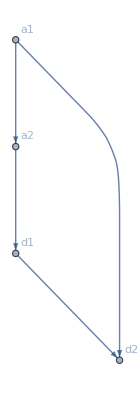

```mathematica
Graph[{a1->d2,a2->d1,a1->a2,d1->d2},VertexLabels->"Name"]
```

```mathematica
AcyclicGraphQ[Graph[{a1, d1, a2, d2}, {DirectedEdge[a1, d1], DirectedEdge[a2, d2]}]]
```

True

```mathematica
WeaklyConnectedGraphQ@%
```

False

```mathematica
DirectedEdge[#1,#2]
```

```mathematica
tb->ta
```

tb->ta

#### 1-loop coft with p_T

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/((kp+km)/2)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

(2^α (km+kp)^-α)/(km kp)

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

(kt<0&&0<y≤1)||(kt==0&&y>0)||(kt>0&&y≥1)

```mathematica
2/(kp km)*1/((kp+km)/2)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

2^(α-2 ϵ) ⅇ^(ⅈ bt kt (1-2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
(*f -> -ⅈ bt (-1+2 t)+ⅇ^-EulerGamma xm √y*)
```

```mathematica
%/.ⅇ^(ⅈ bt kt (-1+2 t)-ⅇ^-EulerGamma kt xm √y)->E^(- kt f)
```

2^(-1-2 ϵ) ⅇ^(-f kt) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

2^(α-2 ϵ) t^(-1/2-ϵ) (ⅈ bt (-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ]

```mathematica
1/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(-I kt bt Cos[θ])*jaco*kt^(1-2ϵ)//.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

2^(-1-2 ϵ) ⅇ^(ⅈ bt kt (-1+2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%/.ⅇ^(ⅈ bt kt (-1+2 t))->E^(-kt f),{kt,0,∞}]
```

ConditionalExpression[2^(-1-2 ϵ) f^(α+2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ], Re[α+2 ϵ]<0&&Re[f]>0]

```mathematica
Normal@%/.{f->(1-2t)bt I}
```

2^(-1-2 ϵ) (ⅈ bt (1-2 t))^(α+2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ]

```mathematica
Integrate[%,{y,0,1}]
```

ConditionalExpression[(2^(-2 ϵ) (ⅈ bt (1-2 t))^(α+2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) Gamma[-α-2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1])/α, Re[α]>0]

```mathematica
Integrate[(1-2t)^(α+2ϵ)t^(-1/2-ϵ)(1-t)^(-1/2-ϵ),{t,0,1}]
```

ConditionalExpression[Gamma[1/2-ϵ] (((-1)^(α+2 ϵ) 2^(-1/2+ϵ) Cos[π ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/π+((-2)^(α+2 ϵ) π^(3/2) Sec[π (α+ϵ)])/(Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ]))+(2^(-1/2+ϵ) ⅇ^(ⅈ π ϵ) π Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] (1-ⅈ Tan[π ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+α+ϵ]), Re[ϵ]<1/2&&Re[α+2 ϵ]>-1]

```mathematica
(2^(-2 ϵ) (ⅈ bt )^(α+2 ϵ) Gamma[-α-2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1])/α*(Gamma[1/2-ϵ] (((-1)^(α+2 ϵ) 2^(-1/2+ϵ) Cos[π ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/π+((-2)^(α+2 ϵ) π^(3/2) Sec[π (α+ϵ)])/(Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ]))+(2^(-1/2+ϵ) ⅇ^(ⅈ π ϵ) π Gamma[1+α+2 ϵ] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] (1-ⅈ Tan[π ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+α+ϵ]))//Expand
```

((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Hypergeometric2F1[α/2,α,(2+α)/2,-1] Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
%/.{Hypergeometric2F1[α/2,α,(2+α)/2,-1] ->HypExp[Hypergeometric2F1[α/2,α,(2+α)/2,-1] ,α,1],Hypergeometric2F1[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2]->F}
```

((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) F Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
Series[%/.bt->1,{α,0,1}]//Normal;
```

```mathematica
Series[%,{ϵ,0,1}]//Normal
```

-(π α)/(8 ϵ^3)+(π/4+1/4 π α (EulerGamma+Log[2]+PolyGamma[0,1/2]))/ϵ^2+1/(48 α ϵ)(-24 π-24 EulerGamma π α-12 EulerGamma^2 π α^2-π^3 α^2-24 π α Log[2]-24 EulerGamma π α^2 Log[2]-12 π α^2 Log[2]^2-12 √2 F α PolyGamma[0,-1/2]-24 π α PolyGamma[0,1/2]-24 EulerGamma π α^2 PolyGamma[0,1/2]-24 π α^2 Log[2] PolyGamma[0,1/2]-12 π α^2 PolyGamma[0,1/2]^2+12 √2 F α PolyGamma[0,3/2])+1/(48 α)(-48 EulerGamma π+48 ⅈ √2 F π-72 ⅈ π^2-72 EulerGamma^2 π α-144 ⅈ EulerGamma π^2 α-24 √2 F π^2 α+38 π^3 α-56 EulerGamma^3 π α^2+96 ⅈ √2 F π α^2-144 ⅈ EulerGamma^2 π^2 α^2+74 EulerGamma π^3 α^2+6 ⅈ √2 F π^3 α^2-48 EulerGamma π α Log[2]-72 ⅈ π^2 α Log[2]-72 EulerGamma^2 π α^2 Log[2]-144 ⅈ EulerGamma π^2 α^2 Log[2]+38 π^3 α^2 Log[2]-24 EulerGamma π α^2 Log[2]^2-36 ⅈ π^2 α^2 Log[2]^2-24 √2 F PolyGamma[0,-1/2]-72 ⅈ √2 F π α PolyGamma[0,-1/2]-84 √2 F α^2 PolyGamma[0,-1/2]+34 √2 F π^2 α^2 PolyGamma[0,-1/2]+12 √2 F α Log[2] PolyGamma[0,-1/2]+3 √2 F α^2 Log[2]^2 PolyGamma[0,-1/2]+18 √2 F α PolyGamma[0,-1/2]^2+36 ⅈ √2 F π α^2 PolyGamma[0,-1/2]^2-3 √2 F α^2 Log[2] PolyGamma[0,-1/2]^2-7 √2 F α^2 PolyGamma[0,-1/2]^3-48 EulerGamma π α PolyGamma[0,1/2]-72 ⅈ π^2 α PolyGamma[0,1/2]-72 EulerGamma^2 π α^2 PolyGamma[0,1/2]-144 ⅈ EulerGamma π^2 α^2 PolyGamma[0,1/2]+38 π^3 α^2 PolyGamma[0,1/2]-48 EulerGamma π α^2 Log[2] PolyGamma[0,1/2]-72 ⅈ π^2 α^2 Log[2] PolyGamma[0,1/2]+12 √2 F α PolyGamma[0,-1/2] PolyGamma[0,1/2]+6 √2 F α^2 Log[2] PolyGamma[0,-1/2] PolyGamma[0,1/2]-3 √2 F α^2 PolyGamma[0,-1/2]^2 PolyGamma[0,1/2]-24 EulerGamma π α^2 PolyGamma[0,1/2]^2-36 ⅈ π^2 α^2 PolyGamma[0,1/2]^2+3 √2 F α^2 PolyGamma[0,-1/2] PolyGamma[0,1/2]^2+24 √2 F PolyGamma[0,3/2]+24 ⅈ √2 F π α PolyGamma[0,3/2]+84 √2 F α^2 PolyGamma[0,3/2]-10 √2 F π^2 α^2 PolyGamma[0,3/2]-12 √2 F α Log[2] PolyGamma[0,3/2]-3 √2 F α^2 Log[2]^2 PolyGamma[0,3/2]-12 √2 F α PolyGamma[0,1/2] PolyGamma[0,3/2]-6 √2 F α^2 Log[2] PolyGamma[0,1/2] PolyGamma[0,3/2]-3 √2 F α^2 PolyGamma[0,1/2]^2 PolyGamma[0,3/2]-18 √2 F α PolyGamma[0,3/2]^2-12 ⅈ √2 F π α^2 PolyGamma[0,3/2]^2+3 √2 F α^2 Log[2] PolyGamma[0,3/2]^2+3 √2 F α^2 PolyGamma[0,1/2] PolyGamma[0,3/2]^2+7 √2 F α^2 PolyGamma[0,3/2]^3+8 π α^2 PolyGamma[2,1])+ϵ (1/24 F π (36 ⅈ √2-ⅈ √2 π^2-6 √2 π Log[2]-3 ⅈ √2 Log[2]^2-6 √2 π PolyGamma[0,1/2]-6 ⅈ √2 Log[2] PolyGamma[0,1/2]-3 ⅈ √2 PolyGamma[0,1/2]^2+18 √2 π PolyGamma[0,3/2]+6 ⅈ √2 Log[2] PolyGamma[0,3/2]+6 ⅈ √2 PolyGamma[0,1/2] PolyGamma[0,3/2]+9 ⅈ √2 PolyGamma[0,3/2]^2)+1/(12 α)(-12 EulerGamma^2 π-36 ⅈ EulerGamma π^2-24 √2 F π^2+22 π^3-12 ⅈ √2 F π Log[2]-18 ⅈ √2 F π PolyGamma[0,-1/2]+6 √2 F Log[2] PolyGamma[0,-1/2]+3 √2 F PolyGamma[0,-1/2]^2-12 ⅈ √2 F π PolyGamma[0,1/2]+6 √2 F PolyGamma[0,-1/2] PolyGamma[0,1/2]+6 ⅈ √2 F π PolyGamma[0,3/2]-6 √2 F Log[2] PolyGamma[0,3/2]-6 √2 F PolyGamma[0,1/2] PolyGamma[0,3/2]-3 √2 F PolyGamma[0,3/2]^2)+1/24 π (-40 EulerGamma^3-144 ⅈ EulerGamma^2 π+126 EulerGamma π^2+15 ⅈ π^3-24 EulerGamma^2 Log[2]-72 ⅈ EulerGamma π Log[2]+44 π^2 Log[2]-24 EulerGamma^2 PolyGamma[0,1/2]-72 ⅈ EulerGamma π PolyGamma[0,1/2]+44 π^2 PolyGamma[0,1/2]-3 PolyGamma[2,1/2]+16 PolyGamma[2,1])+1/24 F (144 ⅈ √2 π-12 ⅈ √2 π^3-36 √2 Log[2]+17 √2 π^2 Log[2]+√2 Log[2]^3-60 √2 PolyGamma[0,-1/2]+63 √2 π^2 PolyGamma[0,-1/2]+36 ⅈ √2 π Log[2] PolyGamma[0,-1/2]-3 √2 Log[2]^2 PolyGamma[0,-1/2]+36 ⅈ √2 π PolyGamma[0,-1/2]^2-9 √2 Log[2] PolyGamma[0,-1/2]^2-5 √2 PolyGamma[0,-1/2]^3-36 √2 PolyGamma[0,1/2]+17 √2 π^2 PolyGamma[0,1/2]+3 √2 Log[2]^2 PolyGamma[0,1/2]+36 ⅈ √2 π PolyGamma[0,-1/2] PolyGamma[0,1/2]-6 √2 Log[2] PolyGamma[0,-1/2] PolyGamma[0,1/2]-9 √2 PolyGamma[0,-1/2]^2 PolyGamma[0,1/2]+3 √2 Log[2] PolyGamma[0,1/2]^2-3 √2 PolyGamma[0,-1/2] PolyGamma[0,1/2]^2+√2 PolyGamma[0,1/2]^3+√2 PolyGamma[2,1/2]-5 √2 PolyGamma[2,3/2])+1/24 F (-84 ⅈ √2 π+ⅈ √2 π^3+36 √2 Log[2]+√2 π^2 Log[2]+3 ⅈ √2 π Log[2]^2-√2 Log[2]^3+36 √2 PolyGamma[0,1/2]+√2 π^2 PolyGamma[0,1/2]+6 ⅈ √2 π Log[2] PolyGamma[0,1/2]-3 √2 Log[2]^2 PolyGamma[0,1/2]+3 ⅈ √2 π PolyGamma[0,1/2]^2-3 √2 Log[2] PolyGamma[0,1/2]^2-√2 PolyGamma[0,1/2]^3+60 √2 PolyGamma[0,3/2]-21 √2 π^2 PolyGamma[0,3/2]-18 ⅈ √2 π Log[2] PolyGamma[0,3/2]+3 √2 Log[2]^2 PolyGamma[0,3/2]-18 ⅈ √2 π PolyGamma[0,1/2] PolyGamma[0,3/2]+6 √2 Log[2] PolyGamma[0,1/2] PolyGamma[0,3/2]+3 √2 PolyGamma[0,1/2]^2 PolyGamma[0,3/2]-21 ⅈ √2 π PolyGamma[0,3/2]^2+9 √2 Log[2] PolyGamma[0,3/2]^2+9 √2 PolyGamma[0,1/2] PolyGamma[0,3/2]^2+5 √2 PolyGamma[0,3/2]^3-√2 PolyGamma[2,1/2]+5 √2 PolyGamma[2,3/2])+α (1/2880 π (-4080 EulerGamma^4-17280 ⅈ EulerGamma^3 π+19560 EulerGamma^2 π^2+3600 ⅈ EulerGamma π^3+997 π^4-4800 EulerGamma^3 Log[2]-17280 ⅈ EulerGamma^2 π Log[2]+15120 EulerGamma π^2 Log[2]+1800 ⅈ π^3 Log[2]-1440 EulerGamma^2 Log[2]^2-4320 ⅈ EulerGamma π Log[2]^2+2640 π^2 Log[2]^2-4800 EulerGamma^3 PolyGamma[0,1/2]-17280 ⅈ EulerGamma^2 π PolyGamma[0,1/2]+15120 EulerGamma π^2 PolyGamma[0,1/2]+1800 ⅈ π^3 PolyGamma[0,1/2]-2880 EulerGamma^2 Log[2] PolyGamma[0,1/2]-8640 ⅈ EulerGamma π Log[2] PolyGamma[0,1/2]+5280 π^2 Log[2] PolyGamma[0,1/2]-1440 EulerGamma^2 PolyGamma[0,1/2]^2-4320 ⅈ EulerGamma π PolyGamma[0,1/2]^2+2640 π^2 PolyGamma[0,1/2]^2-720 EulerGamma PolyGamma[2,1/2]-540 ⅈ π PolyGamma[2,1/2]-360 Log[2] PolyGamma[2,1/2]-360 PolyGamma[0,1/2] PolyGamma[2,1/2]+4800 EulerGamma PolyGamma[2,1]+4320 ⅈ π PolyGamma[2,1]+1920 Log[2] PolyGamma[2,1]+1920 PolyGamma[0,1/2] PolyGamma[2,1])+1/48 F π (-60 √2 π+5 √2 π^3-12 ⅈ √2 Log[2]+4 ⅈ √2 π^2 Log[2]-3 √2 π Log[2]^2-ⅈ √2 Log[2]^3-12 ⅈ √2 PolyGamma[0,1/2]+4 ⅈ √2 π^2 PolyGamma[0,1/2]-6 √2 π Log[2] PolyGamma[0,1/2]-3 ⅈ √2 Log[2]^2 PolyGamma[0,1/2]-3 √2 π PolyGamma[0,1/2]^2-3 ⅈ √2 Log[2] PolyGamma[0,1/2]^2-ⅈ √2 PolyGamma[0,1/2]^3-84 ⅈ √2 PolyGamma[0,3/2]+6 ⅈ √2 π^2 PolyGamma[0,3/2]+6 √2 π Log[2] PolyGamma[0,3/2]+3 ⅈ √2 Log[2]^2 PolyGamma[0,3/2]+6 √2 π PolyGamma[0,1/2] PolyGamma[0,3/2]+6 ⅈ √2 Log[2] PolyGamma[0,1/2] PolyGamma[0,3/2]+3 ⅈ √2 PolyGamma[0,1/2]^2 PolyGamma[0,3/2]-15 √2 π PolyGamma[0,3/2]^2-3 ⅈ √2 Log[2] PolyGamma[0,3/2]^2-3 ⅈ √2 PolyGamma[0,1/2] PolyGamma[0,3/2]^2-7 ⅈ √2 PolyGamma[0,3/2]^3-ⅈ √2 PolyGamma[2,1/2]-7 ⅈ √2 PolyGamma[2,3/2])+F π (-1/3 (7 π^2+12 ⅈ π PolyGamma[0,3/2]-12 PolyGamma[0,3/2]^2) (-(EulerGamma^2+π^2/6)/(4 √2 π)+(2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))))/(√π)-(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) PolyGamma[0,3/2])/(√π)-2 EulerGamma ((2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π))-(8-π^2+2 PolyGamma[0,3/2]^2)/(32 √2 π))-(2 ⅈ π-4 PolyGamma[0,3/2]) (-(2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))) PolyGamma[0,3/2])/(√π)+2 (EulerGamma^2+π^2/6) ((2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π))+(((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) (8-π^2+2 PolyGamma[0,3/2]^2))/(2 √π)-2 EulerGamma ((2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))))/(√π)-(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) PolyGamma[0,3/2])/(√π)-(8-π^2+2 PolyGamma[0,3/2]^2)/(32 √2 π))-(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(6 √2 π)+1/(√π)2 (-(((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) PolyGamma[0,1/2])/(√π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2])/(192 √(2 π))+1/(√π)((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2)))-(-24 PolyGamma[0,3/2]+3 π^2 PolyGamma[0,3/2]-2 PolyGamma[0,3/2]^3-2 PolyGamma[2,3/2])/(96 √2 π))-(EulerGamma/(4 √2 π)+(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π)) ((8 EulerGamma π^2)/3-(8 ⅈ π^3)/3+2 ⅈ π (-8+π^2)-4 (-8+π^2) PolyGamma[0,3/2]-4/3 (-24 EulerGamma+3 EulerGamma π^2-2 π^2 PolyGamma[0,3/2])+8 PolyGamma[2,1]-4 ((2 EulerGamma π^2)/3+2 PolyGamma[2,1])+2/3 (-48 EulerGamma+6 EulerGamma π^2+4 π^2 PolyGamma[0,3/2]-3 PolyGamma[2,3/2])+4 PolyGamma[2,3/2])+1/(8 √2 π)(-64+16 π^2-(31 π^4)/15+2 (-96+π^4)+8 (-π^4/15-4 EulerGamma PolyGamma[2,1])-4 (π^4/45-4 EulerGamma PolyGamma[2,1])-4 (π^4/9-4 EulerGamma PolyGamma[2,1])+2 ⅈ π PolyGamma[2,3/2]-4 PolyGamma[0,3/2] PolyGamma[2,3/2]+4/3 (-8 π^2+π^4+12 PolyGamma[0,3/2] PolyGamma[2,1]-3 EulerGamma PolyGamma[2,3/2])-8 (-1/3 π^2 (-4+π^2/2)+1/2 (-16+π^4/6)+2 PolyGamma[0,3/2] PolyGamma[2,1]-1/2 EulerGamma PolyGamma[2,3/2]))+2 (((((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))) (8-π^2+2 PolyGamma[0,3/2]^2))/(2 √π)+2 (EulerGamma^2+π^2/6) ((2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))))/(√π)-(2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) PolyGamma[0,3/2])/(√π)-(8-π^2+2 PolyGamma[0,3/2]^2)/(32 √2 π))+4/3 ((2 ((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))))/(√π)+PolyGamma[0,3/2]/(8 √2 π)) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])-(EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1])/(12 √2 π)-1/(√π)2 PolyGamma[0,3/2] (-(((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) PolyGamma[0,1/2])/(√π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2])/(192 √(2 π))+1/(√π)((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2)))+1/(√π)2 ((((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2]))/(12 √π)-(-π^4-12 π^2 PolyGamma[0,1/2]^2+4 PolyGamma[0,1/2]^4+16 PolyGamma[0,1/2] PolyGamma[2,1/2])/(1536 √(2 π))-1/(√π)PolyGamma[0,1/2] ((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2))+1/(√π)((-EulerGamma^2-π^2/6) (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))-EulerGamma (-(ⅈ π^3)/(6 √2)+(π^2 Log[2])/(4 √2)+(ⅈ π Log[2]^2)/(8 √2)-Log[2]^3/(48 √2))+1/2 (-π^4/(12 √2)-(ⅈ π^3 Log[2])/(6 √2)+(π^2 Log[2]^2)/(8 √2)+(ⅈ π Log[2]^3)/(24 √2)-Log[2]^4/(192 √2))+2/3 ((ⅈ π)/(4 √2)-Log[2]/(8 √2)) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+(-EulerGamma^4-EulerGamma^2 π^2-(3 π^4)/20+4 EulerGamma PolyGamma[2,1])/(24 √2)))-2 EulerGamma (-(2 (((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2)))/(√π)-((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) PolyGamma[0,1/2])/(√π)-(-π^2+2 PolyGamma[0,1/2]^2)/(64 √(2 π))) PolyGamma[0,3/2])/(√π)+(((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) (8-π^2+2 PolyGamma[0,3/2]^2))/(2 √π)+1/(√π)2 (-(((-EulerGamma^2-π^2/6)/(8 √2)-EulerGamma ((ⅈ π)/(4 √2)-Log[2]/(8 √2))+1/2 (π^2/(4 √2)+(ⅈ π Log[2])/(4 √2)-Log[2]^2/(16 √2))) PolyGamma[0,1/2])/(√π)+((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2))) (-π^2+2 PolyGamma[0,1/2]^2))/(4 √π)-(3 π^2 PolyGamma[0,1/2]-2 PolyGamma[0,1/2]^3-2 PolyGamma[2,1/2])/(192 √(2 π))+1/(√π)((-EulerGamma^2-π^2/6) ((ⅈ π)/(4 √2)-Log[2]/(8 √2))-EulerGamma (-π^2/(4 √2)-(ⅈ π Log[2])/(4 √2)+Log[2]^2/(16 √2))+1/2 ((ⅈ π^3)/(6 √2)-(π^2 Log[2])/(4 √2)-(ⅈ π Log[2]^2)/(8 √2)+Log[2]^3/(48 √2))+(-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])/(12 √2)))-(-24 PolyGamma[0,3/2]+3 π^2 PolyGamma[0,3/2]-2 PolyGamma[0,3/2]^3-2 PolyGamma[2,3/2])/(96 √2 π))+(((-EulerGamma/(8 √2)+1/2 (-(ⅈ π)/(4 √2)+Log[2]/(8 √2)))/(√π)+PolyGamma[0,1/2]/(16 √(2 π))) (-24 PolyGamma[0,3/2]+3 π^2 PolyGamma[0,3/2]-2 PolyGamma[0,3/2]^3-2 PolyGamma[2,3/2]))/(6 √π)-(576-48 π^2-π^4+96 PolyGamma[0,3/2]^2-12 π^2 PolyGamma[0,3/2]^2+4 PolyGamma[0,3/2]^4+16 PolyGamma[0,3/2] PolyGamma[2,3/2])/(768 √2 π)))+1/π F (-1/3 (31 π^2+36 ⅈ π PolyGamma[0,-1/2]-12 PolyGamma[0,-1/2]^2) (-(π (-EulerGamma^2-π^2/6))/(4 √2)+(π (EulerGamma^2+π^2/6))/(4 √2)-EulerGamma (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))-2 EulerGamma ((EulerGamma π)/(4 √2)+1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2)))+1/2 (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))+√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]+1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)))-1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2)) ((8 EulerGamma π^2)/3-8 ⅈ π^3-6 ⅈ π (8+π^2)+4 (8+π^2) PolyGamma[0,-1/2]+4/3 (24 EulerGamma+3 EulerGamma π^2+2 π^2 PolyGamma[0,-1/2])+8 PolyGamma[2,1]-4 ((2 EulerGamma π^2)/3+2 PolyGamma[2,1])+4 PolyGamma[2,3/2]-2/3 (48 EulerGamma+6 EulerGamma π^2-4 π^2 PolyGamma[0,-1/2]+3 PolyGamma[2,3/2]))-1/(8 √2)π (-64-16 π^2-(31 π^4)/15-2 (96+π^4)+8 (-π^4/15-4 EulerGamma PolyGamma[2,1])-4 (π^4/45-4 EulerGamma PolyGamma[2,1])-4 (π^4/9-4 EulerGamma PolyGamma[2,1])+6 ⅈ π PolyGamma[2,3/2]-4 PolyGamma[0,-1/2] PolyGamma[2,3/2]-8 (-1/3 π^2 (-4-π^2/2)+1/12 (-96-π^4)+2 PolyGamma[0,-1/2] PolyGamma[2,1]-1/2 EulerGamma PolyGamma[2,3/2])-4/3 (8 π^2+π^4-12 PolyGamma[0,-1/2] PolyGamma[2,1]+3 EulerGamma PolyGamma[2,3/2]))-(6 ⅈ π-4 PolyGamma[0,-1/2]) ((-EulerGamma^2-π^2/6) (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))+2 (EulerGamma^2+π^2/6) ((EulerGamma π)/(4 √2)+1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2)))-EulerGamma (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]-1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2))-2 EulerGamma (-(π (-EulerGamma^2-π^2/6))/(4 √2)-EulerGamma (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))+1/2 (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))+√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]+1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)))+1/2 (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) PolyGamma[0,1/2]-1/2 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)+1/24 √(π/2) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])-√π (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2))))+2 ((-EulerGamma^2-π^2/6) (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]-1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2))+2 (EulerGamma^2+π^2/6) (-(π (-EulerGamma^2-π^2/6))/(4 √2)-EulerGamma (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))+1/2 (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))+√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]+1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)))+2/3 (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2)) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+4/3 ((EulerGamma π)/(4 √2)+1/2 (-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])-(π PolyGamma[0,1/2])/(4 √2))) (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+(π (EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1]))/(12 √2)-(π (-EulerGamma^4-EulerGamma^2 π^2-(3 π^4)/20+4 EulerGamma PolyGamma[2,1]))/(12 √2)-EulerGamma (-√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) PolyGamma[0,1/2]+1/2 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)-1/24 √(π/2) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])+√π (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2)))+1/2 (-1/2 (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)-1/6 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])+1/96 √(π/2) ((7 π^(9/2))/4+3 π^(5/2) PolyGamma[0,1/2]^2+√π PolyGamma[0,1/2]^4+4 √π PolyGamma[0,1/2] PolyGamma[2,1/2])+√π PolyGamma[0,1/2] (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2))-√π (-2 √π ((41 π^4)/(96 √2)+(9 ⅈ π^3 Log[2])/(16 √2)-(9 π^2 Log[2]^2)/(32 √2)-(ⅈ π Log[2]^3)/(16 √2)+Log[2]^4/(192 √2)-1/2 π^2 (-(9 π^2)/(16 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)))+2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))) PolyGamma[0,-1/2]+1/2 (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+1/6 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])+1/(192 √2)(-6 √π (4+π^2/2)^2-2 √π (2 π^4-6 (-16+π^4/6))-12 √π (4+π^2/2) PolyGamma[0,-1/2]^2-2 √π PolyGamma[0,-1/2]^4-8 √π PolyGamma[0,-1/2] PolyGamma[2,3/2])))-2 EulerGamma ((-EulerGamma^2-π^2/6) (√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2])+(π PolyGamma[0,1/2])/(4 √2))-EulerGamma (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2))-√π (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) PolyGamma[0,1/2]-1/8 √(π/2) (π^(5/2)/2+√π PolyGamma[0,1/2]^2))-(π (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1]))/(6 √2)+1/2 (√π (-2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2))+2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) PolyGamma[0,-1/2]+(-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)/(16 √2)) PolyGamma[0,1/2]-1/2 (-2 √π ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2))+1/4 √(π/2) PolyGamma[0,-1/2]) (π^(5/2)/2+√π PolyGamma[0,1/2]^2)+1/24 √(π/2) (-3/2 π^(5/2) PolyGamma[0,1/2]-√π PolyGamma[0,1/2]^3-√π PolyGamma[2,1/2])-√π (-2 √π (-(9 ⅈ π^3)/(16 √2)+(9 π^2 Log[2])/(16 √2)+(3 ⅈ π Log[2]^2)/(16 √2)-Log[2]^3/(48 √2)-1/2 π^2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)))+2 √π (-(5 π^2)/(8 √2)-(3 ⅈ π Log[2])/(8 √2)+Log[2]^2/(16 √2)) PolyGamma[0,-1/2]+1/2 ((3 ⅈ π)/(8 √2)-Log[2]/(8 √2)) (-2 √π (4+π^2/2)-2 √π PolyGamma[0,-1/2]^2)+(6 √π (4+π^2/2) PolyGamma[0,-1/2]+2 √π PolyGamma[0,-1/2]^3+2 √π PolyGamma[2,3/2])/(48 √2))))))))

```mathematica
Series[%2810*E^(2EulerGamma ϵ)*(4π)^ϵ//Expand//FunctionExpand,{ϵ,0,1}]//Normal//Expand
```

-2 ⅈ √2 F π+ⅈ √2 EulerGamma F π-3/2 ⅈ EulerGamma π^2-(F π^2)/(√2)+(19 π^3)/24-(2 EulerGamma π)/α+(ⅈ √2 F π)/α-(3 ⅈ π^2)/(2 α)-1/3 EulerGamma^3 π α+4 ⅈ √2 F π α-2 ⅈ √2 EulerGamma F π α+(ⅈ EulerGamma^2 F π α)/(√2)-3/4 ⅈ EulerGamma^2 π^2 α+√2 F π^2 α-(EulerGamma F π^2 α)/(√2)+17/24 EulerGamma π^3 α+(ⅈ F π^3 α)/(4 √2)-(π α)/(8 ϵ^3)+π/(4 ϵ^2)-(EulerGamma π α)/(4 ϵ^2)+(EulerGamma π)/(2 ϵ)-π/(2 α ϵ)-(EulerGamma^2 π α)/(4 ϵ)-(π^3 α)/(48 ϵ)-4/3 EulerGamma^3 π ϵ+8 ⅈ √2 F π ϵ-10 ⅈ √2 EulerGamma F π ϵ+4 ⅈ √2 EulerGamma^2 F π ϵ-6 ⅈ EulerGamma^2 π^2 ϵ+5 √2 F π^2 ϵ-4 √2 EulerGamma F π^2 ϵ+5 EulerGamma π^3 ϵ-(ⅈ F π^3 ϵ)/(√2)+5/8 ⅈ π^4 ϵ-(4 EulerGamma^2 π ϵ)/α-(2 ⅈ √2 F π ϵ)/α+(4 ⅈ √2 EulerGamma F π ϵ)/α-(6 ⅈ EulerGamma π^2 ϵ)/α-(2 √2 F π^2 ϵ)/α+(11 π^3 ϵ)/(6 α)-2/3 EulerGamma^4 π α ϵ-24 ⅈ √2 F π α ϵ+24 ⅈ √2 EulerGamma F π α ϵ-9 ⅈ √2 EulerGamma^2 F π α ϵ+2 ⅈ √2 EulerGamma^3 F π α ϵ-3 ⅈ EulerGamma^3 π^2 α ϵ-12 √2 F π^2 α ϵ+9 √2 EulerGamma F π^2 α ϵ-3 √2 EulerGamma^2 F π^2 α ϵ+47/12 EulerGamma^2 π^3 α ϵ+(3 ⅈ F π^3 α ϵ)/(2 √2)+5/8 ⅈ EulerGamma π^4 α ϵ-(F π^4 α ϵ)/(√2)+(997 π^5 α ϵ)/2880-3 √2 F Log[2]+3 EulerGamma π Log[2]+2 ⅈ √2 F π Log[2]+3/2 ⅈ π^2 Log[2]-(π Log[2])/α+4 √2 F α Log[2]+4 EulerGamma^2 π α Log[2]-6 ⅈ √2 F π α Log[2]+9/2 ⅈ EulerGamma π^2 α Log[2]-√2 F π^2 α Log[2]-5/6 π^3 α Log[2]-(π α Log[2])/(2 ϵ^2)+(π Log[2])/ϵ+8 √2 F ϵ Log[2]-6 √2 EulerGamma F ϵ Log[2]+4 EulerGamma^2 π ϵ Log[2]-18 ⅈ √2 F π ϵ Log[2]+5 ⅈ √2 EulerGamma F π ϵ Log[2]+3 ⅈ EulerGamma π^2 ϵ Log[2]-(13 F π^2 ϵ Log[2])/(√2)-1/4 π^3 ϵ Log[2]-(2 √2 F ϵ Log[2])/α-(4 EulerGamma π ϵ Log[2])/α+(5 ⅈ √2 F π ϵ Log[2])/α-(3 ⅈ π^2 ϵ Log[2])/α-25 √2 F α ϵ Log[2]+8 √2 EulerGamma F α ϵ Log[2]+29/3 EulerGamma^3 π α ϵ Log[2]+44 ⅈ √2 F π α ϵ Log[2]-14 ⅈ √2 EulerGamma F π α ϵ Log[2]+(ⅈ EulerGamma^2 F π α ϵ Log[2])/(√2)+18 ⅈ EulerGamma^2 π^2 α ϵ Log[2]+49/3 √2 F π^2 α ϵ Log[2]-(5 EulerGamma F π^2 α ϵ Log[2])/(√2)-29/4 EulerGamma π^3 α ϵ Log[2]-(3 ⅈ F π^3 α ϵ Log[2])/(4 √2)-5/8 ⅈ π^4 α ϵ Log[2]+3/2 π Log[2]^2+(F α Log[2]^2)/(√2)+7/2 EulerGamma π α Log[2]^2+9/4 ⅈ π^2 α Log[2]^2-3 √2 F ϵ Log[2]^2+5 EulerGamma π ϵ Log[2]^2+2 ⅈ √2 F π ϵ Log[2]^2+3 ⅈ π^2 ϵ Log[2]^2-(π ϵ Log[2]^2)/α+4 √2 F α ϵ Log[2]^2+√2 EulerGamma F α ϵ Log[2]^2+14 EulerGamma^2 π α ϵ Log[2]^2-6 ⅈ √2 F π α ϵ Log[2]^2+18 ⅈ EulerGamma π^2 α ϵ Log[2]^2-√2 F π^2 α ϵ Log[2]^2-35/8 π^3 α ϵ Log[2]^2+5/6 π α Log[2]^3+4/3 π ϵ Log[2]^3+(3 F α ϵ Log[2]^3)/(2 √2)+20/3 EulerGamma π α ϵ Log[2]^3+9/2 ⅈ π^2 α ϵ Log[2]^3+13/12 π α ϵ Log[2]^4+(3 F Log[4])/(√2)-2 √2 F α Log[4]-9/4 EulerGamma^2 π α Log[4]+ⅈ √2 F π α Log[4]+ⅈ √2 EulerGamma F π α Log[4]-3/2 ⅈ EulerGamma π^2 α Log[4]-(EulerGamma π α Log[4])/(2 ϵ)-4 √2 F ϵ Log[4]+3 √2 EulerGamma F ϵ Log[4]+2 ⅈ √2 F π ϵ Log[4]+4 ⅈ √2 EulerGamma F π ϵ Log[4]+(√2 F ϵ Log[4])/α+(25 F α ϵ Log[4])/(√2)-4 √2 EulerGamma F α ϵ Log[4]-9/2 EulerGamma^3 π α ϵ Log[4]-4 ⅈ √2 F π α ϵ Log[4]-8 ⅈ √2 EulerGamma F π α ϵ Log[4]+5 ⅈ √2 EulerGamma^2 F π α ϵ Log[4]-27/4 ⅈ EulerGamma^2 π^2 α ϵ Log[4]-2/3 √2 F π^2 α ϵ Log[4]-4 √2 EulerGamma F π^2 α ϵ Log[4]+11/6 EulerGamma π^3 α ϵ Log[4]-(F α Log[2] Log[4])/(2 √2)+(3 F ϵ Log[2] Log[4])/(√2)-2 √2 F α ϵ Log[2] Log[4]-(EulerGamma F α ϵ Log[2] Log[4])/(√2)-2 EulerGamma^2 π α ϵ Log[2] Log[4]+ⅈ √2 F π α ϵ Log[2] Log[4]+ⅈ √2 EulerGamma F π α ϵ Log[2] Log[4]-(3 F α ϵ Log[2]^2 Log[4])/(4 √2)-3/2 EulerGamma π α Log[4]^2+(ⅈ F π α Log[4]^2)/(√2)-3/4 ⅈ π^2 α Log[4]^2-(π α Log[4]^2)/(4 ϵ)+2 ⅈ √2 F π ϵ Log[4]^2-25/8 EulerGamma^2 π α ϵ Log[4]^2-5 ⅈ √2 F π α ϵ Log[4]^2+4 ⅈ √2 EulerGamma F π α ϵ Log[4]^2-9/2 ⅈ EulerGamma π^2 α ϵ Log[4]^2-2 √2 F π^2 α ϵ Log[4]^2+11/12 π^3 α ϵ Log[4]^2-EulerGamma π α ϵ Log[2] Log[4]^2+(ⅈ F π α ϵ Log[2] Log[4]^2)/(√2)-1/4 π α Log[4]^3-3/4 EulerGamma π α ϵ Log[4]^3+ⅈ √2 F π α ϵ Log[4]^3-3/4 ⅈ π^2 α ϵ Log[4]^3-1/8 π α ϵ Log[4]^4+1/2 EulerGamma π Log[π]-(π Log[π])/(2 α)-1/4 EulerGamma^2 π α Log[π]-1/48 π^3 α Log[π]-(π α Log[π])/(8 ϵ^2)+(π Log[π])/(4 ϵ)-(EulerGamma π α Log[π])/(4 ϵ)-2 ⅈ √2 F π ϵ Log[π]+ⅈ √2 EulerGamma F π ϵ Log[π]-3/2 ⅈ EulerGamma π^2 ϵ Log[π]-(F π^2 ϵ Log[π])/(√2)+19/24 π^3 ϵ Log[π]-(2 EulerGamma π ϵ Log[π])/α+(ⅈ √2 F π ϵ Log[π])/α-(3 ⅈ π^2 ϵ Log[π])/(2 α)-1/3 EulerGamma^3 π α ϵ Log[π]+4 ⅈ √2 F π α ϵ Log[π]-2 ⅈ √2 EulerGamma F π α ϵ Log[π]+(ⅈ EulerGamma^2 F π α ϵ Log[π])/(√2)-3/4 ⅈ EulerGamma^2 π^2 α ϵ Log[π]+√2 F π^2 α ϵ Log[π]-(EulerGamma F π^2 α ϵ Log[π])/(√2)+17/24 EulerGamma π^3 α ϵ Log[π]+(ⅈ F π^3 α ϵ Log[π])/(4 √2)+π Log[2] Log[π]-(π α Log[2] Log[π])/(2 ϵ)-3 √2 F ϵ Log[2] Log[π]+3 EulerGamma π ϵ Log[2] Log[π]+2 ⅈ √2 F π ϵ Log[2] Log[π]+3/2 ⅈ π^2 ϵ Log[2] Log[π]-(π ϵ Log[2] Log[π])/α+4 √2 F α ϵ Log[2] Log[π]+4 EulerGamma^2 π α ϵ Log[2] Log[π]-6 ⅈ √2 F π α ϵ Log[2] Log[π]+9/2 ⅈ EulerGamma π^2 α ϵ Log[2] Log[π]-√2 F π^2 α ϵ Log[2] Log[π]-5/6 π^3 α ϵ Log[2] Log[π]+3/2 π ϵ Log[2]^2 Log[π]+(F α ϵ Log[2]^2 Log[π])/(√2)+7/2 EulerGamma π α ϵ Log[2]^2 Log[π]+9/4 ⅈ π^2 α ϵ Log[2]^2 Log[π]+5/6 π α ϵ Log[2]^3 Log[π]-1/2 EulerGamma π α Log[4] Log[π]+(3 F ϵ Log[4] Log[π])/(√2)-2 √2 F α ϵ Log[4] Log[π]-9/4 EulerGamma^2 π α ϵ Log[4] Log[π]+ⅈ √2 F π α ϵ Log[4] Log[π]+ⅈ √2 EulerGamma F π α ϵ Log[4] Log[π]-3/2 ⅈ EulerGamma π^2 α ϵ Log[4] Log[π]-(F α ϵ Log[2] Log[4] Log[π])/(2 √2)-1/4 π α Log[4]^2 Log[π]-3/2 EulerGamma π α ϵ Log[4]^2 Log[π]+(ⅈ F π α ϵ Log[4]^2 Log[π])/(√2)-3/4 ⅈ π^2 α ϵ Log[4]^2 Log[π]-1/4 π α ϵ Log[4]^3 Log[π]+1/8 π Log[π]^2-1/8 EulerGamma π α Log[π]^2-(π α Log[π]^2)/(16 ϵ)+1/4 EulerGamma π ϵ Log[π]^2-(π ϵ Log[π]^2)/(4 α)-1/8 EulerGamma^2 π α ϵ Log[π]^2-1/96 π^3 α ϵ Log[π]^2-1/4 π α Log[2] Log[π]^2+1/2 π ϵ Log[2] Log[π]^2-1/4 EulerGamma π α ϵ Log[4] Log[π]^2-1/8 π α ϵ Log[4]^2 Log[π]^2-1/48 π α Log[π]^3+1/24 π ϵ Log[π]^3-1/24 EulerGamma π α ϵ Log[π]^3-1/12 π α ϵ Log[2] Log[π]^3-1/192 π α ϵ Log[π]^4-1/3 π α Zeta[3]+5/12 π ϵ Zeta[3]-11/12 EulerGamma π α ϵ Zeta[3]+7 ⅈ √2 F π α ϵ Zeta[3]-3/8 ⅈ π^2 α ϵ Zeta[3]-1/4 π α ϵ Log[2] Zeta[3]-5/12 π α ϵ Log[4] Zeta[3]-1/3 π α ϵ Log[π] Zeta[3]

```mathematica
((-1)^(α+2 ϵ) 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) F Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/(π α)+(2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+((-1)^(α+2 ϵ) 2^α (ⅈ bt)^(α+2 ϵ) π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])-(ⅈ 2^(-1/2-ϵ) (ⅈ bt)^(α+2 ϵ) ⅇ^(ⅈ π ϵ) F π Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])//.{Hypergeometric2F1[α/2,α,(2+α)/2,-1] ->HypExp[Hypergeometric2F1[α/2,α,(2+α)/2,-1] ,α,1],F->π/(2 √2),I bt->1,(-1)^(α+2ϵ)->E^(I π α),E^(I π ϵ):>Cos[π ϵ]+ I Sin[π ϵ],E^(I π α):>Cos[π α]+ I Sin[π α]}//Expand
```

(2^(-2-ϵ) Cos[π α] Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/α+(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+(2^α π^(3/2) Cos[π α] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])+(ⅈ 2^(-2-ϵ) Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ] Sin[π α])/α+(ⅈ 2^α π^(3/2) Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)] Sin[π α])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])+(2^(-2-ϵ) π^2 Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Sin[π ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
%/.{I->0}
```

(2^(-2-ϵ) Cos[π α] Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Gamma[-1/2-α-ϵ] Gamma[1+α+2 ϵ])/α+(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])+(2^α π^(3/2) Cos[π α] Gamma[-α-2 ϵ] Gamma[1/2-ϵ] Sec[π (α+ϵ)])/(α Gamma[1/2-α/2] Gamma[1+α] Gamma[1/2-α/2-ϵ])+(2^(-2-ϵ) π^2 Gamma[-α-2 ϵ] Gamma[1+α+2 ϵ] Sin[π ϵ] Tan[π ϵ])/(α Gamma[1/2+ϵ] Gamma[3/2+α+ϵ])

```mathematica
Series[%*E^(- EulerGamma(ϵ+α))*1/(√π Gamma[1/2-ϵ]),{α,0,1}]//Normal
```

(2^(-2-ϵ) ⅇ^(-EulerGamma ϵ) Cos[π ϵ] Gamma[-2 ϵ] (π^2 Gamma[1+2 ϵ]+Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ] Gamma[1+2 ϵ]+2^(2+ϵ) π Gamma[1/2+ϵ] Gamma[3/2+ϵ] Sec[π ϵ]^2+π^2 Gamma[1+2 ϵ] Tan[π ϵ]^2))/(√π α Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ])+1/(√π Gamma[1/2-ϵ])(-1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-2-ϵ) ⅇ^(-EulerGamma ϵ) EulerGamma Gamma[-2 ϵ] Sec[π ϵ] (2^(2+ϵ) π Gamma[1/2+ϵ] Gamma[3/2+ϵ]+π^2 Cos[π ϵ]^2 Gamma[1+2 ϵ]+Cos[π ϵ]^2 Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ] Gamma[1+2 ϵ]+π^2 Gamma[1+2 ϵ] Sin[π ϵ]^2)+ⅇ^(-EulerGamma ϵ) (-2^(-2-ϵ) Cos[π ϵ] Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-1/2-ϵ]+PolyGamma[0,-2 ϵ]-PolyGamma[0,1+2 ϵ])-(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])-(2^(-2-ϵ) π^2 Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]) Sin[π ϵ] Tan[π ϵ])/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])+1/2 π Gamma[-2 ϵ] Sec[π ϵ] (2 EulerGamma+2 Log[2]+PolyGamma[0,1/2]+PolyGamma[0,1/2-ϵ]-2 PolyGamma[0,-2 ϵ]+2 π Tan[π ϵ])))+1/(√π Gamma[1/2-ϵ])α (1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-3-ϵ) ⅇ^(-EulerGamma ϵ) EulerGamma^2 Gamma[-2 ϵ] Sec[π ϵ] (2^(2+ϵ) π Gamma[1/2+ϵ] Gamma[3/2+ϵ]+π^2 Cos[π ϵ]^2 Gamma[1+2 ϵ]+Cos[π ϵ]^2 Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[1/2+ϵ] Gamma[3/2+ϵ] Gamma[1+2 ϵ]+π^2 Gamma[1+2 ϵ] Sin[π ϵ]^2)-ⅇ^(-EulerGamma ϵ) EulerGamma (-2^(-2-ϵ) Cos[π ϵ] Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-1/2-ϵ]+PolyGamma[0,-2 ϵ]-PolyGamma[0,1+2 ϵ])-(2^(-2-ϵ) π^2 Cos[π ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]))/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])-(2^(-2-ϵ) π^2 Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]+PolyGamma[0,3/2+ϵ]-PolyGamma[0,1+2 ϵ]) Sin[π ϵ] Tan[π ϵ])/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])+1/2 π Gamma[-2 ϵ] Sec[π ϵ] (2 EulerGamma+2 Log[2]+PolyGamma[0,1/2]+PolyGamma[0,1/2-ϵ]-2 PolyGamma[0,-2 ϵ]+2 π Tan[π ϵ]))+ⅇ^(-EulerGamma ϵ) (-2^(-3-ϵ) Cos[π ϵ] Gamma[-1/2-ϵ] Gamma[1/2-ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (π^2-PolyGamma[0,-1/2-ϵ]^2-2 PolyGamma[0,-1/2-ϵ] PolyGamma[0,-2 ϵ]-PolyGamma[0,-2 ϵ]^2+2 PolyGamma[0,-1/2-ϵ] PolyGamma[0,1+2 ϵ]+2 PolyGamma[0,-2 ϵ] PolyGamma[0,1+2 ϵ]-PolyGamma[0,1+2 ϵ]^2-PolyGamma[1,-1/2-ϵ]-PolyGamma[1,-2 ϵ]-PolyGamma[1,1+2 ϵ])+1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-3-ϵ) π^2 Cos[π ϵ] Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]^2+2 PolyGamma[0,-2 ϵ] PolyGamma[0,3/2+ϵ]+PolyGamma[0,3/2+ϵ]^2-2 PolyGamma[0,-2 ϵ] PolyGamma[0,1+2 ϵ]-2 PolyGamma[0,3/2+ϵ] PolyGamma[0,1+2 ϵ]+PolyGamma[0,1+2 ϵ]^2+PolyGamma[1,-2 ϵ]-PolyGamma[1,3/2+ϵ]+PolyGamma[1,1+2 ϵ])+1/(Gamma[1/2+ϵ] Gamma[3/2+ϵ])2^(-3-ϵ) π^2 Gamma[-2 ϵ] Gamma[1+2 ϵ] (PolyGamma[0,-2 ϵ]^2+2 PolyGamma[0,-2 ϵ] PolyGamma[0,3/2+ϵ]+PolyGamma[0,3/2+ϵ]^2-2 PolyGamma[0,-2 ϵ] PolyGamma[0,1+2 ϵ]-2 PolyGamma[0,3/2+ϵ] PolyGamma[0,1+2 ϵ]+PolyGamma[0,1+2 ϵ]^2+PolyGamma[1,-2 ϵ]-PolyGamma[1,3/2+ϵ]+PolyGamma[1,1+2 ϵ]) Sin[π ϵ] Tan[π ϵ]+1/48 π Sec[π ϵ] (24 EulerGamma^2 Gamma[-2 ϵ]-7 π^2 Gamma[-2 ϵ]+48 EulerGamma Gamma[-2 ϵ] Log[2]+24 Gamma[-2 ϵ] Log[2]^2+24 EulerGamma Gamma[-2 ϵ] PolyGamma[0,1/2]+24 Gamma[-2 ϵ] Log[2] PolyGamma[0,1/2]+6 Gamma[-2 ϵ] PolyGamma[0,1/2]^2+24 EulerGamma Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ]+24 Gamma[-2 ϵ] Log[2] PolyGamma[0,1/2-ϵ]+12 Gamma[-2 ϵ] PolyGamma[0,1/2] PolyGamma[0,1/2-ϵ]+6 Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ]^2-48 EulerGamma Gamma[-2 ϵ] PolyGamma[0,-2 ϵ]-48 Gamma[-2 ϵ] Log[2] PolyGamma[0,-2 ϵ]-24 Gamma[-2 ϵ] PolyGamma[0,1/2] PolyGamma[0,-2 ϵ]-24 Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ] PolyGamma[0,-2 ϵ]+24 Gamma[-2 ϵ] PolyGamma[0,-2 ϵ]^2-6 Gamma[-2 ϵ] PolyGamma[1,1/2-ϵ]+24 Gamma[-2 ϵ] PolyGamma[1,-2 ϵ]+48 EulerGamma π Gamma[-2 ϵ] Tan[π ϵ]+48 π Gamma[-2 ϵ] Log[2] Tan[π ϵ]+24 π Gamma[-2 ϵ] PolyGamma[0,1/2] Tan[π ϵ]+24 π Gamma[-2 ϵ] PolyGamma[0,1/2-ϵ] Tan[π ϵ]-48 π Gamma[-2 ϵ] PolyGamma[0,-2 ϵ] Tan[π ϵ]+48 π^2 Gamma[-2 ϵ] Tan[π ϵ]^2)))

```mathematica
Series[%,{ϵ,0,1}]//Normal
```

Series::ztest: Unable to decide whether numeric quantities {1/16 π PolyGamma[0,-1/2]-1/16 π PolyGamma[0,3/2],-1/8 π PolyGamma[0,-1/2]+1/8 π PolyGamma[0,3/2]} are equal to zero. Assuming they are.

-α/(8 ϵ^3)+(-EulerGamma-PolyGamma[0,1/2])/(2 α)+(1/4 1 1/8 11(1))/ϵ^2+1/48 (1)+1/ϵ+(α (1/(4 √π)+1-1+1/(√π)))/(√π)+ϵ ((-6 EulerGamma^2-7 π^2+12 EulerGamma PolyGamma[0,-1/2]+3 PolyGamma[0,-1/2]^2-12 EulerGamma PolyGamma[0,1/2]-6 PolyGamma[0,1/2]^2-12 EulerGamma PolyGamma[0,3/2]-6 PolyGamma[0,-1/2] PolyGamma[0,3/2]+3 PolyGamma[0,3/2]^2)/(24 α)+1/48 (46+15 EulerGamma PolyGamma[0,3/2]^2+9 Log[2] PolyGamma[0,3/2]^2+5 PolyGamma[0,3/2]^3-4 PolyGamma[2,1/2]+32 PolyGamma[2,1])+(α (((-π^2+2 PolyGamma[0,1/2]^2) (-6 EulerGamma^2 π+20))/(384 √π)+((-1/8+1) (1))/(12 √π)-1/768 √π (1)+(PolyGamma[0,1]11)/(√π)+(18+1+EulerGamma (1))/(√π)))/(√π))
 |  |  |  |

```mathematica
%//FunctionExpand
```

3/4-(3 EulerGamma)/4+(3 EulerGamma^2)/8-(7 π^2)/48-(7 α)/12+(7 EulerGamma^2 α)/8+(7 EulerGamma^3 α)/24-(π^2 α)/4-α/(8 ϵ^3)+1/(4 ϵ^2)-1/(2 α ϵ)+α/(8 ϵ)-(EulerGamma α)/(8 ϵ)+(EulerGamma^2 α)/(16 ϵ)+(13 π^2 α)/(96 ϵ)-(5 ϵ)/6+(5 EulerGamma^2 ϵ)/4+(5 EulerGamma^3 ϵ)/12-(π^2 ϵ)/2-ϵ/(2 α)+(EulerGamma ϵ)/(2 α)+(EulerGamma^2 ϵ)/(4 α)-(7 π^2 ϵ)/(24 α)+(119 α ϵ)/24-(17 EulerGamma α ϵ)/4-17/16 EulerGamma^2 α ϵ-17/16 EulerGamma^3 α ϵ+17/64 EulerGamma^4 α ϵ+157/96 π^2 α ϵ-13/96 EulerGamma π^2 α ϵ+43/192 EulerGamma^2 π^2 α ϵ-(1157 π^4 α ϵ)/11520-1/(96 ϵ^2)(4 ϵ (12+6 (-1+2 EulerGamma) ϵ+(18+18 EulerGamma+6 EulerGamma^2+13 π^2) ϵ^2)+α (-24+12 (1+2 EulerGamma) ϵ+2 (6+6 EulerGamma+18 EulerGamma^2+13 π^2) ϵ^2+(-224-84 EulerGamma-42 EulerGamma^2+20 EulerGamma^3-19 π^2+54 EulerGamma π^2) ϵ^3)) Log[2]+((1+EulerGamma ϵ)/α+(4+2 (-9+8 EulerGamma) ϵ+(20+36 EulerGamma+14 EulerGamma^2+15 π^2) ϵ^2)/(8 ϵ)+1/(96 ϵ^2)α (-24+12 (1+4 EulerGamma) ϵ+2 (84+108 EulerGamma+78 EulerGamma^2+25 π^2) ϵ^2+(-1256-366 EulerGamma^2+128 EulerGamma^3-171 π^2+4 EulerGamma (-123+35 π^2)) ϵ^3)) Log[2]+(α/16-(EulerGamma α)/4-α/(4 ϵ)-ϵ/8+(α ϵ)/16+(EulerGamma α ϵ)/16-1/8 EulerGamma^2 α ϵ-5/24 π^2 α ϵ) Log[2]^2+(1+(3 α)/16+(7 EulerGamma α)/4+α/(2 ϵ)+(13 ϵ)/8+EulerGamma ϵ-(7 α ϵ)/4-(15 EulerGamma α ϵ)/8+3/2 EulerGamma^2 α ϵ+9/8 π^2 α ϵ) Log[2]^2-1/48 α ϵ Log[2]^3+(α/2-(5 α ϵ)/48+(EulerGamma α ϵ)/2) Log[2]^3+(ϵ (2-2 EulerGamma-2 Log[4]))/(4 α)-1/8 (EulerGamma^2+π^2/6) α ϵ (2-2 EulerGamma-2 Log[4])+α ϵ (1/8 (-EulerGamma^2-π^2/6)+1/8 EulerGamma Log[2]+1/2 (π^2/16-Log[2]^2/16)) (2-2 EulerGamma-2 Log[4])-1/16 (-EulerGamma-Log[4])^2-1/2 α (-EulerGamma-Log[4])^2-21/32 EulerGamma α (-EulerGamma-Log[4])^2-(3 α (-EulerGamma-Log[4])^2)/(32 ϵ)-1/2 ϵ (-EulerGamma-Log[4])^2-17/16 EulerGamma ϵ (-EulerGamma-Log[4])^2+9/8 α ϵ (-EulerGamma-Log[4])^2+EulerGamma α ϵ (-EulerGamma-Log[4])^2+17/64 EulerGamma^2 α ϵ (-EulerGamma-Log[4])^2-31/128 π^2 α ϵ (-EulerGamma-Log[4])^2+1/8 (8+π^2) α ϵ (-EulerGamma-Log[4])^2-1/16 (6 EulerGamma^2+π^2) α ϵ (-EulerGamma-Log[4])^2-((-4 α^2+8 α ϵ-4 EulerGamma α^2 ϵ+16 ϵ^2-8 EulerGamma α ϵ^2+6 EulerGamma^2 α^2 ϵ^2+π^2 α^2 ϵ^2) (-EulerGamma-Log[4])^2)/(64 α ϵ)+1/2 α (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^2+1/2 EulerGamma α ϵ (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^2+1/2 EulerGamma α ϵ (-EulerGamma/4+Log[2]/8) (-EulerGamma-Log[4])^2-7/16 α Log[2] (-EulerGamma-Log[4])^2-7/16 ϵ Log[2] (-EulerGamma-Log[4])^2+7/16 α ϵ Log[2] (-EulerGamma-Log[4])^2-7/16 EulerGamma α ϵ Log[2] (-EulerGamma-Log[4])^2-1/8 α ϵ Log[2]^2 (-EulerGamma-Log[4])^2-1/4 α (-EulerGamma-Log[4])^3-1/4 ϵ (-EulerGamma-Log[4])^3+1/3 α ϵ (-EulerGamma-Log[4])^3-1/6 EulerGamma α ϵ (-EulerGamma-Log[4])^3+1/3 α ϵ (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^3-5/32 α ϵ Log[2] (-EulerGamma-Log[4])^3-7/128 α ϵ (-EulerGamma-Log[4])^4+1/32 α (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])-1/16 ϵ (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])-1/32 EulerGamma α ϵ (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])-1/2 α ϵ (-EulerGamma/8+Log[2]/16) (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])+1/32 α ϵ Log[2] (-EulerGamma-Log[4])^2 (2-EulerGamma-Log[4])+1/96 α ϵ (-EulerGamma-Log[4])^3 (2-EulerGamma-Log[4])-3/16 (2-EulerGamma-Log[4])^2+9/32 EulerGamma α (2-EulerGamma-Log[4])^2-(α (2-EulerGamma-Log[4])^2)/(32 ϵ)+5/16 EulerGamma ϵ (2-EulerGamma-Log[4])^2-1/16 α ϵ (2-EulerGamma-Log[4])^2-45/64 EulerGamma^2 α ϵ (2-EulerGamma-Log[4])^2-59/384 π^2 α ϵ (2-EulerGamma-Log[4])^2+1/8 (-8+π^2) α ϵ (2-EulerGamma-Log[4])^2+1/2 α (-EulerGamma/8+Log[2]/16) (2-EulerGamma-Log[4])^2-3/2 EulerGamma α ϵ (-EulerGamma/8+Log[2]/16) (2-EulerGamma-Log[4])^2-3/2 EulerGamma α ϵ (-EulerGamma/4+Log[2]/8) (2-EulerGamma-Log[4])^2+3/16 ϵ Log[2] (2-EulerGamma-Log[4])^2+7/96 α (2-EulerGamma-Log[4])^3+5/48 ϵ (2-EulerGamma-Log[4])^3-31/96 EulerGamma α ϵ (2-EulerGamma-Log[4])^3-7/6 α ϵ (-EulerGamma/8+Log[2]/16) (2-EulerGamma-Log[4])^3-17/384 α ϵ (2-EulerGamma-Log[4])^4+1/32 (8-(4 α)/ϵ+(16 ϵ)/α+6 EulerGamma^2 α ϵ+π^2 α ϵ-4 EulerGamma (α+2 ϵ)) Log[4]+(-α/24-ϵ/6-(5 EulerGamma α ϵ)/24-5/24 α ϵ (-EulerGamma-Log[4])-1/24 α ϵ Log[16]) Zeta[3]

#### 2-loop coft with p_T(test)

```mathematica
rapidyreg=1/((qp+qm)^α(kp+km)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

Cos[θ12]

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

{1,1}

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

-ktm Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])

```mathematica
inttest=2048 π^4 CF TF nf*(2kDq (km+qm)(kp+qp)-(km qp-kp qm)^2)/((km+qm)^2(kp+qp)^2(2kDq)^2) //.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

(2048 CF nf π^4 TF (-(kp qm-km qp)^2+(km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm)^2 (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(16 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8+4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I bt (qt Cos[θq]+kt Cos[θk]));
```

```mathematica
intg1=intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-(4^(-5-ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a bt pt (-1+b (-1+2 tk)+2 tq))/(√(a+b+a^2 b+a b^2))) π^(-11/2+2 ϵ) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intg2=((inttest/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)
```

(2048 a CF nf π^4 TF (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)))/(b pt^4 (1+a^2+a (-2+4 tkq))^2)

```mathematica
intg3=intg1*intg2//Simplify//PowerExpand
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF ⅇ^(-(ⅈ √a bt pt (-1+b (-1+2 tk)+2 tq))/(√(a+b+a^2 b+a b^2))) nf π^(-3/2+2 ϵ) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
intg4=Integrate[intg3,{pt,0,∞}]//Normal
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+b (-1+2 tk)+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

-(u^2 (1+v))/(1+u (-1+v))

```mathematica
(*just a test !*)
```

```mathematica
intg5=secjac*(intg4)//.secpara//PowerExpand//Simplify
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])ⅈ^(2 (α+2 ϵ)) 2^(1-2 ϵ) b^(-α-2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+b (-1+2 tk)+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (1+b+u (-1+v))^(-2-α) (1+b+b u (-1+v))^(-2-α) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) ((1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v)))^-α (1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
intgtest=-2CF nf TF Gamma[-4ϵ-2α]/(π^(3/2)Gamma[-ϵ]Gamma[1/2-ϵ])*(a^(-2ϵ)b^(-2ϵ-α)y^(-1-2n ϵ+(n+1)α)(a+b)^(2(ϵ+α))(1+a b)^(2(ϵ+α)))/((a+b+a(1+a b)y)^α(a(a+b)+(1+a b)y)^α)*(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)t5^(-1-ϵ)t5b^(-1-ϵ)*((128a)/((a+b)^2(1+a b)^2)*((b(1-a^2)^2)/(((1-a)^2+4a tkq)^2)-((a+b)(1+a b))/((1-a)^2+4a tkq)))*secjac//.secpara//PowerExpand//Simplify
```

-1/(π^(3/2) (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4^(3-2 ϵ) b^(-α-2 ϵ) CF nf t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α+n α-2 n ϵ) ((1+u (-1+v)) (1+b+u (-1+v))+(1+b+b u (-1+v)) y)^-α (1+b+u (-1+v)+(1+u (-1+v)) (1+b+b u (-1+v)) y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(*consist without -f^(2(α+2ϵ))*2^(5-2ϵ)π^(-2ϵ)*)
```

```mathematica
((intgtest/.n->0)/intg5//Simplify)/.{(1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v))->(1+b-2 u-b u+u^2+2 u v+b u v-2 u^2 v+u^2 v^2+y+b y-b u y+b u v y)/((1+b-u+u v) (1+b-b u+b u v)),1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v))->(1+b-u+u v+y+b y-u y-2 b u y+b u^2 y+u v y+2 b u v y-2 b u^2 v y+b u^2 v^2 y)/((1+b-u+u v) (1+b-b u+b u v))}//PowerExpand//Simplify
```

-ⅈ^(-2 (α+2 ϵ)) 2^(5-2 ϵ) bt^(-2 (α+2 ϵ)) π^(-2 ϵ) (-1+b (-1+2 tk)+2 tq)^(-2 (α+2 ϵ)) (1+u (-1+v))^(-α-2 ϵ) (1+b+u (-1+v))^(α+2 ϵ) (1+b+b u (-1+v))^(α+2 ϵ)

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
(qt Cos[θq]+kt Cos[θk]/.{qt->√(qm qp),kt->√(km kp)}//.anglepara//.para//PowerExpand)/.{tkqb->1-tkq,tqb->1-tq}//Simplify
```

(√a pt (1+b-2 b tk-2 tq))/(√(a+b) √(1+a b))

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@%
```

```mathematica
int41=1/2*intg4//.t5rule1
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+b (-1+2 tk)+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int42=1/2 intg4//.t5rule2
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq+b (-1+2 (tkq+tq-2 tkq tq-2 (-1+t5p) √tkq √tkqb √tq √tqb))))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int5=Flatten@{Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int41,a]))[[j]],{j,1,8}],Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int42,a]))[[j]],{j,1,8}]};
```

```mathematica
int5[[1]]*secjac//.secpara//PowerExpand//Simplify
```

-((ⅈ^(2 (α+2 ϵ)) 2^(2-ϵ) b^(α+2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^-ϵ t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+(-1+2 tk)/b+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1/b+1/(1+u (-1+v)))^-α (1+1/(b+b u (-1+v)))^-α (1+u (-1+v))^(1/2-α+ϵ) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1-α) ((b (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α ((b ((1+u (-1+v)) (1+y)+b (1+2 u (-1+v)+u^2 (-1+v)^2+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ]))

```mathematica
int5[[4]]
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+b (-1+2 tk)+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (a/(1+a b)+1/((a+b) y))^-α (1/(1+a b)+a/((a+b) y))^-α (1/y)^(1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@(Evaluate@(Cases[%,___^(2(α+2ϵ)),{0,∞}][[1]]/.g___^(2(α+2ϵ)):>g)//.anglepara//.secpara//.t5rule1/.{tkqb->1-tkq,tqb->1-tq})
```

```mathematica
f[u,v,tq,tkq,t5p,b]
```

(ⅈ bt (-1+2 tq+b (-1+2 (tkq+2 (-1+t5p) √(1-tkq) √tkq √(1-tq) √tq+tq-2 tkq tq))) √(1-u (1-v)))/(√((1+b (1-u (1-v))) (1+b-u (1-v))))

```mathematica
int5[[4]]/.g___^(2(α+2ϵ)):>ff^(2(α+2ϵ))/.(a__+b__)^c__:>(a+b//Together)^c//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2 Gamma[1/2-ϵ] Gamma[-ϵ])4 a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a+a^2 b+a y+b y)^-α (1+a b+a^2 y+a b y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(%*secjac//.secpara//PowerExpand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ)
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4 b^(-α-2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) (1+b (1+u (-1+v))^2+u (-1+v)+y+b y+u (-1+v) y)^-α (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Series[DistApply[%/(CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.ff->fabs[u,v,tq,tkq,t5p,b]/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[extractpower[intN42,α,-1],ϵ,-1]
```

1/(α ϵ)((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √tkqb √tq √tqb √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √tkqb √tq √tqb u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √tkqb √tq √tqb u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[tkqb]+Log[tq]+Log[tqb]+Log[v]-4 Log[fabs[0,v,tq,tkq,0,b]]))/(4 (1+b)^4 √tkqb √tq √tqb √v (1+v)^3))

```mathematica
Integrate[extractpower[extractpower[intN42,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

π^2/12

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-2]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.822467 and 1.03814×10^-6 for the integral and error estimates.

{20.2707,0.822467}

```mathematica
int42calc=int42*secjac//.secpara//PowerExpand//Simplify
```

-1/((-2+t5p) (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])ⅈ^(2 (α+2 ϵ)) 2^(2-ϵ) b^(-α-2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^-ϵ t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (1+b+u (-1+v))^(-2-α) (1+b+b u (-1+v))^(-2-α) v^(-1/2-ϵ) (-1+2 tq+b (-1+(2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v))/(1+u (-1+v))))^(2 (α+2 ϵ)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) ((1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v)))^-α (1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int42calc=int42calc/.{(-1+2 tq+b (-1+(2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v))/(1+u (-1+v))))^(2 (α+2 ϵ)) ->((fabs[u,v,tq,tkq,t5p,b]))^(2 (α+2 ϵ)) ,ⅈ^(2 (α+2 ϵ))->Cos[π/2(2 (α+2 ϵ))]};
```

```mathematica
Series[DistApply[int42calc/(Cos[π/2(2 (α+2 ϵ))] bt^(2 (α+2 ϵ))CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(-1+2 tq+b (-1+1/(1+u (-1+v))2 (tq+tq u (-1+v)-2 (-1+t5p) √tkqb √tq √tqb u √(1+u (-1+v)) √v+u^2 v-2 tq u^2 v)))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.46081 and 0.00105945 for the integral and error estimates.

{15.4624,5.46081}

```mathematica
π^2/12//N
```

0.822467

```mathematica
FindIntegerNullVector[{1,π^2 ,Zeta[3],5.460812680772598}]/FindIntegerNullVector[{1,π^2 ,Zeta[3],5.460812680772598}][[-1]]//N//Rationalize
```

{3284/1637,-1811/3274,-2734/1637,1}

```mathematica
-1810/3274
```

-905/1637

```mathematica
-2734/1637//N
```

-1.67013

```mathematica
1.68//Rationalize
```

42/25

```mathematica
-73043017590213/6086917801078//N
```

-12.

```mathematica
π^2-6Zeta[2]
```

0

```mathematica
Transpose@{0,0,1,0,0,-6,0,0,0,0}.{1,π,π^2 ,π^3,π^4,Zeta[2],Zeta[3],Zeta[4],Zeta[5],0.6418265988715649}
```

0.

#### 2-loop coft with p_T

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

Cos[θ12]

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

{1,1}

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

-ktm Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])

```mathematica
int2R=(intA+intB+intC+intD+intE+intF+intG+intH+intI+intGt+intHt+intIt)/(gs^4 μt2^(2 ϵ))//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

(CF (-CA km kp qm ((-6+d) km^2-2 (2+d) km qm+(-6+d) qm^2) qp (kp+qp)^2-CA km kp qm (km+qm)^2 qp ((-6+d) kp^2-2 (2+d) kp qp+(-6+d) qp^2)-8 km kp^2 nf qm (km+qm)^2 qp^2 TF-8 km^2 kp nf qm^2 qp (kp+qp)^2 TF+8 km kp kt nf qm (km+qm) qp (kp+qp) qt TF Cos[θkq]+CA km kp qm (km+qm) qp (kp+qp) ((-6+d) (km-qm) (kp-qp)-16 kt qt Cos[θkq])-CA km qm (km+qm) (kp-qp)^2 (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])-CA kp (km-qm)^2 (km+qm) qp (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])-CA (km+qm) (kp+qp)^2 (kp qm (2 km+qm)+km (km+2 qm) qp) (kp qm+km qp-2 kt qt Cos[θkq])-CA (km+qm)^2 (kp+qp) (kp qm (2 kp+qp)+km qp (kp+2 qp)) (kp qm+km qp-2 kt qt Cos[θkq])+4 (CA-2 CF) (km+qm)^2 (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2-2 (km+qm) (kp+qp) (2 CF (km+qm) (kp+qp)-CA (km kp+qm qp)) (kp qm+km qp-2 kt qt Cos[θkq])^2))/(km kp qm (km+qm)^2 qp (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkl tklb)^(-1/2-ϵ)(4 tl tlb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8-4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-(2^(-9-10 ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) π^(-11/2-6 ϵ) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkl^(-1/2-ϵ) tklb^(-1/2-ϵ) tl^(-1/2-ϵ) tlb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
((int2R/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)/.nf->0
```

-1/(a^2 b^2 pt^4 (1+a^2+a (-2+4 tkq))^2)CF (a (-2 b^3 (CA-12 CF)-4 b (CA-6 CF))-b^2 (CA-12 CF)-a^8 b^2 (CA-12 CF)-2 a^7 b (CA+2 b^2 CA-12 (1+b^2) CF)+a^3 b (-2 (15+14 b^2) CA+72 (1+b^2) CF)+a^5 b (-2 (14+15 b^2) CA+72 (1+b^2) CF)+a^2 (12 (1+6 b^2+b^4) CF-CA (3+b^4-3 b^2 (-10+d)))+a^6 (12 (1+6 b^2+b^4) CF-CA (1+3 b^4-3 b^2 (-10+d)))+a^4 (24 (1+5 b^2+b^4) CF+CA (-10+b^4 (-10+d)+d-2 b^2 (19+4 d)))+2 a (a+b+a^2 b+a b^2) (b (5 CA-24 CF)+a^4 b (5 CA-24 CF)+2 a^2 b (11 CA-24 CF)+a ((9+7 b^2) CA-24 (1+b^2) CF)+a^3 ((7+9 b^2) CA-24 (1+b^2) CF)) (1-2 tkq)-8 (a+b+a^2 b+a b^2) (2 b (CA-3 CF)+2 a^2 b (CA-3 CF)+3 a (1+b^2) (CA-2 CF)) (a-2 a tkq)^2)

```mathematica
%185*%186//PowerExpand
```

1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(-9-10 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF ⅇ^(ⅈ ((√a bl pt (1-2 tq))/(√(a+b+a^2 b+a b^2))-(√a b br pt ((-1+2 tkq) (-1+2 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√(a+b+a^2 b+a b^2)))) π^(-11/2-6 ϵ) pt^(-5-2 α+2 (2-ϵ)-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkl^(-1/2-ϵ) tklb^(-1/2-ϵ) (a (-2 b^3 (CA-12 CF)-4 b (CA-6 CF))-b^2 (CA-12 CF)-a^8 b^2 (CA-12 CF)-2 a^7 b (CA+2 b^2 CA-12 (1+b^2) CF)+a^3 b (-2 (15+14 b^2) CA+72 (1+b^2) CF)+a^5 b (-2 (14+15 b^2) CA+72 (1+b^2) CF)+a^2 (12 (1+6 b^2+b^4) CF-CA (3+b^4-3 b^2 (-10+d)))+a^6 (12 (1+6 b^2+b^4) CF-CA (1+3 b^4-3 b^2 (-10+d)))+a^4 (24 (1+5 b^2+b^4) CF+CA (-10+b^4 (-10+d)+d-2 b^2 (19+4 d)))+2 a (a+b+a^2 b+a b^2) (b (5 CA-24 CF)+a^4 b (5 CA-24 CF)+2 a^2 b (11 CA-24 CF)+a ((9+7 b^2) CA-24 (1+b^2) CF)+a^3 ((7+9 b^2) CA-24 (1+b^2) CF)) (1-2 tkq)-8 (a+b+a^2 b+a b^2) (2 b (CA-3 CF)+2 a^2 b (CA-3 CF)+3 a (1+b^2) (CA-2 CF)) (a-2 a tkq)^2) tl^(-1/2-ϵ) tlb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
-5-2 α+2 (2-ϵ)-2 ϵ//Expand
```

-1-2 α-4 ϵ

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,1,2}]//Normal
```

1+ϵ ((4 fr (-1+x))/(fl+fr)-(2 fr^2 (-1+x)^2)/(fl+fr)^2+4 Log[fl+fr])+ϵ^2 ((16 fr (-1+x) Log[fl+fr])/(fl+fr)+8 Log[fl+fr]^2+(8 (-1+x)^2 (fr^2-fr^2 Log[fl+fr]))/(fl+fr)^2)

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,0,2}]//Normal
```

1+ϵ ((4 fr x)/fl-(2 fr^2 x^2)/fl^2+4 Log[fl])+ϵ^2 ((16 fr x Log[fl])/fl+8 Log[fl]^2+(8 x^2 (fr^2-fr^2 Log[fl]))/fl^2)

```mathematica
Series[Series[Series[( fl +x fr)^(2(α+2ϵ)),{α,0,0}],{ϵ,0,2}],{x,∞,2}]//Normal
```

1+ϵ (-(2 fl^2)/(fr^2 x^2)+(4 fl)/(fr x)+4 Log[fr x])+ϵ^2 ((16 fl Log[fr x])/(fr x)+8 Log[fr x]^2-(8 (-fl^2+fl^2 Log[fr x]))/(fr^2 x^2))

#### phase constrain

```mathematica
Reduce[{km>=0,kp>=0,qm>=0,qp>=0,pt>=0,a>=0,b>=0,km/kp>=1,qp/qm>=1}//.para,{a,b,y}]
```

pt≥0&&((a==1&&b≥0&&y==1)||(a>1&&b≥0&&(a+b)/(a+a^2 b)≤y≤(a^2+a b)/(1+a b)))

```mathematica
Table[(a^2+a b)/(1+a b),{a}
```

```mathematica
(a^2+a b)/(1+a b)/((a+b)/(a+a^2 b))//Simplify
```

a^2

```mathematica
y->(a^2+a b)/(1+a b)yp
```

y→((a^2+a b) yp)/(1+a b)

```mathematica
Reduce[1≤yp≤1/a^2,yp]
```

yp∈ℝ&&((b<-1&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||(-1/b<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)||a==-b||(a>-b&&1/a^2≤yp≤1)))||(b==-1&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||(a>1&&1/a^2≤yp≤1)))||(-1<b<0&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||a==-b||(-b<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)||(a>-1/b&&1/a^2≤yp≤1)))||(b==0&&((a==-1&&yp==1)||(-1<a<0&&1≤yp≤1/a^2)||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)))||(0<b<1&&((a<-1/b&&1/a^2≤yp≤1)||(a==-1&&yp==1)||(-1<a<-b&&1≤yp≤1/a^2)||a==-b||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)))||(b==1&&((a<-1&&1/a^2≤yp≤1)||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1)))||(b>1&&((a<-b&&1/a^2≤yp≤1)||a==-b||(a==-1&&yp==1)||(-1<a<-1/b&&1≤yp≤1/a^2)||(0<a<1&&1≤yp≤1/a^2)||(a==1&&yp==1))))

```mathematica
Integrate[1/y^(1+2ϵ),{y,x,1}]
```

ConditionalExpression[-(1-x^(-2 ϵ))/(2 ϵ), ]

```mathematica
{a^2,1}
```

```mathematica
kt^(-2ϵ) qt^(-2ϵ)jaco*rapidyreg/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) pt^(3-2 α-4 ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
(a/(1+a b)+y/(a+b))(1/(1+a b)+(a y)/(a+b))//Together//FullSimplify
```

((a+b+a (1+a b) y) (y+a (a+b+b y)))/((a+b)^2 (1+a b)^2)

```mathematica
%^-α 2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) pt^(3-2 α-4 ϵ) y^(-1+α) //PowerExpand//Simplify
```

2^(-1+2 α) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(2 (-1+α+ϵ)) (1+a b)^(2 (-1+α+ϵ)) pt^(3-2 α-4 ϵ) y^(-1+α) (a+b+a (1+a b) y)^-α (y+a (a+b+b y))^-α

```mathematica
intmeasure*obmeasure1*jaco
```

-(2^(-9+2 α-10 ϵ) a b ⅇ^(ⅈ bl qt Cos[θq]-ⅈ br kt Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])) (km+kp)^-α kt^(-2 ϵ) π^(-11/2-6 ϵ) pt^3 (qm+qp)^-α qt^(-2 ϵ) (t5 t5b)^(-1-ϵ) (tkl tklb)^(-1/2-ϵ) (tl tlb)^(-1/2-ϵ))/((a+b)^2 (1+a b)^2 y Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intmeasure
```

(2^(-7-10 ϵ) kt^(1-2 ϵ) π^(-15/2-6 ϵ) qt^(1-2 ϵ) (t5 t5b)^(-1-ϵ) (tkl tklb)^(-1/2-ϵ) (tl tlb)^(-1/2-ϵ))/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
obmeasure1
```

-(2^(-1+2 α) ⅇ^(ⅈ bl qt Cos[θq]-ⅈ br kt Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])) (km+kp)^-α π^2 (qm+qp)^-α)/(kt qt)

```mathematica
jaco
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
qp-qm/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify//Simplify
```

(pt (-1/(1+a b)+(a y)/(a+b)))/(√y)

```mathematica
bl qt.v1+br kt.v2//.angleselect/.{ktm->kt,qtm->qt}/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify//FullSimplify
```

√a pt ((bl-2 bl tq)/(√(a+b) √(1+a b))+(b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√((a+b) (1+a b))))

```mathematica
anglepara
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
((bl-2 bl tq)/(√((a+b)(1+a b)))+(b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])/(√((a+b) (1+a b))))*√((a+b) (1+a b))//FullSimplify
```

bl-2 bl tq+b br (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]

### 2-loop CACF

#### calc

```mathematica
matrixsquare=Collect[intA+intH+intI+2(intB+intC+intD+intE+intF+intG),CF CA]/.CF^2->0/.CF CA->1/.gs->1/.μt2->1/.d->4-2ϵ//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}
```

4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(2 a b pt^3)/((a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

2^(-3+2 α-6 ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
soft=matrixsquare*intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2)2^(2 (α-3 ϵ)) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal
```

1/((1+a^2+a (-2+4 tkq))^2)2^(2 (α-3 ϵ)) a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) ((ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft=%;
```

```mathematica
jacoy=-D[(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1),y]//Simplify
```

(a (-1+a^2) (a+b))/((1+a b) (1+(-1+a^2) y)^2)

```mathematica
jacoy*(soft/.y->(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1))
```

1/((1+a^2+a (-2+4 tkq))^2 (1+(-1+a^2) y)^2)2^(2 (α-3 ϵ)) a^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(-3+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a/(1+a b)+a/((1+a b) (-1+a^2+1/y) y))^-α (1/(1+a b)+a^2/((1+a b) (-1+a^2+1/y) y))^-α ((a (a+b))/((1+a b) (-1+a^2+1/y) y))^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) ((ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=(1/a^2(%/.a->1/a)/.{(m__)^n__:>(Together@m)^n,-1+1/a^2->Together@(-1+1/a^2)}//PowerExpand)//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2)(-1)^α ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
frule={bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]->f};
fruleinv={f->bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]};
```

```mathematica
soft2=soft2/.frule
```

1/((1+a^2+a (-2+4 tkq))^2)(-1)^α ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
(*drop -1^α term*)
```

```mathematica
soft21=1/((1+a^2+a (-2+4 tkq))^2) ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) a^α (1-a^2) b^(-1-α-2 ϵ) (a+b)^(-2+α+2 ϵ) (1+a b)^(-2+α+2 ϵ) (a+b+a^2 b+a b^2)^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((-1+a^2 (-1+y)-y)(-1+a^2 (-1+y)-y))^-α (a^2 (1-y)+y)^(-1+α) (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)];
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=-Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

(u^2 (1+v))/(1+u (-1+v))

```mathematica
soft31=secjac*soft21/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) b^(-1-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)]

```mathematica
soft32=secjac*(1/b^2(soft21/.b->1/b))/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) b^(-1+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)]

```mathematica
soft3=soft31+soft32;
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

ReplaceAll::reps: {anglepara} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: Cos[θk]==Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]/.anglepara is not a quantified system of equations and inequalities.

ReplaceAll::reps: {anglepara} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: Cos[θk]==Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]/.anglepara is not a quantified system of equations and inequalities.

```mathematica
{f/.fruleinv/.t5rule1,f/.fruleinv/.t5rule2}
```

{bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-t5p) √tkq √tkqb √tq √tqb) Cos[2 Δθ],bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 (1-t5p/2)) √tkq √tkqb √tq √tqb) Cos[2 Δθ]}

```mathematica
f1[u_,v_,tq_,tkq_,t5p_,b_]:= (-1+2 tq)+b x (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) 
f2[u_,v_,tq_,tkq_,t5p_,b_]:=  (-1+2 tq)+b x (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))
```

```mathematica
soft41=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule1/.f->bl √(f1[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1+α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft42=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule2/.f->bl √(f2[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (α-3 ϵ)+ϵ) b^(-1+α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft5=((soft41+soft42)/soft5factor//Simplify)//.{b^(-1-α-2 ϵ) (1+b^(2 (α+2 ϵ))) ->b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ),(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p))^(-1-ϵ) t5p^(-1-ϵ)}
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) (b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ)) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))+(bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

#### limit1

```mathematica
soft5/(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ))+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(2 (α+2 ϵ))) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

```mathematica
Series[%,{α,0,0}]//Normal
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

```mathematica
%*(Series[(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal)
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))4^(1+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) (2 PlusDist[0,b]+4 ϵ^2 PlusDist[2,b]+4/3 ϵ^4 PlusDist[4,b])

```mathematica
DistApply[%,b]
```

1/b(-(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(3+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(4^(2+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^2 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^2+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^4)/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(4^(2+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^4 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^4

```mathematica
Series[%,{x,0,1}]//Normal
```

1/b(-(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(4+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^2 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^2+1/b(-(4^(3+ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2 ϵ^4)/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(5+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^4 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[b]^4+x ((2^(6+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-1+2 tkq) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(7+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-1+2 tkq) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^3 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Log[b]^2)/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(2^(7+2 ϵ) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-1+2 tkq) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-3/2+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-2 ϵ) (1+b+b u (-1+v))^(-2+2 ϵ) (-1+v) v^(-1/2-ϵ) ϵ^5 (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Log[b]^4)/(3 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
DistApply[%/.distExpl[t5p],t5p]
```

(2^(4+ϵ) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(4 ϵ) u^(-2 ϵ) (1+u (-1+v))^(-7/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-(2^(5+ϵ) bl^1 12 x (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+3+b^2 (7+u^2 (-27+v (68-52 ϵ)+v^3 1+1+v^4 (1)+6 v^2 (-3+13 ϵ)))))/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(2^(3+ϵ) bl^1 10 v^1 (1))/(b (1+v)^3 (-1+2 3+u^2 (1)^2 (-1+y)) ϵ)+12+1/t5p+((1) Log[t5p]^3)/t5p+((26+(2^(4+2 ϵ) bl^(-4 ϵ) 16 Log[b]^4)/(9 ((11)^3 (-1+2 u (1) (-1+y)+u^2 (1)^2 (-1+y)))) Log[t5p]^4)/t5p
 |  |  |  |

```mathematica
Series[%,{ϵ,0,2}]//Normal
```

-((32 (-1+2 tkq) (1) (1) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (1))^2+b (1+v)^2 (1)+b^3 (1+v)^2 (1)+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) x)/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+5+ϵ^2 (-(64 (-1+2 tkq) (2+u (-1+v)) (1) (2 (-1+u-u v+2 u^2 v) (1)^2+3+b^2 (1)) x Log[b]^2)/(√(1-tkq) √(-((-1+tq) tq)) (1+1)^(3/2) 1^2 1 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+7+1/t5p)
 |  |  |  |

```mathematica
limit1intgrand=%//Normal;
```

```mathematica
Integrate[extractpower[extractpower[limit1intgrand,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

-((32 (-1+2 tkq) (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) x)/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
extractpower[limit1intgrand,α,-1]
```

0

```mathematica
extractpower[extractpower[limit1intgrand,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[limit1intgrand,α,0],ϵ,-1]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^-1*)
```

```mathematica
l1ϵm1=Coefficient[x extractpower[extractpower[limit1intgrand,α,0],ϵ,-1],x]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^-1 x*)
```

```mathematica
l1ϵm1x=Coefficient[extractpower[extractpower[limit1intgrand,α,0],ϵ,-1],x]
```

0

```mathematica
(*ϵ^0 *)
```

```mathematica
l1ϵ0=Coefficient[x extractpower[extractpower[limit1intgrand,α,0],ϵ,0],x];
```

```mathematica
(*ϵ^0 x *)
```

```mathematica
l1ϵ0x1=Coefficient[ extractpower[extractpower[limit1intgrand,α,0],ϵ,0],x];
```

```mathematica
NIntegrate[l1ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -444.156 and 9.87398 for the integral and error estimates.

-444.156

```mathematica
NIntegrate[l1ϵm1x/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -21949.7 and 973.624 for the integral and error estimates.

-21949.7

```mathematica
NIntegrate[l1ϵ0x1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2290.32 and 21.2377 for the integral and error estimates.

2290.32

#### limit2

```mathematica
soft5/(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p];
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
resxexpand=res/.bl->1/.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]+Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ]+4Log[x]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ])}
```

(8 (-1+v) (2-u+u v) (-4-4 b-4 b^2+12 u+12 b u+12 b^2 u-13 u^2-17 b u^2-13 b^2 u^2+6 u^3+14 b u^3+6 b^2 u^3-u^4-6 b u^4-b^2 u^4+b u^5-8 v-24 b v-8 b^2 v+12 u v+60 b u v+12 b^2 u v+4 u^2 v-44 b u^2 v+4 b^2 u^2 v-14 u^3 v-6 b u^3 v-14 b^2 u^3 v+8 u^4 v+24 b u^4 v+8 b^2 u^4 v-2 u^5 v-11 b u^5 v-2 b^2 u^5 v+2 b u^6 v-4 v^2-4 b v^2-4 b^2 v^2-12 u v^2-60 b u v^2-12 b^2 u v^2+34 u^2 v^2+154 b u^2 v^2+34 b^2 u^2 v^2-20 u^3 v^2-116 b u^3 v^2-20 b^2 u^3 v^2+u^4 v^2+22 b u^4 v^2+b^2 u^4 v^2+2 u^5 v^2+9 b u^5 v^2+2 b^2 u^5 v^2-4 b u^6 v^2-12 u v^3-12 b u v^3-12 b^2 u v^3+4 u^2 v^3-44 b u^2 v^3+4 b^2 u^2 v^3+20 u^3 v^3+116 b u^3 v^3+20 b^2 u^3 v^3-16 u^4 v^3-80 b u^4 v^3-16 b^2 u^4 v^3+4 u^5 v^3+21 b u^5 v^3+4 b^2 u^5 v^3-2 b u^6 v^3-13 u^2 v^4-17 b u^2 v^4-13 b^2 u^2 v^4+14 u^3 v^4+6 b u^3 v^4+14 b^2 u^3 v^4+u^4 v^4+22 b u^4 v^4+b^2 u^4 v^4-4 u^5 v^4-21 b u^5 v^4-4 b^2 u^5 v^4+8 b u^6 v^4-6 u^3 v^5-14 b u^3 v^5-6 b^2 u^3 v^5+8 u^4 v^5+24 b u^4 v^5+8 b^2 u^4 v^5-2 u^5 v^5-9 b u^5 v^5-2 b^2 u^5 v^5-2 b u^6 v^5-u^4 v^6-6 b u^4 v^6-b^2 u^4 v^6+2 u^5 v^6+11 b u^5 v^6+2 b^2 u^5 v^6-4 b u^6 v^6-b u^5 v^7+2 b u^6 v^7))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) (Log[2]-Log[1-tkq]-Log[-((-1+tq) tq)]+4 Log[√((-1+2 tq)^2)]-2 Log[u]+Log[1+u (-1+v)]-Log[v]))/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((2+u (-1+v)) (-1+v) (-(8 b^2 (4 (1-2 v+v^2)+12 u (-1+v) (1-2 v+v^2)+13 u^2 (1-4 v+6 v^2-4 v^3+v^4)+6 u^3 (-1+v) (1-4 v+6 v^2-4 v^3+v^4)+u^4 (-1+v)^2 (1-4 v+6 v^2-4 v^3+v^4)))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)-(2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) (2 (1/(√v)((((((4 Log[2])/(√(1-tkq))-(4 Log[1-tkq])/(√(1-tkq)))/(√(-((-1+tq) tq)))-(4 Log[-((-1+tq) tq)])/(√(1-tkq) √(-((-1+tq) tq)))-(8 Log[u])/(√(1-tkq) √(-((-1+tq) tq))))/(1+u (-1+v))^(3/2)+(4 Log[1+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2)))/(1+b+u (-1+v))^2+(8 Log[1+b+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2)-(8 Log[1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2))/(1+b+b u (-1+v))^2+(8 Log[1+b+b u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2))-(4 Log[v])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v))+(8 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+4 Log[x]))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v))))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
l2intlogx=Coefficient[resxexpand,Log[x]]
l2int=resxexpand/.Log[x]->0
```

-((32 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

(8 (-1+v) (2-u+u v) (-4-4 b-4 b^2+12 u+12 b u+12 b^2 u-13 u^2-17 b u^2-13 b^2 u^2+6 u^3+14 b u^3+6 b^2 u^3-u^4-6 b u^4-b^2 u^4+b u^5-8 v-24 b v-8 b^2 v+12 u v+60 b u v+12 b^2 u v+4 u^2 v-44 b u^2 v+4 b^2 u^2 v-14 u^3 v-6 b u^3 v-14 b^2 u^3 v+8 u^4 v+24 b u^4 v+8 b^2 u^4 v-2 u^5 v-11 b u^5 v-2 b^2 u^5 v+2 b u^6 v-4 v^2-4 b v^2-4 b^2 v^2-12 u v^2-60 b u v^2-12 b^2 u v^2+34 u^2 v^2+154 b u^2 v^2+34 b^2 u^2 v^2-20 u^3 v^2-116 b u^3 v^2-20 b^2 u^3 v^2+u^4 v^2+22 b u^4 v^2+b^2 u^4 v^2+2 u^5 v^2+9 b u^5 v^2+2 b^2 u^5 v^2-4 b u^6 v^2-12 u v^3-12 b u v^3-12 b^2 u v^3+4 u^2 v^3-44 b u^2 v^3+4 b^2 u^2 v^3+20 u^3 v^3+116 b u^3 v^3+20 b^2 u^3 v^3-16 u^4 v^3-80 b u^4 v^3-16 b^2 u^4 v^3+4 u^5 v^3+21 b u^5 v^3+4 b^2 u^5 v^3-2 b u^6 v^3-13 u^2 v^4-17 b u^2 v^4-13 b^2 u^2 v^4+14 u^3 v^4+6 b u^3 v^4+14 b^2 u^3 v^4+u^4 v^4+22 b u^4 v^4+b^2 u^4 v^4-4 u^5 v^4-21 b u^5 v^4-4 b^2 u^5 v^4+8 b u^6 v^4-6 u^3 v^5-14 b u^3 v^5-6 b^2 u^3 v^5+8 u^4 v^5+24 b u^4 v^5+8 b^2 u^4 v^5-2 u^5 v^5-9 b u^5 v^5-2 b^2 u^5 v^5-2 b u^6 v^5-u^4 v^6-6 b u^4 v^6-b^2 u^4 v^6+2 u^5 v^6+11 b u^5 v^6+2 b^2 u^5 v^6-4 b u^6 v^6-b u^5 v^7+2 b u^6 v^7))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) (Log[2]-Log[1-tkq]-Log[-((-1+tq) tq)]+4 Log[√((-1+2 tq)^2)]-2 Log[u]+Log[1+u (-1+v)]-Log[v]))/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((2+u (-1+v)) (-1+v) (-(8 b^2 (4 (1-2 v+v^2)+12 u (-1+v) (1-2 v+v^2)+13 u^2 (1-4 v+6 v^2-4 v^3+v^4)+6 u^3 (-1+v) (1-4 v+6 v^2-4 v^3+v^4)+u^4 (-1+v)^2 (1-4 v+6 v^2-4 v^3+v^4)))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)-(2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) ((8 (Log[b^2 (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)+2 (1/(√v)((((((4 Log[2])/(√(1-tkq))-(4 Log[1-tkq])/(√(1-tkq)))/(√(-((-1+tq) tq)))-(4 Log[-((-1+tq) tq)])/(√(1-tkq) √(-((-1+tq) tq)))-(8 Log[u])/(√(1-tkq) √(-((-1+tq) tq))))/(1+u (-1+v))^(3/2)+(4 Log[1+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2)))/(1+b+u (-1+v))^2+(8 Log[1+b+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2)-(8 Log[1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2))/(1+b+b u (-1+v))^2+(8 Log[1+b+b u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2))-(4 Log[v])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)))))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
extractpower[l2int,α,-1]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-1]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^-1*)
```

```mathematica
l2ϵm1= extractpower[extractpower[l2int,α,0],ϵ,-1]
```

1/ϵ((16 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(7/2) √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(8 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
(*ϵ^0 *)
```

```mathematica
l2ϵ0=extractpower[extractpower[l2int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l2ϵm1logx= extractpower[extractpower[l2intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l2ϵ0logx= extractpower[extractpower[l2intlogx,α,0],ϵ,0]
```

-((32 (2+u (-1+v)) (-1+v) (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))))/(b √(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))

```mathematica
NIntegrate[l2ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -444.156 and 9.87398 for the integral and error estimates.

-444.156

```mathematica
NIntegrate[l2ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::inumri: The integrand (8 (-1+v) (2-u+u v) «3»)/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2)+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) «2»)/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2))+((2+u (-1+v)) (-1+v) («1»))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,1.55009×10^-275},{0,0.5},{0,1},{0,1},{0,1},{0.5,1},{0,1}}.

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -21949.7 and 973.624 for the integral and error estimates.

-21949.7

```mathematica
NIntegrate[l2ϵ0logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6543.51 and 114.542 for the integral and error estimates.

6543.51

```mathematica
extractpower[res/.{bl->1,x->-1},ϵ,0]
```

(8 (-1+v) (2-u+u v) (-4-4 b-4 b^2+12 u+12 b u+12 b^2 u-13 u^2-17 b u^2-13 b^2 u^2+6 u^3+14 b u^3+6 b^2 u^3-u^4-6 b u^4-b^2 u^4+b u^5-8 v-24 b v-8 b^2 v+12 u v+60 b u v+12 b^2 u v+4 u^2 v-44 b u^2 v+4 b^2 u^2 v-14 u^3 v-6 b u^3 v-14 b^2 u^3 v+8 u^4 v+24 b u^4 v+8 b^2 u^4 v-2 u^5 v-11 b u^5 v-2 b^2 u^5 v+2 b u^6 v-4 v^2-4 b v^2-4 b^2 v^2-12 u v^2-60 b u v^2-12 b^2 u v^2+34 u^2 v^2+154 b u^2 v^2+34 b^2 u^2 v^2-20 u^3 v^2-116 b u^3 v^2-20 b^2 u^3 v^2+u^4 v^2+22 b u^4 v^2+b^2 u^4 v^2+2 u^5 v^2+9 b u^5 v^2+2 b^2 u^5 v^2-4 b u^6 v^2-12 u v^3-12 b u v^3-12 b^2 u v^3+4 u^2 v^3-44 b u^2 v^3+4 b^2 u^2 v^3+20 u^3 v^3+116 b u^3 v^3+20 b^2 u^3 v^3-16 u^4 v^3-80 b u^4 v^3-16 b^2 u^4 v^3+4 u^5 v^3+21 b u^5 v^3+4 b^2 u^5 v^3-2 b u^6 v^3-13 u^2 v^4-17 b u^2 v^4-13 b^2 u^2 v^4+14 u^3 v^4+6 b u^3 v^4+14 b^2 u^3 v^4+u^4 v^4+22 b u^4 v^4+b^2 u^4 v^4-4 u^5 v^4-21 b u^5 v^4-4 b^2 u^5 v^4+8 b u^6 v^4-6 u^3 v^5-14 b u^3 v^5-6 b^2 u^3 v^5+8 u^4 v^5+24 b u^4 v^5+8 b^2 u^4 v^5-2 u^5 v^5-9 b u^5 v^5-2 b^2 u^5 v^5-2 b u^6 v^5-u^4 v^6-6 b u^4 v^6-b^2 u^4 v^6+2 u^5 v^6+11 b u^5 v^6+2 b^2 u^5 v^6-4 b u^6 v^6-b u^5 v^7+2 b u^6 v^7))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1-u+u v)^(3/2) (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+(16 (-1+v) (2-u+u v) (-1+u-u v+2 u^2 v) (Log[2]-Log[1-tkq]-Log[-((-1+tq) tq)]+4 Log[√((-1+2 tq)^2)]-2 Log[u]+Log[1+u (-1+v)]-Log[v]))/(b √(1-tkq) √(-((-1+tq) tq)) √v (1+v) (1-u+u v)^(3/2) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((2+u (-1+v)) (-1+v) (-(8 b^2 (4 (1-2 v+v^2)+12 u (-1+v) (1-2 v+v^2)+13 u^2 (1-4 v+6 v^2-4 v^3+v^4)+6 u^3 (-1+v) (1-4 v+6 v^2-4 v^3+v^4)+u^4 (-1+v)^2 (1-4 v+6 v^2-4 v^3+v^4)))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)-(2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-8 (1+v^2)-24 u (-1+v) (1+v^2)-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+u^2 (-27+68 v-18 v^2+68 v^3-27 v^4)+2 u^3 (-1+v) (-7+28 v+22 v^2+28 v^3-7 v^4)-4 u^4 (-1+v)^2 (1-7 v-12 v^2-7 v^3+v^4))) ((16 (Log[√((-1+2 tq-b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)))^2)]+Log[√((-1+2 tq-b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)))^2)]))/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)+2 (1/(√v)((((((4 Log[2])/(√(1-tkq))-(4 Log[1-tkq])/(√(1-tkq)))/(√(-((-1+tq) tq)))-(4 Log[-((-1+tq) tq)])/(√(1-tkq) √(-((-1+tq) tq)))-(8 Log[u])/(√(1-tkq) √(-((-1+tq) tq))))/(1+u (-1+v))^(3/2)+(4 Log[1+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2)))/(1+b+u (-1+v))^2+(8 Log[1+b+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2)-(8 Log[1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2))/(1+b+b u (-1+v))^2+(8 Log[1+b+b u (-1+v)])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2))-(4 Log[v])/(√(1-tkq) √(-((-1+tq) tq)) (1+u (-1+v))^(3/2) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v)))))/(b (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft5/.x->0
```

1/((1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))2^(3+2 ϵ) (b^(-1-α-2 ϵ)+b^(-1+α+2 ϵ)) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) (bl √((-1+2 tq)^2))^(2 (α+2 ϵ)) u^(-2 ϵ) (1+u (-1+v))^(-3/2+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+α+2 ϵ) (1+b+b^2 (1+u (-1+v))+b (1+u (-1+v))^2+u (-1+v))^(-α-2 ϵ) (1+b+b u (-1+v))^(-2+α+2 ϵ) (-1+v) v^(-1/2-ϵ) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-2 α) ((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ))))

### 1-2tq singularity?

#### 2-loop coft with p_T(test)

```mathematica
rapidyreg=1/((qp+qm)^α(kp+km)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
v1.v2//.angleselect/.Cos[Δθ]->-√((1-Cos[θ12])/2)//Simplify
```

Cos[θ12]

```mathematica
{v1.v1,v2.v2}//.angleselect//Simplify
```

{1,1}

```mathematica
(kt.v2//.angleselect//Simplify//TrigExpand)//Simplify
```

-ktm Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])

```mathematica
inttest=2048 π^4 CF TF nf*(2kDq (km+qm)(kp+qp)-(km qp-kp qm)^2)/((km+qm)^2(kp+qp)^2(2kDq)^2) //.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}//Simplify
```

(2048 CF nf π^4 TF (-(kp qm-km qp)^2+(km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm)^2 (kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)

```mathematica
jaco=1/4*Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(a b pt^3)/(2 (a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(16 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ)*(2π)^(-8+4ϵ);
```

```mathematica
obmeasure1=-2 π^2*rapidyreg*1/(2 kt)*1/(2 qt)*E^(I bt (qt Cos[θq]));
```

```mathematica
intg1=intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-(4^(-5-ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^((ⅈ √a bt pt (1-2 tq))/(√(a+b+a^2 b+a b^2))) π^(-11/2+2 ϵ) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intg2=((inttest/.{qt->√(qm qp),kt->√(km kp)}/.para//Expand//PowerExpand//Simplify)//.anglepara//Simplify)
```

(2048 a CF nf π^4 TF (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)))/(b pt^4 (1+a^2+a (-2+4 tkq))^2)

```mathematica
intg3=intg1*intg2//Simplify//PowerExpand
```

-(2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF ⅇ^((ⅈ √a bt pt (1-2 tq))/(√(a+b+a^2 b+a b^2))) nf π^(-3/2+2 ϵ) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α)/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
intg4=Integrate[intg3,{pt,0,∞}]//Normal
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-2 ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

-(u^2 (1+v))/(1+u (-1+v))

```mathematica
(*just a test !*)
```

```mathematica
intg5=secjac*(intg4)//.secpara//PowerExpand//Simplify
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])ⅈ^(2 (α+2 ϵ)) 2^(1-2 ϵ) b^(-α-2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (1+b+u (-1+v))^(-2-α) (1+b+b u (-1+v))^(-2-α) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) ((1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v)))^-α (1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
intgtest=-2CF nf TF Gamma[-4ϵ-2α]/(π^(3/2)Gamma[-ϵ]Gamma[1/2-ϵ])*(a^(-2ϵ)b^(-2ϵ-α)y^(-1-2n ϵ+(n+1)α)(a+b)^(2(ϵ+α))(1+a b)^(2(ϵ+α)))/((a+b+a(1+a b)y)^α(a(a+b)+(1+a b)y)^α)*(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)t5^(-1-ϵ)t5b^(-1-ϵ)*((128a)/((a+b)^2(1+a b)^2)*((b(1-a^2)^2)/(((1-a)^2+4a tkq)^2)-((a+b)(1+a b))/((1-a)^2+4a tkq)))*secjac//.secpara//PowerExpand//Simplify
```

-1/(π^(3/2) (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4^(3-2 ϵ) b^(-α-2 ϵ) CF nf t5^(-1-ϵ) t5b^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α+n α-2 n ϵ) ((1+u (-1+v)) (1+b+u (-1+v))+(1+b+b u (-1+v)) y)^-α (1+b+u (-1+v)+(1+u (-1+v)) (1+b+b u (-1+v)) y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(*consist without -f^(2(α+2ϵ))*2^(5-2ϵ)π^(-2ϵ)*)
```

```mathematica
((intgtest/.n->0)/intg5//Simplify)/.{(1+u (-1+v))/(1+b+b u (-1+v))+y/(1+b+u (-1+v))->(1+b-2 u-b u+u^2+2 u v+b u v-2 u^2 v+u^2 v^2+y+b y-b u y+b u v y)/((1+b-u+u v) (1+b-b u+b u v)),1/(1+b+b u (-1+v))+(y+u (-1+v) y)/(1+b+u (-1+v))->(1+b-u+u v+y+b y-u y-2 b u y+b u^2 y+u v y+2 b u v y-2 b u^2 v y+b u^2 v^2 y)/((1+b-u+u v) (1+b-b u+b u v))}//PowerExpand//Simplify
```

-ⅈ^(-2 (α+2 ϵ)) 2^(5-2 ϵ) bt^(-2 (α+2 ϵ)) π^(-2 ϵ) (-1+2 tq)^(-2 (α+2 ϵ)) (1+u (-1+v))^(-α-2 ϵ) (1+b+u (-1+v))^(α+2 ϵ) (1+b+b u (-1+v))^(α+2 ϵ)

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
(qt Cos[θq]/.{qt->√(qm qp),kt->√(km kp)}//.anglepara//.para//PowerExpand)/.{tkqb->1-tkq,tqb->1-tq}//Simplify
```

(√a pt (1-2 tq))/(√(a+b) √(1+a b))

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@%
```

```mathematica
int41=1/2*intg4//.t5rule1
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int42=1/2 intg4//.t5rule2
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
int5=Flatten@{Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int41,a]))[[j]],{j,1,8}],Table[(cubicmap[#,y]&/@(cubicmap[#,b]&/@cubicmap[int42,a]))[[j]],{j,1,8}]};
```

```mathematica
int5[[1]]*secjac//.secpara//PowerExpand//Simplify
```

-((ⅈ^(2 (α+2 ϵ)) 2^(2-ϵ) b^(α+2 ϵ) bt^(2 (α+2 ϵ)) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^-ϵ t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1/b+1/(1+u (-1+v)))^-α (1+1/(b+b u (-1+v)))^-α (1+u (-1+v))^(1/2-α+ϵ) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1-α) ((b (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α ((b ((1+u (-1+v)) (1+y)+b (1+2 u (-1+v)+u^2 (-1+v)^2+y)))/((1+b+u (-1+v)) (1+b+b u (-1+v)) y))^-α Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ]))

```mathematica
int5[[4]]
```

-1/((1+a^2+a (-2+4 tkq))^2 Gamma[1/2-ϵ] Gamma[-ϵ])2^(1-ϵ) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) CF nf π^(-3/2+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((ⅈ √a bt (-1+2 tq))/(√((a+b) (1+a b))))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (a/(1+a b)+1/((a+b) y))^-α (1/(1+a b)+a/((a+b) y))^-α (1/y)^(1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
f[u_,v_,tq_,tkq_,t5p_,b_]:=Evaluate@(Evaluate@(Cases[%,___^(2(α+2ϵ)),{0,∞}][[1]]/.g___^(2(α+2ϵ)):>g)//.anglepara//.secpara//.t5rule1/.{tkqb->1-tkq,tqb->1-tq})
```

```mathematica
f[u,v,tq,tkq,t5p,b]
```

(ⅈ bt (-1+2 tq) √(1-u (1-v)))/(√((1+b (1-u (1-v))) (1+b-u (1-v))))

```mathematica
int5[[4]]/.g___^(2(α+2ϵ)):>ff^(2(α+2ϵ))/.(a__+b__)^c__:>(a+b//Together)^c//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2 Gamma[1/2-ϵ] Gamma[-ϵ])4 a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkq^(-1/2-ϵ) (1+4 a b+b^2+a^2 (1+b^2)+2 (a+b+a^2 b+a b^2) (-1+2 tkq)) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a+a^2 b+a y+b y)^-α (1+a b+a^2 y+a b y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(%*secjac//.secpara//PowerExpand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ)
```

1/((1+v)^3 Gamma[1/2-ϵ] Gamma[-ϵ])4 b^(-α-2 ϵ) CF ff^(2 (α+2 ϵ)) nf π^(-3/2+2 ϵ) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) TF tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1/2-ϵ) (1+b+u (-1+v))^(2 (-1+α+ϵ)) (1+b+b u (-1+v))^(2 (-1+α+ϵ)) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) y^(-1+α) (1+b (1+u (-1+v))^2+u (-1+v)+y+b y+u (-1+v) y)^-α (1+(1+u (-1+v))^2 y+b (1+u (-1+v)) (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Series[DistApply[%/(CF nf TF 2^(2-ϵ)π^(-3/2+2 ϵ) Gamma[-2 (α+2 ϵ)]/(Gamma[1/2-ϵ] Gamma[-ϵ]))/.ff->fabs[u,v,tq,tkq,t5p,b]/.distExpl[y],y],{α,0,0}]//Normal;
DistApply[%/.distExpl[u],u];
DistApply[%/.distExpl[t5p],t5p];
intN42=Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[extractpower[intN42,α,-1],ϵ,-1]
```

1/(α ϵ)((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √tkqb √tq √tqb √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √tkqb √tq √tqb u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √tkqb √tq √tqb u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[tkqb]+Log[tq]+Log[tqb]+Log[v]-4 Log[fabs[0,v,tq,tkq,0,b]]))/(4 (1+b)^4 √tkqb √tq √tqb √v (1+v)^3))

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq})
```

(1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √(1-tkq) √(1-tq) √tq √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √(1-tkq) √(1-tq) √tq u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √(1-tkq) √(1-tq) √tq u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3)

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq})
```

(1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √(1-tkq) √(1-tq) √tq √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √(1-tkq) √(1-tq) √tq u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √(1-tkq) √(1-tq) √tq u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3)

```mathematica
(extractpower[extractpower[intN42,α,-1],ϵ,-1])
```

1/(α ϵ)((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2)/(4 (1+b)^4 (-2+t5p) √tkqb √tq √tqb √v (1+v)^3)+((1+v)^2+b^2 (1+v)^2+2 b (-1+6 v-v^2))/(2 (1+b)^4 √tkqb √tq √tqb u √v (1+v)^3)-(√(1+u (-1+v)) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(2 √tkqb √tq √tqb u (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3)-((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[tkqb]+Log[tq]+Log[tqb]+Log[v]-4 Log[fabs[0,v,tq,tkq,0,b]]))/(4 (1+b)^4 √tkqb √tq √tqb √v (1+v)^3))

```mathematica
NIntegrate[((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::inumr: The integrand ((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1+Times[«2»]))/(√Plus[«2»] √Plus[«2»] bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

NIntegrate[((1-2 b+b^2+2 v+12 b v+2 b^2 v+v^2-2 b v^2+b^2 v^2) (2 Log[b]-4 Log[1+b]+Log[1-tkq]+Log[1-tq]+Log[tq]+Log[v]-4 Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]))/(4 (1+b)^4 √(1-tkq) √(1-tq) √tq √v (1+v)^3),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]

```mathematica
Integrate[extractpower[extractpower[intN42,α,-1],ϵ,-2]/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1}]
```

π^2/12

```mathematica
Log[fabs[0,v,tq,tkq,0,b]]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))
```

Log[Abs[(√a pt (1-2 tq))/(√(a+b) √(1+a b) bt)]]

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,-1]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58842 and 0.00111859 for the integral and error estimates.

{177.838,4.58842}

```mathematica
AbsoluteTiming@NIntegrate[(extractpower[extractpower[intN42,α,-1],ϵ,0]/.fabs[u_,v_,tq_,tkq_,t5p_,b_]:>Abs@(f[u,v,tq,tkq,t5p,b]/(I bt))/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq}),{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.9601 and 0.0321592 for the integral and error estimates.

{44145.,26.9601}

### 2-loop CF nf TF

#### calc

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2}
```

(2 (-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2+(2 kt qt Cos[θkq])/((km+qm) (kp+qp))))/(kp qm+km qp-2 kt qt Cos[θkq])^2

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}]
```

(2 a b pt^3)/((a+b)^2 (1+a b)^2 y)

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

2^(-3+2 α-6 ϵ) a^(1-2 ϵ) b^(1-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b+a^2 b+a b^2))) pt^(3-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
soft=matrixsquare*intmeasure*obmeasure1*jaco/.anglepara/.{qt->√(qm qp),kt->√(km kp)}/.para//Simplify//PowerExpand//Simplify
```

-1/((1+a^2+a (-2+4 tkq))^2)2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) ⅇ^(-(ⅈ √a pt (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α

```mathematica
1+a^2+a (-2+4 tkq) //FullSimplify
```

(-1+a)^2+4 a tkq

```mathematica
Integrate[soft,{pt,0,∞}]//Normal
```

-1/((1+a^2+a (-2+4 tkq))^2)2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 ϵ) (1+a b)^(-2+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α (1/(√(a+b) √(1+a b))ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft=%;
```

```mathematica
jacoy=-D[(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1),y]//Simplify
```

(a (-1+a^2) (a+b))/((1+a b) (1+(-1+a^2) y)^2)

```mathematica
jacoy*(soft/.y->(a(a+b))/(1+a b)(1/y)/(1/y+a^2-1))
```

-1/((1+a^2+a (-2+4 tkq))^2 (1+(-1+a^2) y)^2)2^(2 (-1+α-3 ϵ)) a^(3-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(-3+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a/(1+a b)+a/((1+a b) (-1+a^2+1/y) y))^-α (1/(1+a b)+a^2/((1+a b) (-1+a^2+1/y) y))^-α ((a (a+b))/((1+a b) (-1+a^2+1/y) y))^(-1+α) (1/(√(a+b) √(1+a b))ⅈ √a (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]))^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=(1/a^2(%/.a->1/a)/.{(m__)^n__:>(Together@m)^n,-1+1/a^2->Together@(-1+1/a^2)}//PowerExpand)//Simplify
```

1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2)(-1)^(1+α) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ])^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
frule={bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]->f};
fruleinv={f->bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) Cos[2 Δθ]};
```

```mathematica
soft2=soft2/.frule
```

1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2)(-1)^(1+α) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
(*drop -1^α term*)
```

```mathematica
soft21=1/((a+b)^2 (1+a^2+a (-2+4 tkq))^2) ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) a^(2-2 ϵ) (1-a^2) b^(-α-2 ϵ) (1/a+b)^(-α-2 ϵ) (1+a b)^(-2+α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a^2 (2-y)+y)^-α (1+a^2 (1-y)+y)^-α (a^2 (1-y)+y)^(-1+α) Gamma[-2 (α+2 ϵ)];
```

```mathematica
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))}
```

{a→1-u (1-v),tkq→(u^2 v)/(1-u (1-v))}

```mathematica
secjac=-Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify
```

(u^2 (1+v))/(1+u (-1+v))

```mathematica
soft31=secjac*soft21/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

(ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) b^(-α-2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft32=secjac*(1/b^2(soft21/.b->1/b))/.{(m__)^n__:>(Together@m)^n}/.secpara//PowerExpand//Simplify
```

(ⅈ^(2 (α+2 ϵ)) 2^(2 (-1+α-3 ϵ)) b^(α+2 ϵ) f^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft3=soft31+soft32;
```

```mathematica
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

(*we need map int4 to a cubic*)
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

```mathematica
{f/.fruleinv/.t5rule1,f/.fruleinv/.t5rule2}
```

{bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-t5p) √tkq √tkqb √tq √tqb) Cos[2 Δθ],bl (-1+2 tq)+b br (1-2 tq+tkq (-2+4 tq)+4 (1-2 (1-t5p/2)) √tkq √tkqb √tq √tqb) Cos[2 Δθ]}

```mathematica
f1[u_,v_,tq_,tkq_,t5p_,b_]:= (-1+2 tq)+b x (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) 
f2[u_,v_,tq_,tkq_,t5p_,b_]:=  (-1+2 tq)+b x (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))
```

```mathematica
soft41=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule1/.f->bl √(f1[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft42=soft3/.{tkqb->1-tkq,tqb->1-tq}/.t5rule2/.f->bl √(f2[u,v,tq,tkq,t5p,b]^2)//Normal
```

(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(-α-2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))+(ⅈ^(2 (α+2 ϵ)) 2^(1+2 (-1+α-3 ϵ)+ϵ) b^(α+2 ϵ) (1-t5p/2)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (1-tq)^(-1/2-ϵ) tq^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ)) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α Gamma[-2 (α+2 ϵ)])/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft5=((soft41+soft42)/soft5factor//Simplify)//.{b^(-α-2 ϵ) (1+b^(2 (α+2 ϵ))) ->b^(-α-2 ϵ)+b^(+α+2 ϵ),(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p))^(-1-ϵ) t5p^(-1-ϵ)}
```

(4^ϵ (b^(-α-2 ϵ)+b^(α+2 ϵ)) bl^(-2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+α+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √(-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))+(bl √(-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)^(2 (α+2 ϵ))) (((1+u (-1+v))^2+y-(1+u (-1+v))^2 y)/(1+(1+u (-1+v))^2+y-(1+u (-1+v))^2 y))^α (2 (1+u (-1+v))^2+y-(1+u (-1+v))^2 y)^-α)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))

#### limit1

```mathematica
soft5/(b^(α-2 ϵ)+b^(+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-α-2 ϵ)+b^(+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p];
```

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
Series[Log[ √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,0,1}]//Normal
```

((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]

```mathematica
Series[Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,0,1}]//Normal
```

((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]

```mathematica
resxexpand=res/.bl->1//.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)],Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)]}
```

-((2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))-(2 (-1+v) √(1-u+u v) (2-u+u v) (1-2 b+b^2-u+2 b u-b^2 u+2 v+12 b v+2 b^2 v-u v-14 b u v-b^2 u v+4 b u^2 v+v^2-2 b v^2+b^2 v^2+u v^2+14 b u v^2+b^2 u v^2-8 b u^2 v^2+u v^3-2 b u v^3+b^2 u v^3+4 b u^2 v^3) (1-2 Log[2]+t5p Log[2]+2 Log[1-tkq]-t5p Log[1-tkq]+2 Log[-((-1+tq) tq)]-t5p Log[-((-1+tq) tq)]-8 (((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)])+4 t5p (((b-2 b tkq-2 b tq+4 b tkq tq+4 b √(-((-1+tkq) tkq)) √(-((-1+tq) tq))) x)/(-1+2 tq)+Log[√((-1+2 tq)^2)])+4 Log[u]-2 t5p Log[u]-2 Log[1+u (-1+v)]+t5p Log[1+u (-1+v)]+2 Log[v]-t5p Log[v]))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
l1intlogx=Coefficient[resxexpand,x];
l1int=resxexpand/.x->0;
```

```mathematica
extractpower[l1int,α,-1]
```

0

```mathematica
extractpower[extractpower[l1int,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[l1int,α,0],ϵ,-1]
```

-((2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
(*ϵ^-1*)
```

```mathematica
l1ϵm1= extractpower[extractpower[l1int,α,0],ϵ,-1]
```

-((2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
(*ϵ^0 *)
```

```mathematica
l1ϵ0=extractpower[extractpower[l1int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l1ϵm1logx= extractpower[extractpower[l1intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l1ϵ0logx= extractpower[extractpower[l1intlogx,α,0],ϵ,0];
```

```mathematica
NIntegrate[l1ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -14.0974 and 0.0286387 for the integral and error estimates.

-14.0974

```mathematica
NIntegrate[l1ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.7718 and 0.364258 for the integral and error estimates.

-72.7718

```mathematica
NIntegrate[l1ϵm1logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[l1ϵ0logx//Simplify/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,0.49},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10.5106 and 0.0308301 for the integral and error estimates.

10.5106

(bl √((-1+2 tq)^2))^(2 (α+2 ϵ))

```mathematica
1-2tq=Cos[θq]
```

#### limit2

```mathematica
soft5/(b^(α-2 ϵ)+b^(+α+2 ϵ));
```

```mathematica
Series[%,{α,0,0}]//Normal;
```

```mathematica
%*(Series[(b^(-α-2 ϵ)+b^(+α+2 ϵ))/.distExpl[b],{α,0,0}]//Normal);
```

```mathematica
DistApply[%,b];
```

```mathematica
DistApply[%/.distExpl[t5p],t5p]
```

1/t5p(-((2^(-1+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)))/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(4^ϵ (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)))/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))-(2^(-1+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)))/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)+1/t5p((2^(-1+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(4^ϵ (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]+1/t5p(-((2^(-2+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^2)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(2^(-1+2 ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^2)/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]^2+1/t5p((2^(-2+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^3)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))-(2^(-1+2 ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^3)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]^3+1/t5p(-((2^(-4+ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^4)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))))+(2^(-3+2 ϵ) (b^(-2 ϵ)+b^(2 ϵ)) bl^(-4 ϵ) (2-t5p)^(-1-ϵ) (1-tkq)^(-1/2-ϵ) (-((-1+tq) tq))^(-1/2-ϵ) u^(-2 ϵ) (1+u (-1+v))^(1/2+ϵ) (2+u (-1+v)) (-1+v) v^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) ((bl √((-1+2 tq+b (1-2 tq-4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)+(bl √((-1+2 tq+b (1-2 tq+4 (-1+t5p) √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2))^(4 ϵ)) ϵ^4)/(3 (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))) Log[t5p]^4

```mathematica
Series[%,{ϵ,0,0}]//Normal;
```

```mathematica
res=%;
```

```mathematica
Series[Log[ √((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,∞,0}]//Normal
```

1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 x^2]

```mathematica
Series[Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)],{x,∞,0}]//Normal
```

1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 x^2]

```mathematica
resxexpand=res/.bl->1//.{Log[√((-1+2 tq+b (1-2 tq-4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x],Log[√((-1+2 tq+b (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq)) x)^2)]->1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2 ]+Log[x]}
```

-(2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-(2 (-1+v) √(1-u+u v) (2-u+u v) (1-2 b+b^2-u+2 b u-b^2 u+2 v+12 b v+2 b^2 v-u v-14 b u v-b^2 u v+4 b u^2 v+v^2-2 b v^2+b^2 v^2+u v^2+14 b u v^2+b^2 u v^2-8 b u^2 v^2+u v^3-2 b u v^3+b^2 u v^3+4 b u^2 v^3) (1-2 Log[2]+t5p Log[2]+2 Log[1-tkq]-t5p Log[1-tkq]+2 Log[-((-1+tq) tq)]-t5p Log[-((-1+tq) tq)]+4 Log[u]-2 t5p Log[u]-2 Log[1+u (-1+v)]+t5p Log[1+u (-1+v)]+2 Log[v]-t5p Log[v]-8 (1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x])+4 t5p (1/2 Log[b^2 (1-2 tq+4 √(-((-1+tkq) tkq)) √(-((-1+tq) tq))+tkq (-2+4 tq))^2]+Log[x])))/((-2+t5p) √(1-tkq) √(-((-1+tq) tq)) √v (1+v)^3 (1+b-u+u v)^2 (1+b-b u+b u v)^2 (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
l2intlogx=Coefficient[resxexpand,Log[x]];
l2int=resxexpand/.Log[x]->0;
```

```mathematica
extractpower[l2int,α,-1]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-2]
```

0

```mathematica
extractpower[extractpower[l2int,α,0],ϵ,-1]
```

-(2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
(*ϵ^-1*)
```

```mathematica
l2ϵm1= extractpower[extractpower[l2int,α,0],ϵ,-1]
```

-(2 √(1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(1-tkq) √(-((-1+tq) tq)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 √v (1+v)^3 (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
(*ϵ^0 *)
```

```mathematica
l2ϵ0=extractpower[extractpower[l2int,α,0],ϵ,0];
```

```mathematica
(*ϵ^-1 log x*)
```

```mathematica
l2ϵm1logx= extractpower[extractpower[l2intlogx,α,0],ϵ,-1];
```

```mathematica
(*ϵ^0 logx*)
```

```mathematica
l2ϵ0logx= extractpower[extractpower[l2intlogx,α,0],ϵ,0];
```

```mathematica
NIntegrate[l2ϵm1/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -14.0974 and 0.0286387 for the integral and error estimates.

-14.0974

```mathematica
NIntegrate[l2ϵ0/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 35.0962 and 2.21732 for the integral and error estimates.

35.0962

```mathematica
NIntegrate[l2ϵm1logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0,1},{v,0,1},{u,0,1},{y,0,1},{tkq,0,1},{tq,0,1},{t5p,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[l2ϵ0logx/.{ϵ->1,α->1,tkqb->1-tkq,tqb->1-tq,bl->1},{b,0.001,1},{v,0.001,1},{u,0.001,1},{y,0.001,1},{tkq,0.001,1},{tq,0.001,1},{t5p,0.001,1}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -52.5892 and 0.0867028 for the integral and error estimates.

-52.5892

## new calc try

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,1/up*(expr/.y->y/up),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),1/(down y^2)*(expr/.y->(1/y)/down),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]
```

### new calc use function cf nf tf

#### calc powerexpand

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify;
```

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)};
```

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//PowerExpand//togethersimply//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)]//PowerExpand//Simplify;
```

```mathematica
soft2=abytrans[%,a,1,∞]//PowerExpand//togethersimply//Simplify//togethersimply//PowerExpand//Simplify;
```

```mathematica
soft3=abytrans[soft2,b,0,∞]//PowerExpand//togethersimply//Simplify//togethersimply//PowerExpand//Simplify;
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb]//Simplify;
```

```mathematica
soft5=t5trans[soft4]//Simplify;
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ));
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ))//Simplify;
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

-6.45317

#### calc nopower expand

```mathematica
matrixsquare=1/(2(kDq)^2)((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

```mathematica
ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ));
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

-6.48758

#### number

```mathematica
int=Simplify[soft6,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int//PowerExpand
```

1/(√(tqb-tqb u) (1+v)^3)(-1)^-α 2^(-1+2 ϵ) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tq^(-1/2-ϵ) tqb^-ϵ (-1+u)^-ϵ u^(-2 ϵ) (1+u (-1+v))^(1+α+ϵ) (2+u (-1+v)) (1+b+u (-1+v))^(-2+ϵ) (b+b u (-1+v))^(-2 (α+2 ϵ)) (1+b+b u (-1+v))^(-2+ϵ) (-1+v) v^(-1/2-ϵ) (1+u v)^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (b^(α+2 ϵ) (1+u (-1+v))^(2 (α+2 ϵ)) (b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))+b^(-α-2 ϵ) (b+b u (-1+v))^(2 (α+2 ϵ)) (-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))+b^(α+2 ϵ) (1+u (-1+v))^(2 (α+2 ϵ)) (b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))+b^(-α-2 ϵ) (b+b u (-1+v))^(2 (α+2 ϵ)) (-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))) x)^(2 (α+ϵ))) (-2+2 u (-1+v) (-2+y)+u^2 (-1+v)^2 (-2+y))^-α (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^-α (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-1+α)

```mathematica
intexpand=Series[Series[DistApply[int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

((1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(tqb-tqb u) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 √(tq v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58783 and 0.00242582 for the integral and error estimates.

4.58783

```mathematica
limit1=Series[ϵ0,{x,0,1}]//Normal;
```

```mathematica
l1ϵ0x0=Coefficient[x limit1,x];
```

```mathematica
NIntegrate[l1ϵ0x0/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.3069 and 0.0616299 for the integral and error estimates.

33.3069

```mathematica
l1ϵ0x1=Coefficient[limit1,x];
```

```mathematica
NIntegrate[l1ϵ0x1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6001.91 and 59.2723 for the integral and error estimates.

-6001.91

```mathematica
(*x-expansion divergence*)
```

```mathematica
FindIntegerNullVector[{1,π^2,4.587834711219875}]/FindIntegerNullVector[{1,π^2,4.587834711219875}][[-1]]//N//Rationalize
```

{10939/33,-1328/39,1}

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,x->-0.3},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.0649 and 0.224378 for the integral and error estimates.

38.0649

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,x->-1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.58783 and 0.00242582 for the integral and error estimates.

4.58783

```mathematica
ϵm1
```

((1+u (-1+v)) (2+u (-1+v)) (-1+v) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))))/(√(tqb-tqb u) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3 √(tq v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)

```mathematica
soft5factor
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

### new calc use function CF CA

#### calc nopower expand

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
```

```mathematica
rapidyreg=1/(((qp+qm)/2)^α((kp+km)/2)^α);
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

```mathematica
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b)}
```

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b)}

```mathematica
(*def v1 is left , v2 is right*)
```

```mathematica
angleselect={qt->qtm{1,0,0,0},
kt->ktm{Cos[θkq],Sin[θkq],0,0},
v1->{Cos[θq],Sin[θq]Cos[θ5],Sin[θq]Sin[θ5],0},
Δv->-2Cos[Δθ]{Cos[Δθ]Cos[θq],Cos[Δθ]Cos[θ5]Sin[θq],Cos[Δθ]Sin[θ5]Sin[θq],Sin[Δθ]},v2->v1+Δv(*,Cos[Δθ]->-√((1-Cos[θ12])/2)*)};
```

```mathematica
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
```

```mathematica
obmeasure1=rapidyreg*1/kt*1/qt*E^(I qt bl Cos[θq])*E^(I kt br (- Cos[2 Δθ] (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq])));
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

```mathematica
soft5factor=I^(2(α+2ϵ))2^(2(α-3ϵ))Gamma[-2(α+2ϵ)] bl^(2(α+2ϵ))
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]
```

ⅈ^(2 (α+2 ϵ)) 2^(2 (α-3 ϵ)) bl^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft6=soft5/soft5factor/.{br->(x bl)/Cos[2Δθ]}/.{I->1,bl->1}/.(f__)^(2(α+2ϵ)):>(√(f^2))^(2(α+ϵ));
```

```mathematica
soft6/.tqb->1-tq/.{a->0.2,b->0.3,t5p->0.4,u->0.3,v->0.4,x->1,y->0.2,tq->0.4,ϵ->0.01,α->0.001}
```

-197.597

#### number

```mathematica
int=Simplify[soft6,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int/.{(1/b)^ff_:>b^-ff,(b+b u (-1+v))^ff_:>b^ff(1+u (-1+v))^ff}/.b^(-α-2 ϵ+2 (α+2 ϵ)) ->b^(α+2 ϵ)//Simplify
```

(2^(1+2 ϵ) b^(-1-α-2 ϵ) t5p^(-1-ϵ) ((-2+t5p) tqb (-1+u))^-ϵ u^(-2 ϵ) (1+u (-1+v))^(-1+α+ϵ) (2+u (-1+v)) ((1+b+u (-1+v)) (1+b+b u (-1+v)))^ϵ (-1+v) (tq v (1+u v))^(-1/2-ϵ) (((b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)+((-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)+((b-2 b tq-(1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)+((-1+2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))) x)^2)^(α+ϵ)) (1-2 u (-1+v) (-1+y)-u^2 (-1+v)^2 (-1+y))^(-1+4 α) ((2-2 u (-1+v) (-2+y)-u^2 (-1+v)^2 (-2+y)) (2-2 u (-1+v) (-1+y)-u^2 (-1+v)^2 (-1+y)))^(-2 α) (-(((-2+2 u (-1+v) (-2+y)+u^2 (-1+v)^2 (-2+y)) (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)))/(-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^3))^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))))/((-2+t5p) √(tqb-tqb u) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3)

```mathematica
int=%;
```

```mathematica
intexpand=Series[DistApply[DistApply[int/.distExpl[b],b]/.distExpl[t5p],t5p]/.α->0,{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

-((4 (2+u (-1+v)) (-1+v) (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2)/(√(tqb-tqb u) (1+u (-1+v))^3 (1+v)^3 √(tq v (1+u v)) (1-2 u (-1+v) (-1+y)-u^2 (-1+v)^2 (-1+y)) ϵ^2))

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999999997515343915057095724101573241897475},{0.125,0.25},{0,1},{0,1},{0,1},{0,0.5}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -32.4696 and 0.00351053 for the integral and error estimates.

-32.4696

```mathematica
FindIntegerNullVector[{1,π,π^2,Zeta[3],-32.469601617531005}]/FindIntegerNullVector[{1,π,π^2,Zeta[3],-32.469601617531005}][[-1]]//N//Rationalize
```

{247/20,-1203/140,459/70,-205/14,1}

#### 1-loop

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/(kp+km)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

(2^α (km+kp)^-α)/(km kp)

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

(kt<0&&0<y≤1)||(kt==0&&y>0)||(kt>0&&y≥1)

```mathematica
(*numfac=(E^EulerGamma/(4π))^ϵ(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;*)
```

```mathematica
2/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

4^-ϵ ⅇ^(ⅈ bt kt (1-2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

4^-ϵ t^(-1/2-ϵ) (ⅈ bt (-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ]

```mathematica
numfac=(4π)^-ϵ E^(-EulerGamma(ϵ+α))(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;
```

```mathematica
4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Series[%/.distExpl[y],{α,0,-1}]//Normal;
```

```mathematica
DistApply[%,y]
```

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ))/α

```mathematica
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
```

(2^(1+2 ϵ) √π Beta[1/2,1/2+ϵ,1/2+ϵ] Gamma[1+ϵ] Sec[π ϵ])/(α Gamma[1/2+ϵ])+(2^(1-2 ϵ) (-(16^ϵ Beta[1/2,1/2+ϵ,1/2+ϵ] Gamma[1/2-ϵ] Gamma[1+ϵ])/(√π)+4^ϵ π Sec[π ϵ]))/α

```mathematica
Series[%,{ϵ,0,1}]//FunctionExpand//Normal
```

(2 π)/α-(2 ϵ (-π Log[4]+1/2 π Log[16]))/α

```mathematica
Series[numfac*%,{α,0,0}]//Normal
```

-(ⅇ^(-EulerGamma ϵ) Cos[π ϵ] Gamma[-2 ϵ] (2+2 ϵ Log[4]-ϵ Log[16]))/(8 π^(3/2) α Gamma[1/2 (1-2 ϵ)])+(ⅇ^(-EulerGamma ϵ) Gamma[-2 ϵ] (2+2 ϵ Log[4]-ϵ Log[16]) (2 EulerGamma Cos[π ϵ]+2 Cos[π ϵ] PolyGamma[0,-2 ϵ]+π Sin[π ϵ]))/(16 π^(3/2) Gamma[1/2 (1-2 ϵ)])

```mathematica
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

1/192-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)-Log[4]/(8 π^2 α)+Log[4]/(16 π^2 ϵ)-Log[4]^2/(32 π^2)

```mathematica
abytrans[4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α ,y,1,∞]/.(a__)^c_:>(Together@a)^c//PowerExpand
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Series[%/.distExpl[y],{α,0,-1}]//Normal;
DistApply[%,y];
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal;
Series[%,{ϵ,0,1}]//FunctionExpand//Normal;
Series[numfac*%,{α,0,0}]//Normal;
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

1/192-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)-Log[4]/(8 π^2 α)+Log[4]/(16 π^2 ϵ)-Log[4]^2/(32 π^2)

#### 1-loop(L_ϵ)

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*d|k_⊥| Subscript[dk, T] dy δ(|k_⊥|^2-Subscript[k, T]^2) -> d|k_⊥| Subscript[dk, T] dy 1/(2 Subscript[k, T])δ(|k_⊥|-Subscript[k, T])*)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
intgrand=2/(kp km)*1/(kp+km)^α


oldvar={kp,km,Cos[θ]};
newvar={kt,y,t};
old2new={kp->kt √y,km-> kt/√y,Cos[θ]->1-2t};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

(2 (km+kp)^-α)/(km kp)

```mathematica
Reduce[((kp-km)/.old2new)>=0,{kt,y}]
```

(kt<0&&0<y≤1)||(kt==0&&y>0)||(kt>0&&y≥1)

```mathematica
(*numfac=(E^EulerGamma/(4π))^ϵ(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;*)
```

```mathematica
2/(kp km)*1/(kp+km)^α*1/(2kt)*Sin[θ]^(-1-2ϵ)*E^(I kt bt Cos[θ])*jaco*kt^(1-2ϵ)/.{kp->kt √y,km-> kt/√y,Cos[θ]->1-2t,Sin[θ]->√(4t tb)}//Simplify//PowerExpand
```

4^-ϵ ⅇ^(ⅈ bt kt (1-2 t)) kt^(-1-α-2 ϵ) t^(-1/2-ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Integrate[%,{kt,0,∞}]//Normal
```

Integrate::idiv: Integral of Null does not converge on {0,∞}.

∫_0^∞ Nullⅆkt

```mathematica
numfac=(E^EulerGamma/(4π))^ϵ(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)(2π)^(-4+2ϵ)(-2π)Gamma[-α-2ϵ]Cos[π/2*(α+2ϵ)]*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2]*1/2;
```

```mathematica
4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

```mathematica
Series[%/.distExpl[y],{α,0,0}]//Normal;
```

```mathematica
DistApply[%,y]
```

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ))/α+2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) Log[-1+2 t]

```mathematica
Series[%,{ϵ,0,0}]//Normal
```

(2 (1+α Log[-1+2 t]))/(√t √tb α)

```mathematica
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
```

2 π (1/α-Log[2])

```mathematica
Series[numfac*%,{α,0,0}]//Normal//FunctionExpand//Simplify
```

(ⅇ^((-EulerGamma+Lϵ) ϵ) Cot[π ϵ] Gamma[-ϵ] (π α ϵ Cos[π ϵ]+(α-2 ϵ+2 EulerGamma α ϵ-Lϵ α ϵ) Sin[π ϵ]+2 α ϵ PolyGamma[0,2 ϵ] Sin[π ϵ]))/(16 π^2 α ϵ)

```mathematica
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

1/192+Lϵ^2/(32 π^2)+Lϵ/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)

```mathematica
abytrans[4^-ϵ t^(-1/2-ϵ) ((-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α ,y,1,∞]/.(a__)^c_:>(Together@a)^c//PowerExpand
Series[%/.distExpl[y],{α,0,0}]//Normal
DistApply[%,y]
Series[%,{ϵ,0,0}]//FunctionExpand//Normal
Integrate[%/.{tb->1-t,(-1+2t)->(1-2t)},{t,0,1/2}]+Integrate[%/.{tb->1-t,(-1+2t)->(2t-1)},{t,1/2,1}]//Normal
Series[numfac*%,{α,0,0}]//Normal//FunctionExpand//Simplify
Series[%,{ϵ,0,0}]//Normal//FunctionExpand//Simplify//Expand
```

4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) diracDelta[y])/α+4^-ϵ t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) (2 diracDelta[y] Log[-1+2 t]-2 diracDelta[y] Log[1+y]+PlusDist[0,y])

(2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ))/α+2^(1-2 ϵ) t^(-1/2-ϵ) (-1+2 t)^(2 ϵ) tb^(-1/2-ϵ) Log[-1+2 t]

(2 (1+α Log[-1+2 t]))/(√t √tb α)

2 π (1/α-Log[2])

(ⅇ^((-EulerGamma+Lϵ) ϵ) Cot[π ϵ] Gamma[-ϵ] (π α ϵ Cos[π ϵ]+(α-2 ϵ+2 EulerGamma α ϵ-Lϵ α ϵ) Sin[π ϵ]+2 α ϵ PolyGamma[0,2 ϵ] Sin[π ϵ]))/(16 π^2 α ϵ)

1/192+Lϵ^2/(32 π^2)+Lϵ/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)

```mathematica
(1/192+L1^2/(32 π^2)+L1/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ)+1/192+L2^2/(32 π^2)+L2/(8 π^2 α)-1/(16 π^2 ϵ^2)+1/(8 π^2 α ϵ))*4 π^2//Simplify//Expand
```

L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ)

## Aborted Algorithm

### CF^2 - phase1 (x-num)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//PowerExpand//Simplify
```

-2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x)^(2 (α+2 ϵ)) (1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b}]
```

-2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (1-b+2 b tkq-2 tq+2 b tq-4 b tkq tq-4 b √tkq √tkqb √tq √tqb+8 b t5 √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(α+2 ϵ) (1-y+a^2 y)^(-1+α) (2-y+a^2 y)^-α (1+a^2-y+a^2 y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(4^(-3+α+2 ϵ) ⅇ^(-2 EulerGamma (α+ϵ)+Lϵ (α+2 ϵ)) x^(α+2 ϵ) Cos[π (α+2 ϵ)])/(π^(11/2) Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify//PowerExpand
```

(-1)^-ϵ 4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(1+(-1+a^2) y)^(-1+α) (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α ,{y,0,1}]//Normal
```

(a^(-1+α) (-1+a^2) ((1+1/a^2)^α (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2]-AppellF1[α,α,α,1+α,-a^2,-1]))/(α-a^2 α)

```mathematica
%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//PowerExpand//Expand
```

-(a^(-1+α) t^(-1+α) (1+t)^-α (a^2+t)^-α Gamma[1+α])/(α Gamma[α])+(a^(-1+α) t^(-1+α) (1+t)^-α (1+a^2 t)^-α Gamma[1+α])/(α Gamma[α])

```mathematica
Integrate[%,{a,0,1}]//Normal
```

(t^(-1+α) (1+t)^-α (-t^-α Hypergeometric2F1[α/2,α,(2+α)/2,-1/t]+Hypergeometric2F1[α/2,α,(2+α)/2,-t]))/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]/;z===-1/t//PowerExpand//Expand
```

-(t^(-1+α/2) (1+t)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α] Gamma[-α/2+(2+α)/2])+(t^(-1+α) (1+t)^-α Hypergeometric2F1[α/2,α,(2+α)/2,-t])/α-(t^(-1+α) (1+t)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α,1+1/2 (-2-α)+α,1+α/2,-t])/(α Gamma[α/2] Gamma[-α+(2+α)/2])

```mathematica
aypole=%;
```

```mathematica
%(PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify)/.{1+(-1+a^2) y->1,(2+(-1+a^2) y)->1,(1-y+a^2 (1+y))->1,a^(-1+α) ->1,(-1+a^2)->1}
```

-4^(1-2 ϵ) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) Gamma[-2 (α+2 ϵ)] (-(t^(-1+α/2) (1+t)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α] Gamma[-α/2+(2+α)/2])+(t^(-1+α) (1+t)^-α Hypergeometric2F1[α/2,α,(2+α)/2,-t])/α-(t^(-1+α) (1+t)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α,1+1/2 (-2-α)+α,1+α/2,-t])/(α Gamma[α/2] Gamma[-α+(2+α)/2]))

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.05969838568588549851079513566950068529510065703147669555352744490714300116812709×10^-8 and 8.519194197976122747457557689361311026115329563838971668224677965266729158331194803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.081559303015088663967971880552459888772303034748457635879672280903483729169597131×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889049272602782632619566×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.750278918253456102578675716696121219939392895678326290290406111678041097798849813×10^-8 and 7.089436256710972321453086015946902409288436988770250931244015149245661658392946728×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.867782273528051439487048517412943933913499334303150607384540983927380198758009176×10^-15 and 2.201270136883492211068662863335971262379088333611268537816787541264224647036418407×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004844135174710813193570830373252276310924330544700065605793000129952917268250947453 and 0.00007300890393832632722243798492389525006393219953317586267098365562087758971696126137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004076170631607033573204435654035566209196560940912375632932987611156378612864111563 and 5.117178080526555159988833248225362283020303257847396152160742608297513278528844898×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.517909515705765649553238540700850205588530197109443008666058277452698684192613647×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403352381196268114783572×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.93389113676402571974352425870647196695674966715149056409112445594153534654830987×10^-15 and 1.100635068441746105534331431667985631189544166805633899292296757409517747890020867×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004030046727659351125615240264348266555445430666932190183776298255174081230739549714 and 0.0004265230563672053647654276981724996931021758865183020596385115547396949608298501804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.480810231867781870994427469687854866504728043996067320735989430735421023294884479×10^-7 and 9.84403530261233975664714307589379230588990779926393744253079788335760202830449824×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0005388598661553366105967609227396876176063347963221679890150483545543999580245034067 and 0.00003537172523185993430194476522708281897395562580051529111180454965676704483631675758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004113579650501775787959822238267821857378572537837328628607223725042500676891582941 and 0.0005731522289425937769562223749786462461847743050313772197013411178869815299209125332 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.001612114627786923724968836570695425359259428234106278095145894177352219383268701087 and 0.001562111835318361478601145757343255234058895681165036652659210439304664128767328572 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0007915717469545462281284583239908484570195311524990257408504843925622008750884750544 and 4.522905716714710664690028708560364625942561626931586609363015328500587611465995217×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.540779651507544331983985940276229944386151517374228817939836196744867915567147297×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444658332475762399373656×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.876877065649805861545479306797409530891625453812243800810426195038756723263018748×10^-8 and 1.345342337789659322158770827417114968336044890291456009970543132591599138470536033×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.008487948414229360867932556814750960873397738912450698423066246228655879096204828×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023551578579878279972653×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004726820080083604868838790723146144856870832420714266142568571281098804473219964198 and 0.0001098612104570194373725664700495530169927753241979619433559613615021941081075228272 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{0.00032081194545888547465533126509245/(α^2 ϵ^2),(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),0.00047268200800836048688387907231461/α^2,(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,(0.00064162389091777094931066253018491 Lϵ^2)/α^2,-0.00032081194545888547465533126509245/(α ϵ^3),-(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),-(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),(5.0084879484142293608679325568148×10^-7)/(α ϵ),-(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),0.00041135796505017757879598222382678/α,(0.00048441351747108131935708303732523 Lϵ)/α,(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,(0.00021387463030592364977022084339497 Lϵ^3)/α,0.00024060895909416410599149844881934/ϵ^4,(3.7502789182534561025786757166961×10^-8)/ϵ^3,(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,-0.00040761706316070335732044356540356/ϵ^2,(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-(8.4808102318677818709944274696879×10^-7)/ϵ,-(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,-0.0016121146277869237249688365706954,0.00040300467276593511256152402643483 Lϵ,-0.00053885986615533661059676092273969 Lϵ^2,5.0596983856858854985107951356695×10^-8 Lϵ^3,0.000053468657576480912442555210848742 Lϵ^4}

### CF^2 - phase2 (x-num debug!!!)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

ⅇ^(br qt Cos[θq]-(br kt (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))/x)

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a br pt (b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)+(-1+2 tq) x))/(√(a+b+a^2 b+a b^2) x)) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(0<a<1&&(a (a+b))/(1+a b)≤y≤(a+b)/(a+a^2 b)))

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

2^(1-6 ϵ) a^(-2 (1+ϵ)) (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(1+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((√a br (b (-1+2 tkq) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb+(-1+2 tq) x))/(√((a+b) (1+a b)) x))^(2 (α+2 ϵ)) (-(a (a+b))/((1+a b) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b) (a^2 (-1+y)-y)))^-α ((a (-1+a^2 (-1+y)-y))/((1+a b) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a+b x)^(-1+2 ϵ) (1+a b x)^(1+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√((a+b x) (1+a b x))))^(2 (α+2 ϵ)) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%//PowerExpand
```

(-1)^(1+α) 2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand
```

1/(-a^2 (-1+y)+y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^-α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

-1/(a b (a^2 (-1+y)-y))4^(1-2 ϵ) (-1+a^2) br^(2 (α+2 ϵ)) √tkq (-((-2+t5p) t5p tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^α Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(-α-2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

4^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,{y,0,1},Assumptions->0<a<1]
```

((2/a-2 a)^-α (-2 AppellF1[1-α,α,1-α,2-α,-2/(-1+a^2),2]+2^α (1+a^2)^(1-α) AppellF1[1-α,α,1-α,2-α,(1+a^2)/(1-a^2),1+a^2]))/(a (-1+α))

```mathematica
PowerExpand[%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//Simplify//Expand//togethersimply,a]//PowerExpand
```

-(2^(1-α) a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1-2 t)^(-1+α) t^-α (-1+a^2+2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(*1st term*)
```

```mathematica
Integrate[-(2^(1-α) a^(-1+α) (1-2 t)^(-1+α) t^-α (1-a^2-2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1},Assumptions->0<t<1]//Normal
```

(2^(1-α) t^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/(1-2 t)])/(α-2 t α)

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify//PowerExpand
```

-(2^(1-α) t^-α (-1+2 t)^(-1+α) Gamma[(2+α)/2] ((-1+2 t)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,1-2 t]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
1/2(%/.t->(1-tp)/2)
```

-((1-tp)^-α (-tp)^(-1+α) Gamma[(2+α)/2] ((-tp)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
(%+(%/.tp->-tp)//Expand)/.(-tp)^c_:>(-1)^c tp^c
```

(ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α/2) (1+tp)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α) (1+tp)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,-tp])/(α Gamma[1-α/2] Gamma[α/2])+((-1)^α (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[Series[%/.distExpl[tp],{α,0,0}],tp]//Normal
```

(ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp

```mathematica
(*deal with double-pole*)
```

```mathematica
(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])
```

(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Solve[tp==1-(a^2+1)t,t]
Solve[(1-tp)/(1+a^2)==0,tp]
Solve[(1-tp)/(1+a^2)==1,tp]
```

{{t→(1-tp)/(1+a^2)}}

{{tp→1}}

{{tp→-a^2}}

```mathematica
1/(1+a^2)*((a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])/.t->(1-tp)/(1+a^2))//Simplify
```

(a^(-1+α) (-1+a^2)^α (1-a^4)^-α ((1-tp)/(1+a^2))^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(abytrans[√tp(%/.a->√tp a),a,0,1/(√tp)]//PowerExpand//Simplify//PowerExpand)+(abytrans[(%/.tp->-tp),tp,0,a^2]//PowerExpand//Simplify//PowerExpand)
```

(a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α (1-tp)^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1+α) a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Integrate[(a^(-1+α) (1-tp)^-α tp^(-1+α) (-a^2+tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1}]-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])//Normal
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-(tp^(-1+α) (-((-1+tp) tp))^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/tp])/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify
```

tp^(-1+α) (-(a^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-((-1/tp)^-α (-((-1+tp) tp))^-α Gamma[(2+α)/2] ((-1/tp)^(α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α]))

```mathematica
(%/.(-1)^(1-2 α) ->-1/.(-1+tp)^-α ->(-1)^-α(1-tp)^-α /.(-1/tp)^c_:>(-1)^c tp^-c//Expand)/.(-((-1+tp) tp))^c_:>(((1-tp) ))^c tp^c
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1-α) ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])+((-1)^(1-α) (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[DistApply[Series[%/.distExpl[tp]/.distExpl[a],{α,0,0}],tp],a]
```

π^2/6-2/α^2+(ⅈ π)/α+Log[1-tp]/tp-Log[1+tp]/tp+PlusDist[1,a]+PlusDist[1,tp]

```mathematica
(*??? why iπ can not cancel? agree with phase1 aypole*)
```

```mathematica
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp+((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]

(*cancel iπ but NGL and sign is not true*)
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp-((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]
```

π^2/6-2/α^2+(2 ⅈ π)/α

-π^2/3-2/α^2

```mathematica
(*test, same to phase1*)
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,y];
Limit[%,y->1]-Limit[%,y->0]
```

-((1+1/a^2)^α a^(-1+α) (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2])/α+(a^(-1+α) (a^2)^α (1+a^2)^α (a^2 (1+a^2))^-α AppellF1[α,α,α,1+α,-a^2,-1])/α

```mathematica
aypole=π^2/6-2/α^2;
%(PowerExpand[soft5/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)//Expand,{b,t5p}]//Simplify)/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)/.{(-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α->1}/.{a^(-1+α) ->1,-1+a^2->1}
```

4^(1-2 ϵ) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (π^2/6-2/α^2) Gamma[-2 (α+2 ϵ)]

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/96 (-6 EulerGamma^2+π^2+24 EulerGamma Log[2]-24 Log[2]^2)+1/96 (6 EulerGamma^2-π^2-24 EulerGamma Log[2]+24 Log[2]^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 (EulerGamma-2 Log[2])+1/8 (-EulerGamma+2 Log[2]).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.05969838568588549851079513566950068529510065703147669555352746179342871165906641×10^-8 and 8.519194197976122747457557689361311026115329563838971668224678001889913360294618892×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.081559303015088663967971880552459888772303034748457635879672285528750806731239378×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889060257612091841519901×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.750278918253456102578675716696121219939392895678326290289334669997115230416439534×10^-8 and 7.089436256710972321453086015946902409288436988770250931241470475253416454318992218×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933906063533715901503715938013670083857380131291×10^-15 and 2.20127013688349221106866286333597126237907067358602356708972365423960271959352421×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544700065605793000129951476691531178035 and 0.00007300890393832632722243798492389525006393219953317586267098365562116655456109958438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004931706508606885571939069463476420038219978241312931292991647763040717754451135041 and 1.140545356651633127651395289152428556512544986481098032561296849574180240185763726×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.517909515705765649553238540700850205588530197109443008666058255124807826062109288×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403404729414294813637947×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.933891136764025719743524258706471966953031766857961699371407515302863935896690622×10^-15 and 1.100635068441746105534331431667985631189535336793011772144287442162292132417289884×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004030046727659351125615240264348266555445420158264574603621872175713240766622698737 and 0.0004265230563672053647654276981724996931021754506469371588660489771412099430169088386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002176809809264540335980169889253107659367835670867407273413955293782511975698129933 and 5.14934453762359751468320689165312996387702874696901673786283598051899966353950237×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000538859866155336610596760922739687617606334796322167989015048354555073643341568839 and 0.00003537172523185993430194476522708281897395562580051529111180454965563958786386979927 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.892025426743731159874514374953976891867336595729988652383750705972130263039107548×10^-6 and 0.0005065505929369260866326875787090978490105241670490533621025423823122252351475912922 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001156898355710596585175012633018088866226543213882452040788417954224272284168991521 and 0.001541010331252394216974191326875241374478603173057518668767405496184574241957534794 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000791571746954546228128458323990848457019531152499025740850480342820319381183914477 and 4.522905716714710664690028708560364625942561626931589208326011066943642608710090218×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.876877065649805861545479306797409530891625453812243800809306303178272733685683051×10^-8 and 1.345342337789659322158770827417114968336044890291456009970277158581872716238873288×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.540779651507544331983985940276229944386151517374228817939836235597111367084941449×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444750606553959754134766×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001949095436229461504578368196422094400176270292499321936496385374153424956326494122 and 2.27734334582891156889287997474215023595263633570500991503272491343260304406442725×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004880438778125008576761960280579415655407578007605406001245989712221821357487374792 and 0.000133763859962921958107194902980379916147338022391941159806280612373238030679878089 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00048804387781250085767619602805794/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-0.00019490954362294615045783681964221/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),(3.892025426743731159874514374954×10^-6)/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00049317065086068855719390694634764/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-0.00021768098092645403359801698892531/ϵ,(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,0.0011568983557105965851750126330181,-0.00040300467276593511256152402643483 Lϵ,0.00053885986615533661059676092273969 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

### CF^2- phase4

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]//Simplify;
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
soft5
```

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
PowerExpand[%,{u,t5p,b}];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
```

$Aborted

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
```

```mathematica
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
ϵα1m3
```

0

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

Indeterminate

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::inumri: The integrand {{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate}}⟦i,2⟧ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

NIntegrate::inumri: The integrand {{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate}}⟦i,2⟧ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand {{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate},{1,Indeterminate}}⟦i,2⟧ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ^4),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ^3),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ^2),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/(α ϵ),NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/α,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ^4,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ^3,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ^2,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]/ϵ,NIntegrate[intgrandtable⟦i,2⟧/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]}

```mathematica
{0.00008020298599828099/(α ϵ^3),0.0001470387946620199/(α ϵ^2),(0.00016040597199656198 Lϵ)/(α ϵ^2),0.000030359893010523573/(α ϵ),(0.0002940775893240398 Lϵ)/(α ϵ),(0.00016040597199656198 Lϵ^2)/(α ϵ),0.00013827425126120073/α,(0.000060719786021047145 Lϵ)/α,(0.0002940775893240398 Lϵ^2)/α,(0.00010693731466437517 Lϵ^3)/α,-0.00008020298599828099/ϵ^4,-0.00007351940424206036/ϵ^3,-(0.00008020298599828099 Lϵ)/ϵ^3,-0.00004472834420019671/ϵ^2,-(6.122492314341859*^-13 Lϵ)/ϵ^2,-0.00031308617435779076/ϵ,-(0.0000621459102069932 Lϵ)/ϵ,(0.00014703880798292568 Lϵ^2)/ϵ,(0.000053468657332187586 Lϵ^3)/ϵ,-0.0012946535680351766,-0.00045026218089977253 Lϵ,-0.00003064291011520612 Lϵ^2,0.00019605156245021822 Lϵ^3,0.000053468657332187586 Lϵ^4}*1024 π^4
```

{8./(α ϵ^3),14.6667/(α ϵ^2),(16. Lϵ)/(α ϵ^2),3.02831/(α ϵ),(29.3333 Lϵ)/(α ϵ),(16. Lϵ^2)/(α ϵ),13.7924/α,(6.05661 Lϵ)/α,(29.3333 Lϵ^2)/α,(10.6667 Lϵ^3)/α,-8./ϵ^4,-7.33333/ϵ^3,-(8. Lϵ)/ϵ^3,-4.46151/ϵ^2,-(6.107×10^-8 Lϵ)/ϵ^2,-31.2294/ϵ,-(6.19886 Lϵ)/ϵ,(14.6667 Lϵ^2)/ϵ,(5.33333 Lϵ^3)/ϵ,-129.138,-44.9123 Lϵ,-3.05654 Lϵ^2,19.5555 Lϵ^3,5.33333 Lϵ^4}

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

## Full 2-loop

### some function

```mathematica
PowerExpandass=PowerExpand[#,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals,x>0}]&;
```

```mathematica
paratrans[expr_]:=Block[{jaco},
jaco=Det@Table[D[para[[i,2]],{pt,a,b,y}[[k]]],{i,1,4},{k,1,4}];
jaco*expr//.anglepara//.{qt->√(qm qp),kt->√(km kp)}//.para
];
```

```mathematica
abytrans[expr_,y_,down_,up_]:=Block[{},
If[down===0&&(up===∞)==False,up*(expr/.y->up y),
If[(down===0)==False&&(up===∞)==False,
-D[up*(1/y)/(1/y-(down-up)/down),y]*(expr/.y->up*(1/y)/(1/y-(down-up)/down)),
If[(down===0)==False&&(up===∞),down/y^2*(expr/.y->down(1/y)),
If[(down===0)&&(up===∞),expr+1/y^2(expr/.y->1/y)]]]]]
```

```mathematica
uvtrans[expr_,a_,tkq_,tkqb_]:=Block[{secjac,secpara},
secpara={a->1-u(1-v),tkq->(u^2v)/(1-u(1-v))};

secjac=Det@Table[D[secpara[[k,2]],{u,v}[[j]]],{k,1,2},{j,1,2}]//Simplify;

-secjac*(expr//.tkqb->1-tkq//.secpara)]
```

```mathematica
t5trans[expr_]:=Block[{},
t5rule10={t5->1/2 t5p,t5b->1-1/2 t5p};
t5rule20={t5->1-1/2 t5p,t5b->1/2 t5p};

t5rule1=Flatten@{t5rule10,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule10//Simplify)[[1,2]]};
t5rule2=Flatten@{t5rule20,tk->(Flatten@(Solve[(Cos[θk]==Cos[θkq] Cos[θq]+ Cos[θ5] Sin[θkq] Sin[θq])/.anglepara,tk]//PowerExpand//Simplify)/.t5rule20//Simplify)[[1,2]]};

1/2*(expr//.t5rule10//.t5rule1)+1/2(expr//.t5rule20//.t5rule2)

]
t6trans[expr_]:=Block[{},
t6rule10={t6->1/2 t6p,t6b->1-1/2 t6p};
t6rule20={t6->1-1/2 t6p,t6b->1/2 t6p};
1/2*(expr//.t6rule10)+1/2(expr//.t6rule20)

]
```

```mathematica
togethersimply[expr_]:=expr/.(a__)^b__:>(Together@a)^b;
```

```mathematica
cubicmap[int_,a_]:=int+1/a^2(int/.a->1/a);
(*extractpower[int_,α_,n_]:=If[n==0,(Collect[int,α]/.α^a_:>0),(Collect[int,α]/.α^a_:>0/;a!=n)-(Collect[int,α]/.α^a_:>0)]*)
extractpower[int_,α_,n_]:=If[n==0,Collect[int,α]/.{α^a_:>0,α:>0},If[n==1,Coefficient[int,α],(Collect[int,α]/.α^a_:>0/;a≠n)-(Collect[int,α]/.α^a_:>0)]]
```

```mathematica
para=Flatten@Solve[{pt==√((kp+qp)(km+qm)),a==√((km qp)/(kp qm)),y==(kp+qp)/(km+qm),b==√((kp km)/(qp qm))},{kp,km,qp,qm},Assumptions->{pt>=0,a>=0,y>=0,b>=0,kp>=0,km>=0,qp>=0,qm>=0}]//Simplify
anglepara={Cos[θk]->1-2tk,Cos[θq]->1-2tq,Cos[θkq]->1-2tkq,Cos[θ5]->1-2t5,Cos[θ6]->1-2t6,Sin[θk]->√(4tk tkb),Sin[θk]->√(4tk tkb),Sin[θkq]->√(4tkq tkqb),Sin[θq]->√(4tq tqb),Sin[θ5]->√(4t5 t5b),Sin[θ6]->√(4t6 t6b)}
angleselect={qt->qtm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{1,0,0},kt->ktm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{Cos[θkq],Sin[θkq]Cos[ϕk],Sin[θkq]Sin[ϕk]},v1->{1,0,0},v2->{Cos[θLR],Sin[θLR],0}}/.{ϕq->θ5,ϕk->θ6};
```

{kp→(b pt √y)/(a+b),km→(a b pt)/((1+a b) √y),qp→(a pt √y)/(a+b),qm→pt/((1+a b) √y)}

{Cos[θk]→1-2 tk,Cos[θq]→1-2 tq,Cos[θkq]→1-2 tkq,Cos[θ5]→1-2 t5,Cos[θ6]→1-2 t6,Sin[θk]→2 √(tk tkb),Sin[θk]→2 √(tk tkb),Sin[θkq]→2 √(tkq tkqb),Sin[θq]→2 √(tq tqb),Sin[θ5]→2 √(t5 t5b),Sin[θ6]→2 √(t6 t6b)}

```mathematica
nInt[expr_]:=Block[{coef},coef=CoefficientList[expr,Lϵ];Plus@@ParallelTable[Lϵ^(i-1)NIntegrate[coef[[i]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}],{i,1,Length@coef}]];
```

```mathematica
allnInt[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]


allnIntCF2[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[j,1]]NIntegrate[intgrandtable[[j,2]]/.{tqb->1-tq,tkqb->1-tkq,ϵ->1,α->1},{a,0,1},{tkq,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},{t,0,1},{t6p,0,1},WorkingPrecision->32,PrecisionGoal->16],{j,1,Length@intgrandtable}]]
```

```mathematica
allnIntCF1[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},intgrandtable={};For[αi=αlow,αi≤αhi,αi++,For[ϵi=ϵlow,ϵi≤ϵhi,ϵi++,aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];bb=CoefficientList[aa,Lϵ];cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb⟦kk⟧},{kk,1,Length[bb]}];intgrandtable=Join[intgrandtable,cc]]];ParallelTable[intgrandtable⟦j,1⟧ NIntegrate[intgrandtable⟦j,2⟧/.{tb->1-t,ϵ->1,α->1},{t,0,1},{y,0,1}],{j,1,Length[intgrandtable]}]]
```

```mathematica
uvtranssecdec[expr_,t_,tkq_,tkqb_]:=Block[{secjac,secpara},secpara={t->(1-u (1-v))^2/y,tkq->(u^2 v)/(1-u (1-v))};secjac=Simplify[Det[Table[D[secpara⟦k,2⟧, {u,v}⟦j⟧],{k,1,2},{j,1,2}]]];-secjac (expr//.tkqb->1-tkq//.secpara)]
```

### CF nf TF - phase1 (do not expand x before para)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

-((64^-ϵ a^(1-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) x (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (√a bl ((b (-1+2 tkq))/(√(a+b/x) √(1+(a b)/x))-(2 b (-1+2 tkq) tq)/(√(a+b/x) √(1+(a b)/x))+(4 b (-1+2 t5) √tkq √tkqb √tq √tqb)/(√(a+b/x) √(1+(a b)/x))+1/(√((b x+a^2 b x+a (b^2+x^2))/x^2))-(2 tq)/(√((b x+a^2 b x+a (b^2+x^2))/x^2))))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^(1+α) ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x) (b+a x)^3))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

-((64^-ϵ a^(2+2 α) (-1+a^2) b^(-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2))

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

x/(2 b-4 b tkq)+O[x]^2

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

-1/(1+a^2+a (-2+4 tkq))64^-ϵ a^(2 α) (-1+a^2) b^(-2 (1+ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

-(((1+b^2) (-1+v) (2-u+u v))/(128 b^2 π^6 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))-((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-((-1+v) (2-u+u v) (5 EulerGamma+5 b^2 EulerGamma-5 Log[2]-5 b^2 Log[2]+4 b^2 Log[b]-2 Log[(b u)/(1+u (-1+v))]-2 b^2 Log[(b u)/(1+u (-1+v))]-Log[-tq tqb (-1+u) v (1+u v)]-b^2 Log[-tq tqb (-1+u) v (1+u v)]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+PolyGamma[0,1/2]+b^2 PolyGamma[0,1/2]))/(128 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

-(((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::inumri: The integrand -((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-((1-tq) tq (-1+u) v (1+u v))) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,0.75},{0,1},{0.,1.55009×10^-275},{0,1},{0,1},{0,1}}.

NIntegrate[ϵm1/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]

### CF CA - phase1 (do not expand x before para)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

(64^-ϵ a^(-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) (-(√a bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(((a b+x) (b+a x))/x^2)))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^α ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

(64^-ϵ (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) √((a x^2)/((a b+x) (b+a x))))^(2 (α+2 ϵ)) ((a b x)/((a b+x) (b+a x)))^(-2 ϵ) (((a b+x) (b+a x) (1+(-1+a^2) y))/(b x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
%//PowerExpand
```

((-1)^(2 (α+2 ϵ)) 64^-ϵ a^α (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ+2 (α+2 ϵ)) (1+(-1+a^2) y)^α (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Simplify[Series[%,{x,0,0}]//Normal,{a>=1,b>=0,y>=0,x>=0}]
```

(2^(1-6 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (x/b)^(-2 ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) x)/b)^(2 (α+2 ϵ)) ((a b (1+(-1+a^2) y))/(x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/(b (1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
xfactor=x^(α+2ϵ);
```

```mathematica
(%%/.x->1)
```

(2^(1-6 ϵ) (-1+a^2) (1/b)^(1-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/b)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) ((a b (1+(-1+a^2) y))/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=-((4^(1-2 ϵ) b^(-1-2 ϵ) t5p^(-1-ϵ)(2+u (-1+v)) (-1+v) (((-2+t5p)  tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2)^-ϵ (-1+u-u v+2 u^2 v) (((bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((1+(-1+1/(1+u (-1+v))^2) y)/(b (1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α+b^(4 ϵ) ((bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((b (1+(-1+1/(1+u (-1+v))^2) y))/((1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))));
```

```mathematica
PowerExpand[(int//Simplify//togethersimply)/.(ff__)^(2(α+2ϵ)):>(√(ff^2))^(2(α+2ϵ)),b]//Expand
```

-(2^(3-4 ϵ) b^(-1-α-2 ϵ) t5p^(-1-ϵ) √(-tq tqb (-1+u) v (1+u v)) 1 (1/1^2)^(α+2 ϵ) (-1)^α Gamma[-2 (α+2 ϵ)])/((-2+t5p) tq tqb (-1+u) (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+69+1/1
 |  |  |  |

```mathematica
DistApply[%/.distExpl[b],b]//Simplify
```

-(2^(-1-4 ϵ) t5p^(-1-ϵ) u^2 4 (1)^α Gamma[-2 (α+2 ϵ)] (48 b (bl^2 (1)^2)^(α+2 ϵ)+24 b (1)^(α+1)+213))/(3 b (1+u (1))^3 (1+v) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) (α+2 ϵ))
 |  |  |  |

```mathematica
intexpand=Series[Series[DistApply[DistApply[%/.distExpl[t5p],t5p]/.distExpl[b],b],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

1/ϵ^2(((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2))/((-2+t5p) tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2) (8 EulerGamma-10 Log[2]+2 Log[bl^2 (-1+2 tq)^2]-2 Log[-(tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v-4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v+4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]))/(2 tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1},AccuracyGoal->3,WorkingPrecision->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.34969375337275287985555037560455513472203873092274984866224916795134 and 0.4401775299487710816175358131634075355925068391037293694895463694638533 for the integral and error estimates.

25.34969375337275288

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 395.07 and 13.2756 for the integral and error estimates.

395.07

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1307.85 and 112.801 for the integral and error estimates.

1307.85

### CF nf TF - phase2 (do not expand x before para)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

-((64^-ϵ a^(1-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) x (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (√a bl ((b (-1+2 tkq))/(√(a+b/x) √(1+(a b)/x))-(2 b (-1+2 tkq) tq)/(√(a+b/x) √(1+(a b)/x))+(4 b (-1+2 t5) √tkq √tkqb √tq √tqb)/(√(a+b/x) √(1+(a b)/x))+1/(√((b x+a^2 b x+a (b^2+x^2))/x^2))-(2 tq)/(√((b x+a^2 b x+a (b^2+x^2))/x^2))))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^(1+α) ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x) (b+a x)^3))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

-((64^-ϵ a^(2+2 α) (-1+a^2) b^(-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2))

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

x/(2 b-4 b tkq)+O[x]^2

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

-1/(1+a^2+a (-2+4 tkq))64^-ϵ a^(2 α) (-1+a^2) b^(-2 (1+ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

-(((1+b^2) (-1+v) (2-u+u v))/(128 b^2 π^6 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))-((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-((-1+v) (2-u+u v) (5 EulerGamma+5 b^2 EulerGamma-5 Log[2]-5 b^2 Log[2]+4 b^2 Log[b]-2 Log[(b u)/(1+u (-1+v))]-2 b^2 Log[(b u)/(1+u (-1+v))]-Log[-tq tqb (-1+u) v (1+u v)]-b^2 Log[-tq tqb (-1+u) v (1+u v)]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+PolyGamma[0,1/2]+b^2 PolyGamma[0,1/2]))/(128 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

-(((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::inumri: The integrand -((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-((1-tq) tq (-1+u) v (1+u v))) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,0.75},{0,1},{0.,1.55009×10^-275},{0,1},{0,1},{0,1}}.

NIntegrate[ϵm1/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]

### CF CA -phase2 (do not expand x before para)

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

(64^-ϵ a^(-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) (-(√a bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(((a b+x) (b+a x))/x^2)))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^α ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

(64^-ϵ (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) √((a x^2)/((a b+x) (b+a x))))^(2 (α+2 ϵ)) ((a b x)/((a b+x) (b+a x)))^(-2 ϵ) (((a b+x) (b+a x) (1+(-1+a^2) y))/(b x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
%//PowerExpand
```

((-1)^(2 (α+2 ϵ)) 64^-ϵ a^α (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ+2 (α+2 ϵ)) (1+(-1+a^2) y)^α (2+(-1+a^2) y)^-α (1-y+a^2 (1+y))^-α (b^2 (-1+2 tkq) x^2+a^6 b^2 (-1+2 tkq) x^2+a^2 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+a^4 (b^4 (-2+4 tkq)+8 b^3 (1-3 tkq+3 tkq^2) x+11 b^2 (-1+2 tkq) x^2+8 b (1-3 tkq+3 tkq^2) x^3+2 (-1+2 tkq) x^4)+2 a^3 (2 b^4 (1-2 tkq)^2+5 b^3 (-1+2 tkq) x+5 b (-1+2 tkq) x^3+2 (1-2 tkq)^2 x^4+b^2 x^2 (9-24 tkq+24 tkq^2-ϵ))+a b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))+a^5 b x (b^2 (-3+6 tkq)+3 (-1+2 tkq) x^2+b x (3-8 tkq+8 tkq^2+ϵ))) Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2 (b+(-1+a^2) b y))

```mathematica
Simplify[Series[%,{x,0,0}]//Normal,{a>=1,b>=0,y>=0,x>=0}]
```

(2^(1-6 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (x/b)^(-2 ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)) x)/b)^(2 (α+2 ϵ)) ((a b (1+(-1+a^2) y))/(x (2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/(b (1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
xfactor=x^(α+2ϵ);
```

```mathematica
(%%/.x->1)
```

(2^(1-6 ϵ) (-1+a^2) (1/b)^(1-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (-1+2 tkq) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-(bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/b)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) ((a b (1+(-1+a^2) y))/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq)) (1+(-1+a^2) y))

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=-((4^(1-2 ϵ) b^(-1-2 ϵ) t5p^(-1-ϵ)(2+u (-1+v)) (-1+v) (((-2+t5p)  tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2)^-ϵ (-1+u-u v+2 u^2 v) (((bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((1+(-1+1/(1+u (-1+v))^2) y)/(b (1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α+b^(4 ϵ) ((bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (-1+1/b+2 tq-(2 tq)/b-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) ((b (1+(-1+1/(1+u (-1+v))^2) y))/((1+u (-1+v)) (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2)))^α) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))));
```

```mathematica
PowerExpand[(int//Simplify//togethersimply)/.(ff__)^(2(α+2ϵ)):>(√(ff^2))^(2(α+2ϵ)),b]//Expand
```

-(2^(3-4 ϵ) b^(-1-α-2 ϵ) t5p^(-1-ϵ) √(-tq tqb (-1+u) v (1+u v)) 1 (1/1^2)^(α+2 ϵ) (-1)^α Gamma[-2 (α+2 ϵ)])/((-2+t5p) tq tqb (-1+u) (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+69+1/1
 |  |  |  |

```mathematica
DistApply[%/.distExpl[b],b]//Simplify
```

-(2^(-1-4 ϵ) t5p^(-1-ϵ) u^2 4 (1)^α Gamma[-2 (α+2 ϵ)] (48 b (bl^2 (1)^2)^(α+2 ϵ)+24 b (1)^(α+1)+213))/(3 b (1+u (1))^3 (1+v) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) (α+2 ϵ))
 |  |  |  |

```mathematica
intexpand=Series[Series[DistApply[DistApply[%/.distExpl[t5p],t5p]/.distExpl[b],b],{α,0,0}],{ϵ,0,0}]//Normal;
```

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm2=extractpower[extractpower[intexpand,α,0],ϵ,-2]
```

1/ϵ^2(((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2))/((-2+t5p) tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))+((-1+v) √(-tq tqb (-1+u) v (1+u v)) (-2+3 u-u^2-3 u v+6 u^2 v-2 u^3 v-u^2 v^2+2 u^3 v^2) (8 EulerGamma-10 Log[2]+2 Log[bl^2 (-1+2 tq)^2]-2 Log[-(tq tqb (-1+u) u^2 v (1+u v))/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v-4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]+Log[(bl^2 (1-2 u^2 v+2 tq (-1+u-u v+2 u^2 v)+u (-1+v+4 √(-tq tqb (-1+u) v (1+u v))))^2)/(1+u (-1+v))^2]))/(2 tq tqb (-1+u) v (1+v) (1+u v) (1-u+u v) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
```

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm2/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.3497 and 0.440178 for the integral and error estimates.

25.3497

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 395.07 and 13.2756 for the integral and error estimates.

395.07

```mathematica
NIntegrate[ϵ0/.{tqb->1-tq,ϵ->1,α->1,bl->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1307.85 and 112.801 for the integral and error estimates.

1307.85

### CF nf TF - phase1 (x-num)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π I)^2;
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)];
```

```mathematica
1/x*(%/.b->b/x)//Simplify
```

-((64^-ϵ a^(1-2 ϵ) (-1+a^2) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (a+b/x)^(2 ϵ) (1+(a b)/x)^(2 ϵ) (b/x)^(-α-2 ϵ) x (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (√a bl ((b (-1+2 tkq))/(√(a+b/x) √(1+(a b)/x))-(2 b (-1+2 tkq) tq)/(√(a+b/x) √(1+(a b)/x))+(4 b (-1+2 t5) √tkq √tkqb √tq √tqb)/(√(a+b/x) √(1+(a b)/x))+1/(√((b x+a^2 b x+a (b^2+x^2))/x^2))-(2 tq)/(√((b x+a^2 b x+a (b^2+x^2))/x^2))))^(2 (α+2 ϵ)) ((a (b+a x))/((a b+x) (1+(-1+a^2) y)))^(1+α) ((a x (2+(-1+a^2) y))/((a b+x) (1+(-1+a^2) y)))^-α ((x (1-y+a^2 (1+y)))/((a b+x) (1+(-1+a^2) y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x) (b+a x)^3))

```mathematica
Collect[Simplify[%,{a>=1,b>=0,y>=0,x>=0}],x]//Simplify//togethersimply//Simplify//Normal
```

-((64^-ϵ a^(2+2 α) (-1+a^2) b^(-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)])/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2))

```mathematica
(*nf/CA ~ x/b, CA ~ x^(α+2ϵ) b^(-1-ϵ) , x->0 , nf->0, int b divergence!*)
```

```mathematica
Series[func1/func2,{x,0,1}]//PowerExpand//Simplify
```

x/(2 b-4 b tkq)+O[x]^2

```mathematica
xfactor=x^(1+α+2ϵ);
```

```mathematica
(%%/.x->1)
```

-1/(1+a^2+a (-2+4 tkq))64^-ϵ a^(2 α) (-1+a^2) b^(-2 (1+ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-bl (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) (1+(-1+a^2) y)^(-1+α) (a b (2+(-1+a^2) y) (1-y+a^2 (1+y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=abytrans[%,a,1,∞];
```

```mathematica
soft3=abytrans[soft2,b,0,∞];
```

```mathematica
soft4=uvtrans[soft3,a,tkq,tkqb];
```

```mathematica
soft5=t5trans[soft4];
```

#### number

```mathematica
int=Simplify[soft5,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
int=int/.(1/a__)^b__:>a^-b;
```

```mathematica
int=(t5p^(-1-ϵ) 2^(1-4 ϵ) ((b u)/(1+u (-1+v)))^(-2 ϵ) (2+u (-1+v)) (-1+v) ((-2+t5p)  tq tqb (-1+u) v (1+u v))^-ϵ (1+(-1+1/(1+u (-1+v))^2) y)^α ((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))^(-2 α) (b^(2+4 ϵ) ((bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))+(bl (-1/b+(2 tq)/b+1/(b+b u (-1+v))(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 (-1+t5p) √(-tq tqb (-1+u) v (1+u v))))))^(2 (α+2 ϵ))) ((b (2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(1+u (-1+v)))^α+((bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))+(bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))^(2 (α+2 ϵ))) (((2+(-1+1/(1+u (-1+v))^2) y) (1-y+(1+y)/(1+u (-1+v))^2))/(b+b u (-1+v)))^α) Gamma[-2 (α+2 ϵ)])/(b^2 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)));
```

```mathematica
intexpand=Series[Series[DistApply[numfac int/.distExpl[t5p],t5p],{α,0,0}],{ϵ,0,0}]//Normal
```

-(((1+b^2) (-1+v) (2-u+u v))/(128 b^2 π^6 (-2+t5p) (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y)))-((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ)-((-1+v) (2-u+u v) (5 EulerGamma+5 b^2 EulerGamma-5 Log[2]-5 b^2 Log[2]+4 b^2 Log[b]-2 Log[(b u)/(1+u (-1+v))]-2 b^2 Log[(b u)/(1+u (-1+v))]-Log[-tq tqb (-1+u) v (1+u v)]-b^2 Log[-tq tqb (-1+u) v (1+u v)]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 Log[bl (1-b-2 tq+2 b tq-(2 b (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 b u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)-2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+2 b^2 Log[bl (-1/b+(2 tq)/b+(-b (-1+2 tq) (1+u (-1+v))+2 u (u (v-2 tq v)+2 √(-tq tqb (-1+u) v (1+u v))))/(b+b u (-1+v)))]+PolyGamma[0,1/2]+b^2 PolyGamma[0,1/2]))/(128 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u-u^2-2 u v+2 u^2 v-u^2 v^2-2 u y+u^2 y+2 u v y-2 u^2 v y+u^2 v^2 y))

```mathematica
extractpower[intexpand,α,-1]
```

0

```mathematica
ϵm1=extractpower[extractpower[intexpand,α,0],ϵ,-1]
```

-(((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-tq tqb (-1+u) v (1+u v)) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y)) ϵ))

```mathematica
ϵ0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
NIntegrate[ϵm1/.{tqb->1-tq,ϵ->1,α->1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]
```

NIntegrate::inumri: The integrand -((2+2 b^2) (2+u (-1+v)) (-1+v))/(256 b^2 π^6 (1+v) √(-((1-tq) tq (-1+u) v (1+u v))) (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.5,0.75},{0,1},{0.,1.55009×10^-275},{0,1},{0,1},{0,1}}.

NIntegrate[ϵm1/.{tqb→1-tq,ϵ→1,α→1},{u,0,1},{v,0,1},{b,0,1},{tq,0,1},{t5p,0,1},{y,0,1}]

### CF nf TF - phase3

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->br/Cos[2Δθ] }
```

ⅇ^(br ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a br pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&0<y≤(a^2+a b)/(1+a b)&&pt>0)||(a>1&&0<y≤(a+b)/(a+a^2 b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a(a+b))/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p}];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,br->1}/.distExpl[y],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}];
```

```mathematica
DistApply[DistApply[%,t5p],u];
```

```mathematica
intexpand=%;
```

```mathematica
soft5//PowerExpand
```

-1/((1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3)ⅈ 4^(1-2 ϵ) b^(-2 ϵ) poley^(-1+α) (-2+t5p)^(-1-ϵ) t5p^(-1-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-1+u)^(-1/2-ϵ) u^(-1-2 ϵ) (1+u (-1+v))^(1+4 α+2 ϵ) v^(-1/2-ϵ) (1+u v)^(-1/2-ϵ) ((1+u (-1+v)) (1+v)^2+b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3))) (1+y)^(-4 α) (1+(1+u (-1+v))^2 y)^(-4 α) (b^(α+4 ϵ-2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v)))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)+b^(α+4 ϵ-2 (α+2 ϵ)) br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v)))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)+(-1)^(2 (α+2 ϵ)) b^-α br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)+(-1)^(2 (α+2 ϵ)) b^-α br^(2 (α+2 ϵ)) (1+u (-1+v))^(-3 α) (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))))^(2 (α+2 ϵ)) (1+y)^(3 α) (1+(1+u (-1+v))^2 y)^(3 α)) Gamma[-2 (α+2 ϵ)]

```mathematica
allnInt[intexpand,{-1,0},{-3,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00001336716439357871187833425723921270361298782110700024045282990481597299300883753325 and 1.345889469986042447923061425742591310852645177225730035692452539509198379340514438×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564577171620989834222468597123387630130085628533397454088182728266053010088048507 and 3.5890385866294465277948304686469101622737204726019604576628072143988035230828801×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878715742375666851447842540722597564221400048090566382772094076798555841629 and 2.691778939972084895846122851485182621705290354451545776725799344926956708986618241×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001158487579637741265378920257175289936789577856140187747417299931403226686552605877 and 4.357593299038727732814466546791937631700942238731102779708822427934306362641558086×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008911443853132383589732548179702482998093960481676575715068959233873120419066630106 and 3.147588436014265172234099255730869955150324081929994103833559070060494236486528295×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564579072549067337803232328605010349989172018282450692298589318433745704721185973 and 6.245965783878010646125163889876338155250574760111986968998696283223784277954606009×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00004455721926566191794866274089851241499046980240838287857553898598758517530420732741 and 1.573794218007132586117049627865434977575162040964997076221715432815167738878323339×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604081033079171328814046663930611916649148719882346326821011271907070010442683379 and 8.451623149251098689457455271012644249730824405777109087253998596151559230049600792×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006024182021443073592164897469049684425051302541581051904690254851087245970994892045 and 7.142810333265337315569809011716326018258185160653005317201732225562764914368581362×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001249727078524475481389266752476418119981625868705038358328884434258408600140587009 and 7.402034117872650705022397497919882020198324244776945478492088100522396290090956739×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002397452978914203305880961087412215734929485568705411837075564226066941117621709799 and 1.64099072531389329290534442524973827066245122694963932410126949483700396736839822×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0009037826789177061215857052140523110304307515633298889549794239843146523758950702083 and 0.00005583932698616896032623248514312881086294046686851203070247094926246394282594132439 for the integral and error estimates.

{-0.000026734328787157423756668514478425/(α ϵ^2),-0.000044557219265661917948662740898512/(α ϵ),-(0.000053468657574314847513337028956851 Lϵ)/(α ϵ),-0.00012497270785244754813892667524764/α,-(0.000089114438531323835897325481797025 Lϵ)/α,-(0.000053468657574314847513337028956851 Lϵ^2)/α,0.000013367164393578711878334257239213/ϵ^3,-0.00003564579072549067337803232328605/ϵ^2,-0.00023974529789142033058809610874122/ϵ,-(0.00011584875796377412653789202571753 Lϵ)/ϵ,-(0.000026734328787157423756668514478425 Lϵ^2)/ϵ,-0.00090378267891770612158570521405231,-0.00060241820214430735921648974690497 Lϵ,-0.00016040810330791713288140466639306 Lϵ^2,-0.000035645771716209898342224685971234 Lϵ^3}

### CF nf TF - phase4

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p}];
```

```mathematica
PowerExpand[%,poley];
```

```mathematica
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y],{α,0,0}]//Normal,y];
```

```mathematica
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}];
```

```mathematica
DistApply[DistApply[%,t5p],u];
```

```mathematica
intexpand=%;
```

```mathematica
allnInt[intexpand,{-1,0},{-3,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00001336716439357871187833425723921270361298782110700024045282990481597299300883753325 and 1.345889469986042447923061425742591310852645177225730035692452539509198379340514438×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878715742375666851447842540722597564221400048090566382772094076798555841629 and 2.691778939972084895846122851485182621705290354451545776725799344926956708986618241×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564577171620989834222468597123387630130085628533397454088182728266053010088048507 and 3.5890385866294465277948304686469101622737204726019604576628072143988035230828801×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878715742375666851447842540722597564221400048090566382772094076798555841629 and 2.691778939972084895846122851485182621705290354451545776725799344926956708986618241×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757431484751333702895685081445195128442800096181132472871745008320332156608 and 5.38355787994416979169224570297036524341058070890305555508645290018460894218757792×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001158487579637741265378920257175289936789577856140187747417299953275185147654298966 and 4.35759329903872773281446654679193763170094223873110278022828144138547157351706133×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008911443853132383589732548179702482998093960481676575715068959810197534763376579709 and 3.147588436014265172234099255730869955150324081929994103833057363393706761899872949×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003564579072549067337803232328605010349989172018282450692298589318433745704721185973 and 6.245965783878010646125163889876338155250574760111986968998696283223784277954606009×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00004455721926566191794866274089851241499046980240838287857553899331690993320952550826 and 1.573794218007132586117049627865434977575162040964997076221585691739838215787953501×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604081033079171328814046663930611916649148719882346326821011256596614567590905897 and 8.451623149251098689457455271012644249730824405777109087259712667935568191403542727×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006024182021443073592164897469049684425051302541581051906322517142308214164198200175 and 7.142810333265337315569809011716326018258185160653005790117990702635631084331150664×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001249727078524475481389266752476418119981625868705038358328884434277998469626622627 and 7.402034117872650705022397497919882020198324244776945478492088109255686515190739148×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002397452978914203305880961087412215734929485568705411837075564248666607050836233791 and 1.640990725313893292905344425249738270662451226949639324101309316938633034530360301×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0009037826789177061215857052140523110304307515633298889549794276172707335393866686588 and 0.00005583932698616896032623248514312881086294046686851203070246731630604789189057324653 for the integral and error estimates.

{-0.000026734328787157423756668514478425/(α ϵ^2),-0.000044557219265661917948662740898512/(α ϵ),-(0.000053468657574314847513337028956851 Lϵ)/(α ϵ),-0.00012497270785244754813892667524764/α,-(0.000089114438531323835897325481797025 Lϵ)/α,-(0.000053468657574314847513337028956851 Lϵ^2)/α,0.000013367164393578711878334257239213/ϵ^3,-0.00003564579072549067337803232328605/ϵ^2,-0.00023974529789142033058809610874122/ϵ,-(0.00011584875796377412653789202571753 Lϵ)/ϵ,-(0.000026734328787157423756668514478425 Lϵ^2)/ϵ,-0.00090378267891770612158570521405231,-0.00060241820214430735921648974690497 Lϵ,-0.00016040810330791713288140466639306 Lϵ^2,-0.000035645771716209898342224685971234 Lϵ^3}

### CFCA - phase3

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->br/Cos[2Δθ] }
```

ⅇ^(br ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^((√a br pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&0<y≤(a^2+a b)/(1+a b)&&pt>0)||(a>1&&0<y≤(a+b)/(a+a^2 b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a^2+a b)/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4
```

1/((poley+poley u (-1+v)) (1+v)^3)2^(1-6 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) (b u)^(-1-2 ϵ) ((1+b+u (-1+v)) (1+b+b u (-1+v)))^(2 (-1+ϵ)) (-tq tqb (-1+u) v (1+u v))^(-1/2-ϵ) (((br (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+2 t5) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+(-(br (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (1-2 t5) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))) ((poley (1+b+u (-1+v)) (1+b+b u (-1+v)))/(b (1+y) (1+(1+u (-1+v))^2 y)))^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify)
```

-((2^(2-5 ϵ) b^(-1-α-2 ϵ) poley^(-1+α) (1-t5p/2)^-ϵ t5p^(-1-ϵ) u^(-1-2 ϵ) ((1+b+u (-1+v)) (1+b+b u (-1+v)))^(α+2 ϵ) (-tq tqb (-1+u) v (1+u v))^(-1/2-ϵ) (((br (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+((br (-1+2 tq+b (-1+2 tq)-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+(-(br (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))+(-(br (1-2 tq+b (1-2 tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 (-1+t5p) u √(-tq tqb (-1+u) v (1+u v)))/(1+u (-1+v)))))/(√(((1+b+u (-1+v)) (1+b+b u (-1+v)))/(1+u (-1+v)))))^(2 (α+2 ϵ))) (1/((1+y) (1+(1+u (-1+v))^2 y)))^α (2 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+2 b^4 (-1+u-u v+2 u^2 v) (1+v+u (-1+v^2))^2+b (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^3 (1+v)^2 (-4-12 u (-1+v)+6 u^5 (-1+v)^3 v-3 u^4 (-1+v)^2 (1-8 v+v^2)-3 u^2 (5-14 v+5 v^2)-2 u^3 (-5+27 v-27 v^2+5 v^3))+b^2 (2 u^6 (-1+v)^4 v (1+v)^2-u^5 (-1+v)^3 (1+v)^2 (1-10 v+v^2)+4 (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+12 u (-1+v) (-2+v^2 (-2+ϵ)+ϵ-2 v ϵ)+u^4 (-1+v)^2 (-4-4 v (-7+ϵ)-4 v^3 (-7+ϵ)+v^4 (-4+ϵ)+ϵ+6 v^2 (8+ϵ))+2 u^3 (-1+v) (-7+3 ϵ-4 v (-7+3 ϵ)-4 v^3 (-7+3 ϵ)+v^4 (-7+3 ϵ)+2 v^2 (11+9 ϵ))+u^2 (-27+v (68-52 ϵ)+v^3 (68-52 ϵ)+13 ϵ+v^4 (-27+13 ϵ)+6 v^2 (-3+13 ϵ)))) Gamma[-2 (α+2 ϵ)])/((-2+t5p) (1+u (-1+v)) (1+b+u (-1+v))^2 (1+b+b u (-1+v))^2 (1+v)^3))

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify) ;
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,br->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

0.00729492-0.00275677 Lϵ-0.00051591 Lϵ^2+0.0000205079 Lϵ^3+0.0000332059 Lϵ^4-0.00558237/α-(0.000829801 Lϵ)/α-(0.000115133 Lϵ^2)/α+(0.0000664119 Lϵ^3)/α-0.0000498089/ϵ^4+0.000101731/ϵ^3-(0.0000498089 Lϵ)/ϵ^3+0.0000498089/(α ϵ^3)+0.000156946/ϵ^2+(0.000145895 Lϵ)/ϵ^2-0.0000575665/(α ϵ^2)+(0.0000996178 Lϵ)/(α ϵ^2)+0.0014128/ϵ-(0.000101009 Lϵ)/ϵ+(0.0000883283 Lϵ^2)/ϵ+(0.0000332059 Lϵ^3)/ϵ-0.0004149/(α ϵ)-(0.000115133 Lϵ)/(α ϵ)+(0.0000996178 Lϵ^2)/(α ϵ)

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.804513559705203893838572869926373414830255065755913578508025621581197142597855593×10^-13 and 1.447875891499532605914497019613587242907326183058920125777700610489422244140725874×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001960515627120877276349427230766825506984954399796746236198308714704161834506391803 and 1.731777905363243139062064385865475790108335826770041887029477565328134359520211463×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000294077590672474096820386326107814035171622757379007471901987288074063828697738967 and 3.91886463830480731050267369009161208141681855590949515966543923944814177768671879×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004974028170871566492815684006104408592145943448818834303716329338451978190722224438 and 0.00001093458167057288822044198722287507045308430144339271185126295224883625307513655164 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004653290894283181454682327994345217498774453617546225130492956098359603109963041228 and 6.553493689813935986080741709608707916705773877882753012896306036428909593480193422×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470387953362370484101931630539070175858113786895037359509936899952250988615211757 and 1.959432319152403655251336845045806040708409277954747580033218273568184934339755323×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001069373151529618241838237381181513451540942708064635316051943191787897610169456828 and 5.618151271850220824407342854034585894230160694958210826203563086055471120903331115×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00007351940413952041242131542277492140365102098446215024215786442525979953454458348073 and 1.485460915923996584195274102455796738696772365856192402430918806739178302118727145×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00003035987438945960690679595226023302427844896429507235636893619958179158518070125341 and 0.00001223798348805361666854962756063718765382505279287989880177907817899107558335762811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002152846383477452952540308860963229017168222252415758208150240950459782502234099565 and 3.593679317913018332592342300467198250767584064241448086415537422209279246638300069×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470388083294785346991824090158900217163504499389754665536190563497598891789777502 and 2.357071424990308142751054874488724230004264147765126766516877933298237855575100304×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.002145598093954785158393237977340221019563292939159546600713043043268422146325953078 and 0.000249267017655435352148220960549546097462116960141937558836232864648528528146818127 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001382747431304785274549290328045140279661083195126973388917771452563681642418075005 and 0.0002234204325458949610667793743570043562076732735479749387695461568276814799284204677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0009749377451862529120582762069842906438937270351664780988374749476376368022479969516 and 0.00006428091383523160677257289586235463142906974638840510373400967168519723235870737106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00006071974877891921381359190452046604855689792859014471273787239914609416385814599358 and 0.00002447596697610723333709925512127437530765010558575979760355815631583809432850004455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00145640022454252185801597717908408558430246010640052429968528580552084741806985975 and 0.001174938984604173143928144304124067737771943849049874746959031197047590841896756847 for the integral and error estimates.

{0.000080202986364721368137867803588614/(α ϵ^3),0.00014703879533623704841019316305391/(α ϵ^2),(0.00016040597272944273627573560717723 Lϵ)/(α ϵ^2),0.000030359874389459606906795952260233/(α ϵ),(0.00029407759067247409682038632610781 Lϵ)/(α ϵ),(0.00016040597272944273627573560717723 Lϵ^2)/(α ϵ),0.00013827474313047852745492903280451/α,(0.000060719748778919213813591904520466 Lϵ)/α,(0.00029407759067247409682038632610781 Lϵ^2)/α,(0.00010693731515296182418382373811815 Lϵ^3)/α,-0.000080202986364721368137867803588614/ϵ^4,-0.000073519404139520412421315422774921/ϵ^3,-(0.000080202986364721368137867803588614 Lϵ)/ϵ^3,0.00021528463834774529525403088609632/ϵ^2,-(5.8045135597052038938385728699264×10^-13 Lϵ)/ϵ^2,0.00097493774518625291205827620698429/ϵ,(0.00046532908942831814546823279943452 Lϵ)/ϵ,(0.00014703880832947853469918240901589 Lϵ^2)/ϵ,(0.000053468657576480912091911869059076 Lϵ^3)/ϵ,0.0014564002245425218580159771790841,0.0021455980939547851583932379773402 Lϵ,0.00049740281708715664928156840061044 Lϵ^2,0.00019605156271208772763494272307668 Lϵ^3,0.000053468657576480912091911869059076 Lϵ^4}

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CFCA - phase4

```mathematica
matrixsquare=4/(km kp qm qp)+(4 (1/(km kp)+1/(qm qp)))/((km+qm) (kp+qp))+(-km^2 (-2-2 ϵ)-qm^2 (-2-2 ϵ)+2 km qm (6-2 ϵ))/((km+qm)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)+(-kp^2 (-2-2 ϵ)-qp^2 (-2-2 ϵ)+2 kp qp (6-2 ϵ))/((kp+qp)^2 (kp qm+km qp-2 kt qt Cos[θkq])^2)-(2 ((km+2 qm)/(kp qm)+(2 km+qm)/(km qp)))/((km+qm) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (-1/km+1/qm) (-km+qm))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (1/kp-1/qp) (kp-qp))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))-(2 ((2 kp+qp)/(kp qm)+(kp+2 qp)/(km qp)))/((kp+qp) (kp qm+km qp-2 kt qt Cos[θkq]))+(2 (qp (qm (-2-2 ϵ)-km (6-2 ϵ))+kp (km (-2-2 ϵ)-qm (6-2 ϵ))+8 (kp qm+km qp-2 kt qt Cos[θkq])))/((km+qm) (kp+qp) (kp qm+km qp-2 kt qt Cos[θkq])^2);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl ((qt+kt Cos[θkq]) Cos[θq]+kt Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α (b^2 (-1+2 tkq)+a^6 b^2 (-1+2 tkq)+a^2 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+a^4 (-2+4 tkq+11 b^2 (-1+2 tkq)+b^4 (-2+4 tkq)+8 b (1-3 tkq+3 tkq^2)+8 b^3 (1-3 tkq+3 tkq^2))+2 a^3 (2 (1-2 tkq)^2+2 b^4 (1-2 tkq)^2+5 b (-1+2 tkq)+5 b^3 (-1+2 tkq)+b^2 (9-24 tkq+24 tkq^2-ϵ))+a b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ))+a^5 b (-3+6 tkq+b^2 (-3+6 tkq)+b (3-8 tkq+8 tkq^2+ϵ)))

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y]/.y^(-1+α_):>poley^(-1+α);
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5=Simplify[t5trans[soft4],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5,{u,t5p,b}];
PowerExpand[%,poley];
%/.b^(-1-4 α-2 ϵ)->1/.b^(c_ α):>b^(-1-4 α-2 ϵ+c α//Simplify) ;
DistApply[Series[numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{poley->y,bl->1}/.distExpl[y]/.distExpl[b],{α,0,0}]//Normal,y];
Series[%/.distExpl[t5p]/.distExpl[u],{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t5p],u],b];
intexpand=%;
```

```mathematica
ϵα1m3=extractpower[extractpower[intexpand,α,-1],ϵ,-3];
ϵα1m2=extractpower[extractpower[intexpand,α,-1],ϵ,-2];
ϵα1m1=extractpower[extractpower[intexpand,α,-1],ϵ,-1];
ϵα1m0=extractpower[extractpower[intexpand,α,-1],ϵ,0];
ϵα0m4=extractpower[extractpower[intexpand,α,0],ϵ,-4];
ϵα0m3=extractpower[extractpower[intexpand,α,0],ϵ,-3];
ϵα0m2=extractpower[extractpower[intexpand,α,0],ϵ,-2];
ϵα0m1=extractpower[extractpower[intexpand,α,0],ϵ,-1];
ϵα0m0=extractpower[extractpower[intexpand,α,0],ϵ,0];
```

```mathematica
intexpand/.tqb->1-tq/.{tq->0.3,u->0.4,v->0.3,y->0.2,b->0.2,t5p->0.2}//Expand
```

0.00729492-0.00275677 Lϵ-0.00051591 Lϵ^2+0.0000205079 Lϵ^3+0.0000332059 Lϵ^4-0.00558237/α-(0.000829801 Lϵ)/α-(0.000115133 Lϵ^2)/α+(0.0000664119 Lϵ^3)/α-0.0000498089/ϵ^4+0.000101731/ϵ^3-(0.0000498089 Lϵ)/ϵ^3+0.0000498089/(α ϵ^3)+0.000156946/ϵ^2+(0.000145895 Lϵ)/ϵ^2-0.0000575665/(α ϵ^2)+(0.0000996178 Lϵ)/(α ϵ^2)+0.0014128/ϵ-(0.000101009 Lϵ)/ϵ+(0.0000883283 Lϵ^2)/ϵ+(0.0000332059 Lϵ^3)/ϵ-0.0004149/(α ϵ)-(0.000115133 Lϵ)/(α ϵ)+(0.0000996178 Lϵ^2)/(α ϵ)

```mathematica
allnInt[intexpand,{-1,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.804513559705203893838572869926373414830255065755913578508025621581197142597855593×10^-13 and 1.447875891499532605914497019613587242907326183058920125777700610489422244140725874×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001960515627120877276349427230766825506984954399796746236198308714704161834506391803 and 1.731777905363243139062064385865475790108335826770041887029477565328134359520211463×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000294077590672474096820386326107814035171622757379007471901987288074063828697738967 and 3.91886463830480731050267369009161208141681855590949515966543923944814177768671879×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004974028170871566492815684006104408592145943448818834303716329338451978190722224438 and 0.00001093458167057288822044198722287507045308430144339271185126295224883625307513655164 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000802029863647213681378678035886135088655707031048476487074419171070354622112384316 and 4.213613453887665618305507140525939420672616975044115984611085557976737683188213223×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091209191186905907567257704713540323176580294327212834561816069578603 and 2.809075635925110412203671427017292947115080001373861748260942390807177745777147889×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004653290894283181454682327994345217498774453617546225130492956098359603109963041228 and 6.553493689813935986080741709608707916705773877882753012896306036428909593480193422×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427362757356071772270177311414062096952974006841015515120173960672282 and 8.427226907775331236611014281051878841345248149830012778122338436970124057033224365×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470387953362370484101931630539070175858113786895037359509936899952250988615211757 and 1.959432319152403655251336845045806040708409277954747580033218273568184934339755323×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001069373151529618241838237381181513451540942708064635316051943191787897610169456828 and 5.618151271850220824407342854034585894230160694958210826203563086055471120903331115×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00007351940413952041242131542277492140365102098446215024215786442525979953454458348073 and 1.485460915923996584195274102455796738696772365856192402430918806739178302118727145×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00003035987438945960690679595226023302427844896429507235636893619958179158518070125341 and 0.00001223798348805361666854962756063718765382505279287989880177907817899107558335762811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002152846383477452952540308860963229017168222252415758208150240950459782502234099565 and 3.593679317913018332592342300467198250767584064241448086415537422209279246638300069×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001470388083294785346991824090158900217163504499389754665536190563497598891789777502 and 2.357071424990308142751054874488724230004264147765126766516877933298237855575100304×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.002145598093954785158393237977340221019563292939159546600713043043268422146325953078 and 0.000249267017655435352148220960549546097462116960141937558836232864648528528146818127 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001382747431304785274549290328045140279661083195126973388917771452563681642418075005 and 0.0002234204325458949610667793743570043562076732735479749387695461568276814799284204677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0009749377451862529120582762069842906438937270351664780988374749476376368022479969516 and 0.00006428091383523160677257289586235463142906974638840510373400967168519723235870737106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00006071974877891921381359190452046604855689792859014471273787239914609416385814599358 and 0.00002447596697610723333709925512127437530765010558575979760355815631583809432850004455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00145640022454252185801597717908408558430246010640052429968528580552084741806985975 and 0.001174938984604173143928144304124067737771943849049874746959031197047590841896756847 for the integral and error estimates.

{0.000080202986364721368137867803588614/(α ϵ^3),0.00014703879533623704841019316305391/(α ϵ^2),(0.00016040597272944273627573560717723 Lϵ)/(α ϵ^2),0.000030359874389459606906795952260233/(α ϵ),(0.00029407759067247409682038632610781 Lϵ)/(α ϵ),(0.00016040597272944273627573560717723 Lϵ^2)/(α ϵ),0.00013827474313047852745492903280451/α,(0.000060719748778919213813591904520466 Lϵ)/α,(0.00029407759067247409682038632610781 Lϵ^2)/α,(0.00010693731515296182418382373811815 Lϵ^3)/α,-0.000080202986364721368137867803588614/ϵ^4,-0.000073519404139520412421315422774921/ϵ^3,-(0.000080202986364721368137867803588614 Lϵ)/ϵ^3,0.00021528463834774529525403088609632/ϵ^2,-(5.8045135597052038938385728699264×10^-13 Lϵ)/ϵ^2,0.00097493774518625291205827620698429/ϵ,(0.00046532908942831814546823279943452 Lϵ)/ϵ,(0.00014703880832947853469918240901589 Lϵ^2)/ϵ,(0.000053468657576480912091911869059076 Lϵ^3)/ϵ,0.0014564002245425218580159771790841,0.0021455980939547851583932379773402 Lϵ,0.00049740281708715664928156840061044 Lϵ^2,0.00019605156271208772763494272307668 Lϵ^3,0.000053468657576480912091911869059076 Lϵ^4}

```mathematica
{0.00008020298599828099/(α ϵ^3),0.0001470387946620199/(α ϵ^2),(0.00016040597199656198 Lϵ)/(α ϵ^2),0.000030359893010523573/(α ϵ),(0.0002940775893240398 Lϵ)/(α ϵ),(0.00016040597199656198 Lϵ^2)/(α ϵ),0.00013827425126120073/α,(0.000060719786021047145 Lϵ)/α,(0.0002940775893240398 Lϵ^2)/α,(0.00010693731466437517 Lϵ^3)/α,-0.00008020298599828099/ϵ^4,-0.00007351940424206036/ϵ^3,-(0.00008020298599828099 Lϵ)/ϵ^3,-0.00004472834420019671/ϵ^2,-(6.122492314341859*^-13 Lϵ)/ϵ^2,-0.00031308617435779076/ϵ,-(0.0000621459102069932 Lϵ)/ϵ,(0.00014703880798292568 Lϵ^2)/ϵ,(0.000053468657332187586 Lϵ^3)/ϵ,-0.0012946535680351766,-0.00045026218089977253 Lϵ,-0.00003064291011520612 Lϵ^2,0.00019605156245021822 Lϵ^3,0.000053468657332187586 Lϵ^4}*1024 π^4
```

{8./(α ϵ^3),14.6667/(α ϵ^2),(16. Lϵ)/(α ϵ^2),3.02831/(α ϵ),(29.3333 Lϵ)/(α ϵ),(16. Lϵ^2)/(α ϵ),13.7924/α,(6.05661 Lϵ)/α,(29.3333 Lϵ^2)/α,(10.6667 Lϵ^3)/α,-8./ϵ^4,-7.33333/ϵ^3,-(8. Lϵ)/ϵ^3,-4.46151/ϵ^2,-(6.107×10^-8 Lϵ)/ϵ^2,-31.2294/ϵ,-(6.19886 Lϵ)/ϵ,(14.6667 Lϵ^2)/ϵ,(5.33333 Lϵ^3)/ϵ,-129.138,-44.9123 Lϵ,-3.05654 Lϵ^2,19.5555 Lϵ^3,5.33333 Lϵ^4}

```mathematica
(*nInt[ϵα1m3]
nInt[ϵα1m2]
nInt[ϵα1m1]
nInt[ϵα1m0]
nInt[ϵα0m4]
nInt[ϵα0m3]
nInt[ϵα0m2]
nInt[ϵα0m1]
nInt[ϵα0m0]*)
```

### CF^2- phase3

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)(4 t6 t6b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(-2ϵ))/(Gamma[-ϵ]Gamma[-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v2*br))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 ,br Cos[2 Δθ]->br}
```

ⅇ^(-br (Cos[θLR] ((qt+kt Cos[θkq]) Cos[θq]-kt Cos[θ6] Sin[θkq] Sin[θq])+Sin[θLR] (-kt Sin[θ5] Sin[θ6] Sin[θkq]+Cos[θ5] (kt Cos[θ6] Cos[θq] Sin[θkq]+(qt+kt Cos[θkq]) Sin[θq]))))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(-1-8 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a br pt ((1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)) Cos[θLR]+2 (b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb)+(1-2 t5) √tq √tqb) Sin[θLR]))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
soft=soft/.(1/(√(a+b) √(1+a b))√a br ((1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)) Cos[θLR]+2 (b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb)+(1-2 t5) √tq √tqb) Sin[θLR]))^(2 (α+2 ϵ))->(((1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)) Cos[θLR]+2 (b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb)+(1-2 t5) √tq √tqb) Sin[θLR]))^(2 (α+2 ϵ))a^(α+2ϵ)(a+b)^(-(α+2ϵ))(1+a b)^(-(α+2ϵ))br^(2(α+2ϵ))
```

-2^(-1-8 ϵ) a^(-1+α) b^(-1-α-2 ϵ) (a+b)^-α (1+a b)^-α br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)] ((1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)) Cos[θLR]+2 (b (√tkq √tkqb (-4 √t5 √t5b √t6 √t6b+(-1+2 t6) (-1+2 tq)+t5 (-2+4 t6+4 tq-8 t6 tq))+(1-2 t5) √tq √tqb+2 (-1+2 t5) tkq √tq √tqb)+(1-2 t5) √tq √tqb) Sin[θLR])^(2 (α+2 ϵ))

```mathematica
Reduce[{km-kp>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&0<y≤(a^2+a b)/(1+a b)&&pt>0)||(a>1&&0<y≤(a+b)/(a+a^2 b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,0,(a^2+a b)/(1+a b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,0,(a+b)/(a+a^2 b)],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y];
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
```

```mathematica
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
```

```mathematica
soft5=Simplify[t6trans[t5trans[soft3]],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=t6p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
(*Simplify[%,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,0<=tqb<=1,0<=tq<=1,0<=tkqb<=1,0<=tkq<=1,ϵ∈Reals,α∈Reals}];*)
((PowerExpand[%,{tkq,a,b,t5p,t6p,y}]//Simplify)/.(f_/(√((a+b) (1+a b))))^(2(α+2ϵ)):>(Abs@f)^(2(α+2ϵ))(a+b)^(-(α+2ϵ)) (1+a b)^(-(α+2ϵ))/.(1/((a+b) (1+a b)))^(-2 ϵ) ->(a+b)^(2 ϵ)(1+a b)^(2 ϵ) /.(((a+b) (1+a b))/((1+y) (1+a^2 y)))^α ->(a+b)^α (1+a b)^α(1+y)^-α (1+a^2 y)^-α //Expand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ) ->(-((-2+t5p) ))^(-1-ϵ)t5p^(-1-ϵ)/.(-((-2+t6p) t6p))^(-1-ϵ) ->(-((-2+t6p) ))^(-1-ϵ)t6p^(-1-ϵ);



numfac (%/.x__^(2(α+2ϵ)):>(Abs@x)^(2(α+2ϵ)))/.{br->1}/.distExpl[y]/.distExpl[a]/.distExpl[b]/.distExpl[t5p]/.distExpl[t6p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[DistApply[%,y],a],b],t5p],t6p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand/.θLR->π,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.126245617028116971083624922475387715372891612100823803325592436738308011065203063×10^-14 and 1.643197915374465883192190811182025327398875624867136335553772576105066874140609851×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002439814232641720625354574750243119038345119018247361507634021915707323148526173892 and 0.00003991087065820035950387852155011021724802028434778324609260746490965701023826940759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.761194090834343348002511923728442578885266650710824255957264219826259493875199004×10^-8 and 7.178079639693561655519214774804027130145110448014844669003877811841406702454863254×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.391572091640052168637314935172293428528408184281257088112670138971299632116482732×10^-14 and 8.14437564687487525575670823457392616601119661766826659705197874831299977416362795×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.934434185654992117407964101271246442249426806824601668016413162342107952658879569×10^-13 and 1.981205096397299117145915324872297705610650567563160217856963647718334709626250065×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.713709419241417041349323391567158009774728420480755227314406358674017842143463053×10^-18 and 3.940803861662329945629170373454118613906321664775760910323944697816109623016793027×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.497654133526501363209445839594120513009213114991904611198149433571341100934226728×10^-12 and 9.611524529862801622409907055493232593978445972650524474268486849156128667178557547×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.563122808514058485541812461237693857686445806050399852042395204628758976985832269×10^-14 and 8.2159895768723294159609540559101266369943781243356814186213394671586218232103654×10^-12 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001977037658741788247749597834328377656385004184114314551705802495486611138430015314 and 3.874924400075405939816097935986879312473862657142205575123435383798830086077531601×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002155939294273659324270972565116456559859422078830071570969141362657409470973741384 and 0.0002835474160905587957376500029356775776863398699299498084579939898734753581665440202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002694288982219064375834165705474268871936349930824313055723674164595951549474440529 and 0.00001767858949174205813284956490149882937081338776496199189789089902488229906582039093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001945823263819311434191493617008264445387109807778890043567143460648939045197865244 and 0.0002457978682993025134192067724959718899523733920681746908309967988897896363849885454 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.571236473080472347116441130522386003258242835582444853570185604630875692347031916×10^-18 and 1.313601287220776648543056791151372871302107221592331325899294540746818357095427981×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.87705890685125400947537317833689817353376787778602911729981108132291936371245869×10^-7 and 9.070346085768510833870966968010413115229246745581340438704776469490904335325008404×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003957857111880596529635162719514423540526830976609573923617155728737246342270594422 and 5.044976348450848759847294398764985722024517594116358697189518875597576706526981017×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875685335798991209514703607482 and 2.056716290761537981986985119814877219806559363819186381359297684358320985610446298×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875685335798991209514703607482 and 2.056716290761537981986985119814877219806559363819186381359297684358320985610446298×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001069373151529618248851104216974842463221692563860653958487396604567132414084607465 and 6.855720969205126606623283732716257399355941700432004628132012709386494813871298535×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0007894487346734931889903811973381858466011698921880775171708422812385561584312871196 and 0.0008133208569062299743336590055830238868114773298417029428259891040682717945229911433 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001203044795470820529957492244096697771124404134343235703393222530848013904180026456 and 7.71268609035576743245119419930578957427448539880943568510529858662809903509125067×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002463979712458579344382853190898541661960549093501246568406830832300444325724155732 and 0.00005483445281219509040872171213744748482970218130203742902459531993081746839262077329 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008020298636472136866383281627311318474162694228954904690335180895153402114559951882 and 5.14179072690384495496746279953719304951527656760789165719067174270629381089937019×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.967217092827496058703982050635623221124713403664490498858888452451766621804914911×10^-13 and 9.906025481986495585729576624361488528053252837811357232821644645633063459899281597×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878824045622127760542437106158054231409651634897520210210096004021355656381 and 1.713930242301281651655820933179064349837683705525379068923999381768976323989003147×10^-20 for the integral and error estimates.

{-0.00016040597272944273732766563254623/(α^2 ϵ^2),-(1.9672170928274960587039820506356×10^-13)/(α^2 ϵ),-(0.00032081194545888547465533126509245 Lϵ)/(α^2 ϵ),-0.00024639797124585793443828531908985/α^2,-(3.9344341856549921174079641012712×10^-13 Lϵ)/α^2,-(0.00032081194545888547465533126509245 Lϵ^2)/α^2,0.00016040597272944273732766563254623/(α ϵ^3),(1.3915720916400521686373149351723×10^-14)/(α ϵ^2),(0.00016040597272944273732766563254623 Lϵ)/(α ϵ^2),(2.7611940908343433480025119237284×10^-8)/(α ϵ),(7.1262456170281169710836249224754×10^-14 Lϵ)/(α ϵ),-0.00021559392942736593242709725651165/α,-(0.00024398142326417206253545747502431 Lϵ)/α,(7.7137094192414170413493233915672×10^-18 Lϵ^2)/α,-(0.00010693731515296182488511042169748 Lϵ^3)/α,-0.00012030447954708205299574922440967/ϵ^4,(6.4976541335265013632094458395941×10^-12)/ϵ^3,-(0.000080202986364721368663832816273113 Lϵ)/ϵ^3,0.00019770376587417882477495978343284/ϵ^2,-(3.5631228085140584855418124612377×10^-14 Lϵ)/ϵ^2,-(3.8770589068512540094753731783369×10^-7)/ϵ,(0.00039578571118805965296351627195144 Lϵ)/ϵ,0,0.00078944873467349318899038119733819,-0.00019458232638193114341914936170083 Lϵ,0.00026942889822190643758341657054743 Lϵ^2,2.5712364730804723471164411305224×10^-18 Lϵ^3,-0.000026734328788240456221277605424371 Lϵ^4}

```mathematica
allnIntCF2[intexpand/.θLR->2/3 π,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.208751548489443347008040149484623006781328597191823745797691792781217827360990682×10^-7 and 6.243514060364521033352270773891336181145616291705680136791910882861678682705281213×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.616098149417826921534571563702949580985182729977316970473694918215973992119292406×10^-7 and 2.865900598076514013214408672227252917840656804513182233440988981696787465499220587×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.821830868084404359128420045708445503952356296591938852760046628633654367418799636×10^-8 and 1.753783350378858819477511187671280002552729422696331647241506699912991815069013144×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.141625485807307090545713837707773362315697457001883407056110049234835995580260461×10^-8 and 9.507252844267320651000328562275255647337777434530350706917380867893130048390630162×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.126245617028116971083624922475387715372891612100823803325592436738308011065203063×10^-14 and 1.643197915374465883192190811182025327398875624867136335553772576105066874140609851×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002432988891909247302373972926676134160801716663240055375933915775942804508020167284 and 0.00004846776583927136310981343158726449127701707678870764142375507422168805855755203403 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001790206919270632690539430258467415337263980226980068120451459061082645564789684616 and 0.00002626708412608444050215861744859571749874791469210516994856233569712867906567527753 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.563122808514058485541812461237693857686445806050399852042395204628758976985832269×10^-14 and 8.2159895768723294159609540559101266369943781243356814186213394671586218232103654×10^-12 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001279461207686131161340883180582106874538110735204676953024079833148219749357832038 and 0.00001177817393892028282718124615993904454879545179331709092260332027788251176821814749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004313293309166177466500088549676598886248149136550728772659395665941616294284104564 and 0.0005601121876325244042474785797127387603689248008897342839995397105787315070483479807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002733901400098037697961579494044011519319753667998586258232943541069448146862306258 and 0.0000201025199817502313200480223507508729648400046457334160282971487108502399495643333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002067416793660698140541296319025000190839402141830669653367212500506086535049482946 and 0.0002768295629485175120984549115783448380476926186689374300919586366245089083236760128 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.386993831392756405115238545676498603283942433257723234912316468461850131626285442×10^-8 and 9.553001993588380044048028907424176392802189348377274111469963539765450489117572475×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003125747834395633592293092310089533660947033756180465431561047049870659480822469897 and 0.0001589169899279373830771254642008587704700424327170882089576555919163873377290394916 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003957857111880596529635162719514423540526830976609573923617155728737246342270594422 and 5.044976348450848759847294398764985722024517594116358697189518875597576706526981017×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875685335798991209514703607482 and 2.056716290761537981986985119814877219806559363819186381359297684358320985610446298×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001069373151529618248851104216974842463221692563860653958487396604567132414084607465 and 6.855720969205126606623283732716257399355941700432004628132012709386494813871298535×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875685335798991209514703607482 and 2.056716290761537981986985119814877219806559363819186381359297684358320985610446298×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001203044795470820529957492244096697771124404134343235703393222530848013904180026456 and 7.71268609035576743245119419930578957427448539880943568510529858662809903509125067×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.604375774244721673504020074742311503390664298595911872898845966198079060536893661×10^-7 and 3.121757030182260516676135386945668090572808145852840068395955607223580940136586686×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008020298636472136866383281627311318474162694228954904690335180895153402114559951882 and 5.14179072690384495496746279953719304951527656760789165719067174270629381089937019×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000562876583813605503848086347738341682272530985667367778427079489823070407107488186 and 0.00009962244510123228804824177577854202928879865468061935387208077501387279543338330772 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006454631619504103512981816279041656713663544953842347026468056064205982745671551556 and 0.001731898324392466625887348816564023862741437047846866810913061578131255864896844963 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878824045622127760542437106158054231409651634897520210210096004021355656381 and 1.713930242301281651655820933179064349837683705525379068923999381768976323989003147×10^-20 for the integral and error estimates.

{-0.00016040597272944273732766563254623/(α^2 ϵ^2),-(1.6043757742447216735040200747423×10^-7)/(α^2 ϵ),-(0.00032081194545888547465533126509245 Lϵ)/(α^2 ϵ),-0.00056287658381360550384808634773834/α^2,-(3.2087515484894433470080401494846×10^-7 Lϵ)/α^2,-(0.00032081194545888547465533126509245 Lϵ^2)/α^2,0.00016040597272944273732766563254623/(α ϵ^3),(8.8218308680844043591284200457084×10^-8)/(α ϵ^2),(0.00016040597272944273732766563254623 Lϵ)/(α ϵ^2),0.00017902069192706326905394302584674/(α ϵ),(7.1262456170281169710836249224754×10^-14 Lϵ)/(α ϵ),0.00043132933091661774665000885496766/α,-(0.00024329888919092473023739729266761 Lϵ)/α,-(1.6160981494178269215345715637029×10^-7 Lϵ^2)/α,-(0.00010693731515296182488511042169748 Lϵ^3)/α,-0.00012030447954708205299574922440967/ϵ^4,-(5.1416254858073070905457138377078×10^-8)/ϵ^3,-(0.000080202986364721368663832816273113 Lϵ)/ϵ^3,0.00012794612076861311613408831805821/ϵ^2,-(3.5631228085140584855418124612377×10^-14 Lϵ)/ϵ^2,-0.00031257478343956335922930923100895/ϵ,(0.00039578571118805965296351627195144 Lϵ)/ϵ,0,0.00064546316195041035129818162790417,-0.0002067416793660698140541296319025 Lϵ,0.0002733901400098037697961579494044 Lϵ^2,-5.3869938313927564051152385456765×10^-8 Lϵ^3,-0.000026734328788240456221277605424371 Lϵ^4}

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*4/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

-314.98+38.818 Lϵ-13.4373 Lϵ^2+0.333333 Lϵ^4+98.3097/α^2+(16. Lϵ^2)/α^2+86.0193/α+(48.6728 Lϵ)/α+(2.66667 Lϵ^3)/α+48./ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-78.8814/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.9568 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ)

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*4/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

-257.532+41.2437 Lϵ-13.6349 Lϵ^2+0.333333 Lϵ^4+224.581/α^2+(16. Lϵ^2)/α^2-172.095/α+(48.5366 Lϵ)/α+(2.66667 Lϵ^3)/α+48./ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-51.0489/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)+124.713/ϵ-(78.9568 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ)-71.427/(α ϵ)

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*2/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

-322.797+40.6476 Lϵ-13.4373 Lϵ^2+0.333333 Lϵ^4+94.2971/α^2+(16. Lϵ^2)/α^2+82.0634/α+(48.3188 Lϵ)/α+(2.66667 Lϵ^3)/α+48./ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-81.3164/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.9568 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ)

```mathematica
(L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ))^2*64/.L2->0//Expand
```

L1^4+(2 L1^2 π^2)/3+π^4/9+(16 L1^2)/α^2+(8 L1^3)/α+(8 L1 π^2)/(3 α)+16/ϵ^4-64/(α ϵ^3)-(8 L1^2)/ϵ^2-(8 π^2)/(3 ϵ^2)+64/(α^2 ϵ^2)-(32 L1)/(α ϵ^2)+(64 L1)/(α^2 ϵ)+(16 L1^2)/(α ϵ)+(16 π^2)/(3 α ϵ)

### CF^2- phase4

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)(4 t6 t6b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(-2ϵ))/(Gamma[-ϵ]Gamma[-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-((kt+qt).v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1 }
```

ⅇ^(-bl (qt+kt Cos[θkq]) Cos[θq]+bl kt Cos[θ6] Sin[θkq] Sin[θq])

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(-1-8 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a bl pt (1-2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+2 t6) √tkq √tkqb √tq √tqb)))/(√(a+b) √(1+a b))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
soft=soft/.((√a bl ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb))/(√(a+b) √(1+a b)))^(2 (α+2 ϵ))->((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ))a^(α+2ϵ) bl^(2(α+2ϵ)) (a+b)^(-(α+2ϵ))(1+a b)^(-(α+2ϵ))
```

-2^(-1-8 ϵ) a^(-1+α) b^(-1-α-2 ϵ) (a+b)^-α (1+a b)^-α bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) t6^(-1-ϵ) t6b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) ((-1+b (-1+2 tkq)) (-1+2 tq)+4 b (-1+2 t6) √tkq √tkqb √tq √tqb)^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) y^(-1+α) (a/(1+a b)+y/(a+b))^-α (1/(1+a b)+(a y)/(a+b))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
Reduce[{kp-km>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]
```

b>0&&((0<a≤1&&y≥(a+b)/(a+a^2 b)&&pt>0)||(a>1&&y≥(a^2+a b)/(1+a b)&&pt>0))

```mathematica
soft21=Simplify[abytrans[soft,y,(a+b)/(a+a^2 b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
soft22=Simplify[abytrans[Simplify[abytrans[soft,y,(a^2+a b)/(1+a b),∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}]//togethersimply,a,1,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft2=PowerExpand[soft21+soft22,y];
```

```mathematica
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
```

```mathematica
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
```

```mathematica
soft5=Simplify[t6trans[t5trans[soft3]],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
PowerExpand[soft5//Expand//togethersimply,y];
(*Simplify[%,Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,0<=tqb<=1,0<=tq<=1,0<=tkqb<=1,0<=tkq<=1,ϵ∈Reals,α∈Reals}];*)
((PowerExpand[%,{tkq,a,b,t5p,t6p,y}]//Simplify)/.(f_/(√((a+b) (1+a b))))^(2(α+2ϵ)):>(Abs@f)^(2(α+2ϵ))(a+b)^(-(α+2ϵ)) (1+a b)^(-(α+2ϵ))/.(1/((a+b) (1+a b)))^(-2 ϵ) ->(a+b)^(2 ϵ)(1+a b)^(2 ϵ) /.(((a+b) (1+a b))/((1+y) (1+a^2 y)))^α ->(a+b)^α (1+a b)^α(1+y)^-α (1+a^2 y)^-α //Expand//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ) ->(-((-2+t5p) ))^(-1-ϵ)t5p^(-1-ϵ)/.(-((-2+t6p) t6p))^(-1-ϵ) ->(-((-2+t6p) ))^(-1-ϵ)t6p^(-1-ϵ);



numfac (%/.x__^(2(α+2ϵ)):>(Abs@x)^(2(α+2ϵ)))/.{bl->1}/.distExpl[y]/.distExpl[a]/.distExpl[b]/.distExpl[t5p]/.distExpl[t6p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[DistApply[%,y],a],b],t5p],t6p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.126245617028116971083624922475387715372891612100823803325592436738308011065203063×10^-14 and 1.643197915374465883192190811182025327398875624867136335553772576105066874140609851×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002439814232641720625354574750243119038345119018247361507634021915741639230158379143 and 0.00003991087065820035950387852155011021724802028434778324609260746490730187500879155768 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000246397971245857934438285319089854166196054909350124656840683083228349407588209879 and 0.00005483445281219509040872171213744748482970218130203742902459531992660097878434936097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.761194090834343348002511923728442578885266650710824255957264562258074825163344111×10^-8 and 7.178079639693561655519214774804027130145110448014844669003877819971442203790718677×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.391572091640052168637314935172293428528408184281257088112670138971299632116482732×10^-14 and 8.14437564687487525575670823457392616601119661766826659705197874831299977416362795×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.934434185654992117407964101271246442249426806824601668016413162342107952658879569×10^-13 and 1.981205096397299117145915324872297705610650567563160217856963647718334709626250065×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.713709419241417041349323391567158009774728420480755227314406358674017842143463053×10^-18 and 3.940803861662329945629170373454118613906321664775760910323944697816109623016793027×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.497654133526501363209445839594120513009213114991904611198149433571341100934226728×10^-12 and 9.611524529862801622409907055493232593978445972650524474268486849156128667178557547×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.563122808514058485541812461237693857686445806050399852042395204628758976985832269×10^-14 and 8.2159895768723294159609540559101266369943781243356814186213394671586218232103654×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000197703765874178824774959783432837765638500418411431455170580249556300468855035688 and 3.874924400075405939816097935986879312473862657142205575123435365655361932496390658×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002155939294273659324270972565116456559859422078830071570969141362577573958736659992 and 0.0002835474160905587957376500029356775776863398699299498084579939898951781559534027583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002694288982219064375834165705474268871936349930824313055723674164603773874431243177 and 0.0000176785894917420581328495649014988293708133877649619918978908990165652988058759533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.571236473080472347116441130522386003258242835582444853570185604630875692347031916×10^-18 and 1.313601287220776648543056791151372871302107221592331325899294540746818357095427981×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001945823263819311434191493617008264445849087294998511442991057394226597339333329453 and 0.0002457978682993025134192067724959718899233785077199896087275101621923508630689623123 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.803145607489612818721162340735608348929363106014949703192643015463724038588642486×10^-7 and 9.051011188565927244479991927631489621207957238356044060370427627471946492083638203×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003957857111880596529635162719514423540526830976609573923617155728737246342270594422 and 5.044976348450848759847294398764985722024517594116358697189518875597576706526981017×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875685335798991209514703607482 and 2.056716290761537981986985119814877219806559363819186381359297684358320985610446298×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937932108328271640854096789167 and 1.028358145380768990993492559907438609903190241491585567521209340085324152313817226×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875685335798991209514703607482 and 2.056716290761537981986985119814877219806559363819186381359297684358320985610446298×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0007894487346734931889903811973381858466011698921880775171708423069903949704084400954 and 0.0008133208569062299743336590055830238868114773298417029428259891654183526770508543702 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001069373151529618248851104216974842463221692563860653958487396604567132414084607465 and 6.855720969205126606623283732716257399355941700432004628132012709386494813871298535×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001203044795470820529957492244096697771124404134343235703393222530848013904180026456 and 7.71268609035576743245119419930578957427448539880943568510529858662809903509125067×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00008020298636472136866383281627311318474162694228954904690335180895153402114559951882 and 5.14179072690384495496746279953719304951527656760789165719067174270629381089937019×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.967217092827496058703982050635623221124713403664490498858888452451766621804914911×10^-13 and 9.906025481986495585729576624361488528053252837811357232821644645633063459899281597×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00002673432878824045622127760542437106158054231409651634897520210210096004021355656381 and 1.713930242301281651655820933179064349837683705525379068923999381768976323989003147×10^-20 for the integral and error estimates.

{-0.00016040597272944273732766563254623/(α^2 ϵ^2),-(1.9672170928274960587039820506356×10^-13)/(α^2 ϵ),-(0.00032081194545888547465533126509245 Lϵ)/(α^2 ϵ),-0.00024639797124585793443828531908985/α^2,-(3.9344341856549921174079641012712×10^-13 Lϵ)/α^2,-(0.00032081194545888547465533126509245 Lϵ^2)/α^2,0.00016040597272944273732766563254623/(α ϵ^3),(1.3915720916400521686373149351723×10^-14)/(α ϵ^2),(0.00016040597272944273732766563254623 Lϵ)/(α ϵ^2),(2.7611940908343433480025119237284×10^-8)/(α ϵ),(7.1262456170281169710836249224754×10^-14 Lϵ)/(α ϵ),-0.00021559392942736593242709725651165/α,-(0.00024398142326417206253545747502431 Lϵ)/α,(7.7137094192414170413493233915672×10^-18 Lϵ^2)/α,-(0.00010693731515296182488511042169748 Lϵ^3)/α,-0.00012030447954708205299574922440967/ϵ^4,(6.4976541335265013632094458395941×10^-12)/ϵ^3,-(0.000080202986364721368663832816273113 Lϵ)/ϵ^3,0.00019770376587417882477495978343284/ϵ^2,-(3.5631228085140584855418124612377×10^-14 Lϵ)/ϵ^2,-(3.8031456074896128187211623407356×10^-7)/ϵ,(0.00039578571118805965296351627195144 Lϵ)/ϵ,0.00078944873467349318899038119733819,-0.00019458232638193114341914936170083 Lϵ,0.00026942889822190643758341657054743 Lϵ^2,2.5712364730804723471164411305224×10^-18 Lϵ^3,-0.000026734328788240456221277605424371 Lϵ^4}

```mathematica
-((Plus@@%/.a_:>0/;Abs@a<=10^-6)*1024 π^4)*2/.Lϵ^a_:>1/2 Lϵ^a/.Lϵ->1/2 Lϵ//N//Expand
```

-322.797+40.6476 Lϵ-13.4373 Lϵ^2+0.333333 Lϵ^4+94.2971/α^2+(16. Lϵ^2)/α^2+82.0634/α+(48.3188 Lϵ)/α+(2.66667 Lϵ^3)/α+48./ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-81.3164/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.9568 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ)

```mathematica
(L1^2/8+L2^2/8+π^2/24+L1/(2 α)+L2/(2 α)-1/(2 ϵ^2)+1/(α ϵ))^2*64/.L2->0//Expand
```

L1^4+(2 L1^2 π^2)/3+π^4/9+(16 L1^2)/α^2+(8 L1^3)/α+(8 L1 π^2)/(3 α)+16/ϵ^4-64/(α ϵ^3)-(8 L1^2)/ϵ^2-(8 π^2)/(3 ϵ^2)+64/(α^2 ϵ^2)-(32 L1)/(α ϵ^2)+(64 L1)/(α^2 ϵ)+(16 L1^2)/(α ϵ)+(16 π^2)/(3 α ϵ)

### CF^2 - phase1 (x-num)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^((√a bl pt (-1+4 b (1-2 t5) √tkq √tkqb √tq √tqb x+b (x-2 tkq x)+tq (2+2 b (-1+2 tkq) x)))/(√(a+b+a^2 b+a b^2))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)^(-(α+2ϵ))(1+a b)^(-(α+2ϵ)))//FullSimplify//togethersimply
```

-1/(-a^2-y+a^2 y)2^(1-6 ϵ) (1/a)^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) ((a+b)/a)^(2 ϵ) ((1+a b)/a)^(2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-(√(1/a) bl (-1+2 tq+b x-2 b tkq x-2 b tq x+4 b tkq tq x+4 b √tkq √tkqb √tq √tqb x-8 b t5 √tkq √tkqb √tq √tqb x))/(√(((a+b) (1+a b))/a^2)))^(2 (α+2 ϵ)) (-(a (1+a b))/((a+b) (-a^2-y+a^2 y)))^α ((-2 a^2-y+a^2 y)/((a+b) (-a^2-y+a^2 y)))^-α ((a (-1-a^2-y+a^2 y))/((a+b) (-a^2-y+a^2 y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b}]
```

Null/x

```mathematica
%
```

Null/x

```mathematica
1/(a^2+y-a^2 y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (bl  Abs@(1-b+2 b tkq-2 tq+2 b tq-4 b tkq tq-4 b √tkq √tkqb √tq √tqb+8 b t5 √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) (a+b/x)^(-α-2ϵ) (1+(a b)/x)^(-α-2ϵ)x^(-α-2 ϵ) (a b+x)^(2 ϵ) (b+a x)^(2 ϵ) (a b+x)^α(b+a x)^-α (a^2+y-a^2 y)^-α (2 a^2+y-a^2 y)^-α(b+a x)^α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α(b+a x)^α (a^2+y-a^2 y)^α Gamma[-2 (α+2 ϵ)]//togethersimply//PowerExpand
```

2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(α+2 ϵ) (a^2+y-a^2 y)^(-1+α) (1+a^2+y-a^2 y)^-α (2 a^2+y-a^2 y)^-α Abs[1-b+2 b tkq-2 tq+2 b tq-4 b tkq tq-4 b √tkq √tkqb √tq √tqb+8 b t5 √tkq √tkqb √tq √tqb]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
```

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(α+2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
(* θ(a^2-y) + θ(y-a^2) -> y=a^2 t , a = √(y t)*)
```

```mathematica
sector1=(PowerExpand[(a^2(soft5/.y->a^2 t))//Simplify,{a,b,t}]//Simplify)/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))/.((-2+(-1+a^2) t) (-1+a^4 t-a^2 (1+t)))^-α ->((2+(1-a^2) t) (1-a^4 t+a^2 (1+t)))^-α
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) (1+t-a^2 t)^(-1+α) ((2+(1-a^2) t) (1-a^4 t+a^2 (1+t)))^-α (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) (Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
sector2=PowerExpand[((√y)/(2 √t)(soft5/.a->√(y t)))//Simplify,{t,y,b}]/.{t^a_:>t^(Expand@a),y^a_:>y^(Expand@a)}/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))/.((y-t (-2+y) y) (1+y-t (-1+y) y))^-α ->y^-α((1-t (-2+y) )^-α (1+y-t (-1+y) y)^-α)
```

2^(1-4 ϵ) b^(-1-α-2 ϵ) bl^(2 (α+2 ϵ)) t^(-1+α/2) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) (1-t (-2+y))^-α y^(-1+α/2) (1+t-t y)^(-1+α) (-1+t y) (1+y-t (-1+y) y)^-α (Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
numfac *sector1+numfac *sector2/.{bl->1}/.distExpl[a]/.distExpl[t]/.distExpl[b]/.distExpl[t5p]/.distExpl[y];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
```

```mathematica
DistApply[DistApply[DistApply[DistApply[DistApply[%,t],b],t5p],a],y];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933913499334301948206621308419411400023809127614×10^-15 and 2.201270136883492211068662863335971262379088333611268466825458847313901665553572617×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544700065605786361599317103602054417009 and 0.00007300890393832632722243798492389525006393219953317586267098365562888435371312895562 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.121366409169028082090846879663183573923951481593612742997276509304984127459466859×10^-13 and 4.173791921047391615035579621668711105188571772804629569825223190382814510479222737×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.54274188384828340826986467831343160195494570799275192930587557786210428978736408×10^-17 and 7.88160772332465989125834074690823722781264332944912049931510721575332801857421291×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.939230738562325823356332365084823079235064037816692392815972170890437488129848668×10^-14 and 2.667092431310238102378912298728369616217721645341220531762949736955474744589138124×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003212068642307198237935882345057120535404827800487171103476404539238631703216657965 and 2.825095219559039741308049254037684204269705114404737802403288990807516052177725745×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003810529383000389498596918167317495983821828892294360750380791011018185761579541272 and 6.405398076596711625104233645047533043881468306526450342858696851824644614302688575×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004113579650501775787959822238267821857378572537837328628598776072886567275446483181 and 0.0005731522289425937769562223749786462461847743050313772197013411177778866098390300889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0007315997395712205630715646059780502249057467143801635133158514819961499151591360028 and 2.161838454564502288666623197447111072325299291567617828343482170700834321107873579×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003033276302618924593344545214734909210943176514659472272460897465544498308231049557 and 0.00001371924828819484391980275221016315686083803377691590452800867895489073077988806169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003331948579871730218778332127405971226608585163453730917627315968818727048639424056 and 0.00004089662474980833720995601593299730545033360838951496337086190040132699156702586264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00004941552601520939226573067748626677942921896071326230398595866822240117538342325963 and 2.718756354433425809061658124149922160494366590897409253307295833706467170926768128×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00007973709312071359536124654137271674859547657560969199930303870231955110416406137167 and 0.0004881099129434595862820029481199102758398029281322207865750261871557626515388158777 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875684824722235832565430679855 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463574647×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751459091266235821138028851882 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727262216×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875684824722235832565430679855 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463574647×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917048528678461852338403865105 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679373445×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406905615228916667889488747407 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079648973×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875684824722235832565430679855 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463574647×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.02303617112093481827620246372419657665159762912118987385693810794288222934497743×10^-13 and 1.972602151638303117806041040894001570989824464100623174045095604068568197163527138×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004726820080083604868838790723146144856870832420714266142558830225794626283776992288 and 0.0001098612104570194373725664700495530169927753241979619433559613615043826925815094183 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937931852789893952379460325353 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740395761×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.008487948414229360867932556814750960873397738912450699893437010912530049560139806×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023532880155899105200797×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751459091266235821138028851882 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727262216×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.606832045845140410454234398315917869619757392666022894088594129457366426818496641×10^-14 and 2.086895960523695807517789810834355552594285886365972440355399183940948004951346214×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001655459808533771499435507179173792565015999238264222308136116149868582346432940467 and 0.001654662987105086412073287637156826524317246008261042487090634239804265264275949191 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793253706830199971981424306034 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702414734×10^-20 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(5.6068320458451404104542343983159×10^-14)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00047268200800836048688387907231461/α^2,-(1.1213664091690280820908468796632×10^-13 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),-(1.0230361711209348182762024637242×10^-13)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-(5.0084879484142293608679325568148×10^-7)/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),-0.00041135796505017757879598222382678/α,-(0.00048441351747108131935708303732523 Lϵ)/α,(1.5427418838482834082698646783134×10^-17 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,(4.9392307385623258233563323650848×10^-14)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00038105293830003894985969181673175/ϵ^2,-(0.000032120686423071982379358823450571 Lϵ)/ϵ^2,-0.000030332763026189245933445452147349/ϵ,(0.00073159973957122056307156460597805 Lϵ)/ϵ,0.0016554598085337714994355071791738,-0.000079737093120713595361246541372717 Lϵ,0.0003331948579871730218778332127406 Lϵ^2,0.000049415526015209392265730677486267 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

### CF^2 - phase2 (x-num debug!!!)

```mathematica
matrixsquare=-16/(km kp qm qp);
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

ⅇ^(br qt Cos[θq]-(br kt (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))/x)

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-2^(1-6 ϵ) a^(-1-2 ϵ) b^(-1-α-2 ϵ) (a+b)^(2 α+2 ϵ) (1+a b)^(2 α+2 ϵ) ⅇ^(-(√a br pt (b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)+(-1+2 tq) x))/(√(a+b+a^2 b+a b^2) x)) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(0<a<1&&(a (a+b))/(1+a b)≤y≤(a+b)/(a+a^2 b)))

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

2^(1-6 ϵ) a^(-2 (1+ϵ)) (-1+a^2) b^(-1-α-2 ϵ) (a+b)^(-1+2 ϵ) (1+a b)^(1+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((√a br (b (-1+2 tkq) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb+(-1+2 tq) x))/(√((a+b) (1+a b)) x))^(2 (α+2 ϵ)) (-(a (a+b))/((1+a b) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b) (a^2 (-1+y)-y)))^-α ((a (-1+a^2 (-1+y)-y))/((1+a b) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

Null x

```mathematica
2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a+b x)^(-1+2 ϵ) (1+a b x)^(1+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√((a+b x) (1+a b x))))^(2 (α+2 ϵ)) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]
```

2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a+b x)^(-1+2 ϵ) (1+a b x)^(1+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√((a+b x) (1+a b x))))^(2 (α+2 ϵ)) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%//PowerExpand
```

(-1)^(1+α) 2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
(%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand)/.(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ))->(Abs@(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))^(2 (α+2 ϵ))
```

1/(-a^2 (-1+y)+y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^-α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

4^(1-2 ϵ) (-1+a^2) b^(-1-2 ϵ) br^(2 (α+2 ϵ)) √tkq (-((-2+t5p) t5p tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) (b (-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (a^3+a y-a^3 y)^(-1+α) (Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(-α-2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

4^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^(-1+α) (Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) (-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
sector1=(PowerExpand[(a^2(soft5/.y->a^2 t))//Simplify,{a,b,t}]//Simplify)/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) (1+t-a^2 t)^(-1+α) ((-2+(-1+a^2) t) (-1+a^4 t-a^2 (1+t)))^-α (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) (Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
sector2=PowerExpand[((√y)/(2 √t)(soft5/.a->√(y t)))//Simplify,{t,y,b}]/.{t^a_:>t^(Expand@a),y^a_:>y^(Expand@a)}/.(-((-2+t5p) t5p tkq))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1-ϵ))/.((y-t (-2+y) y) (1+y-t (-1+y) y))^-α ->y^-α((1-t (-2+y) )^-α (1+y-t (-1+y) y)^-α)
```

2^(1-4 ϵ) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t^(-1+α/2) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) (1-t (-2+y))^-α y^(-1+α/2) (1+t-t y)^(-1+α) (-1+t y) (1+y-t (-1+y) y)^-α (Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))+Abs[1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
numfac *sector1+numfac *sector2/.{br->1}/.distExpl[a]/.distExpl[t]/.distExpl[b]/.distExpl[t5p]/.distExpl[y];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[DistApply[DistApply[%,t],b],t5p],a],y];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003331948579871730218778332127405971226608585163453730917627315968818727048639424056 and 0.00004089662474980833720995601593299730545033360838951496337086190040132699156702586264 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933913499334301948206621308419411400023809127614×10^-15 and 2.201270136883492211068662863335971262379088333611268466825458847313901665553572617×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.939230738562325823356332365084823079235064037816692392815972170890437488129848667×10^-14 and 2.667092431310238102378912298728369616217721645341220531762949736955474744589138124×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544700065605786361599312513288798707053 and 0.00007300890393832632722243798492389525006393219953317586267098365562997454942918479406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003810529383000389498596918167317495983821828892294360750380791011018185761579541272 and 6.405398076596711625104233645047533043881468306526450342858696851824644614302688575×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00004941552601520939226573067748626677942921896071326230398587901632388287674801804752 and 2.718756354433425809061658124149922160494366590897413929099168759303248387269565167×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.12136640916902808209084687966318357392395148159361274299727650930498412745946689×10^-13 and 4.173791921047391615035579621668711105188571772804629569825223190382814510479222736×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003212068642307198237935882345057120535404827800487171103476404539238631703216657965 and 2.825095219559039741308049254037684204269705114404737802403288990807516052177725745×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.542741883848283408269864678313431601954945684097182373816284956298472157068863937×10^-17 and 7.881607723324659891258340746908237227812643329589394255502875119189818302485383211×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00003033276302618924593344545214734909210943176514659472272460897465544498308231049457 and 0.00001371924828819484391980275221016315686083803377691590452800867895489073077988806369 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004113579650501775787959822238267821857378572537837328628598776072832157475713153519 and 0.000573152228942593776956222374978646246184774305031377219701341117791108480783467712 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0007315997395712205630715646059780502249057467143801635133158514819961499151591360028 and 2.161838454564502288666623197447111072325299291567617828343482170700834321107873579×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875684824722235832565430679855 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463574647×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793253706830199971981424306034 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702414734×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751459091266235821138028851882 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727262216×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875684824722235832565430679855 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463574647×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917048528678461852338403865105 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679373445×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001655459808533771499435507179173792565015999238264222308136116149872558526493135544 and 0.001654662987105086412073287637156826524317246008261042487090634239791077938736056389 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.023036171120934818276202463724196576651597629121189873856938107942882229344977418×10^-13 and 1.972602151638303117806041040894001570989824464100623174045095604068568197163527137×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937931852789893952379460325353 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740395761×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004726820080083604868838790723146144856870832420714266142558830225810386254489793881 and 0.0001098612104570194373725664700495530169927753241979619433559613615081256840477723733 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.008487948414229360867932556814750960873397738912450699893437010912530049560139883×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023532880155899105200826×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751459091266235821138028851882 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727262216×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.606832045845140410454234398315917869619757392666022894088594129457366426813427434×10^-14 and 2.086895960523695807517789810834355552594285886365972440355399183940948004951364791×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00007973709312071359536124654137271674859547632906090984153475639608180761694185373439 and 0.0004881099129434595862820029481199102758398024119496491459065116885175921326269165707 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406905615228916667889488747407 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079648973×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(5.6068320458451404104542343983159×10^-14)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00047268200800836048688387907231461/α^2,-(1.1213664091690280820908468796632×10^-13 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),-(1.0230361711209348182762024637242×10^-13)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-(5.0084879484142293608679325568148×10^-7)/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),-0.00041135796505017757879598222382678/α,-(0.00048441351747108131935708303732523 Lϵ)/α,(1.5427418838482834082698646783134×10^-17 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,(4.9392307385623258233563323650848×10^-14)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00038105293830003894985969181673175/ϵ^2,-(0.000032120686423071982379358823450571 Lϵ)/ϵ^2,-0.000030332763026189245933445452147349/ϵ,(0.00073159973957122056307156460597805 Lϵ)/ϵ,0.0016554598085337714994355071791738,-0.000079737093120713595361246541372717 Lϵ,0.0003331948579871730218778332127406 Lϵ^2,0.000049415526015209392265730677486267 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

### CF^2 NGL

```mathematica
p1={-(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α^2 ϵ^2),-(5.6068320458451404104542343983159178696197574`32.*^-14)/(α^2 ϵ),-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ)/(α^2 ϵ),-(0.0004726820080083604868838790723146144856870832420714266143`32.)/α^2,-(1.121366409169028082090846879663183573923951481`32.*^-13 Lϵ)/α^2,-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ^2)/α^2,(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α ϵ^3),-(1.023036171120934818276202463724196576651597629`32.*^-13)/(α ϵ^2),(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α ϵ^2),-(5.008487948414229360867932556814750960873397738912451`32.*^-7)/(α ϵ),(7.8677822735280514394870485174129439339134993`32.*^-15 Lϵ)/(α ϵ),-(0.0004113579650501775787959822238267821857378572537837328629`32.)/α,-(0.0004844135174710813193570830373252276310924330544700065606`32. Lϵ)/α,(1.542741883848283408269864678313431601954945707992751929305875`32.*^-17 Lϵ^2)/α,-(0.0002138746303059236497702208433949684926443385127721307918`32. Lϵ^3)/α,-(0.0002406089590941641059914984488193395542248808268686471406`32.)/ϵ^4,(4.93923073856232582335633236508482307923506404`32.*^-14)/ϵ^3,-(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/ϵ^3,(0.0003810529383000389498596918167317495983821828892294360751`32.)/ϵ^2,-(0.0000321206864230719823793588234505712053540482780048717111`32. Lϵ)/ϵ^2,-(0.0000303327630261892459334454521473490921094317651465947227`32.)/ϵ,(0.0007315997395712205630715646059780502249057467143801635133`32. Lϵ)/ϵ,0.0016554598085337714994355071791737925650159992382642223082`32.,-0.0000797370931207135953612465413727167485954765756096919993`32. Lϵ,0.0003331948579871730218778332127405971226608585163453730917`32. Lϵ^2,0.000049415526015209392265730677486266779429218960713262304`32. Lϵ^3,-0.0000534686575764809124425552108487421231610846281930326979`32. Lϵ^4};
p2={-(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α^2 ϵ^2),-(5.6068320458451404104542343983159178696197574`32.*^-14)/(α^2 ϵ),-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ)/(α^2 ϵ),-(0.0004726820080083604868838790723146144856870832420714266143`32.)/α^2,-(1.121366409169028082090846879663183573923951481`32.*^-13 Lϵ)/α^2,-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ^2)/α^2,(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α ϵ^3),-(1.023036171120934818276202463724196576651597629`32.*^-13)/(α ϵ^2),(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α ϵ^2),-(5.008487948414229360867932556814750960873397738912451`32.*^-7)/(α ϵ),(7.8677822735280514394870485174129439339134993`32.*^-15 Lϵ)/(α ϵ),-(0.0004113579650501775787959822238267821857378572537837328629`32.)/α,-(0.0004844135174710813193570830373252276310924330544700065606`32. Lϵ)/α,(1.542741883848283408269864678313431601954945684097182373816285`32.*^-17 Lϵ^2)/α,-(0.0002138746303059236497702208433949684926443385127721307918`32. Lϵ^3)/α,-(0.0002406089590941641059914984488193395542248808268686471406`32.)/ϵ^4,(4.93923073856232582335633236508482307923506404`32.*^-14)/ϵ^3,-(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/ϵ^3,(0.0003810529383000389498596918167317495983821828892294360751`32.)/ϵ^2,-(0.0000321206864230719823793588234505712053540482780048717111`32. Lϵ)/ϵ^2,-(0.0000303327630261892459334454521473490921094317651465947227`32.)/ϵ,(0.0007315997395712205630715646059780502249057467143801635133`32. Lϵ)/ϵ,0.0016554598085337714994355071791737925650159992382642223082`32.,-0.0000797370931207135953612465413727167485954763290609098416`32. Lϵ,0.0003331948579871730218778332127405971226608585163453730917`32. Lϵ^2,0.000049415526015209392265730677486266779429218960713262304`32. Lϵ^3,-0.0000534686575764809124425552108487421231610846281930326979`32. Lϵ^4};
```

```mathematica
(((p1/.Lϵ->Lx+LL)+(p2/.Lϵ->-Lx+LR))*256 π^4//N//Expand)//FullSimplify
```

{-16./(α^2 ϵ^2),-(2.79632×10^-9)/(α^2 ϵ),0.-(16. LL)/(α^2 ϵ)-(16. LR)/(α^2 ϵ),-23.5743/α^2,0.-(2.79632×10^-9 LL)/α^2-(2.79632×10^-9 LR)/α^2,(-16. LL^2-16. LR^2-32. LL Lx+32. LR Lx-32. Lx^2)/α^2,16./(α ϵ^3),-(5.10223×10^-9)/(α ϵ^2),0.+(8. LL)/(α ϵ^2)+(8. LR)/(α ϵ^2),-0.0249791/(α ϵ),0.+(1.96197×10^-10 LL)/(α ϵ)+(1.96197×10^-10 LR)/(α ϵ),-20.5158/α,0.-(12.0797 LL)/α-(12.0797 LR)/α,(3.84709×10^-13 LL^2+3.84709×10^-13 LR^2+7.69419×10^-13 LL Lx-7.69419×10^-13 LR Lx+7.69419×10^-13 Lx^2)/α,0.-(5.33333 LL^3)/α-(5.33333 LR^3)/α-(16. LL^2 Lx)/α+(16. LR^2 Lx)/α-(16. LL Lx^2)/α-(16. LR Lx^2)/α,-12./ϵ^4,(2.46337×10^-9)/ϵ^3,0.-(4. LL)/ϵ^3-(4. LR)/ϵ^3,19.0044/ϵ^2,0.-(0.800985 LL)/ϵ^2-(0.800985 LR)/ϵ^2,-1.5128/ϵ,0.+(18.2437 LL)/ϵ+(18.2437 LR)/ϵ,82.5635,0.-1.98838 LL-1.98838 LR,8.30879 LL^2+8.30879 LR^2+16.6176 LL Lx-16.6176 LR Lx+16.6176 Lx^2,0.+1.23226 LL^3+1.23226 LR^3+3.69678 LL^2 Lx+3.69678 LL Lx^2+LR Lx (-3.69678 LR+3.69678 Lx),-1.33333 LL^4-1.33333 LR^4-5.33333 LL^3 Lx+5.33333 LR^3 Lx-8. LL^2 Lx^2-8. LR^2 Lx^2-5.33333 LL Lx^3+5.33333 LR Lx^3-2.66667 Lx^4}

```mathematica
Plus@@%//.a_:>0/;Abs@a<=10^-4//.Lx->(LL-LR)/2//Expand
```

82.5635-1.98838 LL+20.772 LL^2+4.00485 LL^3-6.83333 LL^4-1.98838 LR-24.9264 LL LR-2.77259 LL^2 LR+10. LL^3 LR+20.772 LR^2-2.77259 LL LR^2-9. LL^2 LR^2+4.00485 LR^3+10. LL LR^3-6.83333 LR^4-23.5743/α^2-(40. LL^2)/α^2+(48. LL LR)/α^2-(40. LR^2)/α^2-20.5158/α-(12.0797 LL)/α-(17.3333 LL^3)/α-(12.0797 LR)/α+(12. LL^2 LR)/α+(12. LL LR^2)/α-(17.3333 LR^3)/α-12./ϵ^4-(4. LL)/ϵ^3-(4. LR)/ϵ^3+16./(α ϵ^3)+19.0044/ϵ^2-(0.800985 LL)/ϵ^2-(0.800985 LR)/ϵ^2-16./(α^2 ϵ^2)+(8. LL)/(α ϵ^2)+(8. LR)/(α ϵ^2)-1.5128/ϵ+(18.2437 LL)/ϵ+(18.2437 LR)/ϵ-(16. LL)/(α^2 ϵ)-(16. LR)/(α^2 ϵ)-0.0249791/(α ϵ)

```mathematica
pha34=-322.7972134219857+40.64759262536495 Lϵ-13.437349925933395 Lϵ^2+0.3333333333333333 Lϵ^4+94.29713868435753/α^2+(16. Lϵ^2)/α^2+82.06337119259594/α+(48.31875115155649 Lϵ)/α+(2.6666666666666665 Lϵ^3)/α+47.99999999999999/ϵ^4+(16. Lϵ)/ϵ^3-64./(α ϵ^3)-81.31637855792255/ϵ^2+64./(α^2 ϵ^2)-(32. Lϵ)/(α ϵ^2)-(78.95683508755452 Lϵ)/ϵ+(64. Lϵ)/(α^2 ϵ);
```

```mathematica
pha12=82.56349961861038-1.9883821472210739 LL+20.77197328238979 LL^2+4.0048498647943935 LL^3-6.833333333333333 LL^4-1.9883821472210739 LR-24.92636793886775 LL LR-2.7725883679345804 LL^2 LR+10. LL^3 LR+20.77197328238979 LR^2-2.7725883679345804 LL LR^2-9. LL^2 LR^2+4.004849864794394 LR^3+10. LL LR^3-6.833333333333333 LR^4-23.574284671089384/α^2-(40. LL^2)/α^2+(48. LL LR)/α^2-(40. LR^2)/α^2-20.515842798148988/α-(12.079687787889123 LL)/α-(17.333333333333332 LL^3)/α-(12.079687787889123 LR)/α+(12. LL^2 LR)/α+(12. LL LR^2)/α-(17.333333333333332 LR^3)/α-12./ϵ^4-(4. LL)/ϵ^3-(4. LR)/ϵ^3+16./(α ϵ^3)+19.004426422089015/ϵ^2-(0.8009847981720742 LL)/ϵ^2-(0.8009847981720742 LR)/ϵ^2-16./(α^2 ϵ^2)+(8. LL)/(α ϵ^2)+(8. LR)/(α ϵ^2)-1.5127996799646164/ϵ+(18.243703201880447 LL)/ϵ+(18.243703201880447 LR)/ϵ-(16. LL)/(α^2 ϵ)-(16. LR)/(α^2 ϵ)-0.02497905963570103/(α ϵ);
```

```mathematica
(pha34/.Lϵ->LL)+(pha34/.Lϵ->LR)+pha12
```

-691.001+80.8461 LL-67.187 LL^2+0.00504689 LL^3+5.66667 LL^4+0.449122 LR+40.3123 LR^2-0.00504689 LR^3-5. LR^4+80.3969 Lx-107.499 LL Lx+0.0151407 LL^2 Lx+21.3333 LL^3 Lx-107.499 LR Lx+0.0151407 LR^2 Lx+0.0151407 LL Lx^2+32. LL^2 Lx^2-0.0151407 LR Lx^2+0.0100938 Lx^3+21.3333 LL Lx^3+LR Lx (21.3333 LR^2-32. LR Lx+21.3333 Lx^2)+187.062/α^2+(80. LL^2)/α^2-(48. LR^2)/α^2+(0.0307376 LL-0.0307376 LR+0.0614752 Lx)/α^2+(128. LL Lx)/α^2+(128. LR Lx)/α^2+205.547/α+(48.3188 LL)/α+(0.0151407 LL^2)/α+(2.66667 LL^3)/α+(48.3188 LR)/α-(0.0151407 LR^2)/α+(2.66667 LR^3)/α+(0.0302814 LL Lx)/α+(0.0302814 LR Lx)/α+(48.3188 LL-48.3188 LR+96.6375 Lx)/α+(21.3333 LL^3-21.3333 LR^3+64. LL^2 Lx+64. LR^2 Lx+64. LL Lx^2-64. LR Lx^2+42.6667 Lx^3)/α+96./ϵ^4+(16. LL)/ϵ^3+(16. LR)/ϵ^3+(16. LL-16. LR+32. Lx)/ϵ^3-128./(α ϵ^3)-154.099/ϵ^2+(3.92393×10^-10 LL-3.92393×10^-10 LR+7.84787×10^-10 Lx)/ϵ^2+128./(α^2 ϵ^2)-(32. LL)/(α ϵ^2)-(32. LR)/(α ϵ^2)+(-32. LL+32. LR-64. Lx)/(α ϵ^2)-21.7976/ϵ-(78.9568 LL)/ϵ-(78.9568 LR)/ϵ+(-78.9568 LL+78.9568 LR-157.914 Lx)/ϵ+(64. LL)/(α^2 ϵ)+(64. LR)/(α^2 ϵ)+(64. LL-64. LR+128. Lx)/(α^2 ϵ)-19.3917/(α ϵ)+(-7.84787×10^-10 LL+7.84787×10^-10 LR-1.56957×10^-9 Lx)/(α ϵ)

### CF nf TF - phase1 (x try2)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(kt.v2*br))*E^(-(qt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,br->(bl x)/Cos[2Δθ] }
```

ⅇ^(-bl qt Cos[θq]+bl kt x (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(√a bl pt ((-1+2 tq)/(√(a+b+a^2 b+a b^2))+(b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb) x)/(√(a+b) √(1+a b)))) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{km-kp>=0//.para,qp-qm>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(a>1&&(a+b)/(a+a^2 b)≤y≤(a (a+b))/(1+a b)))

```mathematica
(abytrans[abytrans[soft,y,(a+b)/(a(1+a b)),(a(a+b))/(1+a b)],a,1,∞]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl Abs@(1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))/.(-(a (1+a b))/((a+b) (a^2 (-1+y)-y)))^(1+α) ->(1/((a+b) (a^2 (1-y)+y)))^(1+α) a^(1+α) (1+a b)^(1+α)/.((a (-1+a^2 (-1+y)-y))/((a+b) (a^2 (-1+y)-y)))^-α ->((a (1+a^2 (1-y)+y))/((a+b) (a^2 (1-y)+y)))^-α //PowerExpand//Simplify//PowerExpand;
```

```mathematica
%/.{√a √(1/a+b) √(a+b) ->√((a+b) (1+a b)),√(a+b+a^2 b+a b^2)->√((a+b) (1+a b))}//Simplify//togethersimply
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^2 (-1+a^2) b^(-α-2 ϵ) (1+a b)^α ((1+a b)/a)^-α ((a+b) (1+a b))^(-α-2 (1+ϵ)) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-√((a+b) (1+a b)) (-1+2 tq+b x-2 b tkq x-2 b tq x+4 b tkq tq x+4 b √tkq √tkqb √tq √tqb x-8 b t5 √tkq √tkqb √tq √tqb x))^(2 (α+2 ϵ)) (1+a^2+y-a^2 y)^-α (-2 a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.(-√((a+b) (1+a b)) (-1+2 tq+b x-2 b tkq x-2 b tq x+4 b tkq tq x+4 b √tkq √tkqb √tq √tqb x-8 b t5 √tkq √tkqb √tq √tqb x))^(2 (α+2 ϵ)) ->(√((a+b) (1+a b)) Abs@(1-2 tq-b x+2 b tkq x+2 b tq x-4 b tkq tq x-4 b √tkq √tkqb √tq √tqb x+8 b t5 √tkq √tkqb √tq √tqb x))^(2 (α+2 ϵ)) //PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) (a+b)^(2 ϵ-2 (1+ϵ)) (1+a b)^(2 ϵ-2 (1+ϵ)) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1+a^2+y-a^2 y)^-α (-2 a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) Abs[1-2 tq-b x+2 b tkq x+2 b tq x-4 b tkq tq x-4 b √tkq √tkqb √tq √tqb x+8 b t5 √tkq √tkqb √tq √tqb x]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
PowerExpand[PowerExpand[1/x*(%/.b->b/x)//togethersimply,x],{a,b,x}]
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (1+a (-2+4 tkq+(b^2 (-2+4 tkq))/x^2+(4 b)/x)+a^2 (1+b^2/x^2+(b (-2+4 tkq))/x)+b^2/x^2+(b (-2+4 tkq))/x) x^(-1+α-2 ϵ+4 (1+ϵ)) (a b+x)^(2 ϵ-2 (1+ϵ)) (b+a x)^(2 ϵ-2 (1+ϵ)) (1+a^2+y-a^2 y)^-α (-2 a^2-y+a^2 y)^-α (-a^2-y+a^2 y)^(-1+α) Abs[1-b+2 b tkq-2 tq+2 b tq-4 b tkq tq-4 b √tkq √tkqb √tq √tqb+8 b t5 √tkq √tkqb √tq √tqb]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
%//Simplify
```

-1/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (a^2 (-2+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) (1-a^2 (-1+y)+y)^-α Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb)]^(2 (α+2 ϵ)) Gamma[-2 (α+2 ϵ)]

```mathematica
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

#### number

```mathematica
numfac=(numfac/.x->1)*x^(α+2ϵ)
(*Lϵ -> Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(α+2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
sector1=(PowerExpand[(a^2(soft5/.y->a^2 t))//Simplify,{a,b,t}]//Simplify)/.(-((-2+t5p) t5p ))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )/.b^2 ((1-2 a+a^2+4 a tkq)/b^2+(2 (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x)/b+(1+a^2+a (-2+4 tkq)) x^2) -> (1-2 a+a^2+4 a tkq+2 b(-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+b^2(1+a^2+a (-2+4 tkq)) x^2)
```

1/((1+a^2+a (-2+4 tkq))^2)2^(1-4 ϵ) a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) (-1+(-1+a^2) t)^(-1+α) ((-2+(-1+a^2) t) (1-a^4 t+a^2 (1+t)))^-α (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (-1/((a b+x)^2 (b+a x)^2)(b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))-1/((a b+x)^2 (b+a x)^2)(b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))-1/((a+b x)^2 (1+a b x)^2)(1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))-1/((a+b x)^2 (1+a b x)^2)(1-2 a+a^2+4 a tkq+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+b^2 (1+a^2+a (-2+4 tkq)) x^2) Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
sector15=(PowerExpand[uvtrans[sector1,a,tkq,tkqb],{u,v}]//Simplify)/.(-((-2+t5p) t5p ))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )
```

1/(1+v)^3 2^(1-4 ϵ) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tqb^(-1/2-ϵ) u^(-2 ϵ) (1/(1+u (-1+v)))^(1/2-ϵ) (1+u (-1+v))^(1+α) (2+u (-1+v)) ((1+(1+t) (1+u (-1+v))^2-t (1+u (-1+v))^4) (-2+t u (2+u (-1+v)) (-1+v)))^-α (-1+t u (2+u (-1+v)) (-1+v))^(-1+α) (-1+v) v^(-1/2-ϵ) (-(tq (-1+u) (1+u v))/(1+u (-1+v)))^(-1/2-ϵ) x^(1+α+2 ϵ) (-1/((1+u (-1+v)+b x)^2 (1+b (x+u (-1+v) x))^2)(4 b u^2 (-1+v)^2 v x+(-1+b x)^2+v^2 (-1+b x)^2+2 v (1+6 b x+b^2 x^2)+u (-1+v) ((-1+b x)^2+v^2 (-1+b x)^2+2 v (1+6 b x+b^2 x^2))) Abs[-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+4 (-1+t5p) √tqb u √(1/(1+u (-1+v))) √v √(-(tq (-1+u) (1+u v))/(1+u (-1+v)))]^(2 (α+2 ϵ))-1/((1+u (-1+v)+b x)^2 (1+b (x+u (-1+v) x))^2)(4 b u^2 (-1+v)^2 v x+(-1+b x)^2+v^2 (-1+b x)^2+2 v (1+6 b x+b^2 x^2)+u (-1+v) ((-1+b x)^2+v^2 (-1+b x)^2+2 v (1+6 b x+b^2 x^2))) Abs[1-b-2 tq+2 b tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+4 (-1+t5p) √tqb u √(1/(1+u (-1+v))) √v √(-(tq (-1+u) (1+u v))/(1+u (-1+v)))]^(2 (α+2 ϵ))-((b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3)) x+(1+u (-1+v)) (1+v)^2 x^2) Abs[1-2 tq+b (-1+2 tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-4 (-1+t5p) √tqb u √(1/(1+u (-1+v))) √v √(-(tq (-1+u) (1+u v))/(1+u (-1+v))))]^(2 (α+2 ϵ)))/((b+b u (-1+v)+x)^2 (b+x+u (-1+v) x)^2)-((b^2 (1+u (-1+v)) (1+v)^2+2 b (-1+6 v+2 u^2 (-1+v)^2 v-v^2-u (-1+7 v-7 v^2+v^3)) x+(1+u (-1+v)) (1+v)^2 x^2) Abs[1-2 tq+b (-1+2 tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+4 (-1+t5p) √tqb u √(1/(1+u (-1+v))) √v √(-(tq (-1+u) (1+u v))/(1+u (-1+v))))]^(2 (α+2 ϵ)))/((b+b u (-1+v)+x)^2 (b+x+u (-1+v) x)^2)) Gamma[-2 (α+2 ϵ)]

```mathematica
sector2=PowerExpand[((√y)/(2 √t)(soft5/.a->√(y t)))//Simplify,{t,y,b}]/.{t^a_:>t^(Expand@a),y^a_:>y^(Expand@a)}/.(-((-2+t5p) t5p ))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )
```

1/(1+√t (-2+4 tkq) √y+t y)^2 2^(-4 ϵ) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t^(1/2+α/2) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tkq^(-1/2-ϵ) (tkqb tq)^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (-1+t (-1+y))^(-1+α) y^(1/2+α/2) (-1+t y) ((-1+t (-2+y)) (1+y-t (-1+y) y))^-α (-1/((x+b √t √y)^2 (b+√t x √y)^2)(b^2 (1+√t (-2+4 tkq) √y+t y)+x^2 (1+√t (-2+4 tkq) √y+t y)+2 b x (-1+2 tkq+2 √t √y+t (-1+2 tkq) y)) Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))-1/((x+b √t √y)^2 (b+√t x √y)^2)(b^2 (1+√t (-2+4 tkq) √y+t y)+x^2 (1+√t (-2+4 tkq) √y+t y)+2 b x (-1+2 tkq+2 √t √y+t (-1+2 tkq) y)) Abs[1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb)]^(2 (α+2 ϵ))-1/((b x+√t √y)^2 (1+b √t x √y)^2)(1+2 b (-1+2 tkq) x+b^2 x^2+√t (-2 (-1+b x)^2+4 tkq (1+b^2 x^2)) √y+t (1+2 b (-1+2 tkq) x+b^2 x^2) y) Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq-4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))-1/((b x+√t √y)^2 (1+b √t x √y)^2)(1-2 √t √y+4 √t tkq √y+t y+b^2 x^2 (1-2 √t √y+4 √t tkq √y+t y)+2 b x (-1+2 √t √y-t y+2 tkq (1+t y))) Abs[-1+b+tkq (2-4 tq)+2 tq-2 b tq+4 (-1+t5p) √tkq √(tkqb tq) √tqb]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)]

```mathematica
(PowerExpand[uvtranssecdec[sector2,t,tkq,tkqb],{u,v}]//togethersimply//Simplify)/.(-((-2+t5p) t5p))^(-1-ϵ)->((2-t5p)^(-1-ϵ) t5p^(-1-ϵ) )//PowerExpand
```

((-1)^(-1/2-α-ϵ) 2^(1-4 ϵ) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) (-1+u)^(-1/2-ϵ) u^(1-2 ϵ) (-1+(1+u (-1+v))^2) (1+u (-1+v))^(4+α+2 ϵ) v^(-1/2-ϵ) (1+v) (1+u v)^(-1/2-ϵ) x^(1+α+2 ϵ) (-2+2 u (-1+v) (-2+y)+u^2 (-1+v)^2 (-2+y))^-α (-2+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^-α (-1+2 u (-1+v) (-1+y)+u^2 (-1+v)^2 (-1+y))^(-1+α) y^(1+1/2 (-1-α)+1/2 (-1+α)) (-(((4 b u^4 (-1+v)^2 v x-2 u (-1+v) (-1+b x)^2-2 u (-1+u (-1+v)) (-1+v) (-1+b x)^2+u^3 (-1+v) ((-1+b x)^2+v^2 (-1+b x)^2-2 v (1-6 b x+b^2 x^2))+u^2 (3 (-1+b x)^2+3 v^2 (-1+b x)^2+2 v (-3+2 (1+u (-1+v))+10 b x+b^2 (-3+2 (1+u (-1+v))) x^2))) Abs[-1+b+2 tq-2 b tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))]^(2 (α+2 ϵ)))/((1+u (-1+v)) (1+u (-1+v)+b x)^2 (1+b (1+u (-1+v)) x)^2))-((1+2 b (-1+(2 u^2 v)/(1+u (-1+v))) x+b^2 x^2+(1+u (-1+v))^2 (1+b (-2+(4 u^2 v)/(1+u (-1+v))) x+b^2 x^2)+(1+u (-1+v)) (-2 (-1+b x)^2+(4 u^2 (v+b^2 v x^2))/(1+u (-1+v)))) Abs[1-b-2 tq+2 b tq+(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v))]^(2 (α+2 ϵ)))/((1+u (-1+v)+b x)^2 (1+b (1+u (-1+v)) x)^2)-1/((b (1+u (-1+v))+x)^2 (b+(1+u (-1+v)) x)^2)(b^2 (1+(1+u (-1+v))^2+(1+u (-1+v)) (-2+(4 u^2 v)/(1+u (-1+v))))+2 b (-1+2 (1+u (-1+v))+(2 u^2 v)/(1+u (-1+v))+(1+u (-1+v)) (-1+u-u v+2 u^2 v)) x+(1+(1+u (-1+v))^2+(1+u (-1+v)) (-2+(4 u^2 v)/(1+u (-1+v)))) x^2) Abs[1-2 tq+b (-1+2 tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))-(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v)))]^(2 (α+2 ϵ))-1/((b (1+u (-1+v))+x)^2 (b+(1+u (-1+v)) x)^2)(b^2 (1+(1+u (-1+v))^2+(1+u (-1+v)) (-2+(4 u^2 v)/(1+u (-1+v))))+2 b (-1+2 (1+u (-1+v))+(2 u^2 v)/(1+u (-1+v))+(1+u (-1+v)) (-1+u-u v+2 u^2 v)) x+(1+(1+u (-1+v))^2+(1+u (-1+v)) (-2+(4 u^2 v)/(1+u (-1+v)))) x^2) Abs[1-2 tq+b (-1+2 tq-(2 (-1+2 tq) u^2 v)/(1+u (-1+v))+(4 ⅈ (-1+t5p) √tq √tqb √(-1+u) u √v √(1+u v))/(1+u (-1+v)))]^(2 (α+2 ϵ))) Gamma[-2 (α+2 ϵ)])/(2-2 (1+u (-1+v))-2 u (-1+u (-1+v)) (-1+v)+u^3 (-1+v)^3+u^2 (3-6 v+4 (1+u (-1+v)) v+3 v^2))^2

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{bl->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.05969838568588549851079513566950068529510065703147669555352744490714300116812709×10^-8 and 8.519194197976122747457557689361311026115329563838971668224677965266729158331194803×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.081559303015088663967971880552459888772303034748457635879672280903483729169597131×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889049272602782632619566×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.750278918253456102578675716696121219939392895678326290290406111678041097798849813×10^-8 and 7.089436256710972321453086015946902409288436988770250931244015149245661658392946728×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.867782273528051439487048517412943933913499334303150607384540983927380198758009176×10^-15 and 2.201270136883492211068662863335971262379088333611268537816787541264224647036418407×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004844135174710813193570830373252276310924330544700065605793000129952917268250947453 and 0.00007300890393832632722243798492389525006393219953317586267098365562087758971696126137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004076170631607033573204435654035566209196560940912375632932987611156378612864111563 and 5.117178080526555159988833248225362283020303257847396152160742608297513278528844898×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.517909515705765649553238540700850205588530197109443008666058277452698684192613647×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403352381196268114783572×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.93389113676402571974352425870647196695674966715149056409112445594153534654830987×10^-15 and 1.100635068441746105534331431667985631189544166805633899292296757409517747890020867×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004030046727659351125615240264348266555445430666932190183776298255174081230739549714 and 0.0004265230563672053647654276981724996931021758865183020596385115547396949608298501804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.480810231867781870994427469687854866504728043996067320735989430735421023294884479×10^-7 and 9.84403530261233975664714307589379230588990779926393744253079788335760202830449824×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0005388598661553366105967609227396876176063347963221679890150483545543999580245034067 and 0.00003537172523185993430194476522708281897395562580051529111180454965676704483631675758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004113579650501775787959822238267821857378572537837328628607223725042500676891582941 and 0.0005731522289425937769562223749786462461847743050313772197013411178869815299209125332 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.001612114627786923724968836570695425359259428234106278095145894177352219383268701087 and 0.001562111835318361478601145757343255234058895681165036652659210439304664128767328572 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0007915717469545462281284583239908484570195311524990257408504843925622008750884750544 and 4.522905716714710664690028708560364625942561626931586609363015328500587611465995217×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.540779651507544331983985940276229944386151517374228817939836196744867915567147297×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444658332475762399373656×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.876877065649805861545479306797409530891625453812243800810426195038756723263018748×10^-8 and 1.345342337789659322158770827417114968336044890291456009970543132591599138470536033×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.008487948414229360867932556814750960873397738912450698423066246228655879096204828×10^-7 and 9.966762881577867782656425055349363117081619703104966663369023551578579878279972653×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004726820080083604868838790723146144856870832420714266142568571281098804473219964198 and 0.0001098612104570194373725664700495530169927753241979619433559613615021941081075228272 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{0.00032081194545888547465533126509245/(α^2 ϵ^2),(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),0.00047268200800836048688387907231461/α^2,(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,(0.00064162389091777094931066253018491 Lϵ^2)/α^2,-0.00032081194545888547465533126509245/(α ϵ^3),-(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),-(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),(5.0084879484142293608679325568148×10^-7)/(α ϵ),-(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),0.00041135796505017757879598222382678/α,(0.00048441351747108131935708303732523 Lϵ)/α,(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,(0.00021387463030592364977022084339497 Lϵ^3)/α,0.00024060895909416410599149844881934/ϵ^4,(3.7502789182534561025786757166961×10^-8)/ϵ^3,(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,-0.00040761706316070335732044356540356/ϵ^2,(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-(8.4808102318677818709944274696879×10^-7)/ϵ,-(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,-0.0016121146277869237249688365706954,0.00040300467276593511256152402643483 Lϵ,-0.00053885986615533661059676092273969 Lϵ^2,5.0596983856858854985107951356695×10^-8 Lϵ^3,0.000053468657576480912442555210848742 Lϵ^4}

### CF nf TF - phase2 (x try2)

```mathematica
matrixsquare=2/(kDq)^2((kp qm+km qp-2 kDq)/((kp+qp)(km+qm))-(km qm)/(km+qm)^2-(kp qp)/(kp+qp)^2)//.{Dkq->2kDq,kDq->(kp qm+km qp-2 kt qt Cos[θkq])/2};
rapidyreg=1/((qp+qm)^α(kp+km)^α);
intmeasure=(4 tkq tkqb)^(-1/2-ϵ)(4 tq tqb)^(-1/2-ϵ)(4 t5 t5b)^(-1-ϵ)*kt^(1-2ϵ)*qt^(1-2ϵ);
numfac=(E^EulerGamma/(4π))^(2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ)*1/4*1/4*1/(2π)^(2(4-2ϵ))*(32 π^(1/2-2ϵ))/(Gamma[-ϵ]Gamma[1/2-ϵ])*1/(2!)*(-2π )^2*Cos[(α+2ϵ)π];
```

#### 1st phase space

```mathematica
(E^(-(qt.v2*br))*E^(-(kt.v1*bl))//.angleselect/.{qtm->qt,ktm->kt}//Simplify)/.{I->1,bl->(br Cos[2Δθ])/x }/.Cos[2Δθ]->1
```

ⅇ^(br qt Cos[θq]-(br kt (Cos[θkq] Cos[θq]+Cos[θ5] Sin[θkq] Sin[θq]))/x)

```mathematica
obmeasure1=rapidyreg 1/kt 1/qt %;
```

```mathematica
soft=paratrans[matrixsquare*intmeasure*obmeasure1]//Simplify//PowerExpand//Simplify;
```

```mathematica
soft/.(a__)^b_:>(Together@a)^b//PowerExpand
```

-1/((1-2 a+a^2+4 a tkq)^2)64^-ϵ a^(2-2 ϵ) b^(-α-2 ϵ) (a+b)^(-2+2 α+2 ϵ) (1+a b)^(-2+2 α+2 ϵ) ⅇ^(-(√a br pt (b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)+(-1+2 tq) x))/(√(a+b) √(1+a b) x)) pt^(-1-2 α-4 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) y^(-1+α) (a^2+a b+y+a b y)^-α (a+b+a y+a^2 b y)^-α

```mathematica
Integrate[soft,{pt,0,∞}]//Normal;
```

```mathematica
soft=%;
```

```mathematica
Reduce[{kp-km>=0//.para,qm-qp>=0//.para,pt>0,a>0,b>0,y>0}]//Simplify
```

b>0&&pt>0&&((a==1&&y==1)||(0<a<1&&(a (a+b))/(1+a b)≤y≤(a+b)/(a+a^2 b)))

```mathematica
(abytrans[soft,y,(a (a+b))/(1+a b),(a+b)/(a+a^2 b)]//Simplify)/.(1/(√((a+b) (1+a b)))√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))->(√a bl (1-2 tq+b (-1+tkq (2-4 tq)+2 tq+4 (-1+2 t5) √tkq √tkqb √tq √tqb) x))^(2 (α+2 ϵ))((a+b)(1+a b))^(-(α+2ϵ))//Simplify
```

1/((1+a^2+a (-2+4 tkq))^2)64^-ϵ a^(1-2 ϵ) (-1+a^2) b^(-α-2 ϵ) (a+b)^(-3+2 ϵ) (1+a b)^(-1+2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) (1+b^2+b (-2+4 tkq)+a^2 (1+b^2+b (-2+4 tkq))+a (-2+4 b+4 tkq+b^2 (-2+4 tkq))) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) ((√a br (b (-1+2 tkq) (-1+2 tq)+4 b (1-2 t5) √tkq √tkqb √tq √tqb+(-1+2 tq) x))/(√(a+b) √(1+a b) x))^(2 (α+2 ϵ)) (-(a (a+b))/((1+a b) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b) (a^2 (-1+y)-y)))^-α ((a (-1+a^2 (-1+y)-y))/((1+a b) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(PowerExpand[PowerExpand[x*(%/.b->b x)//togethersimply,x],{a,b,x}]//Simplify)
```

1/((1+a^2+a (-2+4 tkq))^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (a+b x)^(-3+2 ϵ) ((br (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb)))/(√(a+b x) √(1+a b x)))^(2 (α+2 ϵ)) (1+a b x)^(-1+2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (-(a+b x)/((1+a b x) (a^2 (-1+y)-y)))^(1+α) ((a^2 (-2+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α ((-1+a^2 (-1+y)-y)/((1+a b x) (a^2 (-1+y)-y)))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%//PowerExpand
```

1/((1+a^2+a (-2+4 tkq))^2 (a+b x)^2 (1+a b x)^2)(-1)^(1+α) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%%//.{(a+b x)->1,(1+a b x)->1}//Simplify//PowerExpand
```

1/(-a^2 (-1+y)+y)2^(1-6 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(-α-2 ϵ) (-a^2 (-2+y)+y)^-α (a^2+y-a^2 y)^α (1+a^2+y-a^2 y)^-α Gamma[-2 (α+2 ϵ)]

```mathematica
%/.x->1;
soft2=%;
soft3=Simplify[abytrans[soft2,b,0,∞],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
(*do not have k·q pole, uvtrans will break a pole structure!!!!*)
(*soft4=Simplify[uvtrans[soft3,a,tkq,tkqb],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];*)
soft5=Simplify[t5trans[soft3],Assumptions->{0<=a<=1,1>=b>=0,0<=t5p<=1,0<=u<=1,0<=v<=1,0<=y<=1,0<=tq<=1,ϵ∈Reals,α∈Reals}];
```

```mathematica
soft5
```

-1/(a b (a^2 (-1+y)-y))4^(1-2 ϵ) (-1+a^2) br^(2 (α+2 ϵ)) √tkq (-((-2+t5p) t5p tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1/b)^(α+2 ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))+b^(α+2 ϵ) ((1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)/b)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^α Gamma[-2 (α+2 ϵ)]

#### number

```mathematica
numfac=(numfac/.x->1)*x^(-α-2ϵ)
(*Lϵ -> -Lx + Lϵ, Lx = Log x*)
numfac=numfac/.x->1;
```

(2^(2-2 (4-2 ϵ)-4 ϵ+2 (α+2 ϵ)) ⅇ^(2 EulerGamma ϵ+2 Lϵ (α/2+ϵ)-2 EulerGamma (α+2 ϵ)) π^(5/2-2 (4-2 ϵ)-4 ϵ) x^(-α-2 ϵ) Cos[π (α+2 ϵ)])/(Gamma[1/2-ϵ] Gamma[-ϵ])

```mathematica
PowerExpand[soft5/.((a-a y+a^3 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α ->a^α((1- y+a^2 y)/((2+(-1+a^2) y) (1-y+a^2 (1+y))))^α //Expand,{b,t5p}]//Simplify
```

4^(1-2 ϵ) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α (-a^3 (-1+y)+a y)^(-1+α) Gamma[-2 (α+2 ϵ)]

```mathematica
%/.(-a^3 (-1+y)+a y)^(-1+α)->(-a^2 (-1+y)+ y)^(-1+α)a^(-1+α)
```

4^(1-2 ϵ) a^(-1+α) (-1+a^2) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α Gamma[-2 (α+2 ϵ)]

```mathematica
(* soft2 has a^(-1+α)(1-y+a^2 y)^(-1+α) double α pole!!!!!! which do not be regularized by θ(...)θ(...) *)
```

```mathematica
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,{y,0,1},Assumptions->0<a<1]
```

((2/a-2 a)^-α (-2 AppellF1[1-α,α,1-α,2-α,-2/(-1+a^2),2]+2^α (1+a^2)^(1-α) AppellF1[1-α,α,1-α,2-α,(1+a^2)/(1-a^2),1+a^2]))/(a (-1+α))

```mathematica
PowerExpand[%/.AppellF1[a_,b1_,b2_,c_,x_,y_]:>Gamma[c]/(Gamma[c-a]Gamma[a])t^(a-1)(1-t)^(c-a-1)(1-x t)^-b1(1-y t)^-b2//Simplify//togethersimply//Simplify//Expand//togethersimply,a]//PowerExpand
```

-(2^(1-α) a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1-2 t)^(-1+α) t^-α (-1+a^2+2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(*1st term*)
```

```mathematica
Integrate[-(2^(1-α) a^(-1+α) (1-2 t)^(-1+α) t^-α (1-a^2-2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1},Assumptions->0<t<1]//Normal
```

(2^(1-α) t^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/(1-2 t)])/(α-2 t α)

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify//PowerExpand
```

-(2^(1-α) t^-α (-1+2 t)^(-1+α) Gamma[(2+α)/2] ((-1+2 t)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,1-2 t]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
1/2(%/.t->(1-tp)/2)
```

-((1-tp)^-α (-tp)^(-1+α) Gamma[(2+α)/2] ((-tp)^(-α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α])

```mathematica
(%+(%/.tp->-tp)//Expand)/.(-tp)^c_:>(-1)^c tp^c
```

(ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α/2) (1+tp)^-α Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])-(tp^(-1+α) (1+tp)^-α Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,-tp])/(α Gamma[1-α/2] Gamma[α/2])+((-1)^α (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[Series[%/.distExpl[tp],{α,0,0}],tp]//Normal
```

(ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp

```mathematica
(*deal with double-pole*)
```

```mathematica
(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])
```

(a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Solve[tp==1-(a^2+1)t,t]
Solve[(1-tp)/(1+a^2)==0,tp]
Solve[(1-tp)/(1+a^2)==1,tp]
```

{{t→(1-tp)/(1+a^2)}}

{{tp→1}}

{{tp→-a^2}}

```mathematica
1/(1+a^2)*((a^(-1+α) (1-a^2)^-α (-1+a^2)^α (1+a^2)^(1-α) t^-α (1-t-a^2 t)^(-1+α) (-1+a^2+t+a^2 t)^-α Gamma[2-α])/((-1+α) Gamma[1-α])/.t->(1-tp)/(1+a^2))//Simplify
```

(a^(-1+α) (-1+a^2)^α (1-a^4)^-α ((1-tp)/(1+a^2))^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
(abytrans[√tp(%/.a->√tp a),a,0,1/(√tp)]//PowerExpand//Simplify//PowerExpand)+(abytrans[(%/.tp->-tp),tp,0,a^2]//PowerExpand//Simplify//PowerExpand)
```

(a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α (1-tp)^-α (a^2-tp)^-α tp^(-1+α) Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1+α) a^(-1+α) (-1+a^2)^α (1+a^2)^α (1-a^4)^-α tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])

```mathematica
Integrate[(a^(-1+α) (1-tp)^-α tp^(-1+α) (-a^2+tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α]),{a,0,1}]-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])//Normal
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-(tp^(-1+α) (-((-1+tp) tp))^-α Hypergeometric2F1[α/2,α,(2+α)/2,1/tp])/α

```mathematica
%/.Hypergeometric2F1[α_,β_,γ_,z_]:>(Gamma[γ]Gamma[β-α])/(Gamma[β]Gamma[γ-α])(-z)^-α Hypergeometric2F1[α,α+1-γ,α-β+1,1/z]+(Gamma[γ]Gamma[α-β])/(Gamma[α]Gamma[γ-β])(-z)^-β Hypergeometric2F1[β,β+1-γ,β-α+1,1/z]//Simplify
```

tp^(-1+α) (-(a^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])-((-1/tp)^-α (-((-1+tp) tp))^-α Gamma[(2+α)/2] ((-1/tp)^(α/2) Gamma[1-α/2] Gamma[α/2]^2+Gamma[-α/2] Gamma[α] Hypergeometric2F1[α/2,α,1+α/2,tp]))/(α Gamma[1-α/2] Gamma[α/2] Gamma[α]))

```mathematica
(%/.(-1)^(1-2 α) ->-1/.(-1+tp)^-α ->(-1)^-α(1-tp)^-α /.(-1/tp)^c_:>(-1)^c tp^-c//Expand)/.(-((-1+tp) tp))^c_:>(((1-tp) ))^c tp^c
```

-(a^(-1+α) tp^(-1+α) (1+tp)^-α (1+a^2 tp)^-α Gamma[2-α])/((-1+α) Gamma[1-α])+((-1)^(1-α) ⅈ^α (1-tp)^-α tp^(-1+α/2) Gamma[α/2] Gamma[(2+α)/2])/(α Gamma[α])+((-1)^(1-α) (1-tp)^-α tp^(-1+α) Gamma[-α/2] Gamma[(2+α)/2] Hypergeometric2F1[α/2,α,1+α/2,tp])/(α Gamma[1-α/2] Gamma[α/2])

```mathematica
DistApply[DistApply[Series[%/.distExpl[tp]/.distExpl[a],{α,0,0}],tp],a]
```

π^2/6-2/α^2+(ⅈ π)/α+Log[1-tp]/tp-Log[1+tp]/tp+PlusDist[1,a]+PlusDist[1,tp]

```mathematica
(*??? why iπ can not cancel? agree with phase1 aypole*)
```

```mathematica
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp+((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]

(*cancel iπ but NGL and sign is not true*)
Integrate[π^2/6-(ⅈ π)/tp-2/α^2+(ⅈ π)/α+Log[-1+tp]/tp-Log[1+tp]/tp-((ⅈ π)/α+(-Log[1-tp]+Log[1+tp])/tp),{tp,0,1}]
```

π^2/6-2/α^2+(2 ⅈ π)/α

-π^2/3-2/α^2

```mathematica
(*test, same to phase1*)
Integrate[a^(-1+α) (-1+a^2)(a^2 (1-y)+y)^(-1+α) ((a^2 (2-y)+y) (1+a^2 (1-y)+y))^-α,y];
Limit[%,y->1]-Limit[%,y->0]
```

-((1+1/a^2)^α a^(-1+α) (1+a^2)^-α AppellF1[α,α,α,1+α,-1,-1/a^2])/α+(a^(-1+α) (a^2)^α (1+a^2)^α (a^2 (1+a^2))^-α AppellF1[α,α,α,1+α,-a^2,-1])/α

```mathematica
aypole=π^2/6-2/α^2;
%(PowerExpand[soft5/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)//Expand,{b,t5p}]//Simplify)/.(-a^3 (-1+y)+a y)^(-1+α) ->(-a^2 (-1+y)+ y)^(-1+α)  a^(-1+α)/.{(-a^2 (-1+y)+y)^(-1+α) ((-a^2 (-2+y)+y) (1-a^2 (-1+y)+y))^-α->1}/.{a^(-1+α) ->1,-1+a^2->1}
```

4^(1-2 ϵ) b^(-1-α-2 ϵ) br^(2 (α+2 ϵ)) t5p^(-1-ϵ) √tkq (-((-2+t5p) tkq))^(-1-ϵ) (tkqb tq)^(-1/2-ϵ) ((-1+2 tq+b (1-2 tq+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb))^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)-4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))+(1-2 tq+b (-1+2 tq)+tkq (-2+4 tq)+4 (-1+t5p) √tkq √(tkqb tq) √tqb)^(2 (α+2 ϵ))) tqb^(-1/2-ϵ) (π^2/6-2/α^2) Gamma[-2 (α+2 ϵ)]

```mathematica
numfac (%/.x__^(2(α+2ϵ)):>(√(x^2))^(2(α+2ϵ)))/.{br->1}/.distExpl[t]/.distExpl[b]/.distExpl[t5p];
Series[%,{α,0,0},{ϵ,0,0}]//Normal;
DistApply[DistApply[DistApply[%,t],b],t5p];
intexpand=%;
```

```mathematica
allnIntCF2[intexpand,{-2,0},{-4,0}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/96 (-6 EulerGamma^2+π^2+24 EulerGamma Log[2]-24 Log[2]^2)+1/96 (6 EulerGamma^2-π^2-24 EulerGamma Log[2]+24 Log[2]^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 (EulerGamma-2 Log[2])+1/8 (-EulerGamma+2 Log[2]).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.05969838568588549851079513566950068529510065703147669555352746179342871165906641×10^-8 and 8.519194197976122747457557689361311026115329563838971668224678001889913360294618892×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.081559303015088663967971880552459888772303034748457635879672285528750806731239378×10^-7 and 5.433998882477224267055142812580270937961845857433397086884889060257612091841519901×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.750278918253456102578675716696121219939392895678326290289334669997115230416439534×10^-8 and 7.089436256710972321453086015946902409288436988770250931241470475253416454318992218×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.867782273528051439487048517412943933906063533715901503715938013670083857380131291×10^-15 and 2.20127013688349221106866286333597126237907067358602356708972365423960271959352421×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004844135174710813193570830373252276310924330544700065605793000129951476691531178035 and 0.00007300890393832632722243798492389525006393219953317586267098365562116655456109958438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0004931706508606885571939069463476420038219978241312931292991647763040717754451135041 and 1.140545356651633127651395289152428556512544986481098032561296849574180240185763726×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.517909515705765649553238540700850205588530197109443008666058255124807826062109288×10^-7 and 2.555758259392836824237267306808393307834598869151691500467403404729414294813637947×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.933891136764025719743524258706471966953031766857961699371407515302863935896690622×10^-15 and 1.100635068441746105534331431667985631189535336793011772144287442162292132417289884×10^-12 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004030046727659351125615240264348266555445420158264574603621872175713240766622698737 and 0.0004265230563672053647654276981724996931021754506469371588660489771412099430169088386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002176809809264540335980169889253107659367835670867407273413955293782511975698129933 and 5.14934453762359751468320689165312996387702874696901673786283598051899966353950237×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000538859866155336610596760922739687617606334796322167989015048354555073643341568839 and 0.00003537172523185993430194476522708281897395562580051529111180454965563958786386979927 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.892025426743731159874514374953976891867336595729988652383750705972130263039107548×10^-6 and 0.0005065505929369260866326875787090978490105241670490533621025423823122252351475912922 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001156898355710596585175012633018088866226543213882452040788417954224272284168991521 and 0.001541010331252394216974191326875241374478603173057518668767405496184574241957534794 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000791571746954546228128458323990848457019531152499025740850480342820319381183914477 and 4.522905716714710664690028708560364625942561626931589208326011066943642608710090218×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002138746303059236497702208433949684926443385127721307917052276596843660726267338384 and 1.371144193841025321324656746543251479871119296931983804229877657857437477679377705×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003208119454588854746553312650924527389665077691581961875690446599808545147225889773 and 2.056716290761537981986985119814877219806566913708017349843007243904714540463579196×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00005346865757648091244255521084874212316108462819303269793263076626154492951082989231 and 3.427860484602563303311641866358128699677165856757222737954880253879239531702343767×10^-20 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.876877065649805861545479306797409530891625453812243800809306303178272733685683051×10^-8 and 1.345342337789659322158770827417114968336044890291456009970277158581872716238873288×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.540779651507544331983985940276229944386151517374228817939836235597111367084941449×10^-7 and 2.716999441238612133527571406290135468980922928716698543442444750606553959754134766×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0006416238909177709493106625301849054779330155383163923751470335021381246301619271719 and 4.113432581523075963973970239629754439613044385597199792383468950897964239727267377×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001604059727294427373276656325462263694832538845790980937934663728680308670357930313 and 1.028358145380768990993492559907438609903194016436001051763064119858520929740374836×10^-19 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0001949095436229461504578368196422094400176270292499321936496385374153424956326494122 and 2.27734334582891156889287997474215023595263633570500991503272491343260304406442725×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0004880438778125008576761960280579415655407578007605406001245989712221821357487374792 and 0.000133763859962921958107194902980379916147338022391941159806280612373238030679878089 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0002406089590941641059914984488193395542248808268686471406909831637096202325835154846 and 1.542537218071153486490238839861157914854783188653721634225933876616930383079623132×10^-19 for the integral and error estimates.

{-0.00032081194545888547465533126509245/(α^2 ϵ^2),-(1.5407796515075443319839859402762×10^-7)/(α^2 ϵ),-(0.00064162389091777094931066253018491 Lϵ)/(α^2 ϵ),-0.00048804387781250085767619602805794/α^2,-(3.0815593030150886639679718805525×10^-7 Lϵ)/α^2,-(0.00064162389091777094931066253018491 Lϵ^2)/α^2,0.00032081194545888547465533126509245/(α ϵ^3),(6.8768770656498058615454793067974×10^-8)/(α ϵ^2),(0.00032081194545888547465533126509245 Lϵ)/(α ϵ^2),-0.00019490954362294615045783681964221/(α ϵ),(7.8677822735280514394870485174129×10^-15 Lϵ)/(α ϵ),(3.892025426743731159874514374954×10^-6)/α,-(0.00048441351747108131935708303732523 Lϵ)/α,-(1.5179095157057656495532385407009×10^-7 Lϵ^2)/α,-(0.00021387463030592364977022084339497 Lϵ^3)/α,-0.00024060895909416410599149844881934/ϵ^4,-(3.7502789182534561025786757166961×10^-8)/ϵ^3,-(0.00016040597272944273732766563254623 Lϵ)/ϵ^3,0.00049317065086068855719390694634764/ϵ^2,-(3.9338911367640257197435242587065×10^-15 Lϵ)/ϵ^2,-0.00021768098092645403359801698892531/ϵ,(0.00079157174695454622812845832399085 Lϵ)/ϵ,0,0.0011568983557105965851750126330181,-0.00040300467276593511256152402643483 Lϵ,0.00053885986615533661059676092273969 Lϵ^2,-5.0596983856858854985107951356695×10^-8 Lϵ^3,-0.000053468657576480912442555210848742 Lϵ^4}

## check & research

### NGL try

```mathematica
Series[1/((1+a^2+a (-2+4 tkq))^2 (a+b x)^2 (1+a b x)^2) 64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (1+2 b (-1+2 tkq) x+b^2 x^2+a^2 (1+2 b (-1+2 tkq) x+b^2 x^2)+a (-2 (-1+b x)^2+4 tkq (1+b^2 x^2))) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]+1/((1+a^2+a (-2+4 tkq))^2 (a b+x)^2 (b+a x)^2)64^-ϵ a^(2+α) (-1+a^2) b^(-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (b^2 (1+a^2+a (-2+4 tkq))+2 b (-1+2 a+2 tkq+a^2 (-1+2 tkq)) x+(1+a^2+a (-2+4 tkq)) x^2) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)],{x,0,1}]//Normal
```

1/(1+a^2+a (-2+4 tkq))64^-ϵ a^α (-1+a^2) b^(-α-2 ϵ) br^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1-α-2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]+1/(1+a^2+a (-2+4 tkq))64^-ϵ a^α (-1+a^2) b^(-2-α-2 ϵ) bl^(2 (α+2 ϵ)) t5^(-1-ϵ) t5b^(-1-ϵ) tkq^(-1/2-ϵ) tkqb^(-1/2-ϵ) tq^(-1/2-ϵ) (-1+2 tq+b (1-2 tq+tkq (-2+4 tq)+4 (1-2 t5) √tkq √tkqb √tq √tqb))^(2 (α+2 ϵ)) tqb^(-1/2-ϵ) x^(1+α+2 ϵ) (a^2 (-2+y)-y)^-α (-1+a^2 (-1+y)-y)^-α (a^2 (-1+y)-y)^(-1+α) Gamma[-2 (α+2 ϵ)]

### NAE check: CF^2 phase4

#### 1-loop(L_ϵ)

```mathematica
(*int = (nbar.n1)/(k_- n1.k) e^(-i x_⊥·k_⊥)=(n1_-)/(k_-((n_+k_-)/2+(n_-k_+)/2+ n_⊥.p_⊥))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ |n_⊥||p_⊥|Cos[θ]))=1/(k_-((δ^2 θ1^2 k_-)/2+(k_+)/2+ δ θ1|k_⊥|Cos[θ]))*)
(*mesuare = 1/2 dk_+dk_-d^(2-2ϵ)k_⊥ δ^+(k^2) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/2|k_⊥|^(1-2ϵ)Subscript[dΩ, 2-2ϵ] dk_+dk_-d|k_⊥| δ^+(|k_⊥|^2-k_+k_-) δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) = 1/4|k_⊥|^(-2ϵ) 2π Sin^(-2ϵ)[θ] dk_+dk_-δ(Qβ-k_-) δ((k_+)/(k_-)-δ^2) |_(|k_⊥|=√(k_+k_-))  *)
(*prefac = 1/(2π)^(3-2ϵ)*)
```

```mathematica
NAE[exp_]:=Block[{e1},e1=((Plus@@exp)//.a_:>0/;Abs@a<=10^-4);(e1^2//Expand)//.{ff_*α^a_:>0/;a>=0,ff_*ϵ^a_:>0/;a>=0,ff_*α:>0,ff_*ϵ:>0}//.a_:>0/;Abs@a<=10^-4];
```

```mathematica
distExpl[x_]:={Log[x] x^(-1+a_)->-1/a^2 diracDelta[x]+Sum[a^n/(n!)PlusDist[n+1,x],{n,0,5}],x^(-1+a_)->1/a diracDelta[x]+Sum[a^n/(n!)PlusDist[n,x],{n,0,5}]};
```

```mathematica
Series[numfac 4^-ϵ t^(-1/2-ϵ) (Abs@(-1+2 t))^(α+2 ϵ) tb^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α /.distExpl[y],{α,0,3},{ϵ,0,4}]//Normal;
```

```mathematica
(*O(α^2 ϵ^3) will have extra contributionss*)
```

```mathematica
intgrand=DistApply[%*16 π^2,y];
```

```mathematica
l1α0ϵ0=allnIntCF1[intgrand,{-2,0},{-4,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.30013×10^-10 and 2.82451×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.1817×10^-8 and 1.38512×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained 5.50155×10^-9 and 5.78855×10^-10 for the integral and error estimates.

{2./(α ϵ),-(1.1817×10^-8)/α,(2. Lϵ)/α,-1./ϵ^2,(5.50155×10^-9)/ϵ,0.822467,-2.30013×10^-10 Lϵ,0.5 Lϵ^2}

```mathematica
l1α1ϵ2=allnIntCF1[intgrand,{-2,1},{-4,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.1817×10^-8 and 1.38512×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.30013×10^-10 and 2.82451×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.1817×10^-8 and 1.38512×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.00652×10^-9 and 2.41477×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained 5.50155×10^-9 and 5.78855×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained -2.75077×10^-9 and 2.89428×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -3.82994×10^-10 and 4.80999×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -3.06395×10^-9 and 3.84799×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.90852×10^-9 and 6.9256×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.84474×10^-9 and 5.24764×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.28658×10^-10 and 6.77941×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.75033×10^-11 and 7.06128×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -0.101475 and 5.48033×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 1.11644 and 3.43363×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2./(α ϵ),-(1.1817×10^-8)/α,(2. Lϵ)/α,(1.64493 ϵ)/α,-(1.1817×10^-8 Lϵ ϵ)/α,(1. Lϵ^2 ϵ)/α,(0.801368 ϵ^2)/α,(1.64493 Lϵ ϵ^2)/α,-(5.90852×10^-9 Lϵ^2 ϵ^2)/α,(0.333333 Lϵ^3 ϵ^2)/α,-1./ϵ^2,(5.50155×10^-9)/ϵ,0.822467,-2.30013×10^-10 Lϵ,0.5 Lϵ^2,0.801373 ϵ,1.64493 Lϵ ϵ,-3.06395×10^-9 Lϵ^2 ϵ,0.333333 Lϵ^3 ϵ,1.82643 ϵ^2,1.20206 Lϵ ϵ^2,1.2337 Lϵ^2 ϵ^2,-2.00652×10^-9 Lϵ^3 ϵ^2,0.125 Lϵ^4 ϵ^2,(0.5 α)/ϵ^3,-(2.75077×10^-9 α)/ϵ^2,-(1.2337 α)/ϵ,0.200342 α,-0.822467 Lϵ α,-5.75033×10^-11 Lϵ^2 α,0.0833333 Lϵ^3 α,-0.101475 α ϵ,0.601028 Lϵ α ϵ,-1.84474×10^-9 Lϵ^2 α ϵ,-5.28658×10^-10 Lϵ^3 α ϵ,0.0625 Lϵ^4 α ϵ,1.11644 α ϵ^2,0.811743 Lϵ α ϵ^2,0.601028 Lϵ^2 α ϵ^2,0.205617 Lϵ^3 α ϵ^2,-3.82994×10^-10 Lϵ^4 α ϵ^2,0.025 Lϵ^5 α ϵ^2}

```mathematica
l1α2ϵ3=allnIntCF1[intgrand,{-2,2},{-4,3}];
```

```mathematica
l1α3ϵ4=allnIntCF1[intgrand,{-2,3},{-4,4}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.30013×10^-10 and 2.82451×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.1817×10^-8 and 1.38512×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -4.92376×10^-10 and 5.77133×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.96951×10^-9 and 2.30853×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained -2.75077×10^-9 and 2.89428×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -4.18024×10^-11 and 5.03077×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.1817×10^-8 and 1.38512×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained 5.50155×10^-9 and 5.78855×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.90852×10^-9 and 6.9256×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained 1.37539×10^-9 and 1.44714×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -3.06395×10^-9 and 3.84799×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -7.4793×10^-10 and 8.92955×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.75033×10^-11 and 7.06128×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.00652×10^-9 and 2.41477×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.12774×10^-11 and 2.67222×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 1.21759 and 1.8112×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -0.101475 and 5.48033×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.84474×10^-9 and 5.24764×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.28658×10^-10 and 6.77941×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained -6.87693×10^-10 and 7.23569×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.98846×10^-10 and 2.3788×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 EulerGamma (12 EulerGamma^2-2 π^2)+3/4 EulerGamma (-EulerGamma^2-π^2/6)+1/4 (EulerGamma^3+(EulerGamma π^2)/2-PolyGamma[2,1])+1/2 PolyGamma[2,1]+1/16 ((16 EulerGamma π^2)/3-2 EulerGamma (4 EulerGamma^2-(4 π^2)/3)+12 PolyGamma[2,1])-3 (1/2 PolyGamma[2,1]+1/4 ((EulerGamma π^2)/3-EulerGamma (Times[«2»]+Times[«2»])-PolyGamma[2,1]+1/3 (Times[«2»]+Times[«3»]+PolyGamma[«2»]))).

General::stop: Further output of N::meprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.19799×10^-12 and 1.4711×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 1.07368 and 0.0000117956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -0.355134 and 7.37443×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 1.21759 and 1.8112×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -9.58389×10^-12 and 1.17688×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 2.14783 and 4.99772×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.50686×10^-12 and 7.06189×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999983345075473578787468437972109460501407998798842434,0.844124}. NIntegrate obtained -0.126836 and 3.00423×10^-7 for the integral and error estimates.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/8 EulerGamma (12 EulerGamma^2-2 π^2)+3/4 EulerGamma (-EulerGamma^2-π^2/6)+1/4 (EulerGamma^3+(EulerGamma π^2)/2-PolyGamma[2,1])+1/2 PolyGamma[2,1]+1/16 ((16 EulerGamma π^2)/3-2 EulerGamma (4 EulerGamma^2-(4 π^2)/3)+12 PolyGamma[2,1])-3 (1/2 PolyGamma[2,1]+1/4 ((EulerGamma π^2)/3-EulerGamma (Times[«2»]+Times[«2»])-PolyGamma[2,1]+1/3 (Times[«2»]+Times[«3»]+PolyGamma[«2»]))).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 1.11644 and 3.43363×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {t,y} = {0.844124,3.22008×10^-6}. NIntegrate obtained 0.541547 and 0.000152019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -3.82994×10^-10 and 4.80999×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

General::stop: Further output of N::meprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -7.05794×10^-12 and 9.01617×10^-13 for the integral and error estimates.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

General::stop: Further output of N::meprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 0.619344 and 4.22911×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 2.82598 and 0.0000251292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -6.83232×10^-11 and 8.86797×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 0.231882 and 2.24781×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 2.0742 and 0.000014175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999994448213896551736294391933560529735128438192303616,0.844124}. NIntegrate obtained -5.62274×10^-9 and 2.33017×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -2.30636×10^-12 and 2.93682×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -6.64919×10^-13 and 8.35068×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -1.51392×10^-10 and 1.85822×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -6.02552×10^-12 and 7.46745×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.499999,0.844124}. NIntegrate obtained -180.422 and 12.3267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 3.52566 and 0.0000631796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.922062}. NIntegrate obtained 0.567201 and 0.0000160638 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.922062}. NIntegrate obtained -0.0335384 and 7.94005×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.499999,0.844124}. NIntegrate obtained -78.4865 and 6.87397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.922062}. NIntegrate obtained 2.99621×10^-8 and 1.2912×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained -5.19633×10^-11 and 6.71043×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.844124}. NIntegrate obtained 1.89539 and 0.000100391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.500003,0.844124}. NIntegrate obtained 348.581 and 36.3315 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.99999999999999972236610891226387957230083497421722870775865114022,0.922062}. NIntegrate obtained 0.64292 and 0.0000364328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,y} = {0.499999,0.844124}. NIntegrate obtained -169.298 and 8.65802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
L2=((16 π^2)^2)/2*{-(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α^2 ϵ^2),-(1.54077965150754433198398594027622994438615151737423`32.*^-7)/(α^2 ϵ),-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ)/(α^2 ϵ),-(0.0004726820080083604868838790723146144856870832420714646541`32.)/α^2,-(3.081559303015088663967971880552459888772303034748458`32.*^-7 Lϵ)/α^2,-(0.0006416238909177709493106625301849054779330155383163923752`32. Lϵ^2)/α^2,(0.0003208119454588854746553312650924527389665077691581961876`32.)/(α ϵ^3),(6.87687706564980586154547930679740953089162545381224`32.*^-8)/(α ϵ^2),(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α ϵ^2),-(5.008487948414229360867932556814750960873397738912451`32.*^-7)/(α ϵ),(7.8677822735280514394870485174129439339134993`32.*^-15 Lϵ)/(α ϵ),-(0.000411357965050177578795982223826782185737857253771530272`32.)/α,-(0.0004844135174710813193570830373252276310924330544699833214`32. Lϵ)/α,-(1.517909515705765649553238540700850205588530197109444`32.*^-7 Lϵ^2)/α,-(0.0002138746303059236497702208433949684926443385127721307918`32. Lϵ^3)/α,-(0.0002406089590941641059914984488193395542248808268686471406`32.)/ϵ^4,-(3.75027891825345610257867571669612121993939289567833`32.*^-8)/ϵ^3,-(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/ϵ^3,(0.0004076135250443490005910638985579277961300055529670189999`32.)/ϵ^2,-(3.9338911367640257197435242587064719669567497`32.*^-15 Lϵ)/ϵ^2,(5.271758066327522953214426668626498678165746124921253`32.*^-7)/ϵ,(0.00079157174599108621577868212901637916569562037601460849`32. Lϵ)/ϵ,0,0.0016180812816658482650424116963174662002247463251507118274`32.,-0.0004075072896363617463853670282654678719051917278281078507`32. Lϵ,0.0005388577964438128751668331410948537743872699861648626111`32. Lϵ^2,-5.05969838568588549851079513566950068529510065703147`32.*^-8 Lϵ^3,-0.0000534686575764809124425552108487421231610846281930326979`32. Lϵ^4}//.a_:>0/;Abs@a<=10^-2;
```

```mathematica
-Plus@@L2//N
```

-20.1748+5.08095 Lϵ-6.71867 Lϵ^2+0.666667 Lϵ^4+5.89357/α^2+(8. Lϵ^2)/α^2+5.12896/α+(6.03984 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-5.08227/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.8696 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)

```mathematica
NAE[l1α3ϵ4]
```

-6.22344+1.60274 Lϵ-6.57974 Lϵ^2+0.666667 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)

```mathematica
NAE[l1α2ϵ3]
```

-6.22344+1.60274 Lϵ-6.57974 Lϵ^2+0.666667 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)

```mathematica
NAE[l1α0ϵ0]
```

0.676452+0.822467 Lϵ^2+0.25 Lϵ^4+(4. Lϵ^2)/α^2+(3.28987 Lϵ)/α+(2. Lϵ^3)/α+1./ϵ^4-4./(α ϵ^3)-1.64493/ϵ^2-(1. Lϵ^2)/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)+(8. Lϵ)/(α^2 ϵ)+3.28987/(α ϵ)+(2. Lϵ^2)/(α ϵ)

```mathematica
NAE[l1α1ϵ2]
```

-7.44103+0.801369 Lϵ-7.4022 Lϵ^2+0.583333 Lϵ^4+6.57974/α^2+(8. Lϵ^2)/α^2+1.60276/α+(6.57974 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.9348/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.86961 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)

```mathematica
-2Plus@@{-2./(α^2 ϵ^2),0.,-(4. Lϵ)/(α^2 ϵ),-7.018149938381798/α^2,0.,-(4. Lϵ^2)/α^2,2./(α ϵ^3),0.,(2. Lϵ)/(α ϵ^2),2.2320950882423567/(α ϵ),0.,5.377970951794199/α,-(3.0335390266458186 Lϵ)/α,0.,-(1.3333333333333333 Lϵ^3)/α,-1.5/ϵ^4,0.,-(1. Lϵ)/ϵ^3,1.595278761650855/ϵ^2,0.,-3.897296068479747/ϵ,(4.934800175497613 Lϵ)/ϵ,0.,8.04786942739489,-2.577730440434181 Lϵ,3.408727684609747 Lϵ^2,0.,-0.3333333333333333 Lϵ^4}//Expand//N
```

-16.0957+5.15546 Lϵ-6.81746 Lϵ^2+0.666667 Lϵ^4+14.0363/α^2+(8. Lϵ^2)/α^2-10.7559/α+(6.06708 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-3.19056/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)+7.79459/ϵ-(9.8696 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)-4.46419/(α ϵ)

```mathematica
-2Plus@@%//Expand//N
```

-19.6863+4.85225 Lϵ-6.71867 Lϵ^2+0.666667 Lϵ^4+6.14436/α^2+(8. Lϵ^2)/α^2+5.37621/α+(6.0841 Lϵ)/α+(2.66667 Lϵ^3)/α+3./ϵ^4+(2. Lϵ)/ϵ^3-4./(α ϵ^3)-4.93008/ϵ^2+4./(α^2 ϵ^2)-(4. Lϵ)/(α ϵ^2)-(9.8696 Lϵ)/ϵ+(8. Lϵ)/(α^2 ϵ)

```mathematica
((16 π^2)^2)/2*{-(0.0001604059727294427373276656325462263694832538845790980939`32.)/(α^2 ϵ^2),-(1.967217092827496058703982050635623221124713404`32.*^-13)/(α^2 ϵ),-(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ)/(α^2 ϵ),-(0.0002463979712458579344382853190898541661960549093501246569`32.)/α^2,-(3.934434185654992117407964101271246442249426806`32.*^-13 Lϵ)/α^2,-(0.0003208119454588854746553312650924527389665077691581961876`32. Lϵ^2)/α^2,(0.0001604059727294427373276656325462263694832538845790980939`32.)/(α ϵ^3),(1.39157209164005216863731493517229342852840819`32.*^-14)/(α ϵ^2),(0.0001604059727294427373276656325462263694832538845790980939`32. Lϵ)/(α ϵ^2),(2.76119409083434334800251192372844257888526665071082`32.*^-8)/(α ϵ),(7.12624561702811697108362492247538771537289161`32.*^-14 Lϵ)/(α ϵ),-(0.0002155939294273659324270972565116456559859422078830071571`32.)/α,-(0.0002439814232641720625354574750243119038345119018247361507`32. Lϵ)/α,(7.7137094192414170413493233915671580097747284204807552273144`32.*^-18 Lϵ^2)/α,-(0.0001069373151529618248851104216974842463221692563860653958`32. Lϵ^3)/α,-(0.0001203044795470820529957492244096697771124404134343235703`32.)/ϵ^4,(6.497654133526501363209445839594120513009213115`32.*^-12)/ϵ^3,-(0.0000802029863647213686638328162731131847416269422895490469`32. Lϵ)/ϵ^3,(0.0001977037658741788247749597834328377656385004184114314552`32.)/ϵ^2,-(3.5631228085140584855418124612376938576864458`32.*^-14 Lϵ)/ϵ^2,-(3.877058906851254009475373178336898173533767877786029`32.*^-7)/ϵ,(0.0003957857111880596529635162719514423540526830976609573924`32. Lϵ)/ϵ,0,0.0007894487346734931889903811973381858466011698921880775172`32.,-0.0001945823263819311434191493617008264445387109807778890043`32. Lϵ,0.0002694288982219064375834165705474268871936349930824313056`32. Lϵ^2,2.57123647308047234711644113052238600325824283558244485357018`32.*^-18 Lϵ^3,-0.000026734328788240456221277605424371061580542314096516349`32. Lϵ^4}//.a_:>0/;Abs@a<=10^-2;
```

### paper NGL-test

```mathematica
hf=-2/ϵ^2-π^2/2-14/3 Zeta[3]ϵ-(7 π^4)/48 ϵ^2;
ha=-1/ϵ^4-11/(6 ϵ^3)+1/ϵ^2(-67/18-π^2)+1/ϵ(-193/27-(11 π^2)/4-(35Zeta[3])/3)-1196/81-(67 π^2)/12;
hf=2/(3 ϵ^3)+10/(9 ϵ^2)+1/ϵ(38/27+π^2)+238/81+(5 π^2)/3+(172Zeta[3])/9;
va=1/ϵ^4+5/6 π^2/ϵ^2+(56Zeta[3])/(3ϵ)+(113 π^4)/120;
sa=ha+va+1/ϵ(-2/3+(22 π^2)/9-4Zeta[3])+40/9-(134 π^2)/27+(8 π^4)/45+(44Zeta[3])/3;
sf=hf+1/ϵ(4/3-(8 π^2)/9)-68/9-16/3 Zeta[3]+(64 π^2)/27;
pa=(2 π^2)/(3 ϵ^2)+(4Zeta[3])/ϵ+(29 π^4)/45;
pf=4/ϵ^4+(2 π^2)/ϵ^2+(56Zeta[3])/(3ϵ)+(5 π^4)/6;
```

```mathematica
Series[(L)^(2ϵ)(R)^(2ϵ)(pf),{ϵ,0,0}]//Expand//Normal//Expand
```

(5 π^4)/6+4/ϵ^4+(2 π^2)/ϵ^2+(8 Log[L])/ϵ^3+(4 π^2 Log[L])/ϵ+4 π^2 Log[L]^2+(8 Log[L]^2)/ϵ^2+(16 Log[L]^3)/(3 ϵ)+(8 Log[L]^4)/3+(8 Log[R])/ϵ^3+(4 π^2 Log[R])/ϵ+8 π^2 Log[L] Log[R]+(16 Log[L] Log[R])/ϵ^2+(16 Log[L]^2 Log[R])/ϵ+32/3 Log[L]^3 Log[R]+4 π^2 Log[R]^2+(8 Log[R]^2)/ϵ^2+(16 Log[L] Log[R]^2)/ϵ+16 Log[L]^2 Log[R]^2+(16 Log[R]^3)/(3 ϵ)+32/3 Log[L] Log[R]^3+(8 Log[R]^4)/3+(56 Zeta[3])/(3 ϵ)+112/3 Log[L] Zeta[3]+112/3 Log[R] Zeta[3]

```mathematica
Series[(L)^(2ϵ)(R)^(2ϵ)(pa),{ϵ,0,0}]//Expand//Normal//Expand
```

(29 π^4)/45+(2 π^2)/(3 ϵ^2)+(4 π^2 Log[L])/(3 ϵ)+4/3 π^2 Log[L]^2+(4 π^2 Log[R])/(3 ϵ)+8/3 π^2 Log[L] Log[R]+4/3 π^2 Log[R]^2+(4 Zeta[3])/ϵ+8 Log[L] Zeta[3]+8 Log[R] Zeta[3]

```mathematica
Series[(L)^(2ϵ)(R)^(2ϵ)(CF CA pa+CF^2 pf),{ϵ,0,1}]/.CF^2->0//FullSimplify
```

```mathematica
{0.00026385161248524205/ϵ^2,0.0005784103253401886/ϵ,(0.0005277032249704841 Lϵ)/ϵ,-0.000510291897200194-1.0658505762436416*^-15 ⅈ,0.0011568206506803772 Lϵ,0.0005277032249704841 Lϵ^2}*128 π^4//N
```

{3.2898/ϵ^2,7.21183/ϵ,(6.5796 Lϵ)/ϵ,-6.3625-1.32894×10^-11 ⅈ,14.4237 Lϵ,6.5796 Lϵ^2}

## NGL - EFT calc

```mathematica
angleselect={qt->qtm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{1,0,0},kt->ktm({{1, 0, 0}, {0, Cos[ϕq], -Sin[ϕq]}, {0, Sin[ϕq], Cos[ϕq]}}).({{Cos[θq], -Sin[θq], 0}, {Sin[θq], Cos[θq], 0}, {0, 0, 1}}).{Cos[θkq],Sin[θkq]Cos[ϕk],Sin[θkq]Sin[ϕk]},v1->{1,0,0},v2->{Cos[θLR],Sin[θLR],0}};
tpara[expr_,θ_,t_,tb_]:=2((Sin[θ]^(-1)*expr)//.{Cos[θ]->1-2t,Sin[θ]->(4(t)(tb))^(1/2),Csc[θ]->(4(t)(tb))^(-1/2)});
dΩ1=Sin[θ1]^(1-2ϵ)Sin[θq]^(-2ϵ)*Sin[ϕq]^(-1-2ϵ)*(2 π^-ϵ)/Gamma[-ϵ];
```

```mathematica
(*该参数化里无θk，因此不用做复杂代换*)t5trans[expr_,t5_,t5b_,t5p_]:=Block[{},t5rule10={t5->t5p/2,t5b->1-t5p/2};t5rule20={t5->1-t5p/2,t5b->t5p/2};1/2 (expr//.t5rule10//.t5rule1)+1/2 (expr//.t5rule20//.t5rule2)]
```

#### H_1^(s(1))

```mathematica
(*numfac=(4π)/αs*(2CF)/(2π)^(2-2ϵ)(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)gs^2(E^EulerGamma/(4π))^ϵ;*)
```

```mathematica
(*-br Cos[2Δθ] -> br*)
(* Subscript[E, 1]^2 n^2=p^2=0 , n^2=n_+n_--Subscript[n, T]^2=0 *)
(*Subscript[p, T]·b = Subscript[E, k]*|b| (Subscript[e, b]·Subscript[n, T]) = Subscript[E, k]*|b| |Subscript[n, T]| Cos[Subscript[θ, p]] = Subscript[E, k]*|b| √(n_+n_-) Cos[Subscript[θ, p]]*)
```

```mathematica
Integrate[e1^(-1-2ϵ)*2/(n1m n1p)*E^(-I br e1 Sin[θ1] Cos[θp])*1/(2 e1)^α,{e1,0,∞}]
```

ConditionalExpression[(2^(1-α) Gamma[-α-2 ϵ] (ⅈ br Cos[θp] Sin[θ1])^(α+2 ϵ))/(n1m n1p), Im[br Cos[θp] Sin[θ1]]<0&&Re[α+2 ϵ]<0]

```mathematica
H1=(2^(1-α) Gamma[-α-2 ϵ] (ⅈ br Cos[θq] Sin[θ1])^(α+2 ϵ))/(n1m n1p)*dΩ1;
```

```mathematica
H1=H1//PowerExpand
```

(ⅈ^(α+2 ϵ) 2^(2-α) br^(α+2 ϵ) π^-ϵ Cos[θq]^(α+2 ϵ) Gamma[-α-2 ϵ] Sin[θ1]^(1+α) Sin[θq]^(-2 ϵ) Sin[ϕq]^(-1-2 ϵ))/(n1m n1p Gamma[-ϵ])

```mathematica
NIntegrate[(I Cos[θp])^(α+2 ϵ) Sin[θp]^(-2 ϵ)/.{ϵ->0.021,α->0.09},{θp,0,π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θp near {θp} = {1.57688}. NIntegrate obtained 2.91594+6.54858×10^-17 ⅈ and 8.89637×10^-6 for the integral and error estimates.

2.91594+6.54858×10^-17 ⅈ

```mathematica
Cos[π/2(α+2ϵ)](Gamma[1/2-ϵ] Gamma[1/2+α/2+ϵ])/Gamma[1+α/2]/.{ϵ->0.021,α->0.09}
```

2.91594

```mathematica
H1=1/(n1m n1p Gamma[-ϵ])Cos[π/2(α+2ϵ)] 2^(2-α) br^(α+2 ϵ) π^-ϵ Cos[θp]^(α+2 ϵ) Gamma[-α-2 ϵ] Sin[θ1]^(1+α) Sin[θp]^(-2 ϵ) Sin[ϕp]^(-1-2 ϵ);
```

#### S_2^(1)

```mathematica
oldvar={kp,km};
newvar={kt,y};
old2new={kp->kt /√y,km-> kt √y};
jaco = Det@(D[oldvar/.old2new,#]&/@newvar);
```

```mathematica
(*int1=gs^2/(4π^2)(CF-CA/2)*(LL^2/4+π^2/24+LL/α-1/(2 ϵ^2)+1/(α ϵ));*)
```

```mathematica
allnIntEFT[expr_,{αlow_,αhi_},{ϵlow_,ϵhi_}]:=Block[{aa,bb,cc,αi,ϵi},
intgrandtable={};
For[αi=αlow,αi<=αhi,αi++,
For[ϵi=ϵlow,ϵi<=ϵhi,ϵi++,
aa=extractpower[extractpower[expr,α,αi],ϵ,ϵi];
bb=CoefficientList[aa,Lϵ];
cc=Table[{α^αi ϵ^ϵi Lϵ^(kk-1),bb[[kk]]},{kk,1,Length@bb}];
intgrandtable=Join[intgrandtable,cc]
]
];
ParallelTable[
intgrandtable[[jj,1]]NIntegrate[intgrandtable[[jj,2]]/.{tkqb->1-tkq,tqb->1-tq,t1b->2-t1,ϵ->1,α->1},{tkq,0,1},{tq,0,1},{t1,0,1},{t5p,0,1},{t6p,0,1},{y,0,1},WorkingPrecision->32,PrecisionGoal->16],{jj,1,Length@intgrandtable}]]
```

```mathematica
numfac=(E^EulerGamma/(4π))^(2ϵ)*2*1/(4π)*1/(2π)^(3-2ϵ)*1/(2π)^(2-2ϵ)(2 E^-EulerGamma)^(2(α+2ϵ))E^(2(α/2+ϵ)Lϵ);
```

```mathematica
Reduce[{(kp-km/.old2new)>0,kt>0},{kt,y}]
```

kt>0&&0<y<1

```mathematica
int1=jaco*1/2*2*(CF-CA/2)*(((2/ktm^2)*1/(kp+km)^α*E^(-I bl kt.v2)*ktm^(-2ϵ)/2*Sin[θkq]^(-2ϵ)*Sin[ϕk]^(-1-2ϵ)*(2 π^-ϵ)/Gamma[-ϵ]//.angleselect//Simplify)/.{ktm->kt}/.old2new)//Simplify//PowerExpand;
```

```mathematica
int2=jaco*1/2*2*CA/2*(((2/(km (θ1h^2 km+kp-2θ1h (kt.qt/qtm)))+(2 θ1h^2)/(kp (θ1h^2 km+kp-2θ1h (kt.qt/qtm))))*1/(kp+km)^α*E^(-I bl kt.v2)*ktm^(-2ϵ)/2*Sin[θkq]^(-2ϵ)*Sin[ϕk]^(-1-2ϵ)*(2 π^-ϵ)/Gamma[-ϵ]//.angleselect//Simplify)/.{ktm->kt}/.old2new)//Simplify//PowerExpand;
```

```mathematica
int11=Integrate[int1,{kt,0,∞}]//Normal
```

-1/Gamma[-ϵ](CA-2 CF) π^-ϵ y^(-1+α/2) (1+y)^-α Gamma[-α-2 ϵ] Sin[θkq]^(-2 ϵ) Sin[ϕk]^(-1-2 ϵ) (ⅈ bl (Cos[θkq] (Cos[θLR] Cos[θq]+Cos[ϕq] Sin[θLR] Sin[θq])+Sin[θkq] (Cos[θq] Cos[ϕk] Cos[ϕq] Sin[θLR]-Cos[θLR] Cos[ϕk] Sin[θq]-Sin[θLR] Sin[ϕk] Sin[ϕq])))^(α+2 ϵ)

```mathematica
int21=Integrate[int2,{kt,0,∞}]//Normal
```

(CA π^-ϵ y^(-1+α/2) (1+y)^-α (1+y θ1h^2) Gamma[-α-2 ϵ] Sin[θkq]^(-2 ϵ) Sin[ϕk]^(-1-2 ϵ) (ⅈ bl (Cos[θkq] (Cos[θLR] Cos[θq]+Cos[ϕq] Sin[θLR] Sin[θq])+Sin[θkq] (Cos[θq] Cos[ϕk] Cos[ϕq] Sin[θLR]-Cos[θLR] Cos[ϕk] Sin[θq]-Sin[θLR] Sin[ϕk] Sin[ϕq])))^(α+2 ϵ))/((1+y θ1h^2-2 √y θ1h Cos[θkq]) Gamma[-ϵ])

```mathematica
int11+int21//FullSimplify
```

(2 π^-ϵ y^(-1+α/2) (1+y)^-α (CF+CF y θ1h^2+(CA-2 CF) √y θ1h Cos[θkq]) Gamma[-α-2 ϵ] Sin[θkq]^(-2 ϵ) Sin[ϕk]^(-1-2 ϵ) (ⅈ bl (Cos[θkq] (Cos[θLR] Cos[θq]+Cos[ϕq] Sin[θLR] Sin[θq])+Sin[θkq] (Cos[θq] Cos[ϕk] Cos[ϕq] Sin[θLR]-Cos[θLR] Cos[ϕk] Sin[θq]-Sin[θLR] Sin[ϕk] Sin[ϕq])))^(α+2 ϵ))/((1+y θ1h^2-2 √y θ1h Cos[θkq]) Gamma[-ϵ])

```mathematica
(* 0<=cos[θ1]<=1, 1-t1=cos[θ1] , 0<=t1<=1 , 1<=t1b=2-t1<=2*)
```

```mathematica
t1para[expr_,θ_,t_,tb_]:=(expr/Sin[θ]//.{Cos[θ]->1-t,Sin[θ]->√(t(2-t)),Csc[θ]->1/(√(t(2-t)))})
```

```mathematica
H1*(int11+int21)1//.n1m ->Sin[θ1]^2/n1p//PowerExpand//Simplify;
%/.ⅈ^(2 (α+2 ϵ))->Cos[π(α+2ϵ)]/.θ1h->√((1-Cos[θ1])/(1+Cos[θ1]));
t1para[%,θ1,t1,t1b]//PowerExpand//Simplify;
```

```mathematica
CFterm=%//.{ 2-t1->t1b,-2+t1->-t1b}/.{CF->1,CA->0}//PowerExpand//Simplify;
CAterm=%%//.{ 2-t1->t1b,-2+t1->-t1b}/.{CF->0,CA->1}//PowerExpand//Simplify;
```

#### CA-term

```mathematica
t5trans[tpara[CAterm,ϕq,t5,t5b],t5,t5b,t5p];
```

```mathematica
t5trans[tpara[%,ϕk,t6,t6b],t6,t6b,t6p]//Simplify;
```

```mathematica
tpara[tpara[%,θq,tq,tqb],θkq,tkq,tkqb]//Simplify;
```

```mathematica
(%//togethersimply)/.{(-((-2+t5p) t5p))^(-1-ϵ) ->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) ,(-((-2+t6p) t6p))^(-1-ϵ) ->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ) }/.{bl->1,br->1}
```

(2^(3-α-4 ϵ) π^(-2 ϵ) t1^(1/2 (-1+α)) t1b^(1/2 (-1+α)) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (2-t6p)^(-1-ϵ) t6p^(-1-ϵ) (1-2 tkq) (tkq tkqb)^(-1/2-ϵ) (1-2 tq)^(α+2 ϵ) (tq tqb)^(-1/2-ϵ) y^(1/2 (-1+α)) (1+y)^-α Cos[π (α+2 ϵ)] Gamma[-α-2 ϵ]^2 ((Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]+4 √(tkq tkqb) √(tq tqb) Cos[θLR]-4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]+2 √(tkq tkqb) Sin[θLR]-2 t5p √(tkq tkqb) Sin[θLR]-2 t6p √(tkq tkqb) Sin[θLR]+2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]-4 √(tkq tkqb) tq Sin[θLR]+4 t5p √(tkq tkqb) tq Sin[θLR]+4 t6p √(tkq tkqb) tq Sin[θLR]-4 t5p t6p √(tkq tkqb) tq Sin[θLR]-2 √(tq tqb) Sin[θLR]+2 t5p √(tq tqb) Sin[θLR]+4 tkq √(tq tqb) Sin[θLR]-4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)+(Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]-4 √(tkq tkqb) √(tq tqb) Cos[θLR]+4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]-2 √(tkq tkqb) Sin[θLR]+2 t5p √(tkq tkqb) Sin[θLR]+2 t6p √(tkq tkqb) Sin[θLR]-2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]+4 √(tkq tkqb) tq Sin[θLR]-4 t5p √(tkq tkqb) tq Sin[θLR]-4 t6p √(tkq tkqb) tq Sin[θLR]+4 t5p t6p √(tkq tkqb) tq Sin[θLR]-2 √(tq tqb) Sin[θLR]+2 t5p √(tq tqb) Sin[θLR]+4 tkq √(tq tqb) Sin[θLR]-4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)+(Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]-4 √(tkq tkqb) √(tq tqb) Cos[θLR]+4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]+2 √(tkq tkqb) Sin[θLR]-2 t5p √(tkq tkqb) Sin[θLR]-2 t6p √(tkq tkqb) Sin[θLR]+2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]-4 √(tkq tkqb) tq Sin[θLR]+4 t5p √(tkq tkqb) tq Sin[θLR]+4 t6p √(tkq tkqb) tq Sin[θLR]-4 t5p t6p √(tkq tkqb) tq Sin[θLR]+2 √(tq tqb) Sin[θLR]-2 t5p √(tq tqb) Sin[θLR]-4 tkq √(tq tqb) Sin[θLR]+4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)+(Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]+4 √(tkq tkqb) √(tq tqb) Cos[θLR]-4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]-2 √(tkq tkqb) Sin[θLR]+2 t5p √(tkq tkqb) Sin[θLR]+2 t6p √(tkq tkqb) Sin[θLR]-2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]+4 √(tkq tkqb) tq Sin[θLR]-4 t5p √(tkq tkqb) tq Sin[θLR]-4 t6p √(tkq tkqb) tq Sin[θLR]+4 t5p t6p √(tkq tkqb) tq Sin[θLR]+2 √(tq tqb) Sin[θLR]-2 t5p √(tq tqb) Sin[θLR]-4 tkq √(tq tqb) Sin[θLR]+4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)))/((t1b-2 √t1 √t1b √y+4 √t1 √t1b tkq √y+t1 y) Gamma[-ϵ]^2)

```mathematica
Series[numfac%/.f_^(α+2ϵ):>(Abs@f)^(α+2ϵ)/.distExpl[t5p]/.distExpl[t6p],{α,0,0},{ϵ,0,0}]//PowerExpand//Normal;
```

```mathematica
intexpand=DistApply[DistApply[%,t5p],t6p];
```

```mathematica
allnIntEFT[intexpand/.θLR->π,{-2,0},{-4,0}]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«2 more identical outputs»

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0011601087058278580695801981
     70098828962205837347715595028211826462112897613361281043 and 
    0.000023796969286627033323583084672561035904241121559696336952277501783498
     28160390966910 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0005800543529139290347900990
     850494144811029186738577975141059132310551759539747506568 and 
    0.000011898484643313516661791542336280517952120560779848168476138750896231
     88397095425723 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0005277032255058418495031837
     774178972273675105099060681065276465315036284802194126277 and 
    2.942012807217916815736945965207127328461571451018278011261340445760485689
                  -8
      731946086 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0005277032255058418495031837
     774178972273675105099060681065276465315036284802194126277 and 
    2.942012807217916815736945965207127328461571451018278011261340445760485689
                  -8
      731946086 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0002638516127529209247515918
     887089486136837552549530340532638232678338653304611495303 and 
    1.471006403608958407868472982603563664230785725509139005631572867505259646
                  -8
      086868050 10   for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000537582254836741867266542
      5878284134671981774986706013633035867171270456579377904680 and 
    0.000054162021591806427483859284515536513891939192030298686026107106672989
     39254373256139 for the integral and error estimates.

{0.00026385161275292092475159188870895/ϵ^2,0.00058005435291392903479009908504941/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053758225483674186726654258782841,0.0011601087058278580695801981700988 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}

```mathematica
%*128 π^2//N
```

{0.333326/ϵ^2,0.732788/ϵ,(0.666652 Lϵ)/ϵ,-0.679133,1.46558 Lϵ,0.666652 Lϵ^2}

```mathematica
{(0.0002638516127529209247515918887089486136837552549530340533`32.)/ϵ^2,(0.0005800543529139290347900990850494144811029186738577975142`32.)/ϵ,(0.0005277032255058418495031837774178972273675105099060681065`32. Lϵ)/ϵ,-0.0005375822548367418672665425878284134671981774986706013633`32.,0.0011601087058278580695801981700988289622058373477155950282`32. Lϵ,0.0005277032255058418495031837774178972273675105099060681065`32. Lϵ^2}*128 π^4//N
```

{3.2898/ϵ^2,7.21183/ϵ,(6.5796 Lϵ)/ϵ,-6.3625-1.32894×10^-11 ⅈ,14.4237 Lϵ,6.5796 Lϵ^2}

```mathematica
7.211830276616882/3.2898
```

2.19218

```mathematica
allnIntEFT[intexpand/.θLR->(2π)/3,{-2,0},{-4,0}]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«3 more identical outputs»

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0011574393758605231694486644
     48136124031994519711649658670351100166817759017802136415 and 
    0.000032957464362740715720063581998021511377628154146538111515240497210715
     96899369411190 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0005787196879302615847243322
     240680620159972598558248293351755500834045114328040293918 and 
    0.000016478732181370357860031790999010755688814077073269055757620248618529
     29747460963142 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0002638516127529209247515918
     887089486136837552549530340532638232678338653304611495303 and 
    1.471006403608958407868472982603563664230785725509139005631572867505259646
                  -8
      086868050 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0005277032255058418495031837
     774178972273675105099060681065276465315036284802194126277 and 
    2.942012807217916815736945965207127328461571451018278011261340445760485689
                  -8
      731946086 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0005277032255058418495031837
     774178972273675105099060681065276465315036284802194126277 and 
    2.942012807217916815736945965207127328461571451018278011261340445760485689
                  -8
      731946086 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.001042710741765782134293149
      588892023674007086002691093747807586208516162128236574310 and 
    0.000256382429094429161005917604159019855549862616718102262883978255244442
     6798640603381 for the integral and error estimates.

{0.00026385161275292092475159188870895/ϵ^2,0.00057871968793026158472433222406806/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001042710741765782134293149588892,0.0011574393758605231694486644481361 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}

```mathematica
%*128 π^2//N
```

{0.333326/ϵ^2,0.731102/ϵ,(0.666652 Lϵ)/ϵ,-1.31727,1.4622 Lϵ,0.666652 Lϵ^2}

#### CA-θ-dist

```mathematica
LR=Table[n/100 π,{n,0,100}];
```

```mathematica
ParallelTable[{LR[[i]],allnIntEFT[intexpand/.θLR->LR[[i]],{-2,0},{-4,0}]},{i,1,Length@LR}]
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005800543529139290347900990850494144811029186738577975141059132310551759539747506568 and 0.00001189848464331351666179154233628051795212056077984816847613875089623188397095425723 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005846668315193500161330556535905416185004366268304830929673685627439741518634120825 and 0.00001301185390704610667137962415750381161566042587683226466268603649209957881064051947 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005809993982028081822665900191855094972056478076672443997238239312344381383570998412 and 0.00001833289803141126953857109439376938095098626951088064335308757969168683163666016844 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005697938137511296932482445548357007368595456959463321754047629523743425749272930231 and 0.00001521448507209108251223480909319978988535333043107798865009700837615069528479889921 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000581408620268165594597674937426889057221703195024841925197449087265458538323465494 and 0.00001240969338603928020202731868256805985500466681024426531583621980242764657308671082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005856774864643962160217352087788846303940706831385300079952905136593166139139114775 and 0.00001415031386219957690123503152354839321202008128629577145828455778993846892536628296 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005835642013021853763390553660460947671454224074240433775507360871291001171925665516 and 0.00001347473059825833905727218600883339304448035117859134474803191037926479995607115234 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005835642013021853763390553660460947671454224074240433775507360871290903395193258538 and 0.00001347473059825833905727218600883339304448035117859134474803191037929047698489099759 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005876821957054727566209205380498958494339294788338738483198030896814339608521474548 and 0.00001347693696209842403348690249278530489079753857293706344513141422729941070784066142 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005816854022177213993276016586070064865327392981005457164259268519344794351952778399 and 0.00001280525479496275702697080036562691381215374903008346510435086639593342657761921767 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005798385202200708340946715344771972398317810178405582995396610315252279217972634469 and 0.00001247691615046439923221582700922456533827118999492193540909504859743367193896002281 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005794869037056287304504260811486221048056415107187647459372658665507948630721299893 and 0.00001497593420617973957907773412263158387332517281311092959105396232368724906950166378 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005783181952566929998015060332311703234832063762902464211669185766430386150588778119 and 0.00001127361161922921381366766263409742517141553055414732135720434573627768755033116534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005813994445979920055844971870360592439283773416346380586110221192058138305124576601 and 0.00001466388830804335354153142902520221649927785649889683748190727908650742624442809511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005794869037056287304504260811486221048056415107187647459372658665507974348151235127 and 0.00001497593420617973957907773412263158387332517281311092959105396232368784254865400645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005813994445979920055844971870360592439283773416346380586110221192061227345595513837 and 0.00001466388830804335354153142902520221649927785649889683748190727908753130643715990797 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005697938137511296932482445548357007368595456959463321754047629523741328552977297839 and 0.00001521448507209108251223480909319978988535333043107798865009700837664343809264033868 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005783181952566929998015060332311703234832063762902464211669185766437786577912876746 and 0.00001127361161922921381366766263409742517141553055414732135720434573627768755033116534 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005808012194531704340071749933612472562353860782732147794470541180809391815773844433 and 0.00001710337133597954680984132256970435541131521017211809821610971788759796807796650644 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005800198621506253879974087918725968675539744899986427915333418575644080330463957151 and 0.0000135892963810512537658833617773497177858532829708256357623101204018022094909940919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005777939170634049811971264752018652908858576991782813829859588136840053768795004995 and 0.00001445764690476833167939537529541755697027453536128013291683274228388819998136490317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000581144038132330605837067245218480114537559226710235500285384952301015656501002902 and 0.0000181950733507846039570384699561579620332719511375598494687476984363200546576352762 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005804195258945704506154907656633078474020238261914407995432459710020086507749270901 and 0.00001393267327110400668007491755406652899580089459630784875514841919618446610658918838 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005876821957054727566209205380498958494339294788338738483198030896814715411471526561 and 0.00001347693696209842403348690249278530489079753857293706344513141422721015750720333212 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005804535962824928661981518601236420320033686209539982025210361763608646797956061415 and 0.00001609347272304287852639923361882523386943262697193018042846811940525001035873893191 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005856774864643962160217352087788846303940706831385300079952905136591873797266914849 and 0.00001415031386219957690123503152354839321202008128629577145828455778964526899235533693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005840862904552007589712176576474554379496802030926969074299910526465585557813347678 and 0.0000136586108015148243856315787430704262031566122105084995683018741556542723939838465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005807032653518140193627187789692938933741710003330508118308805221586332553911091127 and 0.00001218549784156183714765349487740805148324271231057718670646762379471428960414153365 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{{0,{0.00026385161275292092475159188870895/ϵ^2,0.00058005435291392903479009908504941/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052069997799398342708851948759765,0.0011601087058278580695801981700988 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/100,{0.00026385161275292092475159188870895/ϵ^2,0.0005820414429107511716288779155055/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055550088568794397987448157513818,0.001164082885821502343257755831011 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058070326535181401936271877896929/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053997695400116780909590364285053,0.0011614065307036280387254375579386 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057945585258024220062438217251246/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051594315248568396207881657487345,0.0011589117051604844012487643450249 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/25,{0.00026385161275292092475159188870895/ϵ^2,0.0005798385202200708340946715344772/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056514014655365725934022138831435,0.0011596770404401416681893430689544 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/20,{0.00026385161275292092475159188870895/ϵ^2,0.00058408629045520075897121765764746/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054547414630572672237488318574384,0.0011681725809104015179424353152949 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058060404774842695700631591931255/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051590539833149049197396476873129,0.0011612080954968539140126318386251 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058268965910582708285038780845926/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060381054058267691325162132198872,0.0011653793182116541657007756169185 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(2 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058567748646439621602173520877888/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062977103386030331424953888244995,0.0011713549729287924320434704175578 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057698495962339199427350020505632/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066388612087901181411336438560777,0.0011539699192467839885470004101126 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/10,{0.00026385161275292092475159188870895/ϵ^2,0.00058013485302661245953739363215024/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067349121501269688470421415692621,0.0011602697060532249190747872643005 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058041952589457045061549076566331/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067328172637379016721901059463809,0.0011608390517891409012309815313266 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058466683151935001613305565359054/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067276007038042205469916320494038,0.0011693336630387000322661113071811 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058152255306257775925098412230322/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067388123107705915009712399142039,0.0011630451061251555185019682446064 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058114403813233060583706724521848/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006457471182270016416990733645247,0.001162288076264661211674134490437 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.0005759614750261022767059548484884/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071191425882291838338291345605017,0.0011519229500522045534119096969768 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(4 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058168540221772139932760165860701/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077776810314945447688600151779045,0.001163370804435442798655203317214 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058045359628249286619815186012364/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077060449745928052473482564565036,0.0011609071925649857323963037202473 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058339436082862978714758362210085/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00076691147235571940987979035584814,0.0011667887216572595742951672442017 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058313875716579990767294357905958/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085903553520948566776259281714413,0.0011662775143315998153458871581192 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/5,{0.00026385161275292092475159188870895/ϵ^2,0.0005876821957054727566209205380499/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088432251582210051618143927539756,0.0011753643914109455132418410760998 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058338888669679018954891258466269/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086325809827097380717838632210001,0.0011667777733935803790978251693254 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057658823213518194782890678974182/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088356944089438232290668866538448,0.0011531764642703638956578135794836 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057779391706340498119712647520187/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083053436100076996934366000451582,0.0011555878341268099623942529504037 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(6 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058099939820280818226659001918551/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083752915001434528029782403880393,0.001161998796405616364533180038371 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/4,{0.00026385161275292092475159188870895/ϵ^2,0.00057928917676771204647942118735077/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088557563892895211728839114642058,0.0011585783535354240929588423747015 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058080121945317043400717499336125/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008721769938259951846182379216298,0.0011616024389063408680143499867225 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057916820026717648882184260254641/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096221844180427086448812025216577,0.0011583364005343529776436852050928 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058140862026816559459767493742689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009861546163022773288801440856961,0.0011628172405363311891953498748538 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.0005800198621506253879974087918726/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099203902058579091936876304949915,0.0011600397243012507759948175837452 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/10,{0.00026385161275292092475159188870895/ϵ^2,0.00058066816997366240008935402576725/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096415257942456119989328899734497,0.0011613363399473248001787080515345 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057809359175132511439986390508826/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095589004042763344403451196491325,0.0011561871835026502287997278101765 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(8 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.0005697938137511296932482445548357/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010381042686767048534030897871061,0.0011395876275022593864964891096714 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057944411283881177504839693433871/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0012657379211316791560799313503335,0.0011588882256776235500967938686774 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058195029413164961741529107123102/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010408000581233554035898083085874,0.001163900588263299234830582142462 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.00057664756018349234031140842399204/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097620933561911710132682705103226,0.0011532951203669846806228168479841 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00057831819525669299980150603323117/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099486328147179249551805486431405,0.0011566363905133859996030120664623 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057949737891053434626579662599088/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010871073721007213819230725617756,0.0011589947578210686925315932519818 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057565027914785698356424860096274/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010021008570909538067355831704703,0.0011513005582957139671284972019255 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057740382975397155878289015045559/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010838974451287583400286359597782,0.0011548076595079431175657803009112 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(2 π)/5,{0.00026385161275292092475159188870895/ϵ^2,0.00058139944459799200558449718703606/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001039518873721893153901717519972,0.0011627988891959840111689943740721 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058349125119977646991607870207179/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010057254988766249111608591637567,0.0011669825023995529398321574041436 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057997499891304108822901078342629/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096917006342380776046025779131645,0.0011599499978260821764580215668526 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057985099085957273942652777441466/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010087121044444421727762275632793,0.0011597019817191454788530555488293 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00057948690370562873045042608114862/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001024520427225650008923459714915,0.0011589738074112574609008521622972 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.0005726861007046074636678986440453/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096757300437393139426657335121943,0.0011453722014092149273357972880906 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057198075238360244217719306854185/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094794011370428328949844953455841,0.0011439615047672048843543861370837 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058487655526032274136138395850347/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079360733521777620303621480327068,0.0011697531105206454827227679170069 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(12 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058356420130218537633905536604609/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077513943565366646089163471188275,0.0011671284026043707526781107320922 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058127137876827859032417423124391/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083844736006043277550272192699613,0.0011625427575365571806483484624878 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/2,{0.00026385161275292092475159188870895/ϵ^2,0.00057686525912406715126403689072869/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075989291879535045289610911508411,0.0011537305182481343025280737814574 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058127137876827859032417423124391/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083844736006043277550272192699613,0.0011625427575365571806483484624878 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058356420130218537633905536604609/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077513943565366646089163471188275,0.0011671284026043707526781107320922 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058487655526032274136138395850347/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079360733521777620303621480327068,0.0011697531105206454827227679170069 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057198075238360244217719306854185/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094794011370428328949844953455841,0.0011439615047672048843543861370837 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.0005726861007046074636678986440453/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096757300437393139426657335121943,0.0011453722014092149273357972880906 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(14 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00057948690370562873045042608114862/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001024520427225650008923459714915,0.0011589738074112574609008521622972 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057985099085957273942652777441466/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010087121044444421727762275632793,0.0011597019817191454788530555488293 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057997499891304108822901078342629/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096917006342380776046025779131645,0.0011599499978260821764580215668526 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058349125119977646991607870207179/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010057254988766249111608591637567,0.0011669825023995529398321574041436 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/5,{0.00026385161275292092475159188870895/ϵ^2,0.00058139944459799200558449718703606/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001039518873721893153901717519972,0.0011627988891959840111689943740721 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057740382975397155878289015045559/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010838974451287583400286359597782,0.0011548076595079431175657803009112 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057565027914785698356424860096274/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010021008570909538067355831704703,0.0011513005582957139671284972019255 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057949737891053434626579662599088/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010871073721007213819230725617756,0.0011589947578210686925315932519818 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(16 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00057831819525669299980150603323117/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099486328147179249551805486431405,0.0011566363905133859996030120664623 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.00057664756018349234031140842399204/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097620933561911710132682705103226,0.0011532951203669846806228168479841 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058195029413164961741529107123102/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010408000581233554035898083085874,0.001163900588263299234830582142462 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057944411283881177504839693433871/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0012657379211316791560799313503335,0.0011588882256776235500967938686774 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.0005697938137511296932482445548357/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010381042686767048534030897871061,0.0011395876275022593864964891096714 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057809359175132511439986390508826/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095589004042763344403451196491325,0.0011561871835026502287997278101765 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/10,{0.00026385161275292092475159188870895/ϵ^2,0.00058066816997366240008935402576725/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096415257942456119989328899734497,0.0011613363399473248001787080515345 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.0005800198621506253879974087918726/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099203902058579091936876304949915,0.0011600397243012507759948175837452 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(18 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058140862026816559459767493742689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009861546163022773288801440856961,0.0011628172405363311891953498748538 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057916820026717648882184260254641/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096221844180427086448812025216577,0.0011583364005343529776436852050928 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058080121945317043400717499336125/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008721769938259951846182379216298,0.0011616024389063408680143499867225 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/4,{0.00026385161275292092475159188870895/ϵ^2,0.00057928917676771204647942118735077/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088557563892895211728839114642058,0.0011585783535354240929588423747015 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058099939820280818226659001918551/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083752915001434528029782403880393,0.001161998796405616364533180038371 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(77 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057779391706340498119712647520187/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083053436100076996934366000451582,0.0011555878341268099623942529504037 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057658823213518194782890678974182/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088356944089438232290668866538448,0.0011531764642703638956578135794836 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(79 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058338888669679018954891258466269/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086325809827097380717838632210001,0.0011667777733935803790978251693254 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(4 π)/5,{0.00026385161275292092475159188870895/ϵ^2,0.0005876821957054727566209205380499/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088432251582210051618143927539756,0.0011753643914109455132418410760998 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(81 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058313875716579990767294357905958/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085903553520948566776259281714413,0.0011662775143315998153458871581192 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058339436082862978714758362210085/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00076691147235571940987979035584814,0.0011667887216572595742951672442017 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(83 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058045359628249286619815186012364/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077060449745928052473482564565036,0.0011609071925649857323963037202473 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058168540221772139932760165860701/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077776810314945447688600151779045,0.001163370804435442798655203317214 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.0005759614750261022767059548484884/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071191425882291838338291345605017,0.0011519229500522045534119096969768 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058114403813233060583706724521848/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006457471182270016416990733645247,0.001162288076264661211674134490437 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(87 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058152255306257775925098412230322/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067388123107705915009712399142039,0.0011630451061251555185019682446064 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(22 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058466683151935001613305565359054/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067276007038042205469916320494038,0.0011693336630387000322661113071811 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(89 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058041952589457045061549076566331/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067328172637379016721901059463809,0.0011608390517891409012309815313266 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/10,{0.00026385161275292092475159188870895/ϵ^2,0.00058013485302661245953739363215024/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067349121501269688470421415692621,0.0011602697060532249190747872643005 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(91 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057698495962339199427350020505632/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066388612087901181411336438560777,0.0011539699192467839885470004101126 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058567748646439621602173520877888/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062977103386030331424953888244995,0.0011713549729287924320434704175578 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(93 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058268965910582708285038780845926/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060381054058267691325162132198872,0.0011653793182116541657007756169185 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058060404774842695700631591931255/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051590539833149049197396476873129,0.0011612080954968539140126318386251 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.00058408629045520075897121765764746/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054547414630572672237488318574384,0.0011681725809104015179424353152949 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(24 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.0005798385202200708340946715344772/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056514014655365725934022138831435,0.0011596770404401416681893430689544 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(97 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057945585258024220062438217251246/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051594315248568396207881657487345,0.0011589117051604844012487643450249 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058070326535181401936271877896929/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053997695400116780909590364285053,0.0011614065307036280387254375579386 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(99 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.0005820414429107511716288779155055/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055550088568794397987448157513818,0.001164082885821502343257755831011 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π,{0.00026385161275292092475159188870895/ϵ^2,0.00058005435291392903479009908504941/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053758225483674186726654258782841,0.0011601087058278580695801981700988 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}}}

```mathematica
Table[{%[[i,1]],Plus@@(%[[i,2]]*128 π^2)//N},{i,1,11}]
```

{{π/12,-0.805985+1.47572 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.73786/ϵ+(0.666652 Lϵ)/ϵ},{π/6,-1.00408+1.48396 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.74198/ϵ+(0.666652 Lϵ)/ϵ},{π/4,-1.11876+1.46364 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.731821/ϵ+(0.666652 Lϵ)/ϵ},{π/3,-1.31727+1.4622 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.731102/ϵ+(0.666652 Lϵ)/ϵ},{(5 π)/12,-1.15412+1.46238 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.731191/ϵ+(0.666652 Lϵ)/ϵ},{π/2,-0.95998+1.45752 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.728759/ϵ+(0.666652 Lϵ)/ϵ},{(7 π)/12,-1.15412+1.46238 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.731191/ϵ+(0.666652 Lϵ)/ϵ},{(2 π)/3,-1.31727+1.4622 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.731102/ϵ+(0.666652 Lϵ)/ϵ},{(3 π)/4,-1.11876+1.46364 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.731821/ϵ+(0.666652 Lϵ)/ϵ},{(5 π)/6,-1.00408+1.48396 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.74198/ϵ+(0.666652 Lϵ)/ϵ},{(11 π)/12,-0.805985+1.47572 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.73786/ϵ+(0.666652 Lϵ)/ϵ}}

```mathematica
Table[{%59[[i,1]],Plus@@(%[[i,2]]*128 π^2)//N},{i,1,101}];
```

```mathematica
%63[[;;,2,1]]
```

{137.212,137.168,137.187,137.218,137.156,137.181,137.218,137.107,137.074,137.031,137.019,137.019,137.02,137.018,137.054,136.97,136.887,136.896,136.901,136.784,136.752,136.779,136.753,136.82,136.812,136.751,136.768,136.654,136.624,136.616,136.652,136.662,136.558,136.271,136.555,136.636,136.613,136.496,136.604,136.5,136.556,136.599,136.645,136.595,136.575,136.647,136.672,136.867,136.89,136.81,136.91,136.81,136.89,136.867,136.672,136.647,136.575,136.595,136.645,136.599,136.556,136.5,136.604,136.496,136.613,136.636,136.555,136.271,136.558,136.662,136.652,136.616,136.624,136.654,136.768,136.751,136.812,136.82,136.753,136.779,136.752,136.784,136.901,136.896,136.887,136.97,137.054,137.018,137.02,137.019,137.019,137.031,137.074,137.107,137.218,137.181,137.156,137.218,137.187,137.168,137.19}

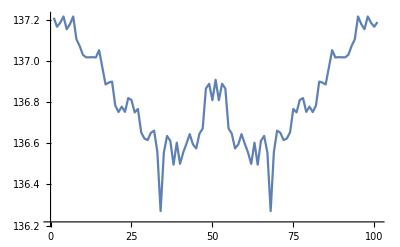

```mathematica
ListPlot[%63[[;;,2,1]]/.ϵ->1,Joined->True]
```

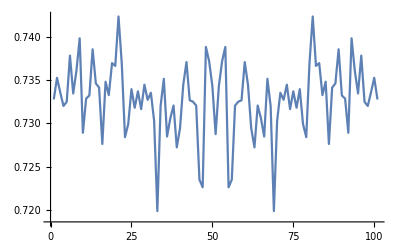

```mathematica
ListPlot[%63[[;;,2,5]]/.ϵ->1,Joined->True]
```

```mathematica
ParallelTable[{LR[[i]],allnIntEFT[intexpand/.θLR->LR[[i]],{-2,0},{-4,0}]},{i,1,Length@LR}]
```

```mathematica
LR=Table[n/2000 π,{n,0,1000}];
```

```mathematica
ParallelTable[{LR[[i]],allnIntEFT[intexpand/.θLR->LR[[i]],{-2,0},{-4,0}]},{i,1,Length@LR}]
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000582272620807849388582401804244606061797116367742834353262000936705414267674563537 and 0.00001621584751157070016963436159847946874983704183342235113046994113792310985993852807 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005800543529139290347900990850494144811029186738577975141059132310551759539747506568 and 0.00001189848464331351666179154233628051795212056077984816847613875089623188397095425723 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005799219904517382594326144432283342455509075732294430372060779506356874840495476766 and 0.00001677332082527647816819059554617326644758693983879529832625278718209790963432892081 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005769849596233919942735002050563235989476301330985668713906585156327784236147216814 and 0.00001684747646720303090011283494534362506863571292556738692519902484198037124255433109 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000584158481623368268491607880172489867245998391210782794203103461905273568646307467 and 0.00001647662714966129100239946399376876438629828485801440333369494920615886452932449731 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005879357667849754843898804914223048365304484018979367426362034734330484429273998552 and 0.00001593145033186270953850988969951685581270930459877274162409023836315972105681982662 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005797073921305755934665729829316987228312173842055828183512080303091863051865875285 and 0.0000126019440047698787758878439122848930322989209403607616452687362074482628657032568 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005799427202157085457093053982611142711278651116497257304744717760448502213352065286 and 0.00001342094016456297420555104795909521680728127333139637303534112190783161218425667604 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005794181592337166691090590437821993137506368029724912824271651757261631455619654822 and 0.00001189284523340402547077848970187502220599372191077598573933287559824223631752837638 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005749841470198490430400664373406678456259486623387088640855590651439513936760124353 and 0.00001246484238066014184295864403968423955236436397661131335344515734055562098211775434 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000578670005713310560377220331378054731272382718553050253314058895612447538750357943 and 0.00001393755210895955789407335879819522596202977972511347612989196527960539722501552746 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000578984438912623570945486986787044835960683230313090000575185501563904211849879352 and 0.00001054117942127056240927613350713021748408281701312656813872853589412019722919748241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005806246400707745966784990684073005466743910272980503095167816763776438013640817742 and 0.0000108043022919113792567217796511316702383454656289150332641058554957719685306249527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005800429180415155049349467375952584919412034021855785118808239429285724053527282319 and 0.00001091519401372442479318230220204575267910631168036115320674538008893043403049320285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005809134490310543037431795175980888681759557670448014577487330714684616831917927079 and 0.00001278068737329004681948394614767190870151793539492928069942168313361807017598712302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005828689715195335992411692870064379565842844139029149093646786296706164753214443265 and 0.00001210330175168090294794352282269111483475556678708159302853667481092934029557623998 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005777863380766141775375966195831169131739473701721037206030144707270669963480117971 and 0.00001149894552876304378737324353344073724969888375077323976434815059898383506116978082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000579026566418716195566620858011141217846024286987899704976231648440553694960671121 and 0.00001737182299512896021925008735365191311062752777841848965272187967604116992139284477 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005822007012689264841276559769577597184177055325922732947705353815437024659182429747 and 0.0000136138396664717577876779790890427254353198142611338682626525622162376756419672145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005774628682541945688023878212206819020822593650868946298735520142989314389770068394 and 0.00001301161390235222678792026115253026422871353709815071484354211216096215820897789866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005833943608286297871475836221008524981362219542264969696442665108665434026320898913 and 0.00002124499714323267582648366720001633047800896226564088848108515644451668548995784251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005822092170335084706909465177740374928139099582902612589728987661793380654217539016 and 0.00002112106252083929535252215943296799850103604284489392453426140791733398077638095637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005814691781581760293184865394068707615179874662185159420637181463052231113597412909 and 0.00001836093829362199245794390284206106898895803810789063340733115974267339537296509728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005775799656629084720393272345250661798175989052466939094397826689330830435692530735 and 0.00001273524300892330013239448000674654576276166932163680518712318967155298271523185807 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005817392649255483487740057893926132920431337448250542619193171415150580687964431024 and 0.00001465583035127386978415445127965743073766459327537755958083729832793551366242927778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005797089987462898167983753524644107293594569241843987815665016280826516679905433115 and 0.00001433453962374995857288289984618888198500560872322786399848633432864721301556201815 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005689582623647143241146243028106083903821810190861322228603083361119493081030705666 and 0.00001524336377768903472182837346588452743275869786335492914815132125091952747560847501 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005781354335934625556775457027294351540304639954738096847214805582283008667105247874 and 0.00002147666514335740010115351423098332978356933155119988821738042388858984088801919292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000577987920043805783063784256114783815852848313392129916511081379154756500056919979 and 0.00001671823037945447639865894391623958270558364961837251151155217362597456348691077419 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005796277126206967174506738054520848880813554182305916959900310688505273295210812196 and 0.00001453085395246110126330442591394412029964247163424674038178864629481342673922878649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005791682002671764888218426025464139395424996663422327739922807419870475968165844375 and 0.00001457886623534311304577844032245212890578658354828907695538682715492564560289314787 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005793798059500788131036785093469368658138090895878940824822007483243309094535694109 and 0.00001474662902312971387017882881905377777507865850195735628033098356801102385097133631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005754503035447417281993182624133791464748172735913666083421093201177437445677502748 and 0.00001549239778463023345167463883732488094621175169080408518366771978925157754263316939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005807251701444339219028016164761241749786911699691040649918160762588075519364589427 and 0.00001517381789573332072642887738324831152110316243536374046220739417381718058165007551 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005794041268004252147561423670912356122328785685525153786306034291519131052571365043 and 0.00001462423261717783031234857532984368490921794495293386032356832979449228387031200133 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005792166977159363235142478899470112177036927824067885949927356600214754914898858561 and 0.00001710844231023815983484403081554444491362366365654300053258456145448510915652569357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005805428164704091252833451029427145398517580161380578447248094409410442114450551412 and 0.00001421217046291206722800599390670268108375626888404882984530303828366915967777853747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005782824495567169113006146922394787109398641203031451876920722746209499493238699941 and 0.00001608225491767226097570649976383484008866911384566669720591517093394042244354544642 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005793166533677517580956369695503693318477043512559524196239563098877379992567400138 and 0.00001587331538136772227825577685500284410725328561240425855610628955383635858748003989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005787644604500881671445289321908076120844322885815568688061324313980518229596394081 and 0.00001605878126560376460546631988076869129919191167136256556924932523421289442891559696 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005783181952566929998015060332311703234832063762902464211669185766430386150588778119 and 0.00001127361161922921381366766263409742517141553055414732135720434573627768755033116534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000579137363449108239351427154891535241576288170045640108827966906094782360408784073 and 0.00001372784984238630013375355122338591905491256672263335421182079733211848553945434128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000579828689263693853817985997966292327189370076150015766392796786527306693781707227 and 0.00001387048163975488071176192002477442975554219184535004862537560317897869117635111399 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005785875255419731711328244603044631476193034977777439745998803843390962992801783996 and 0.00001675135660725717548735221442710972035277905724860693046479756752401597097020119351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005805888358213087059243874001502755777416856102766843498074975394432089202816087624 and 0.00001570255927336512517055718420799610884409553713918696430341794573976324285077557353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005860129883996906790259787779271538392293924017055657877062051721453566449589148572 and 0.00001452106367585613714347866597058391278419542526003225490590457946219485052954813434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005809903982697916879854710156613609497596756798813135218506281951102244628326888932 and 0.00001824355190764695258847766768719338399785704227367633980240143649356229884912751885 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005834734985165634415409845085497260162522618106124236253059532527594894090867303917 and 0.00001818720443529084495283857020875366934336459139488113833155519475882701027006080858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005785105891956890224798083615570312792759556067082988031842457542620107291989073791 and 0.00001754611176573232137547420901541651863846991811477686938386975790818957359611336407 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005797492625490788325274136749526627308341923215431448820747420079356987587006358175 and 0.00001784532033472021051127850444799753048552531340405151059174999090274295288481238677 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005794639530032514361740162382233603905858817510044342291874359536657629687488933442 and 0.00001978913957405629870128906337289448953711194822061637453612679323900903409445052217 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005794050993041701490255633782023820783742708723604800303780746700035065375577779002 and 0.00001456000982498979684072080574435319724432088000093124368306410502089876618719163952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005832190263598873981301763548045761362223539383118138729756289901442851924744038497 and 0.00001494745877962575211529122045084211607296614990079756121394454762368851320598626211 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005858460822337400268547227477069299680735669438904945583934871773965339777874742671 and 0.00001064062778450777113826663474480744720674876199512512640704189491374092038903578586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005849775762019720719844963136857312372434674730888486798040768525133365320260239802 and 0.00001361812626163553130909616574172115027882545151248365556113404238059715963896127971 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002638516127529209247515918887089486136837552549530340532638232678338653304611495303 and 1.47100640360895840786847298260356366423078572550913900563157286750525964608686805×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005828849476892851597912096935746906346477357552411026772814304848896581990013714523 and 0.00001254074499014168105473661829588334513474403801747653945749479178299661929091903065 for the integral and error estimates.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0005277032255058418495031837774178972273675105099060681065276465315036284802194126277 and 2.942012807217916815736945965207127328461571451018278011261340445760485689731946086×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

{{0,{0.00026385161275292092475159188870895/ϵ^2,0.00058005435291392903479009908504941/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052069997799398342708851948759765,0.0011601087058278580695801981700988 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005801503425296897498973527927269/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052213739858766606287132823407058,0.0011603006850593794997947055854538 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057964048338651881509803958626445/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052033581167305609459526422664065,0.0011592809667730376301960791725289 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057993877926769833600058827837142/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052601957161610336239787660649255,0.0011598775585353966720011765567428 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057903203936366351182738861275684/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052098597619183628459195030536668,0.0011580640787273270236547772255137 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057901654655113430528253712885353/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052508906489459953576962925462082,0.0011580330931022686105650742577071 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057870324797321283980847922253015/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052226468810286216833950528118978,0.0011574064959464256796169584450603 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057836143658584108078848046726664/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00048843533947873245758765460674604,0.0011567228731716821615769609345333 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/250,{0.00026385161275292092475159188870895/ϵ^2,0.000579008998465276267259996941016/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052437369330769025196926242658475,0.001158017996930552534519993882032 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.000579431181197567202692077735715/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052174903580724758857779641813862,0.00115886236239513440538415547143 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058020984398954685195443539772829/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052423747360679297460279808863908,0.0011604196879790937039088707954566 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057943412272624052128773338053346/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005363021188468709965332903014092,0.0011588682454524810425754667610669 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057993058100841021591596545107995/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052543562881664280753713828531783,0.0011598611620168204318319309021599 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057792431033667371208560825880941/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00048062126105021714385034901576284,0.0011558486206733474241712165176188 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057919198742863560929782123712062/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052902743044326764594753920152295,0.0011583839748572712185956424742412 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058002934004963654833369298533486/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053060812317287446770041712077448,0.0011600586800992730966673859706697 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057976845555520241380253648053961/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054312463487068744442649278310013,0.0011595369111104048276050729610792 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057938091835007136870018452280762/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052302646474598829775259732562357,0.0011587618367001427374003690456152 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057867000571331056037722033137805/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053243769481374558670404409343474,0.0011573400114266211207544406627561 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057937867250666476554457676783407/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051365692253553313503110131417395,0.0011587573450133295310891535356681 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/100,{0.00026385161275292092475159188870895/ϵ^2,0.0005820414429107511716288779155055/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055550088568794397987448157513818,0.001164082885821502343257755831011 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058284181514973451921608827006345/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053541542631002415122779791775084,0.0011656836302994690384321765401269 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058101031006645383702238218682357/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052771153484683003639884306989331,0.0011620206201329076740447643736471 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058032552984481448015262182268415/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053327213650294516460996481014417,0.0011606510596896289603052436453683 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057904786974823846343412648579687/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052829070755723983572813181838357,0.0011580957394964769268682529715937 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058037413464133489110546886152223/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054996709636680027468399728548803,0.0011607482692826697822109377230445 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057906155126238294240822524123264/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053885048792321313582659311146319,0.0011581231025247658848164504824653 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057858391078834049532763826341335/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053303685686068168671735450661902,0.0011571678215766809906552765268267 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058025410308042019496440497293924/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054242304310497234582993173750745,0.0011605082061608403899288099458785 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058072717225879960843598539147187/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053095322507145873489168794275788,0.0011614543445175992168719707829437 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057963899071404219688808123605863/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.000506939542767261730379686971271,0.0011592779814280843937761624721173 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058060260604448579771536178035725/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.000508811014140807416201042802884,0.0011612052120889715954307235607145 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(2 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058067525157457108952164519932584/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00049137385849912797085333114172402,0.0011613505031491421790432903986517 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058029367365715447515239529780777/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005003673762513022655212051874419,0.0011605873473143089503047905956155 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057937483890217239329258529918605/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00050773297065147509827941509939418,0.0011587496778043447865851705983721 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058008358491460622477218560106011/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00050696194672219487920935648083577,0.0011601671698292124495443712021202 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058004291804151550493494673759526/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00046082133118201387614567748831596,0.0011600858360830310098698934751905 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057993991155576611015340770445753/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00049656659661121628527488070497098,0.0011598798231115322203068154089151 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057821664274400997728698225159401/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052149521044815880425728821802348,0.001156433285488019954573964503188 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057741701648404894231161001595116/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053030477405104201958958148519793,0.0011548340329680978846232200319023 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058070326535181401936271877896929/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053997695400116780909590364285053,0.0011614065307036280387254375579386 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058066185968678040614419492916322/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052280259441580077918778267033596,0.0011613237193735608122883898583264 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058153026052652925648202722683201/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051875195979288269965994947091464,0.001163060521053058512964054453664 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058162924810529719386760161998943/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054638977917523274277415659377121,0.0011632584962105943877352032399789 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058201254421228210945896372107742/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054589901232093496111463316409173,0.0011640250884245642189179274421548 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058314390570593748131956987738691/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053317657503962312399785052738379,0.0011662878114118749626391397547738 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058027399322936975834759418182828/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054259915708883324346061025688214,0.0011605479864587395166951883636566 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057942083802027791268424100472674/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052148376953420669949683400495842,0.0011588416760405558253684820094535 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058103302489237549072552644804589/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00049482690365446629356191008886302,0.0011620660497847509814510528960918 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057628794427049189477781762261901/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052562833233827341036926591674133,0.001152575888540983789555635245238 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/40,{0.00026385161275292092475159188870895/ϵ^2,0.00057847598717144552861143678134832/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051425524462884572066714254853436,0.0011569519743428910572228735626966 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057864886085248141337558615474773/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052824619057572260129362164316889,0.0011572977217049628267511723094955 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057702972444535559071300481158306/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051921528468697652598706134526643,0.0011540594488907111814260096231661 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057998603726353186311153723925254/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052357587050453105142598986560172,0.0011599720745270637262230744785051 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005806246400707745966784990684073/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053098658330391267082007716879208,0.0011612492801415491933569981368146 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057956114076083797144006807756462/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051821439434399457125508632593851,0.0011591222815216759428801361551292 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058080927459576074081857029327146/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052004599158425060350231348261068,0.0011616185491915214816371405865429 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005805902668818428285821539516212/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051792344062342237597254998842219,0.0011611805337636856571643079032424 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058081990691649034429188796767356/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052339954722556315145209390021467,0.0011616398138329806885837759353471 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057948725285821752148882676461213/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00050028316281614941294921962237424,0.0011589745057164350429776535292243 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057945585258024220062438217251246/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051594315248568396207881657487345,0.0011589117051604844012487643450249 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057993314883589267470377542974622/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005268773264294575610399253391228,0.0011598662976717853494075508594924 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057988647070963943768320422572833/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053641837569424919469178689090907,0.0011597729414192788753664084514567 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057918514509191394002980346398246/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052827709635775619516441746627666,0.0011583702901838278800596069279649 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(4 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057896836679320853924856957403822/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005380676665493619222852593823732,0.0011579367335864170784971391480764 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057763941156619747853676797268753/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005467364716246246125876377722826,0.0011552788231323949570735359453751 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057616597310243038763474733065621/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054795511963175108702579570834232,0.0011523319462048607752694946613124 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057942358779192269170606768506921/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051962044950389968998636891025397,0.0011588471755838453834121353701384 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057961946259016794269444038385797/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054515231126677575974621205756399,0.0011592389251803358853888807677159 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058028544906007795659302119870753/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005613062490168051570061617083986,0.0011605708981201559131860423974151 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058000465597030373208856410952063/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00045552205775427070130749487658296,0.0011600093119406074641771282190413 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057974306977925515301944724536944/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053322687621110291004409829820117,0.0011594861395585103060388944907389 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057898443891262357094548698678704/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053634865332206015165783457896788,0.0011579688778252471418909739735741 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057936755358510728419093971933098/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054842133891138800226545385802052,0.001158735107170214568381879438662 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057985144236964827447439693879733/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054742981558845794737158824565908,0.0011597028847392965489487938775947 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058084208568493366553219783087093/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053822783126420745050403943282301,0.0011616841713698673310643956617419 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058008649881043846765062333719473/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054840786745628481315200357191083,0.0011601729976208769353012466743895 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(77 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058020382448214219186569372373639/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056666414830085975836326601427588,0.0011604076489642843837313874474728 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057941725373566281942799346981307/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055127129851327550334931612876181,0.0011588345074713256388559869396261 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(79 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057922808881166958309211519588309/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055563734598137738745442106234734,0.0011584561776233391661842303917662 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/25,{0.00026385161275292092475159188870895/ϵ^2,0.0005798385202200708340946715344772/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056514014655365725934022138831435,0.0011596770404401416681893430689544 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(81 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058065489741029068595259362398082/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00057062522956331383141326751317865,0.0011613097948205813719051872479616 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058127462290097988631984114682805/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00057351179337143530120553232526373,0.0011625492458019597726396822936561 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(83 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058148458288098480632320938619623/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056258177444532425958647174951772,0.0011629691657619696126464187723925 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057956300570182625392373162042844/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056508086084598822176460683606908,0.0011591260114036525078474632408569 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058016330000040502996628167435177/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055671738181372560996737740456619,0.0011603266000008100599325633487035 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058095023362118199224377422465289/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054902240321396070803733832475243,0.0011619004672423639844875484493058 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(87 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057751014174184401613497522653946/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055104911402572334276756650567113,0.0011550202834836880322699504530789 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057741102492115587963170993181508/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055811164712698683492731004270084,0.0011548220498423117592634198636302 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(89 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057843107232628683960179238519953/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055119887686025971917320097053673,0.0011568621446525736792035847703991 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057498414701984904304006643734067/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005386938884890470094051239495863,0.0011499682940396980860801328746813 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(91 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057908999805311934449090096581865/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054546033464843839748059564741725,0.0011581799961062386889818019316373 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057881740902377920955642354927138/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005442329661644831276238180517038,0.0011576348180475584191128470985428 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(93 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058417893486801454940100331633911/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055939856125483824673626831360312,0.0011683578697360290988020066326782 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058280484050224981802582448360589/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055566045592070421709922587078272,0.0011656096810044996360516489672118 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058193007102964052010986687694596/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056039044439600080812028333447658,0.0011638601420592810402197337538919 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(6 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.0005802602238053727007309070116958/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00057198220091606151929704475367712,0.0011605204476107454014618140233916 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(97 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057996126222913472942097853064563/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00056725693354719037448824338989892,0.0011599225244582694588419570612913 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057851502171662069148562204733424/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054701833738004600521974758383923,0.0011570300434332413829712440946685 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(99 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00059065347512772282429583749454129/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053148141044982569910963050949723,0.0011813069502554456485916749890826 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/20,{0.00026385161275292092475159188870895/ϵ^2,0.00058408629045520075897121765764746/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054547414630572672237488318574384,0.0011681725809104015179424353152949 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(101 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058387431841539932960715189168136/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053665919516936685978123457786006,0.0011677486368307986592143037833627 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058362604656950086989070416861779/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005330947598622205713717905983649,0.0011672520931390017397814083372356 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(103 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058305283528760768085388036750205/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053933334653073395629492102392967,0.0011661056705752153617077607350041 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058375961142200392658644635053564/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053087102395002523336632546576244,0.0011675192228440078531728927010713 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058960671735621863835822875739965/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055035095457885810459254309023451,0.0011792134347124372767164575147993 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058349237978139173197259945802876/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054388836619978586147557011831766,0.0011669847595627834639451989160575 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(107 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058935894162582956780998989887587/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054983060416133813779885868837928,0.0011787178832516591356199797977517 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.0005879357667849754843898804914223/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005313839027889106592053509821348,0.0011758715335699509687797609828446 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(109 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058117188556105116634996614478177/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055441753973582275431282794871495,0.0011623437711221023326999322895635 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058828846609267434452221400636623/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051754096537245193918181145738014,0.0011765769321853486890444280127325 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(111 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058292936768459427355635658040251/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052420493279071266609166848211081,0.001165858735369188547112713160805 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.0005853885587223457606202417300839/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.000537405206287741146939866190603,0.0011707771174446915212404834601678 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(113 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058295482237317524543800780735663/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005103247499065187737178207469907,0.0011659096447463504908760156147133 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058563675342121955038114686998491/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051582182529844218053029306313029,0.0011712735068424391007622937399698 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058585990306155580821925128775297/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00053852626957366127847874669629161,0.0011717198061231116164385025755059 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058502812891334026352167143330401/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052338633174931844538146052494065,0.001170056257826680527043342866608 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(117 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058651931665995404309625214315615/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0005259872898351271911126147960641,0.0011730386333199080861925042863123 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005839734187146337576681544460794/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054493777380939018242284939707209,0.0011679468374292675153363088921588 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(119 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058094119869805292793449894056872/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00052810376332010838638555747742973,0.0011618823973961058558689978811374 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058060404774842695700631591931255/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00051590539833149049197396476873129,0.0011612080954968539140126318386251 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(121 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057771726206135681740342052545334/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00049879352151874143080960031886293,0.0011554345241227136348068410509067 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058193205133279537566183372282066/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.000533929108853524628168320907489,0.0011638641026655907513236674456413 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(123 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005810564546378707752716128843241/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00050851039070797898995655498483682,0.0011621129092757415505432257686482 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058208136590370230420738834573783/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00055475943392455641399269476797481,0.0011641627318074046084147766914757 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/16,{0.00026385161275292092475159188870895/ϵ^2,0.0005816636379252069516455380073531/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060944750123367012844343956344428,0.0011633272758504139032910760147062 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005794181592337166691090590437822/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061360599678483537992810814033224,0.0011588363184674333382181180875644 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(127 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057896400835587673938862724691625/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054025644687365389832767188767494,0.0011579280167117534787772544938325 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(8 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057991514411139892069049150164966/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00059545829304015784051552442193259,0.0011598302882227978413809830032993 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(129 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058369553800841747017737370591728/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058178407168194381053593414410899,0.0011673910760168349403547474118346 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058229005967744403104563168900698/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00054973757990325759950911054126021,0.001164580119354888062091263378014 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(131 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005798348489760310469732657357264/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058305526966404849602126346469135,0.0011596696979520620939465314714528 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058025996220302915391618386126889/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058396763381703188595639050817682,0.0011605199244060583078323677225378 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(133 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005798133214072791833407271893688/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00057336634734810868615435213955166,0.0011596266428145583666814543787376 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057966412497112145739927990333843/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00059332677022813479593779527456814,0.0011593282499422429147985598066769 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057929754821907627104609896654368/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061712713954424463192747238309996,0.0011585950964381525420921979330874 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057908652253556406594499740254451/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00057677647900921215769649262051108,0.001158173045071128131889994805089 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(137 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057871729937270520738029321702645/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062466031257026218431912695041887,0.0011574345987454104147605864340529 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058088306835087574710903650003791/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058957053053514815845462058370746,0.0011617661367017514942180730000758 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(139 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058225082952452647902100224585294/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060707389262873880740231076929567,0.0011645016590490529580420044917059 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058268965910582708285038780845926/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060381054058267691325162132198872,0.0011653793182116541657007756169185 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(141 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058255773894131218367294812133092/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00059446289679997380424624197078631,0.0011651154778826243673458962426618 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058238316213463684546144420759765/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061773418322136380941951482792943,0.0011647663242692736909228884151953 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(143 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058298242076183100641122499692222/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00059220347278249829717103118197862,0.0011659648415236620128224499938444 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058227262080784938858240180424461/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061441539110941943068475162971367,0.0011645452416156987771648036084892 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057611405161293957209527030917798/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061286643681494641239910950535796,0.001152228103225879144190540618356 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057809024272852614566520479995509/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061701133140657001708690129956461,0.0011561804854570522913304095999102 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(147 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058470013220423767770999986329747/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061027178499811921871075309125381,0.0011694002644084753554199997265949 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058448266798993193760723715055459/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062250136439487886673400033591393,0.0011689653359798638752144743011092 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(149 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058492334054393393383261713702407/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063073034039536104438563995733912,0.0011698466810878678676652342740481 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/40,{0.00026385161275292092475159188870895/ϵ^2,0.00058681371520238667924648473319385/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062765477608863464533851003380067,0.0011736274304047733584929694663877 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(151 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005847730662253886711771908263773/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060930532122251696639355212647975,0.0011695461324507773423543816527546 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058305358200814660648214546120603/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060203213045604771783810228637153,0.0011661071640162932129642909224121 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(153 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058249995488549029379352030906857/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060935873242576692309365865925235,0.0011649999097709805875870406181371 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(77 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058522483375713140839085729942095/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060523457825262670037222172549549,0.0011704496675142628167817145988419 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058291330308802389667203064007637/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00059369367474647895822680693553441,0.0011658266061760477933440612801527 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058341287903323507418489983238141/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058683926112444588338161694379349,0.0011668257580664701483697996647628 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(157 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058392403791916611142645343133016/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058498420436348188454766467051665,0.0011678480758383322228529068626603 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(79 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058271225857470944590097596708776/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062623812122717629448948848596117,0.0011654245171494188918019519341755 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(159 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005797915269882808631146565382574/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061644203619092465693106976366407,0.0011595830539765617262293130765148 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(2 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058567748646439621602173520877888/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062977103386030331424953888244995,0.0011713549729287924320434704175578 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(161 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058623834471568745202190958985297/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062066593076024082242316242955586,0.0011724766894313749040438191797059 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(81 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058415848162336826849160788017249/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062226776557591420914181627664217,0.001168316963246736536983215760345 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(163 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057857458414805016025245288457216/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063257798395899600159523359629397,0.0011571491682961003205049057691443 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058704260070255852352841334596495/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061856461566691878745088696705488,0.0011740852014051170470568266919299 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058508512245202985106538291538072/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062665157204978044071672779959178,0.0011701702449040597021307658307614 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(83 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058624347297163684628930186184934/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006250557347766341378431544751868,0.0011724869459432736925786037236987 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(167 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058486055762276327011136856158078/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064811276904982819540701409206392,0.0011697211152455265402227371231616 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.0005823055517452442487513793119807/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064927577951221269059441774550324,0.0011646111034904884975027586239614 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(169 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058343479343745074707127614750232/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063429995596549521211915504303952,0.0011668695868749014941425522950046 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058705569673903107331706736232793/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064573407966150409140461848386488,0.0011741113934780621466341347246559 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(171 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058489459897645056992895006677213/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00058711148821134334918574818526008,0.0011697891979529011398579001335443 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057954154768576866391589847195698/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065098781454094356338554211366643,0.001159083095371537327831796943914 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(173 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058198004613055564926174100176108/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064252165677714605363782244445361,0.0011639600922611112985234820035222 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(87 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057742891930367632532603051371783/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064402471912467527386272963597267,0.0011548578386073526506520610274357 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.0005778494972790707574897434552166/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064341406755676297636401382711494,0.0011556989945581415149794869104332 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057936468365758485185263048274612/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060747545076924087407946705042804,0.0011587293673151697037052609654922 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(177 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057838299618853763692416608123643/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063683209606804740375829870009301,0.0011567659923770752738483321624729 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(89 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058334319255676155737479501995752/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064061405970927971240770867938596,0.001166686385113523114749590039915 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(179 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058083528240148736708548954530099/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067221194091429098304725304116172,0.001161670564802974734170979090602 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057698495962339199427350020505632/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066388612087901181411336438560777,0.0011539699192467839885470004101126 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(181 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057878017975017712492705439246173/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065766570138819877780309866678056,0.0011575603595003542498541087849235 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(91 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058001822415076710219109199953816/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064579292556602696096124764410975,0.0011600364483015342043821839990763 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(183 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057930882415572560942238403042818/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066582250258061824504188554493864,0.0011586176483114512188447680608564 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057783680572742072846908145348912/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062459424531806177102602110446004,0.0011556736114548414569381629069782 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057821660189966742326945082352614/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064465160610378758298001323542202,0.0011564332037993348465389016470523 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(93 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057941919792511823787166354396676/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065402638682687846993906007101922,0.0011588383958502364757433270879335 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(187 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005784116278346264513381245943328/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006546413263245224542947597879712,0.0011568232556692529026762491886656 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057824243416409218209300713813608/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006434524175985839475758771276575,0.0011564848683281843641860142762722 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(189 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057440615153394801975515999243592/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063128377650232603255024719374855,0.0011488123030678960395103199848718 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057988958449677378741742966704956/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063362943306794381959197594499478,0.0011597791689935475748348593340991 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(191 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005767669416315741461545825067524/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00063900633971587449766876872506741,0.0011535338832631482923091650135048 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(12 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057670412006657706657088648630322/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006616446988408143783944124620146,0.0011534082401331541331417729726064 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(193 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057753800320749593077467811284514/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065734298567677910408278931765996,0.0011550760064149918615493562256903 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(97 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005787920151972321543970840048814/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064166121602302729466288658124345,0.0011575840303944643087941680097628 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057937528849767622776986822851135/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065101221970210649665270532527901,0.0011587505769953524555397364570227 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.0005788061661100220312649282286635/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064787385938124943037611915449508,0.001157612332220044062529856457327 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(197 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058004604445827718901944672956946/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064156042616868853695822338298121,0.0011600920889165543780388934591389 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(99 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005797073921305755934665729829317/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006493983636300993017797841243313,0.0011594147842611511869331459658634 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(199 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005794651557159699958066194809827/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066726851950440204765430942028162,0.0011589303114319399916132389619654 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/10,{0.00026385161275292092475159188870895/ϵ^2,0.00058013485302661245953739363215024/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067349121501269688470421415692621,0.0011602697060532249190747872643005 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(201 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058114179989054466006185419867688/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067476069000768356053407790383083,0.0011622835997810893201237083973538 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(101 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058295304938683633908710703720087/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065224387537611998420594244659434,0.0011659060987736726781742140744017 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(203 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058270100441983251556445414971579/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067506529753029738743409410926689,0.0011654020088396650311289082994316 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057831664446335712416058908362646/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066887391192238026516134927207542,0.0011566332889267142483211781672529 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057999541296701845914276775775382/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006687419605644874374846357887541,0.0011599908259340369182855355155076 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(103 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058080169794726174041144939234971/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006727864164798657035937191200413,0.0011616033958945234808228987846994 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(207 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058105145989424516120534635748589/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006639843873420644436576977367696,0.0011621029197884903224106927149718 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.0005787558349336552581895226736833/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0014790486381042830351328145367111,0.0011575116698673105163790453473666 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(209 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058199893821460034561338097798176/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067211474695139246363558873494566,0.0011639978764292006912267619559635 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058171654320020959563009056512502/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067070042197936153390424283997097,0.00116343308640041919126018113025 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(211 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058142461290767838081220302117942/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066616650170149937454099056179248,0.0011628492258153567616244060423588 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058178792340264264263853532560993/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00060528114333922927190111585342263,0.0011635758468052852852770706512199 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(213 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058087469423934152217622487048023/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064361024719575351624227217517953,0.0011617493884786830443524497409605 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(107 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057987923038966081356870567970601/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062195094571866050448406926043619,0.001159758460779321627137411359412 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057953235353136951632989375530839/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061338634786046279316823005971734,0.0011590647070627390326597875106168 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057994272021570854570930539826111/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00061090732056072285654506665377872,0.0011598854404314170914186107965222 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(217 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057794273062000914092278772254983/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067859111193702676759564477125643,0.0011558854612400182818455754450997 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(109 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057678444867483508854841524800688/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064962055011765264176496931930387,0.0011535688973496701770968304960138 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(219 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058067635724718902869777916353259/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069925850715915602889356270005038,0.0011613527144943780573955583270652 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058041952589457045061549076566331/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067328172637379016721901059463809,0.0011608390517891409012309815313266 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(221 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005794039934378516274140233491042/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006945429060738490719245733977219,0.0011588079868757032548280466982084 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(111 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057882984803214463710692180073516/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070464834890657883578211577699186,0.0011576596960642892742138436014703 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(223 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057982312111711317557809770542892/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068533807771447971691951792473606,0.0011596462422342263511561954108578 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(14 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057953768815213591073489766821667/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068582335512073889805311157728325,0.0011590753763042718214697953364333 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00057934960888607144921898424693704/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069211903401320579272425608802975,0.0011586992177721428984379684938741 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(113 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057997146399990849173725916076875/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070503704497216303326788212882398,0.0011599429279998169834745183215375 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(227 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058125763682958023015654059291338/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071964203209026517224566178171628,0.0011625152736591604603130811858268 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057881959369202616219050579963133/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069486101972008253396190756063419,0.0011576391873840523243810115992627 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(229 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057871457397256283616396372454048/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066808944296566116434341319950261,0.001157429147945125672327927449081 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057926077343882198455700210905067/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074021418407565219139016872644118,0.0011585215468776439691140042181013 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(231 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057850975964235641581886824626031/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069175097428436810631925695873898,0.0011570195192847128316377364925206 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.0005797623649155432187765206310443/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065731592770096062972453915218531,0.0011595247298310864375530412620886 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(233 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057901148969213828356318019843714/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064139769097649762454381794097199,0.0011580229793842765671263603968743 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(117 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057992199045173825943261444322833/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065102722716277231904454716704722,0.0011598439809034765188652288864567 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058017756097416325299927750568792/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00073724947099901243123287380231722,0.0011603551219483265059985550113758 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058406012814632230133687382861492/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065858649275158323328383410368173,0.0011681202562926446026737476572298 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(237 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058005107793683566025747543437311/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065059937148799775674200732429267,0.0011601021558736713205149508687462 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(119 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058082830977490559983097253641287/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062585979842431882301551672201109,0.0011616566195498111996619450728257 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(239 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058261167136346275419230101949414/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065162180912298021431219718165435,0.0011652233427269255083846020389883 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058466683151935001613305565359054/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067276007038042205469916320494038,0.0011693336630387000322661113071811 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(241 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058468283256528458367263227376188/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069224268647574522369600771179703,0.0011693656651305691673452645475238 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(121 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058105720522146484441109571817915/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064023962490166776658161385379955,0.0011621144104429296888221914363583 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(243 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058387959259410623442053976786313/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065654176677976489489886003693573,0.0011677591851882124688410795357263 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058576931991279240739824978709101/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006484861333239413297956103274038,0.001171538639825584814796499574182 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058491245813994301880621886297403/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064132188028656582484303906359674,0.0011698249162798860376124377259481 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(123 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058335047939043088079496282382608/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062180727260802384771816539752985,0.0011667009587808617615899256476522 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(247 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058127755458921426343055974675167/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062727272430697505350858261941124,0.0011625551091784285268611194935033 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058140085937902858259581269215303/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064079962876920177526334097384606,0.0011628017187580571651916253843061 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(249 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058140558532438480750853506474153/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067446817916363662572274440503381,0.0011628111706487696150170701294831 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/8,{0.00026385161275292092475159188870895/ϵ^2,0.00058036322312514123289228301383384/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068997348568120757773648872403843,0.0011607264462502824657845660276677 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(251 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058008311610794824530209274890706/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068232927523508262112891450960701,0.0011601662322158964906041854978141 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058091344903105430374317951759809/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075993368028600783397985780759755,0.0011618268980621086074863590351962 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(253 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058179591512643440212231191967191/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068147942347338424207276118844577,0.0011635918302528688042446238393438 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(127 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057959593294322319717674949893257/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066780641442439438983062475252028,0.0011591918658864463943534989978651 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058219474501446237852647622551057/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006591959659255308802841172952952,0.0011643894900289247570529524510211 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(16 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058145929086526101263324111920352/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065567206405538763892667314437117,0.001162918581730522025266482238407 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(257 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058288378787067134373160642910791/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066895197526568191051112338620821,0.0011657675757413426874632128582158 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(129 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058657451586490099839207909515608/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066775549650261563076430321268883,0.0011731490317298019967841581903122 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(259 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058152011558725021893778140508762/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065076831706561402629666369791599,0.0011630402311745004378755628101752 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058152255306257775925098412230322/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067388123107705915009712399142039,0.0011630451061251555185019682446064 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(261 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058200586028476542355902372098758/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067102658383343095817822479504972,0.0011640117205695308471180474419752 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(131 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058223806492136489177157766550696/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064230571318346430075256936218404,0.0011644761298427297835431553310139 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(263 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005822125241431471704494322225108/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065523946771403557626477781208454,0.0011644250482862943408988644450216 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057624670306909765239806747736268/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006577794218023794945892652638153,0.0011524934061381953047961349547254 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058724396778634909255289852612618/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066796397193492733470287822614027,0.0011744879355726981851057970522524 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(133 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058335878324181366054572477345999/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066956089323196994406773636438319,0.00116671756648362732109144954692 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(267 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058255437629399364810757733298747/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067133345612285834731982327722134,0.0011651087525879872962151546659749 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058372656085558415451954455261659/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067361668276978765926390317037651,0.0011674531217111683090390891052332 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(269 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058502938379990651900870831777925/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066207893725821037091926452588294,0.0011700587675998130380174166355585 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058286897151953359924116928700644/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065807333089132788397969100401478,0.0011657379430390671984823385740129 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(271 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058282598023492182916967511918431/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064311678873743279465689291029313,0.0011656519604698436583393502383686 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058323191108442376309676693636083/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065942771332946241960911787646343,0.0011664638221688475261935338727217 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(273 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058194768372525504307378905801895/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00065455981554084124685291307273629,0.0011638953674505100861475781160379 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(137 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058273991080656080122919056576709/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067619175903665212328075998645377,0.0011654798216131216024583811315342 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058306228515739691841143647942561/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006399929583200307604666065110316,0.0011661245703147938368228729588512 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058298660829996510560810285980715/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068276667087554891924767011045802,0.0011659732165999302112162057196143 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(277 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058196634107028203636564227963701/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067921817825809772345684188664843,0.001163932682140564072731284559274 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(139 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005802975105667892797624610807384/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067256817699136958124885902875534,0.0011605950211335785595249221614768 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(279 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058077984690757439635775097527133/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00062426394201072377422117560310945,0.0011615596938151487927155019505427 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058114403813233060583706724521848/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006457471182270016416990733645247,0.001162288076264661211674134490437 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(281 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057973025554390891596468948882397/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006341749426420351710542612287478,0.0011594605110878178319293789776479 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(141 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057760778051135955534571257126109/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070378917234447254242867283255119,0.0011552155610227191106914251425222 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(283 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057685133796226777171429691076916/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067024592747384094874478104378412,0.0011537026759245355434285938215383 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057576591727300980807571220207111/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00067271855380971633842166901678791,0.0011515318345460196161514244041422 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057564244012032140894054476377456/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098493247012297478729179476355555,0.0011512848802406428178810895275491 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(143 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057669933351366025782983299418942/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010311049911896250470926143673608,0.0011533986670273205156596659883788 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(287 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005797006194408014218837636771455/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097727636986078122560518958284007,0.001159401238881602843767527354291 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(18 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057778633807661417753759661958312/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008264601540297588469273089084485,0.0011555726761532283550751932391662 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(289 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057601228393543638384883199866215/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084198285177321135395506358327739,0.0011520245678708727676976639973243 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057583019408377767974521339179305/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078689583336622043950530813152801,0.0011516603881675553594904267835861 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(291 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057556629444789715011832342479075/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077453523724497583065636239618938,0.0011511325888957943002366468495815 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057695799046488266861119544384316/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078428834475936899380449508671468,0.0011539159809297653372223908876863 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(293 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058074656448663683207630130133765/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079940362334502765193491352386832,0.0011614931289732736641526026026753 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(147 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057618229476554636088956152791998/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079460278265608853331845678406286,0.00115236458953109272177912305584 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058028533699497656524789951791055/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074631054842222008377100434938674,0.0011605706739899531304957990358211 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.0005768884789114760092750102191137/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075050146412977263141261065887214,0.0011537769578229520185500204382274 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(297 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057524772683443805558638827190029/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075887696400076742680211766519974,0.0011504954536688761111727765438006 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(149 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057622845456286768626693521000907/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075691898436754818051780697111147,0.0011524569091257353725338704200181 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(299 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057560822850976324494611728375678/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070198924912197179999747440224767,0.0011512164570195264898922345675136 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.0005759614750261022767059548484884/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071191425882291838338291345605017,0.0011519229500522045534119096969768 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(301 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057917645798843853020119117589972/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0006996994373932412069707134977762,0.0011583529159768770604023823517994 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(151 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058652765517005771399061553684458/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00066936484508505461503097487447284,0.0011730553103401154279812310736892 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(303 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058059067124177754860392410963349/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070959149365318961921891195996589,0.001161181342483555097207848219267 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058194390292700961962650394134429/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074879414186249047449560109031211,0.0011638878058540192392530078826886 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057921097419219072256264332300225/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010068853578240403212213973640761,0.0011584219483843814451252866460045 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(153 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057902656641871619556662085801114/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00064915604867275973949207082022147,0.0011580531328374323911332417160223 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(307 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058166934054901556721659658702091/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069287810387455135595369207516279,0.0011633386810980311344331931740418 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(77 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057846109091569254361278543760991/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070080613496412034816645112031088,0.0011569221818313850872255708752198 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(309 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057758079566484793209288337138934/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068318335482763918210348328773114,0.0011551615913296958641857667427787 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057917645685476102389917659416179/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068060200864597527223584481701569,0.0011583529137095220477983531883236 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(311 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058025576225475337977974752463113/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071231861437985507814683250175537,0.0011605115245095067595594950492623 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057893483545593017665135506866444/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00072749771918662345513112966921895,0.0011578696709118603533027101373289 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(313 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057951568961839265928045754286343/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074906097486272370802165194065224,0.0011590313792367853185609150857269 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(157 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058017940812884816549475272950619/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00069486344077286215020001874093797,0.0011603588162576963309895054590124 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058158775211615938308432364911847/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00073792357015675098875822496184521,0.0011631755042323187661686472982369 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(79 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058091018862961779886101150204638/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071622300949117832815647926242681,0.0011618203772592355977220230040928 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(317 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005827826623354135312005579825095/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00071670328942863421496234521388412,0.001165565324670827062401115965019 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(159 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058057868599012223640326032491852/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0007440051033297847058640348272077,0.001161157371980244472806520649837 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(319 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058157997693233477385540200850319/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00076859558675202201608403180974652,0.0011631599538646695477108040170064 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(4 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058168540221772139932760165860701/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077776810314945447688600151779045,0.001163370804435442798655203317214 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(321 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005818581124964836297271704065103/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077873963395718080698298752939678,0.0011637162249929672594543408130206 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(161 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058101309590211269436240419614452/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077411927810807117459757922545807,0.001162026191804225388724808392289 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(323 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058250642246037159248787416924674/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075243114836875418108044565334414,0.0011650128449207431849757483384935 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(81 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058220070126892648412765597695776/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00073950433225694879244414594986686,0.0011644014025378529682553119539155 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058353203998534828135067093274881/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00072174452430124306331757311325166,0.0011670640799706965627013418654976 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(163 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058408031067775763210748363038405/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070881986175606421034171983904551,0.0011681606213555152642149672607681 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(327 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058263394526474988314137310010745/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070458290523539282562099086753808,0.0011652678905294997662827462002149 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058276221345964838785303719990068/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00073948755011968811100389102546668,0.0011655244269192967757060743998014 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(329 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058040744843982915421305573454474/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0007710866367146710166766507263604,0.0011608148968796583084261114690895 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058385592778341040614400722196777/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074263437194581021035481954120715,0.0011677118555668208122880144439355 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(331 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058444165213872660324483965290091/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00072078672850970188382159740732376,0.0011688833042774532064896793058018 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(83 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058477398567627146861572006200556/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077615555596476644824854970871038,0.0011695479713525429372314401240111 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(333 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058492313103956693353430085560964/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078341735873773826561616610664683,0.0011698462620791338670686017112193 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(167 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058461611065251967452764068644645/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078257087271926282736538986196353,0.0011692322213050393490552813728929 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058422845763684668552691663310705/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077156595877833048844590534202595,0.0011684569152736933710538332662141 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058226447467041508107516578823527/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074700203259324823513530775573929,0.0011645289493408301621503315764705 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(337 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058099018762716410935179165593407/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0007865178096148891162827902501041,0.0011619803752543282187035833118681 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(169 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057812048057434218902143747425762/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080413168267710265950342292735649,0.0011562409611486843780428749485152 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(339 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058047437085459206593211963944109/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00076087506059909154289930205158942,0.0011609487417091841318642392788822 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058045359628249286619815186012364/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077060449745928052473482564565036,0.0011609071925649857323963037202473 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(341 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057828817109971899251051774238752/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00072994022315654382963657050219682,0.001156576342199437985021035484775 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(171 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057746286825419456880238782122068/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080482307581645720591332637569442,0.0011549257365083891376047756424414 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(343 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057685438875267622499822413558909/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079744588273357111538633381739811,0.0011537087775053524499964482711782 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057821231610897216544619523399967/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080664292069696731497093243175084,0.0011564246322179443308923904679993 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057911136642006677576875428528326/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080304486342139819940995581511871,0.0011582227328401335515375085705665 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(173 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058208300924331311731137352604171/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080058492889371423385115793929479,0.0011641660184866262346227470520834 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(347 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057928420205215263167583118858096/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082783339318274900600042998960622,0.0011585684041043052633516623771619 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(87 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058048628487794747118025761112195/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081724365905035767986260493384059,0.0011609725697558949423605152222439 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(349 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005811301600623001321366135652248/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081783797500046209087681161149137,0.0011622603201246002642732271304496 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/40,{0.00026385161275292092475159188870895/ϵ^2,0.00057947707786627578857975991597072/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081568998942666615108404935534487,0.0011589541557325515771595198319414 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(351 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057913487094490277730948569540906/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082285830985095552804572581821948,0.0011582697418898055546189713908181 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(22 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057941826411779113879897950620345/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0007900553294577910869662568408298,0.0011588365282355822775979590124069 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(353 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057853749310194496811555479450409/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078838514592000509306364696982494,0.0011570749862038899362311095890082 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(177 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058303424011513839919446943564074/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080307376553717149965493692430861,0.0011660684802302767983889388712815 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058062276666019156221579350248246/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081375009797152875684286142563316,0.0011612455333203831244315870049649 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(89 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057935244619257607934045145975719/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080910827301896052089137141133843,0.0011587048923851521586809029195144 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(357 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057808847799918169511709611944504/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00070744172927325324243069122107961,0.0011561769559983633902341922388901 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(179 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005813455326785052427976903051404/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00075079676028574505374089223940333,0.0011626910653570104855953806102808 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(359 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058181598271778127695560224057728/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080800527957554356045289717955909,0.0011636319654355625539112044811546 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058339436082862978714758362210085/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00076691147235571940987979035584814,0.0011667887216572595742951672442017 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(361 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057578199893440054735159613200762/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00068938444480125043932583621800098,0.0011515639978688010947031922640152 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(181 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057799390253382284150673665211972/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095978608597898646128693553769543,0.0011559878050676456830134733042394 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(363 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058039451660488705505666088091265/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010089825781817565391393095255367,0.0011607890332097741101133217618253 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(91 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058290410936157916736478188584123/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010324248299576481959364086518907,0.0011658082187231583347295637716825 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058166686806795793296342524190722/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078070506636391498222370219076615,0.0011633337361359158659268504838144 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(183 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058094378233106436992823786887301/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00076483142597595533317559068573287,0.001161887564662128739856475737746 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(367 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058072932198413306527443052401216/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080779576604717800696878578387932,0.0011614586439682661305488610480243 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058031771807678988836783957013815/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081618918342190252190635329041119,0.0011606354361535797767356791402763 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(369 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058103767331288550607057806712786/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080624447700135820403090664279362,0.0011620753466257710121411561342557 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058123533398760173720099279017778/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080701621478667293425535341097499,0.0011624706679752034744019855803556 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(371 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058336025800146021659110443074289/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079912586068442180185888853084091,0.0011667205160029204331822088614858 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(93 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058350266241774683866282317083021/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079365793419307580220284524964578,0.0011670053248354936773256463416604 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(373 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058324392519261647748584544606212/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081697837301785270990035961726438,0.0011664878503852329549716908921242 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(187 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058351359384193430022844547253521/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082075187859773784098442880409801,0.0011670271876838686004568909450704 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/16,{0.00026385161275292092475159188870895/ϵ^2,0.00058340255545201659364049343449608/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082044669704442159187066520057162,0.0011668051109040331872809868689922 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058407723229160835810996910970954/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008168109876543019789878570901225,0.0011681544645832167162199382194191 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(377 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058310030864444790451681929146353/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083266312135143356378993422818892,0.0011662006172888958090336385829271 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(189 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058220921703350847069094651777404/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084943294218147941133101404455924,0.0011644184340670169413818930355481 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(379 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058516817905166493919267518755023/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082137379739082054795014829523846,0.0011703363581033298783853503751005 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058313875716579990767294357905958/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085903553520948566776259281714413,0.0011662775143315998153458871581192 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(381 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058569262589504825074107366871354/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087555197722393916025808672603348,0.0011713852517900965014821473374271 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(191 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058415449373322605115951913005826/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008929837720236083100420909090499,0.0011683089874664521023190382601165 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(383 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058315990490831584191180007507683/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080274501710521888443393672246372,0.0011663198098166316838236001501537 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(24 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058252621720233640888917128382545/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083066422584252282428701633994418,0.0011650524344046728177783425676509 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(77 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057998610977442598330809716081107/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081169548421533571251985458016086,0.0011599722195488519666161943216221 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(193 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057715638148669921966080434398432/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087093138297778059741141129067434,0.0011543127629733984393216086879686 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(387 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058098586451560280135435379728357/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084941520497048397193815345123038,0.0011619717290312056027087075945671 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(97 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058226649404991022359848085612183/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086553261945040891623339128129018,0.0011645329880998204471969617122437 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(389 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058121146638905214718343423785019/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083712759566088597808499498191391,0.0011624229327781042943668684757004 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058197903721091862144232325298551/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085886040303432823506866535082997,0.001163958074421837242884646505971 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(391 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058230641305440561261817014693588/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090678319132624795310595384373983,0.0011646128261088112252363402938718 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058357121785926083780917699071681/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083848182938646250653086223351159,0.0011671424357185216756183539814336 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(393 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058699815968829503836006258812994/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084708381776798703479693070916882,0.0011739963193765900767201251762599 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(197 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058488748014962807259341591733452/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085556971195029356552454682272972,0.001169774960299256145186831834669 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(79 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00056936206840123921251485017364894/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085501364237640836898715952742068,0.0011387241368024784250297003472979 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(99 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058146917815817602931848653940687/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085108290307378483846032404614337,0.0011629383563163520586369730788137 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(397 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058130542434207370465421721843968/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080871646136508555937161076015546,0.0011626108486841474093084344368794 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(199 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005864498888313835083511875744096/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085441848438934795241560697606906,0.0011728997776627670167023751488192 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(399 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058658286271391545749395731405387/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086964763080241575316191854339027,0.0011731657254278309149879146281077 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/5,{0.00026385161275292092475159188870895/ϵ^2,0.0005876821957054727566209205380499/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088432251582210051618143927539756,0.0011753643914109455132418410760998 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(401 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058799865776776544664060057645065/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085855301480722431701094806924705,0.0011759973155355308932812011529013 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(201 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00059347852917908599147612465617115/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088060083508782526095945165282844,0.0011869570583581719829522493123423 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(403 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058380297025104386631416491979348/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077169930231064799571445636763199,0.001167605940502087732628329839587 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(101 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.0005884485014749649299299312612259/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0007923094144305792330978582882797,0.0011768970029499298598598625224518 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(81 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058398049743275212940140340811094/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084233080790224553602037664147786,0.0011679609948655042588028068162219 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(203 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058160300172249428788955958938178/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008558597761672293284518961383704,0.0011632060034449885757791191787636 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(407 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058279810880862984164107711931852/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082499888842152590815410921993957,0.001165596217617259683282154238637 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058284871057165230468346651091117/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084875619039128583985880078289708,0.0011656974211433046093669330218223 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(409 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058305972490679733238834848783095/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084123811274868615233937198798119,0.0011661194498135946647766969756619 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058279514812008000636769266071308/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008410891585936107201639920498867,0.0011655902962401600127353853214262 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(411 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058093450853655831109682304806747/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083952330049706073152327292018776,0.0011618690170731166221936460961349 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(103 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057770154727054915300120467527054/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087246998389019795965516817339752,0.0011554030945410983060024093505411 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(413 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057746393404594042820182351058035/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084033469792907486858590812322214,0.0011549278680918808564036470211607 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(207 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057757996566290847203932723452507/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086348556632043372606937530759799,0.0011551599313258169440786544690501 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(83 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.0005777773364007570099124043076997/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087027047013376939261586733392064,0.0011555546728015140198248086153994 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(26 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058048838172522851270110120599731/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084939202842956817666445739738951,0.0011609767634504570254022024119946 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(417 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058172052487680449675770079668217/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085478188518264875592525211683866,0.0011634410497536089935154015933643 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(209 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057541637292040340730165245980469/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085095318952953657791959754620082,0.0011508327458408068146033049196094 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(419 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058194711752874079461040809856634/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082406117973590341559445075265933,0.0011638942350574815892208161971327 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00058338888669679018954891258466269/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086325809827097380717838632210001,0.0011667777733935803790978251693254 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(421 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058268986450161167448474389893528/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087059280516270815136855306301989,0.0011653797290032233489694877978706 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(211 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058053967062524721751669012382211/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008911503931251703212349800556508,0.0011610793412504944350333802476442 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(423 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005796315688722402836795231749515/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088138922677968325408540288292733,0.001159263137744480567359046349903 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058264155390189328514188447832852/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086094215857867365981523053069183,0.001165283107803786570283768956657 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058186223379893786386415529449353/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00089814215724499418925883826447855,0.0011637244675978757277283105889871 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(213 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058565078783106444242275105780578/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083865670004346957046820967984776,0.0011713015756621288848455021156116 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(427 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058368371060845928626030289500934/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084489396024639570718644815293259,0.0011673674212169185725206057900187 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(107 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058159951383120657279587638084932/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084612060602672281848927016253844,0.0011631990276624131455917527616986 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(429 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058168582089339511497944067593727/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086371885549708448526332155094568,0.0011633716417867902299588813518745 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.0005804865404726202439753881606019/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084374317051823170179377750703947,0.0011609730809452404879507763212038 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(431 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058263287208392669114689018926601/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086941004905940459051129974876036,0.001165265744167853382293780378532 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058173926492554834877400578939261/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085941719555109010327015127566786,0.0011634785298510966975480115787852 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(433 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058464836997326824340663567974193/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086978102129062893341606678453477,0.0011692967399465364868132713594839 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(217 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058437524246004903795097126840536/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088209214975640001361264613163515,0.0011687504849200980759019425368107 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(87 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.0005842095646677207194442822661555/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087657517721685181339509202281421,0.001168419129335441438888564532311 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(109 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058095682326966667195716878198863/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092074227540650232091781406222159,0.0011619136465393333439143375639773 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(437 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058105342273497298286675534858953/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008664309702556711103168146908297,0.0011621068454699459657335106971791 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(219 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058160686354267303987409958185358/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090459580995286477392414472029447,0.0011632137270853460797481991637072 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(439 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057827308896273155577530152674364/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090584786439813020168750758131682,0.0011565461779254631115506030534873 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057658823213518194782890678974182/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088356944089438232290668866538448,0.0011531764642703638956578135794836 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(441 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057052521818569684864133484918785/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090460126027568815375551458551287,0.0011410504363713936972826696983757 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(221 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00056874228916754133117018584607072/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091398086692935672371263336661741,0.0011374845783350826623403716921414 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(443 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057900877496137046341577129366667/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009143615723338054957676604069448,0.0011580175499227409268315425873333 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(111 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057793541740992042578535633060073/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090739757506081023624754124014232,0.0011558708348198408515707126612015 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(89 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057776650526879407044660929370113/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090422727822549217348184166263877,0.0011555330105375881408932185874023 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(223 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057765403787178481738525016184181/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010828227410669146543214048542475,0.0011553080757435696347705003236836 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(447 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005767113729417457187137369337483/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085825734008681381494828349792384,0.0011534227458834914374274738674966 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(28 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057731796502620920235469933759204/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083073653391297843477015227721608,0.0011546359300524184047093986751841 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(449 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057882473855451837061374191438764/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087663942517633350166546163638507,0.0011576494771090367412274838287753 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/40,{0.00026385161275292092475159188870895/ϵ^2,0.00057970899874628981679837535246441/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086047717602903240407837122121553,0.0011594179974925796335967507049288 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(451 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057533613855409426999897140186717/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085432859674302113050885716052993,0.0011506722771081885399979428037343 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(113 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057698225939459153336568366204908/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084932756683047986574487996256708,0.0011539645187891830667313673240982 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(453 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057530745375396631308513381522115/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084932595024080733022700374453061,0.0011506149075079326261702676304423 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(227 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057528897272493589953242868484817/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086758472525050641772517840750238,0.0011505779454498717990648573696963 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(91 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057329469498128291385573319503804/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084188004045865718448732216510057,0.0011465893899625658277114663900761 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057872272187018248341245489135516/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088411124296312181999540748865242,0.0011574454437403649668249097827103 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(457 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057560876096846580588567495250635/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00080143188814267605408935172431816,0.0011512175219369316117713499050127 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(229 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057625002781564672873598564242415/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084183492491783742427240314780682,0.0011525000556312934574719712848483 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(459 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057682318915822896417050364707836/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082698716153793946214743490240592,0.0011536463783164579283410072941567 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057779391706340498119712647520187/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083053436100076996934366000451582,0.0011555878341268099623942529504037 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(461 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.000578066494709532789634910525946/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091628845253582671213128949900782,0.001156132989419065579269821051892 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(231 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057651030815549426203868035376852/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078569984462734423413818783954528,0.001153020616310988524077360707537 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(463 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005786750933358578209655664319555/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082556117849009179547943024930569,0.001157350186671715641931132863911 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057462290070962929600838940837455/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.000919019744579804880259793772598,0.0011492458014192585920167788167491 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(93 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057698258071891746008726661422999/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086280251545894324148845098751991,0.00115396516143783492017453322846 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(233 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00056662204899085773364096861348912/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008910071454919498371502499740058,0.0011332440979817154672819372269782 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(467 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057088475874540753018773072971466/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088771617709567816339616458839037,0.0011417695174908150603754614594293 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(117 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00056895826236471432411462430281061/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088121104837590929198292482324862,0.0011379165247294286482292486056212 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(469 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057041098391553102683068840006392/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088556716758746864200052111027885,0.0011408219678310620536613768001278 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057139716613995109129408713290361/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008935046829188282385834582248184,0.0011427943322799021825881742658072 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(471 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058214100102779659287913552567352/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087372759026564687393581486881398,0.001164282002055593185758271051347 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058184337997179973859578538998302/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009062897745991550268243337769129,0.001163686759943599477191570779966 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(473 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058278206960903108822243989996709/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008851160718457949586400808877921,0.0011655641392180621764448797999342 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(237 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058244071670748941268689817668999/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083134169944032178696910279360839,0.00116488143341497882537379635338 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058231266779352634598379195752356/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085406296671300853380821984077138,0.0011646253355870526919675839150471 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(119 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058003731851726040728186957053094/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091861730701814244364709674001803,0.0011600746370345208145637391410619 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(477 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057860883981953594019089850116378/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086073767018571279023446787893206,0.0011572176796390718803817970023276 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(239 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057984844136842077792014197647116/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093441264944021052797292522732713,0.0011596968827368415558402839529423 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(479 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057890247605178323165569958429663/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00089380413842999565608588946050382,0.0011578049521035664633113991685933 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(6 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058099939820280818226659001918551/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083752915001434528029782403880393,0.001161998796405616364533180038371 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(481 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057978829422005427094262582566574/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00082902774748610217833335548286269,0.0011595765884401085418852516513315 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(241 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057910060531942398444143496547826/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081365312083406455731759690089217,0.0011582012106388479688828699309565 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(483 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005823395518517218161406995074256/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00074550555718140375191591649303929,0.0011646791037034436322813990148512 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(121 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058221223055205300948440533230843/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078021691545464426579525353939209,0.0011644244611041060189688106646169 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(97 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00059031415530117363476118360138941/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079249472208065912540840688176465,0.0011806283106023472695223672027788 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(243 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057813543359346255567754570272944/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083000553512266998138752900904048,0.0011562708671869251113550914054589 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(487 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057720219954930723489819855841689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00078930649423103711970213166987575,0.0011544043990986144697963971168338 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057838544995206373173116353207894/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00077743235812161838641837176352858,0.0011567708999041274634623270641579 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(489 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058073596846406769313259922879972/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092901667145928576133639735433232,0.0011614719369281353862651984575994 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(49 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057932320746830942125428900446842/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081272222203691671211361329452786,0.0011586464149366188425085780089368 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(491 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058153596282508723056602711927385/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00084896416939438594592683969889069,0.0011630719256501744611320542385477 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(123 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058175551757472607899056210403487/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081326396876278627917239112816025,0.0011635110351494521579811242080697 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(493 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058173509240504459909237893020478/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085272890549158834280680937805216,0.0011634701848100891981847578604096 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(247 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058288221377922459439999644327557/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008215362291365453802216851121672,0.0011657644275584491887999928865511 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(99 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057907885622865257879046438039257/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00087393576714442943495643923276512,0.0011581577124573051575809287607851 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058299447280114204459728328378845/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00085208451891643193350738735491624,0.0011659889456022840891945665675769 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(497 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058185343906918021874763303813193/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00083561757290331002914112937632385,0.0011637068781383604374952660762639 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(249 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005793591384080637265979703992045/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00079462349644577946443243304821718,0.001158718276816127453195940798409 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(499 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058502020826698458609064293078866/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00081787085629299096080008317810976,0.0011700404165339691721812858615773 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{π/4,{0.00026385161275292092475159188870895/ϵ^2,0.00057928917676771204647942118735077/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088557563892895211728839114642058,0.0011585783535354240929588423747015 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(501 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057876496076541235337190688505736/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091765646379321710548978440220231,0.0011575299215308247067438137701147 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(251 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057611606745739962702264101613956/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0012970540398196518417665882250092,0.0011522321349147992540452820322791 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(503 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057854124076370244644964700242467/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091496139257654671759506987860599,0.0011570824815274048928992940048493 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057798792004380578306378425611478/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093363841656081837749360622019403,0.0011559758400876115661275685122296 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(101 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057914813086224248651716872471584/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092876752340480416651771620568034,0.0011582962617244849730343374494317 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(253 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058280841214960108309069762027579/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091906865731533481553928596091952,0.0011656168242992021661813952405516 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(507 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058222832256909265331369164082957/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092852124307463705709204242997327,0.0011644566451381853066273832816591 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(127 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058297792498269435326407840809469/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091139739297043894424326924966354,0.0011659558499653887065281568161894 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(509 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058275237300282249097828281306637/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093222349611631006109742160177545,0.0011655047460056449819565656261327 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(51 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058335977104350453595901224437737/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093210171782675934120947135793035,0.0011667195420870090719180244887547 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(511 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058249721397837777217040886762471/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097166617828297666486322319740364,0.0011649944279567555443408177352494 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(32 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058671286872835250353334022162292/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010572101059461060341872619352587,0.0011734257374567050070666804432458 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(513 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058427952613917836623248289134355/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093816627535801680273776342672072,0.0011685590522783567324649657826871 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(257 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058404251444010982059043982050558/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095206791153386969491846083124876,0.0011680850288802196411808796410112 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(103 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058311445561298500682322593222147/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010225229269597234256238570651081,0.0011662289112259700136464518644429 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(129 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058223302217692516526647117310519/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092935045627342634568124907484627,0.0011644660443538503305329423462104 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(517 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058085881998581721723341854229774/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091472529748248830993218698642863,0.0011617176399716344344668370845955 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(259 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058259128273841498061504555528734/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010098220009967816241094464386539,0.0011651825654768299612300911105747 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(519 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058288173189891550506081150306233/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00088762267774988140477095009688359,0.0011657634637978310101216230061247 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058080121945317043400717499336125/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008721769938259951846182379216298,0.0011616024389063408680143499867225 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(521 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.000580618974605535775882054612702/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091616401127148767898909534199848,0.001161237949211071551764109225404 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(261 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057962771262069671745067380545208/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010050508689275091877671064693971,0.0011592554252413934349013476109042 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(523 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057868382020093410620973620845309/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0020452680382915686162881302045705,0.0011573676404018682124194724169062 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(131 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057875772045290568614544054899288/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091010986846698000966472026262108,0.0011575154409058113722908810979858 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(21 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00057883506728499727813899291583311/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092546508295844121812856212989682,0.0011576701345699945562779858316662 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(263 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058026573386080487820685215234728/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094407686444456920234167039524122,0.0011605314677216097564137043046946 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(527 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058077286573203184776720422085574/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095298851933659310889148431592671,0.0011615457314640636955344084417115 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057988703466803855416065250419381/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093797323371964735638599888074115,0.0011597740693360771083213050083876 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(529 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058128873668971624770150073927281/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092255744599841417185467851542615,0.0011625774733794324954030014785456 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(53 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058047608644673807322637257731219/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094945282888985904763749330947261,0.0011609521728934761464527451546244 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(531 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058178375729370972828946295604947/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093774117326612878038811785601184,0.0011635675145874194565789259120989 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(133 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058114523379171065137666776368694/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093527832450976105908465562187586,0.0011622904675834213027533355273739 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(533 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057924573582749994823728462073976/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093471592680698628771853962231547,0.0011584914716549998964745692414795 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(267 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057863841048752571301847951007497/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099229624458212068803254789196396,0.0011572768209750514260369590201499 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(107 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058325214756752631465540046607305/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096921709417862416773334282886645,0.0011665042951350526293108009321461 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.0005793246721109630676130890521702/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097216658478764372855366488970214,0.0011586493442219261352261781043404 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(537 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057964483944132709215481920079909/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009952194272090729212866282124872,0.0011592896788826541843096384015982 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(269 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057662051007561616801051185386925/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097244406647419870521206805450481,0.0011532410201512323360210237077385 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(539 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057508964716914254369564386554023/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096690042493821548477657780051353,0.0011501792943382850873912877310805 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057916820026717648882184260254641/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096221844180427086448812025216577,0.0011583364005343529776436852050928 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(541 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058103076824258337515629601305332/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095227353186112052189729386251139,0.0011620615364851667503125920261066 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(271 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057939980801443957849233515731736/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093457097034482850970947658895531,0.0011587996160288791569846703146347 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(543 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057865262121848753902612984915213/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094911027277405143215203366261312,0.0011573052424369750780522596983043 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(34 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057384176817388689363707093798508/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094148978508678164315567732516366,0.0011476835363477737872741418759702 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(109 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057792728996632109947177570780639/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096331516460172405203981748792918,0.0011558545799326421989435514156128 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(273 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057809585756249593919408859288689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093841242340380973515692361327591,0.0011561917151249918783881771857738 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(547 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057401431880812240810626455717534/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092825401621897603097144215234108,0.0011480286376162448162125291143507 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(137 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057426089701130355307185536906961/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095972871065164151258935498006236,0.0011485217940226071061437107381392 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(549 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058055032499364191214379033175066/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095659107535461624726874299608225,0.0011611006499872838242875806635013 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(11 π)/40,{0.00026385161275292092475159188870895/ϵ^2,0.00057955808411630724555420679100139/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099120242713476202270375711478847,0.0011591161682326144911084135820028 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(551 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058095958947185927633180140332239/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098519370245132163670620867383756,0.0011619191789437185526636028066448 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057888227229514766896006072156079/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00090712141655601557377763239119359,0.0011577645445902953379201214431216 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(553 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058026621267460106948150968793201/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009273371083622118334058898794408,0.001160532425349202138963019375864 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(277 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057680667167010129111742054115856/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00086872466290938143168797241301691,0.0011536133433402025822348410823171 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(111 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057768240130990332549541561210727/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099372178325270110787555217853746,0.0011553648026198066509908312242145 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(139 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057822902551380016377914119386779/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009876581872142617882601620205943,0.0011564580510276003275582823877356 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(557 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057896712578254585410807044702661/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010054221395230863467324052972086,0.0011579342515650917082161408940532 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(279 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057937980595007881310367850934694/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001117863079640997856622068148074,0.0011587596119001576262073570186939 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(559 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057943303733385674085967218616979/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010666656948273022929195086985253,0.0011588660746677134817193443723396 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00058140862026816559459767493742689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009861546163022773288801440856961,0.0011628172405363311891953498748538 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(561 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005828181901662308120125246801705/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097798749263193075147065309598075,0.001165636380332461624025049360341 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(281 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058182153482219406491063658336976/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099263805348320896957642478909443,0.0011636430696443881298212731667395 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(563 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005820538619448374309603704857048/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099127434803685691176294848632577,0.0011641077238896748619207409714096 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(141 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058086292390892651362171868578155/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010574794215323710364312603927594,0.0011617258478178530272434373715631 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(113 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058099246904815067970168107642216/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095176537035470377187743482628844,0.0011619849380963013594033621528443 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(283 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058224001896646959163540849156843/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00092203141026664011088754218067295,0.0011644800379329391832708169831369 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(567 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058092047838365747530134708834354/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097999481882139240712209421727169,0.0011618409567673149506026941766871 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.0005789313615222524833538115198182/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097076989219827744158402273777924,0.0011578627230445049667076230396364 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(569 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057996806754831374875150068479441/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009651503990228947080580809771863,0.0011599361350966274975030013695888 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(57 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00058030356315561719805369897262055/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093973358652496772976284740341615,0.0011606071263112343961073979452411 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(571 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058067474146670663919220041729058/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098497043808656717417739002193429,0.0011613494829334132783844008345812 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(143 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.0005748369083872252302464416488346/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099262588714066648706273759371987,0.0011496738167744504604928832976692 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(573 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057878400287086231207532662032485/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095490256673672844894015825116898,0.0011575680057417246241506532406497 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(287 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057876589438223543589170185749539/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097408796945853424623312212026412,0.0011575317887644708717834037149908 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(23 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00057877034475523131665668234328733/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099430092416974446163774111401526,0.0011575406895104626333133646865747 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(36 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057545030354474172819931826241338/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099468655037557119153924809074376,0.0011509006070894834563986365248268 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(577 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057917928323644940998803486117716/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0008608912584194854380017229273749,0.0011583585664728988199760697223543 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(289 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057637430498863079864745622276655/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010301554401912813228110392469101,0.0011527486099772615972949124455331 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(579 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058470936400003026462122171497495/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010315104662350145099744781476708,0.0011694187280000605292424434299499 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.0005800198621506253879974087918726/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099203902058579091936876304949915,0.0011600397243012507759948175837452 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(581 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057824595388561164831982346704952/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097162999974603508877883199413605,0.001156491907771223296639646934099 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(291 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058200641244212470156031463940178/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009766988042859754788590194707804,0.0011640128248842494031206292788036 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(583 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005817805771955803376746670223369/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010111520950229848124529487783711,0.0011635611543911606753493340446738 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058390152543392243723498841362652/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096911955687918088189497516971218,0.001167803050867844874469976827253 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(117 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058160327643200097540713990026377/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096742001250304167713122569716004,0.0011632065528640019508142798005275 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(293 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058288441933446205524234060378953/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093855470884312018938943135053028,0.0011657688386689241104846812075791 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(587 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058369191211126686953525341347083/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093955359095376487535511001443128,0.0011673838242225337390705068269417 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(147 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057696195410594615835429309633983/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009498699596097819477099109276296,0.0011539239082118923167085861926797 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(589 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057956348686838667561357706160521/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098923644109264151127518498500442,0.0011591269737367733512271541232104 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(59 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00056709413713223699531543864481019/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099078360913763885552747288614124,0.0011341882742644739906308772896204 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(591 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057195605596860115291761204538916/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095687298275893298935347058489104,0.0011439121119372023058352240907783 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058035174721582188960969977461105/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096598141862979252309314066154673,0.0011607034944316437792193995492221 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(593 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058252695043356715764382846718224/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096740593967109998945807066248894,0.0011650539008671343152876569343645 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(297 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058072517014443392190280161647612/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097572739649540393271964536492148,0.0011614503402888678438056032329522 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(119 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00058028640487293012228796311184672/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009633638621533409619656528747928,0.0011605728097458602445759262236934 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(149 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057979123002392906780876705591372/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095661037563799538774490091306976,0.0011595824600478581356175341118274 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(597 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058022116154608137403594254929667/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095991432871913499495965832484553,0.0011604423230921627480718850985933 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(299 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058472789222010668038279123563622/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094842681349742606738818081097499,0.0011694557844402133607655824712724 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(599 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057994440036112961897120356899075/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098035094387117428687442763003621,0.0011598888007222592379424071379815 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/10,{0.00026385161275292092475159188870895/ϵ^2,0.00058066816997366240008935402576725/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096415257942456119989328899734497,0.0011613363399473248001787080515345 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(601 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005804389196641756634590738267929/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097435207587544244327486581896624,0.0011608778393283513269181476535858 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(301 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057918669370441592278364441540034/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096129744292494292128161308456318,0.0011583733874088318455672888308007 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(603 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057916981903367641569101434258195/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091407032454872951761754493723795,0.0011583396380673528313820286851639 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(151 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057833054340881405788923272124377/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096945218984307435758856309183115,0.0011566610868176281157784654424875 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(121 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057813583568324540288538520566835/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096953274317683737035628186883325,0.0011562716713664908057707704113367 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(303 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058305293796048628552285832334561/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097621164887376087750120802366301,0.0011661058759209725710457166466912 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(607 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058082590740829425130973404805569/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098479789764867288020776090530687,0.0011616518148165885026194680961114 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(38 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.0005805093511863296848608377787872/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098401520224664257245114441295674,0.0011610187023726593697216755575744 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(609 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057864995556718717258556950111382/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099062272228317050820159159407913,0.0011572999111343743451711390022276 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(61 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057881536963533811593988328794749/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098045622198366960798366106078926,0.001157630739270676231879766575895 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(611 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058408112853135744417751044410008/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099083512523492836965987577994376,0.0011681622570627148883550208882002 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(153 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057940412680042521475614236709124/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009945211720941050670065508017681,0.0011588082536008504295122847341825 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(613 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057853078240492664999232236212135/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091007025981269537146270148837712,0.0011570615648098532999846447242427 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(307 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057939669682845252059005905802789/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099195023502749090921613745408982,0.0011587933936569050411801181160558 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(123 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057729778941999967469589532265514/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095509602433800092356487463903074,0.0011545955788399993493917906453103 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(77 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058228837279776554341997852161617/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095629369245300131563457007019288,0.0011645767455955310868399570432323 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(617 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005783137357482288979097614420176/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009636528419452691566570228211591,0.0011566274714964577958195228840352 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(309 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057777139160063157305779152458313/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096753930081788365894408197398263,0.0011555427832012631461155830491663 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(619 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057767865968431749991233165668769/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097631880531436863635648608725108,0.0011553573193686349998246633133754 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(31 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057809359175132511439986390508826/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095589004042763344403451196491325,0.0011561871835026502287997278101765 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(621 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005793253399793762582294882034784/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097628794915792900931450227709154,0.0011586506799587525164589764069568 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(311 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058048326855859386597471036195259/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010152623882324971120977898852643,0.0011609665371171877319494207239052 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(623 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058006111644143155950757270656694/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010226900371259224184201274724067,0.0011601222328828631190151454131339 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(39 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057842492513761724186892991540504/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010435883709546188484212177225167,0.0011568498502752344837378598308101 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(5 π)/16,{0.00026385161275292092475159188870895/ϵ^2,0.00057980105869582192600722558297978/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001047485315396842881609063582504,0.0011596021173916438520144511659596 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(313 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057957154252117473106252405812753/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010409786258671535970992973793241,0.0011591430850423494621250481162551 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(627 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057870927450525963551185315724401/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010573435069966350214197735812517,0.001157418549010519271023706314488 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(157 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057951248357063654050911069415687/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010294787078248131485161676252195,0.0011590249671412730810182213883137 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(629 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057501791934223217543607436801088/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010106820254113745375335535369957,0.0011500358386844643508721487360218 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(63 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057921669771593632351424788994701/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099593164901865539248654077581176,0.001158433395431872647028495779894 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(631 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057914919112573035677495002033687/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009980710848598205285343597394924,0.0011582983822514607135499000406737 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(79 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.0005783061627488140871297115951248/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010247954592043887841555537118926,0.0011566123254976281742594231902496 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(633 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058134521045906151527376198490439/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010106292895514677509272388003174,0.0011626904209181230305475239698088 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(317 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057989164929925251567041833774019/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010162388069089547220125585363738,0.0011597832985985050313408366754804 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(127 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057797517698443156216043603449648/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010163568778285472387346931753043,0.001155950353968863124320872068993 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(159 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057219361842102488637504900658863/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010269631687495010748677659644247,0.0011443872368420497727500980131773 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(637 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005767348710912482106699561794922/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010611558210683192074765600951742,0.0011534697421824964213399123589844 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(319 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057986081517849518664844968878284/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010397223028001362160763592159156,0.0011597216303569903732968993775657 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(639 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058075662268842323652708266302664/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010246625998809162029005390696611,0.0011615132453768464730541653260533 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(8 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.0005697938137511296932482445548357/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010381042686767048534030897871061,0.0011395876275022593864964891096714 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(641 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057620669088232181003730645962835/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010499796000828467441969781932944,0.0011524133817646436200746129192567 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(321 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057711421255183951941797236427675/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010670343838530649007685561492085,0.0011542284251036790388359447285535 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(643 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057715242743138551613534800359998/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010733989695948184549719202633372,0.0011543048548627710322706960072 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(161 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057885216853052777196911065940783/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010853899926782598581594930880717,0.0011577043370610555439382213188157 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(129 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057987986861864056319277810958777/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010824441315830758324050623138594,0.0011597597372372811263855562191755 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(323 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057760771724778053949858018712959/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010918763486751104957238219593406,0.0011552154344955610789971603742592 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(647 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058074696051383976159110154790024/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010674905238876189381694903638667,0.0011614939210276795231822030958005 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(81 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00058054281647040912528334510294271/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0011299323738185231752986255636148,0.0011610856329408182505666902058854 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(649 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005793082420771981780609419167293/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010991624320573062119202605372586,0.0011586164841543963561218838334586 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(13 π)/40,{0.00026385161275292092475159188870895/ϵ^2,0.00057860158620625671674756966043602/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009921389295047904645282973714036,0.001157203172412513433495139320872 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(651 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057921126950074890401091195059898/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0011297298693136996278454026809072,0.001158422539001497808021823901198 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(163 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057792101058995695257400960143194/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0012417798278720173503556198879152,0.0011558420211799139051480192028639 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(653 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057867296336336286877565271293826/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001479253083704754680756504786489,0.0011573459267267257375513054258765 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(327 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005785787720883846593131639129088/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0011555729146392296947222117637969,0.0011571575441767693186263278258176 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(131 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.0005776345534368567940438853515689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097485335785872081744177243662648,0.0011552691068737135880877707031378 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(41 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058014848165734005011340068350767/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099722583600222976617968243858624,0.0011602969633146801002268013670153 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(657 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058069926888991330536589839545804/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010311873020645035478760399780401,0.0011613985377798266107317967909161 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(329 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.000578470371532650606853220594793/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010016692169166985563819366956679,0.001156940743065301213706441189586 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(659 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057817639442782119409603169394152/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010662087302552812906211238577877,0.001156352788855642388192063387883 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(33 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057944411283881177504839693433871/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0012657379211316791560799313503335,0.0011588882256776235500967938686774 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(661 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057927102935112726777728406578629/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010795078119705777808192917894628,0.0011585420587022545355545681315726 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(331 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058109641057249345754038613666706/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010730184647694185985748648365895,0.0011621928211449869150807722733341 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(663 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057982829154058351394060578145476/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010005268663842864641398115148597,0.0011596565830811670278812115629095 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(83 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057954945741658722318527277953255/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010049363233085751006762467851855,0.0011590989148331744463705455590651 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(133 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057802626563859055948588622262012/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098338078656200482652041528606554,0.0011560525312771811189717724452402 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(333 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057828244955671691130061469223948/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010266640990458990109915156778802,0.001156564899113433822601229384479 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(667 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058308502331736043239210201694839/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010037263118116796187487896661935,0.0011661700466347208647842040338968 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(167 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058238115231045972682949014738324/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010267208433120660812407229941446,0.0011647623046209194536589802947665 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(669 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057842124296021201603505226823648/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010151271312343077871573002877693,0.001156842485920424032070104536473 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(67 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057883639762358971404594051079243/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099881404170892761110600492431316,0.0011576727952471794280918810215849 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(671 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057956908104045815747655946197939/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010216853322996155791328782840169,0.0011591381620809163149531189239588 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(42 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057902799906161013733013544657771/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010252863210806788575037272565601,0.0011580559981232202746602708931554 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(673 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058061606285056442707080286867661/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00091467540174695022401719108563767,0.0011612321257011288541416057373532 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(337 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057716826060453129257729340211187/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0011159350141448159118808312976028,0.0011543365212090625851545868042237 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(27 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.00058115228564176783844316910755539/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001304710786751387435159105775459,0.0011623045712835356768863382151108 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(169 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00058139022326389030548507466856221/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098823964537839927957761593900416,0.0011627804465277806109701493371244 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(677 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058133752935424620326471884579565/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094549258956199531787867473848585,0.0011626750587084924065294376915913 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(339 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058248011692268772578384648169217/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010148493705940917944094550304208,0.0011649602338453754515676929633843 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(679 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058135521242299714047279154289959/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094548178237374360389384588608922,0.0011627104248459942809455830857992 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(17 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00058195029413164961741529107123102/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010408000581233554035898083085874,0.001163900588263299234830582142462 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(681 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058266584150473703771679031301058/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010155746156102485663672082364565,0.0011653316830094740754335806260212 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(341 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058129921099233371963377411770954/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095298828642052757939782683959277,0.0011625984219846674392675482354191 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(683 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057846673720179319260788760710076/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010240371608161554172098068910489,0.0011569334744035863852157752142015 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(171 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057931665336775175809563696955037/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010085322031408395273954388075593,0.0011586333067355035161912739391007 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(137 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057814601291588607046349130836293/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010478458051340313889848604062623,0.0011562920258317721409269826167259 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(343 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057894562357554110343827070083684/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010313874611471275687585137778028,0.0011578912471510822068765414016737 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(687 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057690843301982158757110182041403/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010394756803622950989934721953582,0.0011538168660396431751422036408281 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(43 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058035856160852327993756694240014/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010754744794949834844661953660268,0.0011607171232170465598751338848003 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(689 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005781197317681348123338512546565/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093428338751246081629904808371079,0.001156239463536269624667702509313 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(69 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057877845020145402016772253865482/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010278000361656858189694124837687,0.0011575569004029080403354450773096 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(691 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057761229567539107641822439878955/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096311714133041795413217419450162,0.0011552245913507821528364487975791 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(173 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.0005798715109517155586720743322771/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010064444433389474850871861888708,0.0011597430219034311173441486645542 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(693 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057879956831388350243755383440179/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001001216326946975631491779373658,0.0011575991366277670048751076688036 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(347 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057673823974189063434757776872859/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010437136810195106015524637864232,0.0011534764794837812686951555374572 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(139 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057937738569014317713190717976751/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010231369802917662834416959557354,0.001158754771380286354263814359535 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(87 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057342094941594039989568856027776/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001007501074971441339296022815054,0.0011468418988318807997913771205555 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(697 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057942308920685474234977907055382/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010390527458814980348930188508882,0.0011588461784137094846995581411076 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(349 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.0005795404631884463578713508243163/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010037392216844860516113425967082,0.0011590809263768927157427016486326 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(699 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057670338652583056350695454472686/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097468200390481203285987496849999,0.0011534067730516611270139090894537 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(7 π)/20,{0.00026385161275292092475159188870895/ϵ^2,0.00057664756018349234031140842399204/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097620933561911710132682705103226,0.0011532951203669846806228168479841 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(701 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057857150534921504372635448295323/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098517672036901768742998544525005,0.0011571430106984300874527089659065 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(351 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057876446045008816714452893219081/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010125418031746749433501327988452,0.0011575289209001763342890578643816 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(703 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057903107755248926349513615122269/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097707050205599750993745523832694,0.0011580621551049785269902723024454 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(44 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00058129061618153200531338452112383/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097749777525956715362438240046697,0.0011625812323630640106267690422477 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(141 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057949785172704048043957003674998/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096682449168874781603297595936514,0.0011589957034540809608791400735 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(353 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057855860602953854349202688564418/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098391513053054266090962850532833,0.0011571172120590770869840537712884 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(707 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057957868297274008106463286986538/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096270713828594651323369907639042,0.0011591573659454801621292657397308 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(177 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057721404431600884408201081119279/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098464352903548649200110424493895,0.0011544280886320176881640216223856 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(709 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057659504746739562415010322022253/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097558139484085007626721106288686,0.0011531900949347912483002064404451 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(71 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057842489755515622728263739766069/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010003055847906745318505618910002,0.0011568497951103124545652747953214 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(711 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005789779155988655286934012671727/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097464058069315074667293877873401,0.0011579558311977310573868025343454 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(89 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057822247493790212218907212024888/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009548556846198886413218044149859,0.0011564449498758042443781442404978 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(713 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057835308740828917139573891021084/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010094222384029417453392131014536,0.0011567061748165783427914778204217 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(357 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057893757707335647639703361008592/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098816534092641382748579808264264,0.0011578751541467129527940672201718 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(143 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057910291147666403901188880488062/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00094262813992266367933604190703888,0.0011582058229533280780237776097612 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(179 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057844216808744787368512640827764/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098093714011232233149891348306252,0.0011568843361748957473702528165553 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(717 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057696140405967017785673675450728/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098706371139231236077286926051708,0.0011539228081193403557134735090146 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(359 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057906712926920564710356805404413/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010354783681701127441134809052909,0.0011581342585384112942071361080883 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(719 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057820099615492754648443687042112/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098394453437939570896708827364438,0.0011564019923098550929688737408422 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(9 π)/25,{0.00026385161275292092475159188870895/ϵ^2,0.00057831819525669299980150603323117/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099486328147179249551805486431405,0.0011566363905133859996030120664623 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(721 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057894254689049902209217833856832/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099918927096833267218567292189482,0.0011578850937809980441843566771366 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(361 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058001180813985064962479895885717/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098765613194959822431797439074163,0.0011600236162797012992495979177143 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(723 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057783433836016179122278013836389/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010809721119265884924790241260313,0.0011556686767203235824455602767278 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(181 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057640507094749867546981196859046/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010088733783502181263934373407077,0.0011528101418949973509396239371809 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(29 π)/80,{0.00026385161275292092475159188870895/ϵ^2,0.0005802759502318749812518169323689/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010391395553017714350874059455292,0.0011605519004637499625036338647378 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(363 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057963928233081173020027364428824/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001002533613753299589145505524152,0.0011592785646616234604005472885765 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(727 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057992341194254295730396341672117/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010254764834198365277821499819902,0.0011598468238850859146079268334423 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(91 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057837437083061412667861580164139/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010143168219439038805027130803678,0.0011567487416612282533572316032828 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(729 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005804382566927457814389324950965/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010189711676482804488976543152219,0.001160876513385491562877864990193 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(73 π)/200,{0.00026385161275292092475159188870895/ϵ^2,0.00057820807519770713140933795504716/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010340930471963995695847608514038,0.0011564161503954142628186759100943 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(731 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057917697154934351567957260401815/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.001015214720723666632784392886334,0.0011583539430986870313591452080363 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(183 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057683844655473100941869432746715/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099654883380939374337327395797034,0.0011536768931094620188373886549343 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(733 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057803378388465292550701826335066/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097542992744151578301246288954059,0.0011560675677693058510140365267013 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(367 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057860294177981586064121852828869/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098382665537346346121230751596754,0.0011572058835596317212824370565774 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(147 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057957831659386741575050663130888/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099432554073097463881999197350746,0.0011591566331877348315010132626178 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(46 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057896148442026427329077746764047/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099191097587767458119972495309652,0.0011579229688405285465815549352809 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(737 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057880149706501663667946791863183/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00099690940942191284119211239668991,0.0011576029941300332733589358372637 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(369 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057913736344910823935142715489154/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010426110478231463772516063279471,0.0011582747268982164787028543097831 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(739 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057959323023495411781659434727358/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010592733647544636864069260165119,0.0011591864604699082356331886945472 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(37 π)/100,{0.00026385161275292092475159188870895/ϵ^2,0.00057949737891053434626579662599088/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010871073721007213819230725617756,0.0011589947578210686925315932519818 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(741 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057885512088656165196870352948284/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010846273995949391562951983243823,0.0011577102417731233039374070589657 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(371 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057811343384053240725769723556378/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010637302866034017027609932114125,0.0011562268676810648145153944711276 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(743 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.0005786520536293526039117585229355/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0009766054585563923003980901307232,0.001157304107258705207823517045871 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(93 π)/250,{0.00026385161275292092475159188870895/ϵ^2,0.00057843042791769228757574612222342/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010219102715806224775475252209884,0.0011568608558353845751514922444468 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(149 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057818262338250302130335038224765/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00098980850228197985595499300279798,0.0011563652467650060426067007644953 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(373 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057729349438722142810032774368952/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010179270958008471845336239560199,0.001154586988774442856200655487379 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(747 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057749036544069805770011186433263/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010178380379767649073381623062331,0.0011549807308813961154002237286653 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(187 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.0005784370126625652877582499379329/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010112651652011544406772929029787,0.0011568740253251305755164998758658 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(749 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057775227716094451788480589910405/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096917634022458326376447680867051,0.0011555045543218890357696117982081 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(3 π)/8,{0.00026385161275292092475159188870895/ϵ^2,0.00057635656286946282738214427248312/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096712683594512064687711528368966,0.0011527131257389256547642885449662 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(751 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00058001192328108481486688428370234/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010783086586253991205884910058918,0.0011600238465621696297337685674047 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(47 π)/125,{0.00026385161275292092475159188870895/ϵ^2,0.00057960704083277284870095088081093/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0011603667101804047322836225994609,0.0011592140816655456974019017616219 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(753 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057937100944847242030229140325617/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0011107041816569845119762906578623,0.0011587420188969448406045828065123 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(377 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00058061376309673966131592847163113/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00112599310778498832762148239055,0.0011612275261934793226318569432623 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(151 π)/400,{0.00026385161275292092475159188870895/ϵ^2,0.00057964885016708922147901068415952/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00093534037633895214137604968752063,0.001159297700334178442958021368319 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(189 π)/500,{0.00026385161275292092475159188870895/ϵ^2,0.00057982868926369385381798599796629/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097842521048369916049624302579363,0.0011596573785273877076359719959326 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(757 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057942454769617046859782350634364/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00095559410710234716091611038477097,0.0011588490953923409371956470126873 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(379 π)/1000,{0.00026385161275292092475159188870895/ϵ^2,0.00057914684948367243863889218315057/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00096211993827191844576204347558992,0.0011582936989673448772777843663011 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(759 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057919666115145480118092265439943/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.00097374991742781771260171488601518,0.0011583933223029096023618453087989 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(19 π)/50,{0.00026385161275292092475159188870895/ϵ^2,0.00057565027914785698356424860096274/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010021008570909538067355831704703,0.0011513005582957139671284972019255 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(761 π)/2000,{0.00026385161275292092475159188870895/ϵ^2,0.00057967650461976145981459699178725/ϵ,(0.0005277032255058418495031837774179 Lϵ)/ϵ,-0.0010275547968778800140839214947555,0.0011593530092395229196291939835745 Lϵ,0.0005277032255058418495031837774179 Lϵ^2}},{(381 π)/1000,{0.00026

```mathematica
Table[{%117[[i,1]],Plus@@(%117[[i,2]]*128 π^2)//N},{i,1,Length@%117}]
```

{{0,-0.657805+1.46558 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.732788/ϵ+(0.666652 Lϵ)/ϵ},999,{π/2,-0.95998+1.45752 Lϵ+0.666652 Lϵ^2+0.333326/ϵ^2+0.728759/ϵ+(0.666652 Lϵ)/ϵ}}
 |  |  |  |

```mathematica
Join[%122[[;;,2,1]],Reverse[%122[[;;,2,1]]]];
```

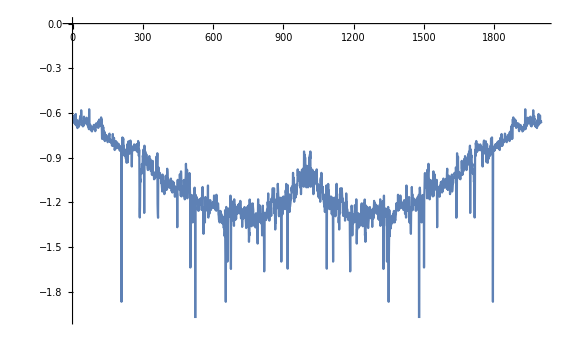

```mathematica
ListPlot[%147/.ϵ->1,Joined->True]
```

```mathematica
Join[%122[[;;,2,5]],Reverse[%122[[;;,2,5]]]];
```

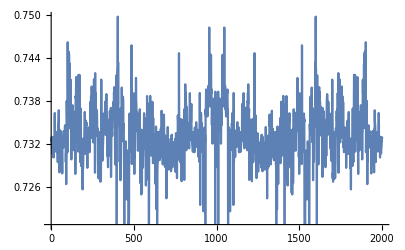

```mathematica
ListPlot[%149/.ϵ->1,Joined->True]
```

#### CF-term

```mathematica
t5trans[tpara[CFterm,ϕq,t5,t5b],t5,t5b,t5p];
```

```mathematica
t5trans[tpara[%,ϕk,t6,t6b],t6,t6b,t6p]//Simplify;
```

```mathematica
tpara[tpara[%,θq,tq,tqb],θkq,tkq,tkqb]//Simplify;
```

```mathematica
(%//togethersimply)/.{(-((-2+t5p) t5p))^(-1-ϵ) ->(2-t5p)^(-1-ϵ) t5p^(-1-ϵ) ,(-((-2+t6p) t6p))^(-1-ϵ) ->(2-t6p)^(-1-ϵ) t6p^(-1-ϵ) }/.{bl->1,br->1}
```

1/Gamma[-ϵ]^2 2^(3-α-4 ϵ) π^(-2 ϵ) t1^(-1+α/2) t1b^(-1+α/2) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (2-t6p)^(-1-ϵ) t6p^(-1-ϵ) (tkq tkqb)^(-1/2-ϵ) (1-2 tq)^(α+2 ϵ) (tq tqb)^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Cos[π (α+2 ϵ)] Gamma[-α-2 ϵ]^2 ((Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]+4 √(tkq tkqb) √(tq tqb) Cos[θLR]-4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]+2 √(tkq tkqb) Sin[θLR]-2 t5p √(tkq tkqb) Sin[θLR]-2 t6p √(tkq tkqb) Sin[θLR]+2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]-4 √(tkq tkqb) tq Sin[θLR]+4 t5p √(tkq tkqb) tq Sin[θLR]+4 t6p √(tkq tkqb) tq Sin[θLR]-4 t5p t6p √(tkq tkqb) tq Sin[θLR]-2 √(tq tqb) Sin[θLR]+2 t5p √(tq tqb) Sin[θLR]+4 tkq √(tq tqb) Sin[θLR]-4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)+(Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]-4 √(tkq tkqb) √(tq tqb) Cos[θLR]+4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]-2 √(tkq tkqb) Sin[θLR]+2 t5p √(tkq tkqb) Sin[θLR]+2 t6p √(tkq tkqb) Sin[θLR]-2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]+4 √(tkq tkqb) tq Sin[θLR]-4 t5p √(tkq tkqb) tq Sin[θLR]-4 t6p √(tkq tkqb) tq Sin[θLR]+4 t5p t6p √(tkq tkqb) tq Sin[θLR]-2 √(tq tqb) Sin[θLR]+2 t5p √(tq tqb) Sin[θLR]+4 tkq √(tq tqb) Sin[θLR]-4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)+(Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]-4 √(tkq tkqb) √(tq tqb) Cos[θLR]+4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]+2 √(tkq tkqb) Sin[θLR]-2 t5p √(tkq tkqb) Sin[θLR]-2 t6p √(tkq tkqb) Sin[θLR]+2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]-4 √(tkq tkqb) tq Sin[θLR]+4 t5p √(tkq tkqb) tq Sin[θLR]+4 t6p √(tkq tkqb) tq Sin[θLR]-4 t5p t6p √(tkq tkqb) tq Sin[θLR]+2 √(tq tqb) Sin[θLR]-2 t5p √(tq tqb) Sin[θLR]-4 tkq √(tq tqb) Sin[θLR]+4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ)+(Cos[θLR]-2 tkq Cos[θLR]-2 tq Cos[θLR]+4 tkq tq Cos[θLR]+4 √(tkq tkqb) √(tq tqb) Cos[θLR]-4 t6p √(tkq tkqb) √(tq tqb) Cos[θLR]-2 √(tkq tkqb) Sin[θLR]+2 t5p √(tkq tkqb) Sin[θLR]+2 t6p √(tkq tkqb) Sin[θLR]-2 t5p t6p √(tkq tkqb) Sin[θLR]-2 √(-((-2+t5p) t5p)) √(-((-2+t6p) t6p)) √(tkq tkqb) Sin[θLR]+4 √(tkq tkqb) tq Sin[θLR]-4 t5p √(tkq tkqb) tq Sin[θLR]-4 t6p √(tkq tkqb) tq Sin[θLR]+4 t5p t6p √(tkq tkqb) tq Sin[θLR]+2 √(tq tqb) Sin[θLR]-2 t5p √(tq tqb) Sin[θLR]-4 tkq √(tq tqb) Sin[θLR]+4 t5p tkq √(tq tqb) Sin[θLR])^(α+2 ϵ))

```mathematica
Series[numfac%/.f_^(α+2ϵ):>(Abs@f)^(α+2ϵ)/.t1b->2-t1/.distExpl[t5p]/.distExpl[t6p]/.distExpl[t1]/.distExpl[y],{α,0,0},{ϵ,0,0}]//PowerExpand//Normal
```

-(3 diracDelta[t1] diracDelta[t5p] diracDelta[t6p] diracDelta[y])/(8 π^6 (-2+t1) (-2+t5p) (-2+t6p) √tkq √tkqb √tq √tqb ϵ^4)+(-4 Lϵ 3 diracDelta[y]+21+1)/(16 π^6 (-2+t1) (-2+t5p) 2 √tkqb √tq √tqb ϵ^3)+4+((1) (1)+4+1/((2-t5p) 4 √tqb))/π^6
 |  |  |  |

```mathematica
intexpand=DistApply[DistApply[DistApply[DistApply[%,t5p],t6p],t1],y];
```

```mathematica
allnIntEFT[intexpand/.θLR->π,{-2,0},{-4,0}]
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

«2 more identical outputs»

General::stop: Further output of N::meprec
     will be suppressed during this calculation.

General::stop: Further output of N::meprec
     will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

General::stop: Further output of N::meprec
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«2 more identical outputs»

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 7.4761249585602103032978993632
                                                              -8
      22870206706376306486806410375368923245197780066112428 10   and 
    1.840455651791065551206989664371208323461856661956731980379686993810803179
                  -7
      525369642 10   for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -5.419168806633695240911137227
                                                               -14
      063941512246650417915682262070771271997330457265635415 10    and 
    1.978365868490582701217568819088684807490493081810763125180751671870365940
                  -11
      297057138 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -1.297504779146021272902236846
                                                               -12
      630304203893349236562654475571810813945403490699796134 10    and 
    2.952088890884562124665877896987708557861454109879718442332290559719087756
                  -10
      545166545 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.005283737872047027029394635
      562553126481857418188810905469695437257190972954436669523 and 
    0.000018197684828082039373553812112580437504950807059511183075616090946855
     17797776449943 for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000809057228938466774068589
      5790101978611784968227106699210347325636527974514251534401 and 
    0.000015834018183883528469167038959457936884857508267125069743498571038435
     36163790674961 for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 1.5737736742619968469631856405
                                                              -12
      08498576899770722291646908253831857152877474189830048 10    and 
    7.924820385589196468583661299489190822442602270240164612360135711351901411
                  -10
      311761771 10    for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -1.625750641990108572273341168
                                                               -13
      119182453673995125374703953294521172224545879511860208 10    and 
    5.935097605471748103652706457266054422471479245432289346842201205011580236
                  -11
      371417734 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 6.4875238957301063645111842331
                                                              -13
      51521019466746182813273054585962902705406421908555527 10    and 
    1.476044445442281062332938948493854278930727054939859225864005405045542452
                  -10
      438876744 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0003098849581060476687449948
     141911477073171646835378324182977870994641853481464493968 and 
    0.000058851195392714594930170255253724141150971264171638275142939161570018
     66962062731099 for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 4.2021155007293823404792854232
                                                              -6
      72501545028263635978124728289725844412675213027022423 10   and 
    0.000041168009931592327960411172403928135629477108485486925713439426245615
     46409469906479 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0003100587120822332769612139
     773683031166686860605174751580869156009526075880633349885 and 
    0.000088889655159990705214978545358075734306659517546229147478606974114872
     34901104452007 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.004221715885750511827648947
      330446859758217532461601805538610466130910606535377104591 and 
    7.249608521539544309121666598811618744543169125262629544958883258285715526
                  -9
      412080148 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0004277492606118472995404416
     867899369852886770255442613933204135026210085964958650658 and 
    2.742288387682050642649313493086502955227346998621876154081350174449354494
                  -19
      651782982 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0012832477818355418986213250
     60369810955866031076632784179976147504972902973782317663 and 
    8.226865163046151927947940479259508865681891925804091216580226401911099604
                  -19
      742363353 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0006416238909177709493106625
     301849054779330155383163920899887961644281464762252222286 and 
    4.113432581523075963973970239629754432840938738709084448500622363342022904
                  -19
      390526405 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000641623890917770949310662
      5301849054779330155383163920899887961644281464762252222286 and 
    4.113432581523075963973970239629754432840938738709084448500622363342022904
                  -19
      390526405 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000641623890917770949310662
      5301849054779330155383163920899887961644281464762252222286 and 
    4.113432581523075963973970239629754432840938738709084448500622363342022904
                  -19
      390526405 10    for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0003208119454588854746553312
     650924527389665077691581960449839631973199572665957406169 and 
    2.056716290761537981986985119814877216420573718201548998331948656909656009
                  -19
      111217309 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -1.394157594215831653797209909
                                                               -7
      364615154746395754626254360736207431593307080680675793 10   and 
    3.262723939447372502418535926436264100984991498868564745031510027194423044
                  -7
      705490008 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0001069373151529618248851104
     216974842463221692563860653483245247287953666584378815841 and 
    6.855720969205126606623283732716257388068925362123621672664890050238900865
                  -20
      368303291 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.001583079786027934812595989
      148268449829939385396650600872127721354745538862694706371 and 
    4.368857642051328836366639002068747261603035375126504908760061583562338718
                  -7
      732654855 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0000249196446303314049492377
     9726431863394425540821446560949166770472594848617379023142 and 
    0.000029249248113586351289343575644420087228086568368397839428306902263196
     70920695901899 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0012832477818355418986213250
     60369810955866031076632784179976147504972902973782317663 and 
    8.226865163046151927947940479259508865681891925804091216580226401911099604
                  -19
      742363353 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 7.8688683713099842348159282025
                                                              -13
      42492884498853616108757231312986942871337434562831840 10    and 
    3.962410192794598234291830649744595411221301135130083961545854685271429441
                  -10
      069089961 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.005276809098795293833692026
      699888146010962839876245337827954811524543670562419335745 and 
    1.977688397842572662813334598181342740736305618914914920481143021585798804
                  -6
      566444465 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.006215733346266149135062417
      872699699671228226179982994129957717996011408513004283184 and 
    0.000151345865488615979445975834988036431597593723827346024739664116797811
     1542128468075 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0004812179181883282119829968
     976386791084497616537372940674789260319585977915561969177 and 
    3.085074436142306972980477679722315824630830764840252544395605001079398718
                  -19
      829783817 10    for the integral and error estimates.

{0.00064162389091777094931066253018491/(α^2 ϵ^2),(7.8688683713099842348159282025425×10^-13)/(α^2 ϵ),(0.0012832477818355418986213250603698 Lϵ)/(α^2 ϵ),-0.0052768090987952938336920266998881/α^2,(1.5737736742619968469631856405085×10^-12 Lϵ)/α^2,(0.0012832477818355418986213250603698 Lϵ^2)/α^2,-0.00064162389091777094931066253018491/(α ϵ^3),-(1.3941575942158316537972099093646×10^-7)/(α ϵ^2),-(0.00064162389091777094931066253018491 Lϵ)/(α ϵ^2),0.000024919644630331404949237797264319/(α ϵ),-(1.2975047791460212729022368466303×10^-12 Lϵ)/(α ϵ),0.0003100587120822332769612139773683/α,-(0.0052837378720470270293946355625531 Lϵ)/α,-(1.6257506419901085722733411681192×10^-13 Lϵ^2)/α,(0.00042774926061184729954044168678994 Lϵ^3)/α,0.00048121791818832821198299689763868/ϵ^4,(7.4761249585602103032978993632229×10^-8)/ϵ^3,(0.00032081194545888547465533126509245 Lϵ)/ϵ^3,-0.0008090572289384667740685895790102/ϵ^2,(6.4875238957301063645111842331515×10^-13 Lϵ)/ϵ^2,(4.2021155007293823404792854232725×10^-6)/ϵ,-(0.0015830797860279348125959891482684 Lϵ)/ϵ,0,-0.0062157333462661491350624178726997,0.00030988495810604766874499481419115 Lϵ,-0.0042217158857505118276489473304469 Lϵ^2,-5.4191688066336952409111372270639×10^-14 Lϵ^3,0.00010693731515296182488511042169748 Lϵ^4}

```mathematica
%*128 π^4//.a_:>0/;Abs@a<=10^-2
```

{7.9999999999999999998580299247433/(α^2 ϵ^2),0,(15.999999999999999999716059849487 Lϵ)/(α^2 ϵ),-65.793174767821201613863647758641/α^2,0,(15.999999999999999999716059849487 Lϵ^2)/α^2,-7.9999999999999999998580299247433/(α ϵ^3),0,-(7.9999999999999999998580299247433 Lϵ)/(α ϵ^2),0.31070719133836055518149067867486/(α ϵ),0,3.8659247758212880199591368510557/α,-(65.879565232388502726891976746953 Lϵ)/α,0,(5.3333333333333333332386866164955 Lϵ^3)/α,5.9999999999999999998935224435575/ϵ^4,0,(3.9999999999999999999290149623716 Lϵ)/ϵ^3,-10.087619745969262213554206243805/ϵ^2,0,0.052393504172280465836974535869492/ϵ,-(19.738414462884377826166130965159 Lϵ)/ϵ,0,-77.50002372729906103062148284606,3.8637583480601636932655210771701 Lϵ,-52.637888900450027436972481439633 Lϵ^2,0,1.3333333333333333333096716541239 Lϵ^4}

```mathematica
allnIntEFT[intexpand/.θLR->2/3 π,{-2,0},{-4,0}];
%*128 π^4//.a_:>0/;Abs@a<=10^-2
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«4 more identical outputs»

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 5.3362176360367374088379499327
                                                              -7
      13808428233380968840981875550504421430926749653200544 10   and 
    1.224556733068312857501300210676195525309227063800908196041829353671838566
                  -6
      394978026 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 1.0447513560131620363135239825
                                                              -6
      11163486444411110219416311247367107190696705497749053 10   and 
    2.531741901680517959157941630496124387211208832132390727268163920862558852
                  -6
      267190977 10   for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -3.527214351400336396218051612
                                                               -7
      389982250664250763864904074441306286520394918800374779 10   and 
    7.771233741303607219897080197338999931606425439546767761530822305795913917
                  -7
      121188596 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 1.9028751104233748757524984490
                                                              -7
      11068751330526773315540113214890735881420039673131781 10   and 
    4.801315964204052247650227336132002696262723613738851253756094343658680290
                  -7
      402438566 10   for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -1.297504779146021272902236846
                                                               -12
      630304203893349236562654475571810813945403490699796134 10    and 
    2.952088890884562124665877896987708557861454109879718442332290559719087756
                  -10
      545166545 10    for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.005294545955101768256235500
      588240955321875819299708074681971910875984697283947333028 and 
    0.000025972972570834335742357851141720424543880955909237044870483371655657
     40110300759041 for the integral and error estimates.

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

General::stop: Further output of N::meprec
     will be suppressed during this calculation.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000690627065867817922760434
      0505459587808714681762797296273123631760623088993566587495 and 
    0.000075132938742677355350371390445382491408631185656948213255204396836487
     71812554068750 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 6.4875238957301063645111842331
                                                              -13
      51521019466746182813273054585962902705406421908555527 10    and 
    1.476044445442281062332938948493854278930727054939859225864005405045542452
                  -10
      438876744 10    for the integral and error estimates.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

General::stop: Further output of N::meprec
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000469350692148726141416474
      3441239531617344666120973851976699023353364162501087595065 and 
    0.000038585081378469542722353239796097074681811059650585092221487885097269
     50246548619421 for the integral and error estimates.

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                              2   -2 EulerGamma  - ---
                                        2   Pi                      6
     reached while evaluating EulerGamma  + --- + --------------------.
                                            12             2

General::stop: Further output of N::meprec
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.002295399066333904194836187
      331865891625143209955727794694782890247083295080295333490 and 
    0.001256779488449007825004686577190337063833197137806696146874023131073738
     569091925092 for the integral and error estimates.

N::meprec: Internal precision limit $MaxExtraPrecision = 50.
                                                                     2
                                                               2   Pi
                                               2   2 EulerGamma  + ---
                                         2   Pi                     6
     reached while evaluating -EulerGamma  - --- + -------------------.
                                             12             2

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.004228105389595748240073164
      881388160883013184670013133890426473676590126330116234185 and 
    8.698381718681083872875546797185076720093442109470650920906241370813000798
                  -6
      747866870 10   for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 1.7787392120122458029459833109
                                                              -7
      04602809411126989613660625183501468421620163462815007 10   and 
    4.081855776894376191671000702253985084364090212669693986806097816886833527
                  -7
      759132654 10   for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0012993067801064383949348830
     45589772620316455443130488010405045662135835432541371373 and 
    0.000614327787760256254771879388798544899161667907167619587469734845998335
     8900430625353 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0003113870327893705744574628
     364410728866187728396035255090806346083105983718121741729 and 
    0.000057436613535740771435725285141000288683276336905835621487416304144751
     00129190029572 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.001583079786027934812595989
      148268449829939385396650600872127721354745538862694706371 and 
    4.368857642051328836366639002068747261603035375126504908760061583562338718
                  -7
      732654855 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0006416238909177709493106625
     301849054779330155383163920899887961644281464762252222286 and 
    4.113432581523075963973970239629754432840938738709084448500622363342022904
                  -19
      390526405 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0012832477818355418986213250
     60369810955866031076632784179976147504972902973782317663 and 
    8.226865163046151927947940479259508865681891925804091216580226401911099604
                  -19
      742363353 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0012832477818355418986213250
     60369810955866031076632784179976147504972902973782317663 and 
    8.226865163046151927947940479259508865681891925804091216580226401911099604
                  -19
      742363353 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0004277492606118472995404416
     867899369852886770255442613933204135026210085964958650658 and 
    2.742288387682050642649313493086502955227346998621876154081350174449354494
                  -19
      651782982 10    for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000641623890917770949310662
      5301849054779330155383163920899887961644281464762252222286 and 
    4.113432581523075963973970239629754432840938738709084448500622363342022904
                  -19
      390526405 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.000641623890917770949310662
      5301849054779330155383163920899887961644281464762252222286 and 
    4.113432581523075963973970239629754432840938738709084448500622363342022904
                  -19
      390526405 10    for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0004812179181883282119829968
     976386791084497616537372940674789260319585977915561969177 and 
    3.085074436142306972980477679722315824630830764840252544395605001079398718
                  -19
      829783817 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 5.2237567800658101815676199125
                                                              -7
      55817432222055551097081556236835569752059579637761632 10   and 
    1.265870950840258979578970815248062193605604416066195363634081968458441238
                  -6
      518988880 10   for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0003208119454588854746553312
     650924527389665077691581960449839631973199572665957406169 and 
    2.056716290761537981986985119814877216420573718201548998331948656909656009
                  -19
      111217309 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.003875711583789799922874432
      333586853891347241596100861054189712078157744319306230721 and 
    0.000130024321475713621348876164800667355283355130303774092006040493854280
     5885111422491 for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained 0.0001069373151529618248851104
     216974842463221692563860653483245247287953666584378815841 and 
    6.855720969205126606623283732716257388068925362123621672664890050238900865
                  -20
      368303291 10    for the integral and error estimates.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 
    2000 times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
     numerical integration. NIntegrate obtained -0.005595295775305087515053696
      723316667833292694070798522230507426813346433485739606887 and 
    0.004565338651011279042362647918267459876521733217440190436010775309948180
     750229707527 for the integral and error estimates.

{7.9999999999999999998580299247433/(α^2 ϵ^2),0,(15.999999999999999999716059849487 Lϵ)/(α^2 ϵ),-48.32378143832555333547852673953/α^2,(0.013026339833060299571652202706737 Lϵ)/α^2,(15.999999999999999999716059849487 Lϵ^2)/α^2,-7.9999999999999999998580299247433/(α ϵ^3),0,-(7.9999999999999999998580299247433 Lϵ)/(α ϵ^2),-8.6109894053970270042316178038878/(α ϵ),0,-28.619870286321084516567324051079/α,-(66.014324342299843182893069441493 Lϵ)/α,0,(5.3333333333333333332386866164955 Lϵ^3)/α,5.9999999999999999998935224435575/ϵ^4,0,(3.9999999999999999999290149623716 Lϵ)/ϵ^3,-5.8520351101935766649578377393947/ϵ^2,0,16.200229430334034501063233770678/ϵ,-(19.738414462884377826166130965159 Lϵ)/ϵ,0,-69.764182468974402039802931535731,3.8824867614448256203150379416727 Lϵ,-52.717555557950538453652645702274 Lϵ^2,0,1.3333333333333333333096716541239 Lϵ^4}

```mathematica
%*128 π^4//.a_:>0/;Abs@a<=10^-2
```

{7.9999999999999999998580299247433/(α^2 ϵ^2),0,(15.999999999999999999716059849487 Lϵ)/(α^2 ϵ),-66.018255123373078178940643287522/α^2,0,(15.999999999999999999716059849487 Lϵ^2)/α^2,-7.9999999999999999998580299247433/(α ϵ^3),0,-(7.9999999999999999998580299247433 Lϵ)/(α ϵ^2),0.20279865780524302566694653798121/(α ϵ),0,3.9069401377410120357303992344517/α,-(65.871410736516438340948579524106 Lϵ)/α,0,(5.3333333333333333332386866164955 Lϵ^3)/α,5.9999999999999999998935224435575/ϵ^4,0,(3.9999999999999999999290149623716 Lϵ)/ϵ^3,-9.8473049545699161963236705166058/ϵ^2,0,0,-(19.739202873785033108824553656002 Lϵ)/ϵ,0,-77.76010979321138092723970501494,3.7484817421265475003193324543836 Lϵ,-52.637888900450027436972481439633 Lϵ^2,0,1.3333333333333333333096716541239 Lϵ^4}

{-7.9999999999999999998580299247433/(α^2 ϵ^2),0,-(15.999999999999999999716059849487 Lϵ)/(α^2 ϵ),-11.787142335544692668870386469404/α^2,0,-(15.999999999999999999716059849487 Lϵ^2)/α^2,7.9999999999999999998580299247433/(α ϵ^3),0,(7.9999999999999999998580299247433 Lϵ)/(α ϵ^2),-0.012489529817850515727950820401805/(α ϵ),0,-10.257921399074493626221051378576/α,-(12.079687787889123924466661936756 Lϵ)/α,0,-(5.3333333333333333332386866164955 Lϵ^3)/α,-5.9999999999999999998935224435575/ϵ^4,0,-(3.9999999999999999999290149623716 Lϵ)/ϵ^3,9.5022132110445076451162630148604/ϵ^2,-(0.80098479817207420293971106983158 Lϵ)/ϵ^2,-0.75639983998230822690769555403945/ϵ,(18.243703201880447753286603838523 Lϵ)/ϵ,41.281749809305188556502748956608,-1.9883821472210739455319307439146 Lϵ,8.3087893129559170475664247961152 Lϵ^2,1.2322614968598137336589049748733 Lϵ^3,-1.3333333333333333333096716541239 Lϵ^4}

```mathematica
(Plus@@%618)+(Plus@@%620)
```

-36.47835998390619237073695605833+1.760099594905473554787401710469 Lϵ-44.32909958749411038940605664352 Lϵ^2+1.2322614968598137336589049748733 Lϵ^3+0. Lϵ^4-77.805397458917770847811029756927/α^2+(0. Lϵ^2)/α^2-6.350981261333481590490652144124/α-(77.951098524405562265415241460862 Lϵ)/α+(0. Lϵ^3)/α+0./ϵ^4+(0. Lϵ)/ϵ^3+0./(α ϵ^3)-0.345091743525408551207407501745/ϵ^2-(0.80098479817207420293971106983158 Lϵ)/ϵ^2+0./(α^2 ϵ^2)+(0. Lϵ)/(α ϵ^2)-0.75639983998230822690769555403945/ϵ-(1.49549967190458535553794981748 Lϵ)/ϵ+(0. Lϵ)/(α^2 ϵ)+0.1903091279873925099389957175794/(α ϵ)

```mathematica
(*EFT pole*)
```

```mathematica
1/Gamma[-ϵ] t1^(-1+α/2) t5p^(-1-ϵ)   y^(-1+α/2) Gamma[-α-2 ϵ]^2
```

1/(Gamma[1/2-ϵ] Gamma[-ϵ])2^(3-α-4 ϵ) π^(1/2-2 ϵ) t1^(-1+α/2) t1b^(-1+α/2) (2-t5p)^(-1-ϵ) t5p^(-1-ϵ) (tkp tkpb)^(-1/2-ϵ) (tp tpb)^(-1/2-ϵ) y^(-1+α/2) (1+y)^-α Cos[π (α+2 ϵ)] Gamma[-α-2 ϵ]^2

```mathematica
(*Full-2loop*)
```

```mathematica
1/Gamma[-ϵ] a^(-1+α) b^(-1-α-2 ϵ)   t5p^(-1-ϵ) Gamma[-2 (α+2 ϵ)]
```

```mathematica
1/Gamma[-ϵ] b^(-1-α-2 ϵ)  t^(-1+α/2)  t5p^(-1-ϵ)  y^(-1+α/2) Gamma[-2 (α+2 ϵ)]
```

#### <H_1^(s(1))>

```mathematica
numfac=(4π)/αs*(2CF)/(2π)^(2-2ϵ)(2 E^-EulerGamma)^(α+2ϵ)E^((α/2+ϵ)Lϵ)gs^2(E^EulerGamma/(4π))^ϵ;
```

```mathematica
Integrate[e1^(-1-2ϵ)*2/(n1m n1p)*E^(-I br e1 Sin[θ] Cos[ϕ])*1/(2 e1)^α,{e1,0,∞}]
```

ConditionalExpression[(2^(1-α) Gamma[-α-2 ϵ] (ⅈ br Cos[ϕ] Sin[θ])^(α+2 ϵ))/(n1m n1p), Im[br Cos[ϕ] Sin[θ]]<0&&Re[α+2 ϵ]<0]

```mathematica
dΩ1=Sin[θ]^(1-2ϵ)Sin[ϕ]^(-2ϵ)*(2 π^((1-2ϵ)/2))/Gamma[(1-2ϵ)/2];
tpara[tpara[2^(1-α) Gamma[-α-2 ϵ] ( Cos[ϕ] Sin[θ])^(α+2 ϵ)Sin[θ]^2*dΩ1,θ,tt,ttb],ϕ,tp,tpb]//PowerExpand//Simplify
```

(2^(5-2 ϵ) π^(1/2-ϵ) (1-2 tp)^(α+2 ϵ) tp^(-1/2-ϵ) tpb^(-1/2-ϵ) tt^(1+α/2) ttb^(1+α/2) Gamma[-α-2 ϵ])/Gamma[1/2-ϵ]

```mathematica
Integrate[(2^(5-2 ϵ) π^(1/2-ϵ) (1-2 tp)^(α+2 ϵ) tp^(-1/2-ϵ) tpb^(-1/2-ϵ) tt^(1+α/2) ttb^(1+α/2) Gamma[-α-2 ϵ])/Gamma[1/2-ϵ]/.{ttb->1-tt,tpb->1-tp},{tt,0,1},{tp,0,1/2}]+Integrate[(2^(5-2 ϵ) π^(1/2-ϵ) (2 tp-1)^(α+2 ϵ) tp^(-1/2-ϵ) tpb^(-1/2-ϵ) tt^(1+α/2) ttb^(1+α/2) Gamma[-α-2 ϵ])/Gamma[1/2-ϵ]/.{ttb->1-tt,tpb->1-tp},{tt,0,1},{tp,1/2,1}]
```

ConditionalExpression[-(2^(3/2-α-ϵ) π^(2-ϵ) Csc[π (α+2 ϵ)] Gamma[2+α/2] Hypergeometric2F1Regularized[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/Gamma[(5+α)/2]+(4^(-α-ϵ) π^(1-ϵ) Cos[(π α)/2] (√π (2+α) Gamma[-α/2-ϵ]+2^(3/2+α+ϵ) Cos[π ϵ] Csc[π (α+2 ϵ)] Gamma[-3/2-α/2] Gamma[2+α/2] Gamma[(5+α)/2] Hypergeometric2F1Regularized[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2]) Sec[π (α+ϵ)])/Gamma[(5+α)/2], Re[α]>-4]

```mathematica
Csc[π/2(α+2ϵ)]numfac*%/.{αs->gs^2/(4π)}//Normal
```

2^(3+α+2 ϵ) CF ⅇ^(EulerGamma ϵ+Lϵ (α/2+ϵ)-EulerGamma (α+2 ϵ)) π^ϵ Csc[1/2 π (α+2 ϵ)] (-(2^(3/2-α-ϵ) π^(2-ϵ) Csc[π (α+2 ϵ)] Gamma[2+α/2] Hypergeometric2F1Regularized[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2])/Gamma[(5+α)/2]+(4^(-α-ϵ) π^(1-ϵ) Cos[(π α)/2] (√π (2+α) Gamma[-α/2-ϵ]+2^(3/2+α+ϵ) Cos[π ϵ] Csc[π (α+2 ϵ)] Gamma[-3/2-α/2] Gamma[2+α/2] Gamma[(5+α)/2] Hypergeometric2F1Regularized[1/2-ϵ,1/2+ϵ,3/2+α+ϵ,1/2]) Sec[π (α+ϵ)])/Gamma[(5+α)/2])

```mathematica
Collect[Series[%,{α,0,0},{ϵ,0,0}]//FunctionExpand//Normal//Simplify,ϵ]
```

-16/3 CF (2 Lϵ^2+3 π^2)-(64 CF)/(3 ϵ^2)-(64 CF Lϵ)/(3 ϵ)